## sequence with decay, master equation backup 3/2

```mathematica
Clear["Global`*"];
(*定义 fidelity 函数*)Fidelity[rho_,sigma_]:=Module[{sqrtRho,inner},sqrtRho=MatrixPower[rho,1/2];
inner=sqrtRho.sigma.sqrtRho;
(Tr[MatrixPower[inner,1/2]])^2]
dim=3/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
(*Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});*)
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;


IniPhi={{1},{0},{0},{0}};

StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi//FullSimplify
StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(χ*(3*Iz3half2.Iz3half2+η*(Iplus3half2.Iplus3half2+Iminus3half2.Iminus3half2)/2))*t].StateθϕInitial[θ,ϕ]

DensityMatrixEvo[t_,θ_,ϕ_]:=StateEvo[t,θ,ϕ].ConjugateTranspose[StateEvo[t,θ,ϕ]]


(*StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].StateθϕInitial[θ,ϕ]
StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t].StateθϕInitial[θ,ϕ]

StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(3Iz3half2.Iz3half2+η/2(Ix3half2.Ix3half2-Iy3half2.Iy3half2))*t].StateθϕInitial[θ,ϕ]
StateEvo2[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].css[θ,ϕ]*)
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
θ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
(*ϕ2[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*Print[N[xVal]];
Print[yVal//FullSimplify];*)
If[First[Flatten[N[xVal]]]==0&&First[Flatten[N[yVal]]]!=0,Pi/2,N[First[Flatten[ArcTan[yVal/xVal]]]]]
]*)
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]
]
ϕ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]]]
]
In1[state_]:=N[-Ix3half2*Sin[ϕ1DM[state]]+Iy3half2*Cos[ϕ1DM[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1DM[state]]Cos[ϕ1DM[state]]-Iy3half2*Cos[θ1DM[state]]Sin[ϕ1DM[state]]+Iz3half2*Sin[θ1DM[state]]]
(*In1[state_]:=N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]
In1n2plusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]*)
In1n2plusSqure[state_]:=Tr[(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=Tr[(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=Tr[(In1[state].In2[state]+In2[state].In1[state]).state]
ξSqure[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )/Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]
ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]
ξbottomF[state_]:=N[First[Flatten[ Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]




d=4;
L0=Table[0 ,{i,d*d},{j,d*d}];
Do[L0[[i,j]]=Subscript[L, (i-1)*d*d+j],{i,1,d*d},{j,1,d*d}];
L0List=Flatten[L0];
H0=Table[0 ,{i,d},{j,d}];
ρ0=Table[0 ,{i,d},{j,d}];
Do[H0[[i,j]]=Subscript[H, (i-1)*d+j];ρ0[[i,j]]=Subscript[ρ, (i-1)*d+j],{i,1,d},{j,1,d}](*Print[L0//MatrixForm]; Print[H0//MatrixForm; Print[ρ0//MatrixForm]*)

(*RHLIST=-I*(H0.ρ0-ρ0.H0)+gamma*(PauliMatrix[3].ρ0.PauliMatrix[3]-ρ0);
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
*)
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));
(*
Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2))

RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γ, z](KroneckerProduct[Iz3half2,Identit yMatrix[2]].ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));*)
RHBlockList=Flatten[Transpose[RHLIST]];
ρBlockList=Flatten[Transpose[ρ0]]; (*Print[ρBlockList]; Print[RHBlockList//MatrixForm]*)
LHBlockList=L0.Transpose[ρBlockList];(*Print[LHBlockList//MatrixForm]; Print[LHBlockList-RHBlockList//MatrixForm//FullSimplify]*)
Solvelist=LHBlockList-RHBlockList; (*Print[Solvelist//FullSimplify//MatrixForm]; Print[Solvelist[[1]]//FullSimplify//MatrixForm]*)
L1=Table[0 ,{i,d*d},{j,d*d}];
Do[L1[[i,j]]=Coefficient[Solvelist[[i]],Subscript[ρ, j],1],{i,1,d*d},{j,1,d*d}];
Do[L1[[i]]=Sort[L1[[i]]],{i,1,d}] ;(*Print[L1//MatrixForm];*)
L1=Flatten[L1];(*Print[L1//MatrixForm];*)
Do[L1[[i]]=Solve[L1[[i]]==0,L0List],{i,1,d*d*d*d}];
L1resultList=Flatten[Sort[L1]];(*Print[L1resultList]*)
Do[L1resultList[[i]]=L1resultList[[i,2]],{i,1,d*d*d*d}];(*Print[L1resultList]*)
L1resultList=N[Partition[L1resultList,d*d]];

(*HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}});
HMATRIX=({{0, (√3)/2 ⅇ^(-ⅈ ϕ11), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ11), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});
HMATRIX=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
HMATRIX=Iz3half2.Iz3half2;*)
HMATRIX=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});

Print[HMATRIX//MatrixForm];

Do[
Subscript[H, (i-1)*d+j]=HMATRIX[[i,j]];
,{i,1,d},{j,1,d}]
Ω=0;
β=1;
Subscript[γI, z]=0.01;
Subscript[γI, x]=0.1;
Subscript[γS, z]=0;
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

General::stop: 在本次计算中，Solve::svars 的进一步输出将被抑制.

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ξtopF[DMevolve[[m,k]]];
```

```mathematica
Ix3half2//MatrixForm
```

(0 | (√5)/2 | 0 | 0 | 0 | 0
(√5)/2 | 0 | √2 | 0 | 0 | 0
0 | √2 | 0 | 3/2 | 0 | 0
0 | 0 | 3/2 | 0 | √2 | 0
0 | 0 | 0 | √2 | 0 | (√5)/2
0 | 0 | 0 | 0 | (√5)/2 | 0)

```mathematica
Iy3half2//MatrixForm
```

(0 | -(ⅈ √5)/2 | 0 | 0 | 0 | 0
(ⅈ √5)/2 | 0 | -ⅈ √2 | 0 | 0 | 0
0 | ⅈ √2 | 0 | -(3 ⅈ)/2 | 0 | 0
0 | 0 | (3 ⅈ)/2 | 0 | -ⅈ √2 | 0
0 | 0 | 0 | ⅈ √2 | 0 | -(ⅈ √5)/2
0 | 0 | 0 | 0 | (ⅈ √5)/2 | 0)

```mathematica
Iz3half2//MatrixForm
```

(5/2 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | -3/2 | 0
0 | 0 | 0 | 0 | 0 | -5/2)

```mathematica
Iz3half2.Iz3half2.{{1},{0},{0},{0}}
```

{{9/4},{0},{0},{0}}

```mathematica
(*UEvo=MatrixExp[-I*({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})*t1];
UEvo=MatrixExp[-I*Iz3half2.Iz3half2*t1];
*)
UEvo=MatrixExp[-I*({{0, (√3)/2 ⅇ^(-ⅈ ϕ11), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ11), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}})*t1];

(*IniState={{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}};
IniState=StateθϕInitial[Pi/2,Pi/2];
IniState={{1/(√2)},{0},{0},{1/(√2)}};
*)
IniState={{1/(√2)},{0},{0},{1/(√2)}};

EvoState=UEvo.IniState;

dt=0.01;
number1=10 ;
number=10;
totNumber=20;

CtTable=Table[0,{i,0,totNumber}];
(*{3.2010852203572133,1.5707963031116705,-0.05949256001795611}*)
ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi,Pi};

(*
ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2};


ϕ1Table={2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};

ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784};
*)
(*


ϕ1Table={-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,-0.5204286660499657,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.568321936589717,1.568321936589717,1.568321936589717,1.568321936589717,1.568321936589717,1.568321936589717,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,-2.3256791460970287,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

{-0.08020498865944425,1.5707963700712089,3.2217977877748813}
{3.221325162416943,1.570796297660026,-0.07973245576386301}
{2.477645500214468,-1.3749092762546273,0.5757622283635273}
{2.565836754991806,4.516468509150052,0.6639559593359925}



{-0.5204286660499657,1.568321936589717,-2.3256791460970287}
{0.5466940336400885,-1.5696775200128563,2.368817320960213}


3.2211560479365566,1.570796339304493,-0.0795633935280784


ϕ1Table={2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,2.581055163108225,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,3.9125553774195057,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0.8791183546201431,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,3.2211560479365566,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,1.570796339304493,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,-0.0795633935280784,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
*)

(*
ϕ1Table=Table[2.581055163108225,{i,0,totNumber}];
ϕ2Table=Table[3.9125553774195057,{i,0,totNumber}];
ϕ3Table=Table[0.8791183546201431,{i,0,totNumber}];

2.581055163108225,3.9125553774195057,0.8791183546201431*)
(*IniStateBox={{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}};
{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}
*)
IniStateBox={IniState};

fvaluebox={1};
SqueezeListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{i,number*totNumber}];
TargetStateBox={{{1},{0},{0},{0}},{{0},{1},{0},{0}},{{0},{0},{1},{0}},{{0},{0},{0},{1}}};
DM=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMList=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{l,totNumber}];
Do[
Do[
(*If[l==1,DM[[m,k]]={{0.014266137103963622,0.07524799682662793-0.035194299228108586 ⅈ,-0.03628279530844325-0.07535193660773755 ⅈ,0.0001868360934605961+0.012935386266371212 ⅈ},{0.07524799682662886+0.03519429922810941 ⅈ,0.48372587998333433,-0.005484950920537914-0.4869594194301351 ⅈ,-0.030925877825707604+0.06868975553520279 ⅈ},{-0.03628279530844408+0.07535193660773697 ⅈ,-0.005484950920537898+0.4869594194301243 ⅈ,0.49027676763231237,-0.06879825523355766-0.031911477322157863 ⅈ},{0.0001868360934605111-0.012935386266371003 ⅈ,-0.030925877825709953-0.06868975553520275 ⅈ,-0.06879825523355883+0.03191147732215779 ⅈ,0.011731215280381306}},DM[[m,k]]=StateFinal;];*)
If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];

(*If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];*)
DMList[[m,k]]=Flatten[Transpose[DM[[m,k]]]];
,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]

TargetStateDMBox=Table[0,{i,Length[TargetStateBox]}];
Do[
TargetStateDMBox[[i]]=TargetStateBox[[i]].ConjugateTranspose[TargetStateBox[[i]]];
,{i,1,Length[TargetStateDMBox]}]


FListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{j,1,Length[TargetStateBox]},{i,number}];

DMevolvemid=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMevolve=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
(*Print[FListBox];*)
Do[
Do[
ϕ11=ϕ1Table[[l]]+RandomReal[{-0.5,0.5}];
ϕ2=ϕ2Table[[l]]+RandomReal[{-0.5,0.5}];
ϕ3=ϕ3Table[[l]]+RandomReal[{-0.5,0.5}];

DMevolvemid[[m,k]]=N[MatrixExp[(L1resultList/. t->(i)*dt)*dt].DMList[[m,k]]];

DMevolve[[m,k]]=Transpose[Partition[DMevolvemid[[m,k]],d]];

SqueezeListBox[[m,k,i+(l-1)*number1]]=ξtopF[DMevolve[[m,k]]];
DMListBox[[m,k,l]]=DMevolve[[m,k]];

FListBox[[m,k,1,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[1]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[1]]]])^1;
FListBox[[m,k,2,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[2]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[2]]]])^1;
FListBox[[m,k,3,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[3]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[3]]]])^1;
FListBox[[m,k,4,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[4]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[4]]]])^1;

If[i==number1,StateFinal=DMevolve[[m,k]]];


DMList[[m,k]]=DMevolvemid[[m,k]];
(*If[Divisible[i,number1/printnumber],Print[i,"/",number1,"   m: ",m,"   k: ",k]];*)
,{i,1,number1}];

,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]
Print[l];
,{l,1,totNumber}]
```

Flatten::normal: Flatten[0.+0. ⅈ] 中的位置 1 处应该是非原子表达式.

Power::infy: 碰到无穷表达式 1/(0.+0. ⅈ).

Infinity::indet: 碰到不定表达式 (0.+0. ⅈ) ComplexInfinity.

Flatten::normal: Flatten[Indeterminate] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Power::infy: 碰到无穷表达式 1/(0.+0. ⅈ).

Infinity::indet: 碰到不定表达式 (0.+0. ⅈ) ComplexInfinity.

Power::infy: 碰到无穷表达式 1/(0.+0. ⅈ).

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 (0.+0. ⅈ) ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

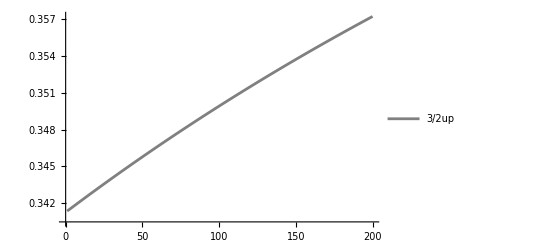

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]
```

{{1/8,-(ⅈ √3)/8,-(√3)/8,ⅈ/8},{(ⅈ √3)/8,3/8,-(3 ⅈ)/8,-(√3)/8},{-(√3)/8,(3 ⅈ)/8,3/8,-(ⅈ √3)/8},{-ⅈ/8,-(√3)/8,(ⅈ √3)/8,1/8}}

```mathematica
Chop[DMListBox[[1,1,4]]]
```

{{0.0142661,0.073758-0.0344974 ⅈ,-0.0334932-0.0695586 ⅈ,0.000156059+0.0108045 ⅈ},{0.073758+0.0344974 ⅈ,0.483726,-0.00537634-0.477317 ⅈ,-0.0285482+0.0634086 ⅈ},{-0.0334932+0.0695586 ⅈ,-0.00537634+0.477317 ⅈ,0.490277,-0.067436-0.0312796 ⅈ},{0.000156059-0.0108045 ⅈ,-0.0285482-0.0634086 ⅈ,-0.067436+0.0312796 ⅈ,0.0117312}}

```mathematica
Chop[DMListBox[[1,1,5]]]
```

{{0.0142661,0.075248-0.0351943 ⅈ,-0.0362828-0.0753519 ⅈ,0.000186836+0.0129354 ⅈ},{0.075248+0.0351943 ⅈ,0.483726,-0.00548495-0.486959 ⅈ,-0.0309259+0.0686898 ⅈ},{-0.0362828+0.0753519 ⅈ,-0.00548495+0.486959 ⅈ,0.490277,-0.0687983-0.0319115 ⅈ},{0.000186836-0.0129354 ⅈ,-0.0309259-0.0686898 ⅈ,-0.0687983+0.0319115 ⅈ,0.0117312}}

```mathematica
ξtopF[{{0.014266137103963622,0.07524799682662793-0.035194299228108586 ⅈ,-0.03628279530844325-0.07535193660773755 ⅈ,0.0001868360934605961+0.012935386266371212 ⅈ},{0.07524799682662886+0.03519429922810941 ⅈ,0.48372587998333433,-0.005484950920537914-0.4869594194301351 ⅈ,-0.030925877825707604+0.06868975553520279 ⅈ},{-0.03628279530844408+0.07535193660773697 ⅈ,-0.005484950920537898+0.4869594194301243 ⅈ,0.49027676763231237,-0.06879825523355766-0.031911477322157863 ⅈ},{0.0001868360934605111-0.012935386266371003 ⅈ,-0.030925877825709953-0.06868975553520275 ⅈ,-0.06879825523355883+0.03191147732215779 ⅈ,0.011731215280381306}}]
```

Flatten::normal: Flatten[1.09015+1.94289×10^-16 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.57031+8.53114×10^-20 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.57061+9.35034×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

```mathematica
SqDm={{0.014266137103963622,0.07524799682662793-0.035194299228108586 ⅈ,-0.03628279530844325-0.07535193660773755 ⅈ,0.0001868360934605961+0.012935386266371212 ⅈ},{0.07524799682662886+0.03519429922810941 ⅈ,0.48372587998333433,-0.005484950920537914-0.4869594194301351 ⅈ,-0.030925877825707604+0.06868975553520279 ⅈ},{-0.03628279530844408+0.07535193660773697 ⅈ,-0.005484950920537898+0.4869594194301243 ⅈ,0.49027676763231237,-0.06879825523355766-0.031911477322157863 ⅈ},{0.0001868360934605111-0.012935386266371003 ⅈ,-0.030925877825709953-0.06868975553520275 ⅈ,-0.06879825523355883+0.03191147732215779 ⅈ,0.011731215280381306}};
```

```mathematica
Fidelitylist=Table[0,{m,21}];
Fidelitylist[[1]]=1;
Do[
Fidelitylist[[i]]=Fidelity[N[(IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]).ConjugateTranspose[IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]]],DMListBox[[1,1,i-1]]];
(*
Fidelitylist[[i]]=Fidelity[N[(SqDm.ConjugateTranspose[SqDm]).ConjugateTranspose[SqDm.ConjugateTranspose[SqDm]]],DMListBox[[1,1,i-1]]]

Fidelitylist[[i]]=Fidelity[N[(IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]).ConjugateTranspose[IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]]],DMListBox[[1,1,i-1]]];*)
,{i,2,21}]
```

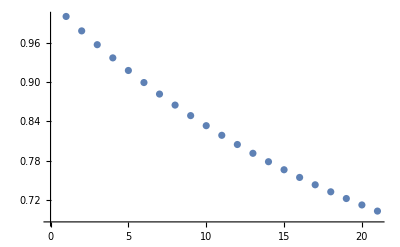

```mathematica
ListPlot[Fidelitylist]
```

```mathematica
Chop[Fidelitylist]
```

{1,0.977999,0.956966,0.936858,0.917635,0.899258,0.88169,0.864894,0.848838,0.833488,0.818814,0.804785,0.791374,0.778553,0.766296,0.754578,0.743376,0.732667,0.722429,0.712642,0.703285}

{1,0.996892,0.993809,0.990752,0.98772,0.984712,0.981728,0.978769,0.975833,0.972921,0.970031,0.967165,0.96432,0.961498,0.958698,0.955919,0.953161,0.950425,0.947709,0.945014,0.942339}

```mathematica
Pihalf2Pihalf2Iz={1,0.9925742721738721,0.9852942289507096,0.9781556939762356,0.9711546371666402,0.9642871689812548,0.9575495349333613,0.9509381103289231,0.9444493952235402,0.9380800095882115,0.9318266886750173,0.9256862785741761,0.9196557319542894,0.913732103977965,0.9079125483853355,0.9021943137383261,0.8965747398188104,0.8910512541741277,0.8856213688036826,0.8802826769806318,0.875032850202943};
Cat3half2N3half2Iz={1,0.97799874091655,0.9569655926356133,0.936857955844016,0.9176351057056352,0.8992581093796864,0.881689747168424,0.8648944371345257,0.8488381630355128,0.8334884054292341,0.8188140758108827,0.8047854536481513,0.7913741261869907,0.7785529309060828,0.7662959005034445,0.7545782103037698,0.7433761279799811,0.7326669654871517,0.722429033111466,0.7126415955411323,0.7032848298702947};
Sq3half2Iz={1,0.9969916585118825,0.9940063283198048,0.9910437221958953,0.9881035583716867,0.9851855604042249,0.9822894570461165,0.9794149821194551,0.9765618743933975,0.9737298774653406,0.9709187396455184,0.9681282138449652,0.9653580574666532,0.9626080322997649,0.959877904416969,0.9571674440745822,0.9544764256155703,0.9518046273752186,0.9491518315894719,0.9465178243057772,0.943902395296409};
Pihalf2Pihalf2IzIz={1,0.9992507495002487,0.9985029960039951,0.9977567365202238,0.9970119680638944,0.9962686876559353,0.9955268923232186,0.9947865790985682,0.9940477450207251,0.9933103871343549,0.9925745024900249,0.9918400881441952,0.9911071411592068,0.9903756586032703,0.9896456375504566,0.9889170750806783,0.988189968279687,0.9874643142390513,0.9867401100561571,0.9860173528341853,0.9852960396821056};
Cat3half2N3half2IzIz={1,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004};
Sq3half2IzIz={1,0.9998988152582413,0.9997978326837459,0.9996970518725711,0.9995964724215881,0.9994960939284849,0.9993959159917434,0.9992959382106518,0.9991961601853029,0.9990965815165805,0.9989972018061699,0.9988980206565556,0.9987990376710082,0.9987002524536001,0.9986016646091832,0.998503273743416,0.9984050794627265,0.9983070813743427,0.9982092790862687,0.9981116722072978,0.9980142603470028};
```

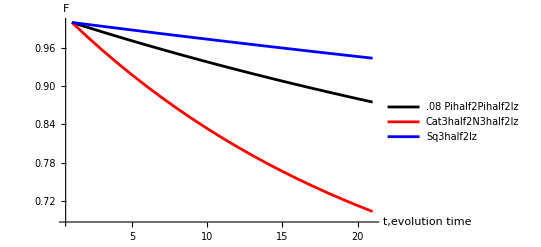

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2Iz,Cat3half2N3half2Iz,Sq3half2Iz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2Iz","Cat3half2N3half2Iz","Sq3half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

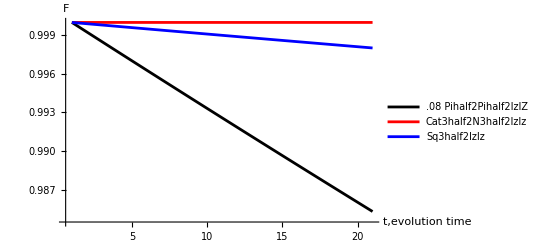

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2IzIz,Cat3half2N3half2IzIz,Sq3half2IzIz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2IzIZ","Cat3half2N3half2IzIz","Sq3half2IzIz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

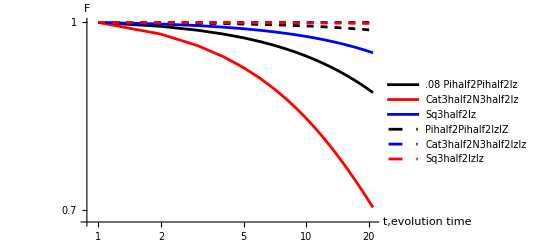

```mathematica
Plot3half2Fidelity=ListLogLogPlot[{Pihalf2Pihalf2Iz,Cat3half2N3half2Iz,Sq3half2Iz,Pihalf2Pihalf2IzIz,Cat3half2N3half2IzIz,Sq3half2IzIz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2Iz","Cat3half2N3half2Iz","Sq3half2Iz","Pihalf2Pihalf2IzIZ","Cat3half2N3half2IzIz","Sq3half2IzIz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,{Black,Dashed},{Blue,Dashed},{Red,Dashed}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

```mathematica
DMListBox[[1,1]]
```

{{{0.0918286-2.75254×10^-18 ⅈ,0.0237584-0.190681 ⅈ,-0.188268-0.0233727 ⅈ,0.00110727+0.0873856 ⅈ},{0.0237584+0.190681 ⅈ,0.406672-3.45566×10^-18 ⅈ,-0.000997263-0.405896 ⅈ,-0.187319+0.0261142 ⅈ},{-0.188268+0.0233727 ⅈ,-0.000997263+0.405896 ⅈ,0.409562+9.32406×10^-18 ⅈ,-0.0257596-0.191208 ⅈ},{0.00110727-0.0873856 ⅈ,-0.187319-0.0261142 ⅈ,-0.0257596+0.191208 ⅈ,0.091937-5.09506×10^-18 ⅈ}},{{0.0634382-8.50625×10^-18 ⅈ,0.0415946-0.158927 ⅈ,-0.152771-0.0407253 ⅈ,0.00122915+0.0566604 ⅈ},{0.0415946+0.158927 ⅈ,0.437652-1.257×10^-17 ⅈ,-0.00193415-0.431295 ⅈ,-0.15264+0.0449363 ⅈ},{-0.152771+0.0407253 ⅈ,-0.00193415+0.431295 ⅈ,0.435066+3.77295×10^-17 ⅈ,-0.0442265-0.158258 ⅈ},{0.00122915-0.0566604 ⅈ,-0.15264-0.0449363 ⅈ,-0.0442265+0.158258 ⅈ,0.0638438-1.0835×10^-17 ⅈ}},{{0.0409852-2.46924×10^-17 ⅈ,0.0565261-0.119181 ⅈ,-0.114051-0.0565115 ⅈ,0.00180178+0.0338614 ⅈ},{0.0565261+0.119181 ⅈ,0.449489+2.68653×10^-17 ⅈ,-0.00394326-0.449751 ⅈ,-0.110393+0.0632167 ⅈ},{-0.114051+0.0565115 ⅈ,-0.00394326+0.449751 ⅈ,0.467052+2.14657×10^-17 ⅈ,-0.0637176-0.121133 ⅈ},{0.00180178-0.0338614 ⅈ,-0.110393-0.0632167 ⅈ,-0.0637176+0.121133 ⅈ,0.0424744-2.51895×10^-17 ⅈ}},{{0.0273352-5.22754×10^-17 ⅈ,0.0741291-0.0782139 ⅈ,-0.0697358-0.0730916 ⅈ,0.00074534+0.0200548 ⅈ},{0.0741291+0.0782139 ⅈ,0.472756+8.19414×10^-17 ⅈ,-0.00404197-0.460223 ⅈ,-0.0675308+0.0772249 ⅈ},{-0.0697358+0.0730916 ⅈ,-0.00404197+0.460223 ⅈ,0.471904+1.70196×10^-17 ⅈ,-0.0770138-0.0771972 ⅈ},{0.00074534-0.0200548 ⅈ,-0.0675308-0.0772249 ⅈ,-0.0770138+0.0771972 ⅈ,0.0280052-3.29489×10^-17 ⅈ}},{{0.0182437-7.55141×10^-17 ⅈ,0.078397-0.0331428 ⅈ,-0.0246537-0.0774168 ⅈ,0.000702933+0.0130653 ⅈ},{0.078397+0.0331428 ⅈ,0.481136+7.61158×10^-17 ⅈ,-0.00455759-0.464086 ⅈ,-0.0225386+0.0877521 ⅈ},{-0.0246537+0.0774168 ⅈ,-0.00455759+0.464086 ⅈ,0.478863+4.67258×10^-17 ⅈ,-0.0882583-0.0325731 ⅈ},{0.000702933-0.0130653 ⅈ,-0.0225386-0.0877521 ⅈ,-0.0882583+0.0325731 ⅈ,0.0217573-4.62025×10^-17 ⅈ}},{{0.0168363-9.80065×10^-17 ⅈ,0.0731958+0.000912308 ⅈ,0.0116994-0.0854306 ⅈ,-0.0130511+0.00983614 ⅈ},{0.0731958-0.000912308 ⅈ,0.394669+1.08244×10^-16 ⅈ,0.0107469-0.450865 ⅈ,-0.0584915+0.073017 ⅈ},{0.0116994+0.0854306 ⅈ,0.0107469+0.450865 ⅈ,0.558175+2.33078×10^-17 ⅈ,-0.0920069-0.0802424 ⅈ},{-0.0130511-0.00983614 ⅈ,-0.0584915-0.073017 ⅈ,-0.0920069+0.0802424 ⅈ,0.0303195-3.1644×10^-17 ⅈ}},{{0.019859-1.14415×10^-16 ⅈ,0.0659268+0.0252053 ⅈ,0.0492616-0.0895841 ⅈ,-0.0252247+0.00115302 ⅈ},{0.0659268-0.0252053 ⅈ,0.306125+1.08416×10^-16 ⅈ,0.0250406-0.415896 ⅈ,-0.0833928+0.0578562 ⅈ},{0.0492616+0.0895841 ⅈ,0.0250406+0.415896 ⅈ,0.626533+1.04077×10^-17 ⅈ,-0.0966184-0.13292 ⅈ},{-0.0252247-0.00115302 ⅈ,-0.0833928-0.0578562 ⅈ,-0.0966184+0.13292 ⅈ,0.0474836-3.43618×10^-18 ⅈ}},{{0.0255957-1.31944×10^-16 ⅈ,0.0568309+0.0397463 ⅈ,0.0843007-0.0887647 ⅈ,-0.0347647-0.0129132 ⅈ},{0.0568309-0.0397463 ⅈ,0.225336+8.47083×10^-17 ⅈ,0.0339051-0.364173 ⅈ,-0.0974445+0.0394702 ⅈ},{0.0843007+0.0887647 ⅈ,0.0339051+0.364173 ⅈ,0.676714-7.80264×10^-18 ⅈ,-0.0943944-0.190417 ⅈ},{-0.0347647+0.0129132 ⅈ,-0.0974445-0.0394702 ⅈ,-0.0943944+0.190417 ⅈ,0.0723538+5.78068×10^-17 ⅈ}},{{0.032509-1.45903×10^-16 ⅈ,0.0473417+0.0438301 ⅈ,0.112868-0.0844829 ⅈ,-0.0426235-0.0288671 ⅈ},{0.0473417-0.0438301 ⅈ,0.154128+4.99573×10^-17 ⅈ,0.04191-0.297481 ⅈ,-0.0999477+0.0237662 ⅈ},{0.112868+0.0844829 ⅈ,0.04191+0.297481 ⅈ,0.70431-2.57952×10^-17 ⅈ,-0.096985-0.249241 ⅈ},{-0.0426235+0.0288671 ⅈ,-0.0999477-0.0237662 ⅈ,-0.096985+0.249241 ⅈ,0.109053+1.24832×10^-16 ⅈ}},{{0.0387054-1.57492×10^-16 ⅈ,0.0379704+0.0399369 ⅈ,0.132428-0.0769553 ⅈ,-0.0482254-0.045187 ⅈ},{0.0379704-0.0399369 ⅈ,0.0984546+2.9498×10^-19 ⅈ,0.0466861-0.224232 ⅈ,-0.0906707+0.00914193 ⅈ},{0.132428+0.0769553 ⅈ,0.0466861+0.224232 ⅈ,0.707034-2.00977×10^-17 ⅈ,-0.100603-0.304625 ⅈ},{-0.0482254+0.045187 ⅈ,-0.0906707-0.00914193 ⅈ,-0.100603+0.304625 ⅈ,0.155806+1.80766×10^-16 ⅈ}},{{0.0447733-1.62145×10^-16 ⅈ,0.0311636+0.0290385 ⅈ,0.144543-0.070743 ⅈ,-0.0505321-0.0619864 ⅈ},{0.0311636-0.0290385 ⅈ,0.0571277-4.97072×10^-17 ⅈ,0.0543134-0.144815 ⅈ,-0.0676017-0.0114977 ⅈ},{0.144543+0.070743 ⅈ,0.0543134+0.144815 ⅈ,0.689979-6.95851×10^-17 ⅈ,-0.0925529-0.353968 ⅈ},{-0.0505321+0.0619864 ⅈ,-0.0676017+0.0114977 ⅈ,-0.0925529+0.353968 ⅈ,0.20812+2.81517×10^-16 ⅈ}},{{0.0481614-1.60667×10^-16 ⅈ,0.0259784+0.0146494 ⅈ,0.146232-0.0623771 ⅈ,-0.051825-0.0755206 ⅈ},{0.0259784-0.0146494 ⅈ,0.0347685-9.49797×10^-17 ⅈ,0.06337-0.0698475 ⅈ,-0.0360068-0.032094 ⅈ},{0.146232+0.0623771 ⅈ,0.06337+0.0698475 ⅈ,0.645428-9.86356×10^-17 ⅈ,-0.0899224-0.393226 ⅈ},{-0.051825+0.0755206 ⅈ,-0.0360068+0.032094 ⅈ,-0.0899224+0.393226 ⅈ,0.271642+3.54909×10^-16 ⅈ}},{{0.0481729-1.5942×10^-16 ⅈ,0.0204237-0.000498469 ⅈ,0.138941-0.0525741 ⅈ,-0.0496814-0.084409 ⅈ},{0.0204237+0.000498469 ⅈ,0.027699-1.81738×10^-16 ⅈ,0.0663572-0.00144535 ⅈ,0.0064832-0.0502919 ⅈ},{0.138941+0.0525741 ⅈ,0.0663572+0.00144535 ⅈ,0.585717-1.12669×10^-16 ⅈ,-0.0834468-0.41884 ⅈ},{-0.0496814+0.084409 ⅈ,0.0064832+0.0502919 ⅈ,-0.0834468+0.41884 ⅈ,0.338411+4.54188×10^-16 ⅈ}},{{0.0469966-1.4282×10^-16 ⅈ,0.0157466-0.0150321 ⅈ,0.125927-0.0438867 ⅈ,-0.0466267-0.0893132 ⅈ},{0.0157466+0.0150321 ⅈ,0.0348248-2.86451×10^-16 ⅈ,0.0653875+0.0576086 ⅈ,0.0572376-0.0668495 ⅈ},{0.125927+0.0438867 ⅈ,0.0653875-0.0576086 ⅈ,0.508283-1.19113×10^-16 ⅈ,-0.076921-0.428263 ⅈ},{-0.0466267+0.0893132 ⅈ,0.0572376+0.0668495 ⅈ,-0.076921+0.428263 ⅈ,0.409896+5.49032×10^-16 ⅈ}},{{0.0437248-1.17828×10^-16 ⅈ,0.0124263-0.0263749 ⅈ,0.107854-0.0350671 ⅈ,-0.0414587-0.0885092 ⅈ},{0.0124263+0.0263749 ⅈ,0.0538494-3.9763×10^-16 ⅈ,0.0633858+0.100052 ⅈ,0.109699-0.0827317 ⅈ},{0.107854+0.0350671 ⅈ,0.0633858-0.100052 ⅈ,0.421834-9.66678×10^-17 ⅈ,-0.0697911-0.419591 ⅈ},{-0.0414587+0.0885092 ⅈ,0.109699+0.0827317 ⅈ,-0.0697911+0.419591 ⅈ,0.480592+6.11755×10^-16 ⅈ}},{{0.0385219-9.848×10^-17 ⅈ,0.00846984-0.033315 ⅈ,0.0858633-0.0287616 ⅈ,-0.0367136-0.0806019 ⅈ},{0.00846984+0.033315 ⅈ,0.0803958-5.3716×10^-16 ⅈ,0.0577902+0.125491 ⅈ,0.162705-0.0942635 ⅈ},{0.0858633+0.0287616 ⅈ,0.0577902-0.125491 ⅈ,0.332189-4.67877×10^-17 ⅈ,-0.0599111-0.393368 ⅈ},{-0.0367136+0.0806019 ⅈ,0.162705+0.0942635 ⅈ,-0.0599111+0.393368 ⅈ,0.548893+6.82395×10^-16 ⅈ}},{{0.0328446-7.41258×10^-17 ⅈ,0.00516575-0.0351311 ⅈ,0.064435-0.0213797 ⅈ,-0.0285336-0.0683836 ⅈ},{0.00516575+0.0351311 ⅈ,0.109819-6.85995×10^-16 ⅈ,0.0470056+0.134717 ⅈ,0.212906-0.0987362 ⅈ},{0.064435+0.0213797 ⅈ,0.0470056-0.134717 ⅈ,0.246856-4.3088×10^-17 ⅈ,-0.0513876-0.350265 ⅈ},{-0.0285336+0.0683836 ⅈ,0.212906+0.0987362 ⅈ,-0.0513876+0.350265 ⅈ,0.61048+8.01472×10^-16 ⅈ}},{{0.0271477-5.16914×10^-17 ⅈ,0.00424317-0.0322071 ⅈ,0.0440407-0.0149369 ⅈ,-0.0191102-0.0510071 ⅈ},{0.00424317+0.0322071 ⅈ,0.141495-7.79184×10^-16 ⅈ,0.039951+0.12637 ⅈ,0.25509-0.10888 ⅈ},{0.0440407+0.0149369 ⅈ,0.039951-0.12637 ⅈ,0.166398-3.23557×10^-17 ⅈ,-0.042408-0.28863 ⅈ},{-0.0191102+0.0510071 ⅈ,0.25509+0.10888 ⅈ,-0.042408+0.28863 ⅈ,0.66496+8.62059×10^-16 ⅈ}},{{0.0223928-3.60697×10^-17 ⅈ,0.00408576-0.0247133 ⅈ,0.0275926-0.0102518 ⅈ,-0.00913284-0.0299915 ⅈ},{0.00408576+0.0247133 ⅈ,0.169324-8.33971×10^-16 ⅈ,0.0328134+0.103138 ⅈ,0.285966-0.118522 ⅈ},{0.0275926+0.0102518 ⅈ,0.0328134-0.103138 ⅈ,0.100881-9.09647×10^-18 ⅈ,-0.0311718-0.213795 ⅈ},{-0.00913284+0.0299915 ⅈ,0.285966+0.118522 ⅈ,-0.0311718+0.213795 ⅈ,0.707402+8.77287×10^-16 ⅈ}},{{0.0193232-2.32006×10^-17 ⅈ,0.00523819-0.0135 ⅈ,0.0169007-0.00693603 ⅈ,0.0041364-0.00795646 ⅈ},{0.00523819+0.0135 ⅈ,0.188765-9.18298×10^-16 ⅈ,0.0241167+0.0698692 ⅈ,0.305822-0.119281 ⅈ},{0.0169007+0.00693603 ⅈ,0.0241167-0.0698692 ⅈ,0.0555911+1.4382×10^-17 ⅈ,-0.0167155-0.131412 ⅈ},{0.0041364+0.00795646 ⅈ,0.305822+0.119281 ⅈ,-0.0167155+0.131412 ⅈ,0.736321+9.24872×10^-16 ⅈ}}}

```mathematica
RandomReal[{-0.1,0.1}]
```

-0.0832414

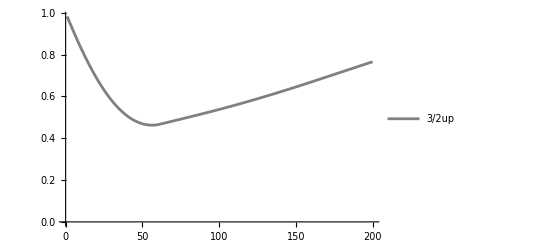

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2),10^-7]
```

{0.982046,0.964297,0.946761,0.929448,0.912367,0.895528,0.878937,0.862604,0.846536,0.83074,0.815223,0.799992,0.785054,0.770414,0.756078,0.742052,0.72834,0.714948,0.70188,0.68914,0.676732,0.66466,0.652927,0.641536,0.63049,0.619791,0.609441,0.599442,0.589796,0.580505,0.571568,0.562988,0.554764,0.546897,0.539387,0.532235,0.525439,0.518999,0.512914,0.507184,0.501808,0.496784,0.49211,0.487786,0.48381,0.48018,0.476894,0.473951,0.471348,0.469084,0.467157,0.465564,0.464304,0.463375,0.462775,0.462502,0.462554,0.462929,0.463626,0.464643,0.466406,0.468169,0.469931,0.471695,0.473458,0.475223,0.476989,0.478757,0.480526,0.482298,0.484071,0.485848,0.487627,0.489409,0.491194,0.492983,0.494775,0.496572,0.498373,0.500178,0.501988,0.503803,0.505623,0.507449,0.509279,0.511116,0.512958,0.514807,0.516662,0.518523,0.520391,0.522265,0.524147,0.526035,0.527931,0.529834,0.531744,0.533662,0.535588,0.537522,0.539464,0.541414,0.543372,0.545338,0.547312,0.549295,0.551287,0.553287,0.555295,0.557312,0.559338,0.561373,0.563417,0.565469,0.56753,0.5696,0.571679,0.573767,0.575864,0.577969,0.580084,0.582207,0.584339,0.58648,0.588629,0.590788,0.592955,0.59513,0.597314,0.599507,0.601707,0.603917,0.606134,0.608359,0.610593,0.612835,0.615084,0.617341,0.619606,0.621878,0.624158,0.626444,0.628738,0.631039,0.633347,0.635662,0.637983,0.64031,0.642644,0.644984,0.647329,0.649681,0.652038,0.6544,0.656768,0.65914,0.661518,0.6639,0.666287,0.668678,0.671073,0.673472,0.675874,0.67828,0.68069,0.683102,0.685518,0.687936,0.690356,0.692779,0.695204,0.697631,0.700059,0.702489,0.70492,0.707351,0.709784,0.712217,0.714651,0.717084,0.719517,0.72195,0.724383,0.726814,0.729245,0.731674,0.734102,0.736528,0.738953,0.741375,0.743795,0.746212,0.748627,0.751038,0.753447,0.755852,0.758253,0.760651,0.763045,0.765434}

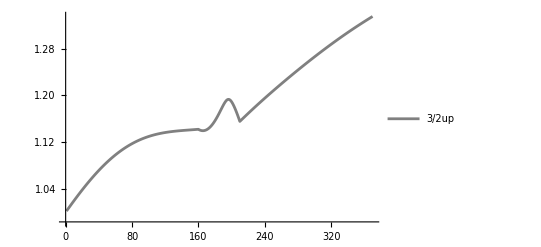

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

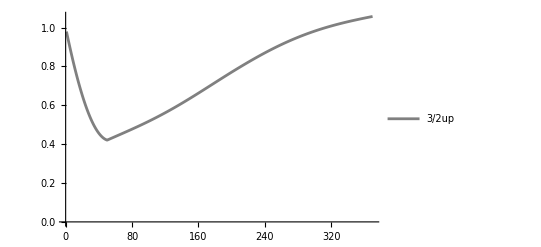

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

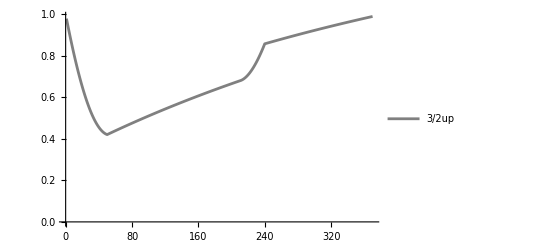

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

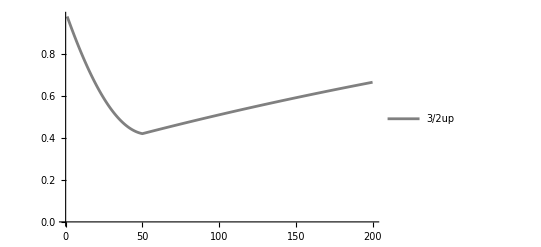

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Length[SqueezeListBox[[1,1]]/(3/2)]
```

200

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.970012,0.940413,0.911204,0.882386,0.853967,0.825953,0.798356,0.771188,0.744464,0.7182,0.692415,0.667128,0.642361,0.618137,0.594479,0.571412,0.548961,0.527153,0.506014,0.485571,0.465852,0.446885,0.428697,0.411316,0.394769,0.379084,0.364288,0.350406,0.337465,0.32549,0.314506,0.304537,0.295604,0.28773,0.280937,0.275243,0.270667,0.267228,0.26494,0.263819,0.263879,0.265131,0.267586,0.271254,0.276142,0.282256,0.289602,0.298181,0.307996,0.319047,0.331331,0.344845,0.359584,0.375541,0.392708,0.411075,0.430631,0.451361,0.473252,0.496286,0.520446,0.545712,0.572063,0.599476,0.627927,0.657391,0.687841,0.719248,0.751584,0.784816,0.818913,0.853841,0.889566,0.926053,0.963264,1.00116,1.03971,1.07886,1.11859,1.15884,1.19958,1.24076,1.28234,1.32427,1.36652,1.40904,1.45178,1.4947,1.53775,1.58089,1.62407,1.66724,1.71036,1.75339,1.79627,1.83897,1.88143,1.92361,1.96547,2.00696,2.04803,2.08864,2.12874,2.16829,2.20724,2.24553,2.28311,2.31993,2.35591,2.39096,2.42496,2.45772,2.48891,2.51787,2.54301,2.55986,2.55719,2.52715,2.48116,2.4295,2.37595,2.32193,2.26806,2.21467,2.16198,2.11014,2.05927,2.00946,1.9608,1.91336,1.86721,1.82242,1.77905,1.73715,1.69677,1.65797,1.62079,1.58527,1.55146,1.51938,1.48907,1.46056,1.43388,1.40905,1.38609,1.36503,1.34587,1.32863,1.31331,1.29993,1.28848,1.27897,1.27139,1.26574,1.262,1.26018,1.26024,1.26218,1.26598,1.27161,1.27904,1.28826,1.29923,1.31191,1.32628,1.34229,1.3599,1.37908,1.39978,1.42196,1.44555,1.47052,1.49682,1.52438,1.55315,1.58307,1.61409,1.64613,1.67913,1.71303,1.74773,1.78318,1.81926,1.85587,1.89287,1.93008,1.96719,2.00371,2.03856,2.06925,2.09008,2.09442,2.0848,2.06845,2.04931,2.02901,2.00824,1.98735,1.96653,1.94589}

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.969193,0.938692,0.908504,0.87864,0.849109,0.819925,0.791105,0.762665,0.734626,0.707009,0.679836,0.653131,0.62692,0.601229,0.576086,0.551519,0.527556,0.504228,0.481565,0.459597,0.438356,0.417872,0.398176,0.379299,0.361272,0.344126,0.327891,0.312597,0.298273,0.284948,0.27265,0.261406,0.251243,0.242186,0.234259,0.227486,0.22189,0.217491,0.21431,0.212364,0.212688,0.213012,0.213337,0.213661,0.213985,0.214309,0.214634,0.214959,0.215284,0.215609,0.215934,0.21626,0.216586,0.216912,0.217239,0.217566,0.217893,0.218222,0.21855,0.218879,0.219209,0.219539,0.21987,0.220202,0.220534,0.220867,0.221201,0.221536,0.221871,0.222207,0.222544,0.222882,0.223221,0.223561,0.223902,0.224244,0.224587,0.22493,0.225275,0.225621,0.225968,0.226317,0.226666,0.227017,0.227368,0.227721,0.228076,0.228431,0.228788,0.229146,0.229505,0.229866,0.230228,0.230592,0.230956,0.231323,0.23169,0.232059,0.23243,0.232802,0.233175,0.23355,0.233926,0.234304,0.234683,0.235064,0.235446,0.23583,0.236216,0.236602,0.236991,0.237381,0.237772,0.238165,0.23856,0.238956,0.239354,0.239753,0.240154,0.240557,0.240961,0.241366,0.241773,0.242182,0.242592,0.243004,0.243417,0.243832,0.244248,0.244666,0.245085,0.245506,0.245928,0.246352,0.246777,0.247204,0.247632,0.248061,0.248492,0.248924,0.249358,0.249793,0.25023,0.250668,0.251107,0.251547,0.251989,0.252432,0.252876,0.253322,0.253768,0.254216,0.254665,0.255116,0.255567,0.25602,0.256473,0.256928,0.257383,0.25784,0.258298,0.258756,0.259216,0.259676,0.260138,0.2606,0.261063,0.261527,0.261992,0.262457,0.262923,0.26339,0.263858,0.264326,0.264794,0.265264,0.265734,0.266204,0.266675,0.267146,0.267618,0.26809,0.268563,0.269036,0.269509,0.269982,0.270456,0.27093,0.271404,0.271878,0.272352,0.272827,0.273301,0.273776,0.27425,0.274724,0.275199,0.275673,0.276147,0.276621}

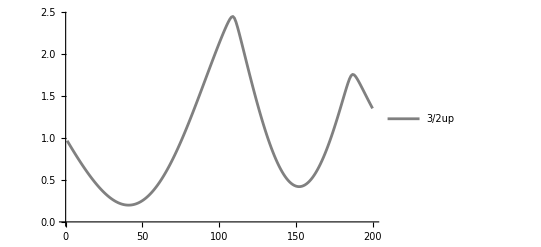

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.969064,0.938427,0.908095,0.878078,0.848389,0.819042,0.790052,0.761439,0.733223,0.705425,0.678068,0.651177,0.624778,0.598898,0.573564,0.548806,0.524653,0.501135,0.478283,0.456128,0.4347,0.414032,0.394155,0.3751,0.356899,0.339583,0.323181,0.307726,0.293245,0.279769,0.267326,0.255944,0.245649,0.236467,0.228423,0.221542,0.215845,0.211355,0.208092,0.206074,0.20532,0.205845,0.207664,0.210791,0.215238,0.221014,0.228128,0.236586,0.246395,0.257558,0.270075,0.283948,0.299174,0.31575,0.333671,0.352929,0.373515,0.395419,0.418627,0.443126,0.468899,0.495929,0.524195,0.553676,0.584348,0.616187,0.649165,0.683255,0.718427,0.754648,0.791885,0.830104,0.869269,0.909341,0.950282,0.992051,1.03461,1.0779,1.1219,1.16655,1.2118,1.25762,1.30394,1.35072,1.39792,1.44547,1.49332,1.54142,1.58972,1.63816,1.68669,1.73524,1.78376,1.83219,1.88046,1.92852,1.97629,2.0237,2.07068,2.11714,2.16298,2.20807,2.25225,2.29529,2.33681,2.37616,2.41203,2.44145,2.45735,2.44733,2.40744,2.34941,2.28329,2.2136,2.14228,2.07026,1.99809,1.92611,1.85456,1.78364,1.71351,1.64431,1.57617,1.50922,1.44356,1.37931,1.31657,1.25543,1.19599,1.13835,1.08258,1.02878,0.977012,0.927367,0.879913,0.83472,0.791854,0.751374,0.713341,0.677807,0.644823,0.614434,0.586682,0.561606,0.539239,0.51961,0.502744,0.488662,0.477381,0.468913,0.463265,0.460442,0.460441,0.463259,0.468885,0.477305,0.488501,0.502451,0.519128,0.5385,0.560532,0.585185,0.612414,0.642173,0.674409,0.709067,0.746085,0.785401,0.826944,0.870644,0.916422,0.964196,1.01388,1.06538,1.1186,1.17342,1.22973,1.28739,1.34624,1.40608,1.46664,1.52755,1.58818,1.6474,1.70289,1.7495,1.7775,1.77946,1.76146,1.73339,1.70073,1.66592,1.6301,1.59386,1.55753,1.52135,1.48545,1.44994,1.4149,1.3804}

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.968789,0.93788,0.907281,0.877,0.847052,0.817449,0.78821,0.759353,0.730898,0.702867,0.675283,0.648172,0.62156,0.595473,0.569941,0.544992,0.520656,0.496963,0.473944,0.451631,0.430055,0.409248,0.389241,0.370066,0.351756,0.33434,0.317851,0.302318,0.287771,0.274241,0.261755,0.250341,0.240027,0.230839,0.222801,0.215938,0.210273,0.205827,0.202621,0.200673,0.200003,0.200624,0.202554,0.205804,0.210388,0.216314,0.223591,0.232226,0.242224,0.253589,0.266322,0.280423,0.29589,0.312718,0.330904,0.350439,0.371313,0.393517,0.417036,0.441856,0.46796,0.495331,0.523948,0.553788,0.584828,0.617043,0.650405,0.684886,0.720454,0.757078,0.794723,0.833355,0.872936,0.913429,0.954792,0.996985,1.03997,1.08369,1.12811,1.17319,1.21886,1.2651,1.31184,1.35903,1.40663,1.45458,1.50282,1.55131,1.59998,1.64878,1.69766,1.74654,1.79538,1.8441,1.89265,1.94095,1.98894,2.03654,2.08366,2.1302,2.17605,2.22106,2.26502,2.30763,2.3484,2.38643,2.41989,2.44473,2.45238,2.43234,2.38626,2.32551,2.25791,2.1871,2.11475,2.04173,1.96856,1.89557,1.82301,1.75109,1.67997,1.6098,1.54072,1.47284,1.40629,1.34118,1.27762,1.2157,1.15552,1.09719,1.04078,0.986387,0.934093,0.883976,0.836111,0.79057,0.74742,0.706727,0.668549,0.632943,0.59996,0.569648,0.542051,0.517207,0.495152,0.475917,0.459527,0.446004,0.435365,0.427624,0.422787,0.42086,0.42184,0.425724,0.4325,0.442154,0.454667,0.470016,0.488173,0.509105,0.532774,0.55914,0.588157,0.619774,0.653936,0.690583,0.729653,0.771076,0.814778,0.860682,0.908702,0.958748,1.01072,1.06452,1.12003,1.17711,1.23562,1.29539,1.35618,1.41772,1.4796,1.5412,1.60146,1.65847,1.70853,1.74506,1.76069,1.7549,1.73462,1.70647,1.67424,1.63987,1.6044,1.5684,1.53222,1.49611,1.46023,1.42469,1.3896,1.35501}

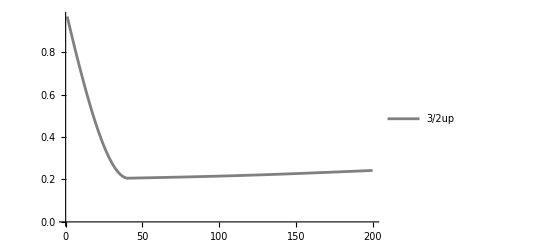

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.969064,0.938427,0.908095,0.878078,0.848389,0.819042,0.790052,0.761439,0.733223,0.705425,0.678068,0.651177,0.624778,0.598898,0.573564,0.548806,0.524653,0.501135,0.478283,0.456128,0.4347,0.414032,0.394155,0.3751,0.356899,0.339583,0.323181,0.307726,0.293245,0.279769,0.267326,0.255944,0.245649,0.236467,0.228423,0.221542,0.215845,0.211355,0.208092,0.206074,0.206221,0.206369,0.206516,0.206663,0.206811,0.206958,0.207106,0.207254,0.207402,0.207551,0.2077,0.207849,0.207998,0.208148,0.208299,0.20845,0.208601,0.208753,0.208905,0.209058,0.209212,0.209366,0.209521,0.209677,0.209833,0.20999,0.210148,0.210307,0.210467,0.210627,0.210789,0.210951,0.211115,0.211279,0.211444,0.211611,0.211778,0.211947,0.212117,0.212288,0.21246,0.212633,0.212807,0.212983,0.21316,0.213338,0.213517,0.213698,0.21388,0.214064,0.214248,0.214434,0.214622,0.214811,0.215002,0.215193,0.215387,0.215582,0.215778,0.215976,0.216175,0.216376,0.216578,0.216782,0.216988,0.217195,0.217403,0.217614,0.217826,0.218039,0.218254,0.218471,0.218689,0.218909,0.21913,0.219353,0.219578,0.219804,0.220032,0.220262,0.220493,0.220725,0.22096,0.221196,0.221433,0.221673,0.221913,0.222156,0.2224,0.222645,0.222892,0.223141,0.223391,0.223643,0.223896,0.224151,0.224408,0.224665,0.224925,0.225185,0.225448,0.225711,0.225977,0.226243,0.226511,0.22678,0.227051,0.227323,0.227596,0.227871,0.228147,0.228424,0.228702,0.228982,0.229263,0.229545,0.229828,0.230112,0.230398,0.230684,0.230972,0.23126,0.23155,0.23184,0.232132,0.232424,0.232718,0.233012,0.233307,0.233603,0.233899,0.234197,0.234495,0.234794,0.235093,0.235394,0.235694,0.235996,0.236298,0.2366,0.236903,0.237207,0.23751,0.237815,0.238119,0.238424,0.238729,0.239035,0.239341,0.239647,0.239953,0.240259,0.240565,0.240872,0.241178,0.241485,0.241791,0.242098,0.242404,0.24271}

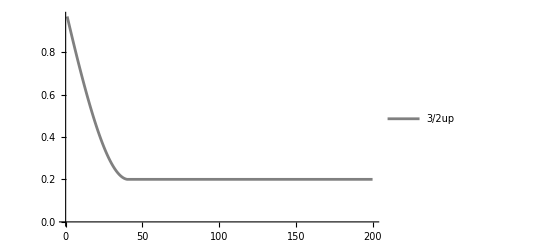

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.968789,0.93788,0.907281,0.877,0.847052,0.817449,0.78821,0.759353,0.730898,0.702867,0.675283,0.648172,0.62156,0.595473,0.569941,0.544992,0.520656,0.496963,0.473944,0.451631,0.430055,0.409248,0.389241,0.370066,0.351756,0.33434,0.317851,0.302318,0.287771,0.274241,0.261755,0.250341,0.240027,0.230839,0.222801,0.215938,0.210273,0.205827,0.202621,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673}

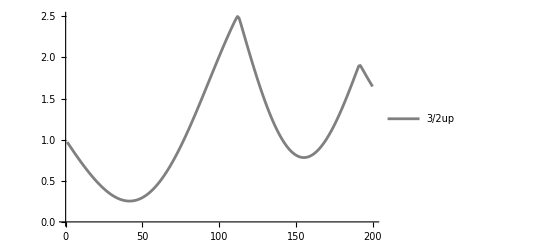

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

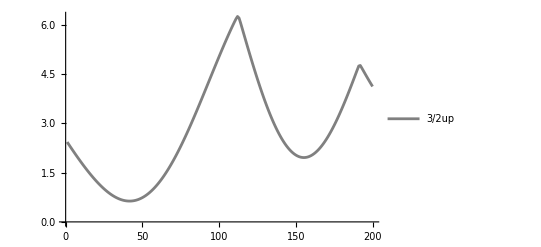

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

```mathematica
AA={2.4287192832945568,2.3581008749698764,2.2881565208455106,2.2189044486696132,2.1503689685480976,2.082580073696849,2.0155730445395568,1.9493880584698569,1.8840698070105006,1.8196671216210984,1.7562326090162166,1.6938222965444023,1.6324952879342922,1.572313429525314,1.5133409869583099,1.455644332197005,1.3992916406778202,1.3443525983364497,1.2908981182303505,1.239000066461855,1.1887309971041526,1.140163895838374,1.093371932022574,1.0484282189303529,1.005405581916821,0.964376334291317,0.9254120606988856,0.8885834078352559,0.853959882342294,0.8216096557524861,0.7915993763713298,0.7639939880056059,0.7388565554632023,0.7162480967661904,0.6962274220335374,0.6788509790028026,0.6641727051716955,0.6522438865503566,0.6431130230238034,0.636825700331177,0.640382404544062,0.6439345186207062,0.6474828675578723,0.6510282764590389,0.6545715701933017,0.6581135730499184,0.6616551083885862,0.6651969982856727,0.668740063176573,0.6722851214943772,0.6758329893050816,0.679384479939539,0.6829404036223603,0.686501567098043,0.6900687732545188,0.6936428207444094,0.6972245036042475,0.7008146108718916,0.7044139262024736,0.70802322748311,0.7116432864467082,0.7152748682851375,0.7189187312620824,0.7225756263259133,0.726246296722842,0.7299314776107475,0.7336318956739514,0.7373482687393209,0.7410813053940037,0.7448317046051627,0.7486001553420492,0.7523873362007674,0.7561939150320875,0.7600205485726561,0.7638678820799689,0.7677365489714649,0.7716271704680939,0.775540355242724,0.7794766990737592,0.7834367845042962,0.7874211805072027,0.7914304421564755,0.7954651103051988,0.7995257112704892,0.8036127565257543,0.8077267424005927,0.8118681497887055,0.8160374438641158,0.8202350738060447,0.824461472532735,0.8287170564445612,0.8330022251767097,0.8373173613617322,0.8416628304022469,0.8460389802540664,0.8504461412200346,0.8548846257548108,0.8593547282808234,0.863856725015697,0.8683908738112809,0.8729574140045773,0.8775565662806941,0.8821885325480441,0.8868534958259535,0.8915516201448415,0.896283050459084,0.9010479125727326,0.9058463130781638,0.9106783393077817,0.9155440592988411,0.9204435217714737,0.9253767561199497,0.9303437724172321,0.9353445614328302,0.9403790946639656,0.9454473243800368,0.9505491836803461,0.9556845865650776,0.9608534280194148,0.9660555841107845,0.971290912099088,0.9765592505598457,0.9818604195201068,0.9871942206070305,0.9925604372089256,0.9979588346486481,1.003389160369125,1.0088511441308574,1.014344498221131,1.019868917674783,1.025424080506237,1.0310096479525925,1.036625264727478,1.0422705592854205,1.0479451440964493,1.0536486159305953,1.0593805561520666,1.0651405310226814,1.0709280920143027,1.0767427761299535,1.0825841062331913,1.0884515913854687,1.0943447271911055,1.1002629961494632,1.1062058680140283,1.1121728001579516,1.118163237945736,1.1241766151106165,1.1302123541372961,1.1362698666496485,1.142348553802941,1.1484478066802328,1.1545670066925542,1.1607055259824133,1.1668627278303014,1.1730379670637636,1.179230590468633,1.1854399372020645,1.1916653392069403,1.1979061216272937,1.204161603224338,1.21043109679275,1.2167139095767734,1.223009343685856,1.2293166965093696,1.2356352611301014,1.2419643267361615,1.2483031790309362,1.2546511006407557,1.261007371519959,1.2673712693530081,1.2737420699533524,1.280119047658728,1.28650147572259,1.2928886267014024,1.2992797728375054,1.305674186437248,1.3120711402441922,1.318469907807108,1.3248697638424995,1.3312699845914726,1.337669848170704,1.3440686349173077,1.350465627727409,1.3568601123882464,1.3632513779036155,1.3696387168124935,1.3760214255007162,1.3823988045055535,1.3887701588130286,1.3951347981479354,1.4014920372563768,1.4078411961807569,1.414181600527166,1.420512581725109,1.426833477279307,1.4331436310139694,1.4394423933089535,1.4457291213282195,1.4520031792403154};
```

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

```mathematica
BB={2.4287192832945568,2.3581008749698764,2.2881565208455106,2.2189044486696132,2.1503689685480976,2.082580073696849,2.0155730445395568,1.9493880584698569,1.8840698070105006,1.8196671216210984,1.7562326090162166,1.6938222965444023,1.6324952879342922,1.572313429525314,1.5133409869583099,1.455644332197005,1.3992916406778202,1.3443525983364497,1.2908981182303505,1.239000066461855,1.1887309971041526,1.140163895838374,1.093371932022574,1.0484282189303529,1.005405581916821,0.964376334291317,0.9254120606988856,0.8885834078352559,0.853959882342294,0.8216096557524861,0.7915993763713298,0.7639939880056059,0.7388565554632023,0.7162480967661904,0.6962274220335374,0.6788509790028026,0.6641727051716955,0.6522438865503566,0.6431130230238034,0.636825700331177,0.6334244686742978,0.6329487279726664,0.6354346197855536,0.6409149259241174,0.6494189737779488,0.660972548380709,0.6755978112391459,0.6933132259483052,0.7141334906138654,0.7380694770995087,0.7651281771139766,0.795312655148364,0.8286220082696163,0.8650513327711389,0.9045916976759374,0.9472301250817292,0.9929495773312293,1.0417289509841554,1.093543077560561,1.1483627310180307,1.2061546419177143,1.2668815182266844,1.330502072696314,1.3969710567482965,1.4662393007920809,1.5382537608890647,1.6129575716708233,1.6902901054100727,1.770187037134737,1.8525804156668313,1.9373987404592814,2.0245670440949155,2.1140069803030785,2.2056369173400387,2.299372036570074,2.3951244360743402,2.4928032391044406,2.592314707186685,2.693562357671369,2.7964470855083556,2.900867289015674,3.006718999391043,3.113896013696168,3.2222900310195985,3.331790791493799,3.442286217803831,3.5536625587752386,3.665804534562629,3.778595482870771,3.891917505516456,4.005651614465715,4.119677876232679,4.233875553164934,4.348123239604197,4.462298990100252,4.5762804356034135,4.689944881580276,4.803169378786143,4.9158307520715345,5.027805563379966,5.138969968643915,5.2491993977074625,5.3583679268056645,5.46634709033735,5.573003608391755,5.678194861991566,5.781759250548555,5.88349348862491,5.983090897404586,6.079933457034303,6.1720933278698835,6.246887330671213,6.199099298884955,6.050356465329387,5.890838984208667,5.729825047466961,5.569023533701191,5.4090964435896165,5.25043809636735,5.09334771434622,4.938082400548058,4.784876999047431,4.633952590012424,4.4855204552402945,4.339784027754484,4.1969398651617595,4.057178118277411,3.920682725334875,3.78763145141625,3.6581958385663893,3.5325411040542347,3.410826009083515,3.293202711705074,3.179816612686393,3.0708062000791045,2.9663028963527522,2.866430910768722,2.771307098887021,2.681040830575148,2.595733867529265,2.515480251065588,2.4403662007583704,2.370470024366902,2.3058620393923666,2.246604506526483,2.192751575190619,2.1443492413121676,2.101435317441084,2.0640394152715777,2.0321829406003435,2.0058791007223755,1.9851329242375244,1.9699412932149025,1.9602929876377502,1.9561687420277947,1.9575413141256495,1.964375565481769,1.976628553791016,1.994249636782711,2.0171805874569024,2.045355720436391,2.0787020291824074,2.117139333799434,2.1605804391310572,2.208931302823095,2.2620912130017024,2.3199529751813146,2.3824031079777823,2.4493220471532546,2.520584357455883,2.59605895163262,2.6756093158754344,2.759093740792159,2.8463655567433026,2.937273372006131,3.031661311632754,3.1293692539113227,3.230233059749473,3.3340847875702053,3.440752881451494,3.5500623112233747,3.661834625682815,3.7758878439602044,3.8920360306286472,4.010088210842057,4.1298457833186,4.251096096833461,4.373594548863538,4.497003369532637,4.6205900296838465,4.739814251489037,4.757303104596868,4.678887342353419,4.596575209508372,4.514391926679284,4.432942114161442,4.352456567183306,4.273078665433483,4.194903870055487,4.118035183941553};
```

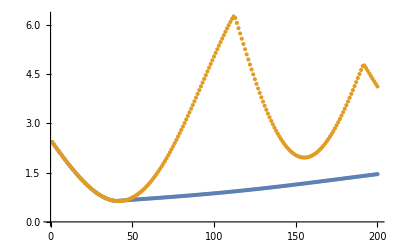

```mathematica
ListPlot[{AA,BB}]
```

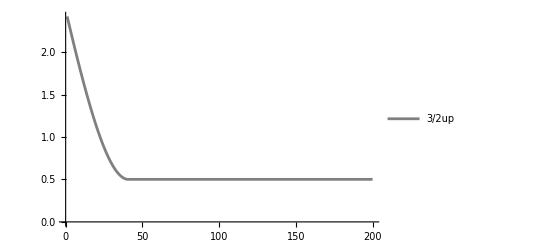

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

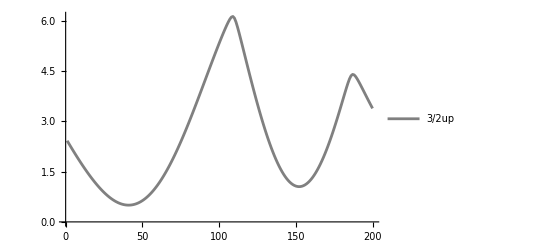

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
|
```

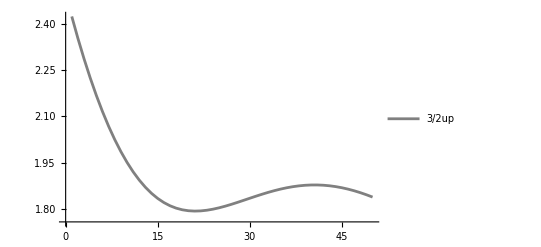

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
N[Pi/2*13/50]
```

0.408407

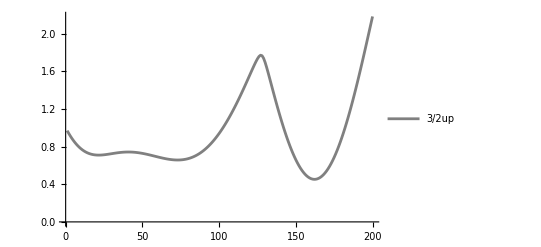

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

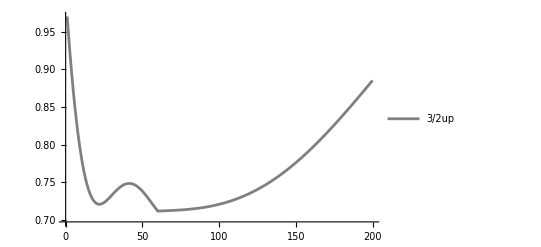

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

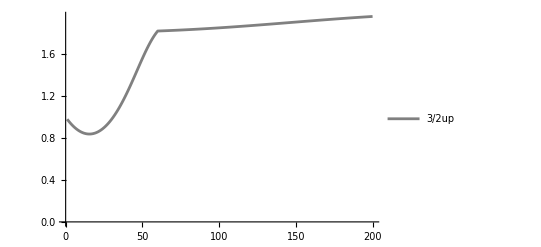

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]3
```

```mathematica
SqueezeListBox[[1,1]]/(5/2)
```

{0.976014+6.6408×10^-17 ⅈ,0.953378+5.74927×10^-17 ⅈ,0.932106+7.67646×10^-17 ⅈ,0.912216+6.04711×10^-17 ⅈ,0.89372+9.26067×10^-18 ⅈ,0.876633+6.46977×10^-17 ⅈ,0.860965+1.4481×10^-16 ⅈ,0.846728+1.12318×10^-16 ⅈ,0.833932+2.81371×10^-16 ⅈ,0.822586+1.67019×10^-16 ⅈ,0.812698+1.87067×10^-16 ⅈ,0.804276+2.74108×10^-16 ⅈ,0.797328+2.74898×10^-16 ⅈ,0.791859+3.24054×10^-16 ⅈ,0.787875+3.93217×10^-16 ⅈ,0.785383+4.58838×10^-16 ⅈ,0.784387+4.90523×10^-16 ⅈ,0.784892+5.73411×10^-16 ⅈ,0.786903+6.14428×10^-16 ⅈ,0.790422+6.04623×10^-16 ⅈ,0.795455+7.41013×10^-16 ⅈ,0.802003+6.26854×10^-16 ⅈ,0.810068+7.45452×10^-16 ⅈ,0.819653+8.32548×10^-16 ⅈ,0.830757+9.62432×10^-16 ⅈ,0.843381+9.59856×10^-16 ⅈ,0.857522+1.21177×10^-15 ⅈ,0.873176+1.30123×10^-15 ⅈ,0.890337+1.3707×10^-15 ⅈ,0.908998+1.57812×10^-15 ⅈ,0.929147+1.67422×10^-15 ⅈ,0.950769+1.65172×10^-15 ⅈ,0.973846+1.64764×10^-15 ⅈ,0.998354+1.57643×10^-15 ⅈ,1.02426+1.75542×10^-15 ⅈ,1.05154+1.79767×10^-15 ⅈ,1.08013+2.02692×10^-15 ⅈ,1.11+1.82424×10^-15 ⅈ,1.14107+2.17884×10^-15 ⅈ,1.17329+2.04641×10^-15 ⅈ,1.20655+2.03465×10^-15 ⅈ,1.24078+2.14318×10^-15 ⅈ,1.27585+2.04486×10^-15 ⅈ,1.31164+2.06529×10^-15 ⅈ,1.34801+2.08692×10^-15 ⅈ,1.38481+2.1305×10^-15 ⅈ,1.42187+2.02553×10^-15 ⅈ,1.45899+1.83634×10^-15 ⅈ,1.49598+1.77207×10^-15 ⅈ,1.53262+1.39914×10^-15 ⅈ,1.5687+1.12957×10^-15 ⅈ,1.60398+1.25386×10^-15 ⅈ,1.63822+8.47125×10^-16 ⅈ,1.67121+5.87678×10^-16 ⅈ,1.70272+2.41706×10^-16 ⅈ,1.73255+4.1279×10^-17 ⅈ,1.76051-3.23895×10^-16 ⅈ,1.78643-6.96384×10^-16 ⅈ,1.81019-8.85433×10^-16 ⅈ,1.83167-1.32049×10^-15 ⅈ,1.83167-1.28116×10^-15 ⅈ,1.83167-1.3017×10^-15 ⅈ,1.83167-1.18585×10^-15 ⅈ,1.83167-1.17436×10^-15 ⅈ,1.83167-1.22287×10^-15 ⅈ,1.83167-1.27653×10^-15 ⅈ,1.83167-1.19273×10^-15 ⅈ,1.83167-1.16959×10^-15 ⅈ,1.83167-1.00612×10^-15 ⅈ,1.83167-9.30148×10^-16 ⅈ,1.83167-1.18781×10^-15 ⅈ,1.83167-1.10111×10^-15 ⅈ,1.83167-1.0192×10^-15 ⅈ,1.83167-1.23568×10^-15 ⅈ,1.83167-1.26892×10^-15 ⅈ,1.83167-1.03131×10^-15 ⅈ,1.83167-9.50258×10^-16 ⅈ,1.83167-1.01591×10^-15 ⅈ,1.83167-1.15969×10^-15 ⅈ,1.83167-1.26636×10^-15 ⅈ,1.83167-1.41372×10^-15 ⅈ,1.83167-1.14622×10^-15 ⅈ,1.83167-1.39899×10^-15 ⅈ,1.83167-1.57753×10^-15 ⅈ,1.83167-1.53634×10^-15 ⅈ,1.83167-1.60315×10^-15 ⅈ,1.83167-1.6392×10^-15 ⅈ,1.83167-1.9774×10^-15 ⅈ,1.83167-1.97691×10^-15 ⅈ,1.83167-1.79393×10^-15 ⅈ,1.83167-1.88054×10^-15 ⅈ,1.83167-2.20952×10^-15 ⅈ,1.83167-2.031×10^-15 ⅈ,1.83167-2.00824×10^-15 ⅈ,1.83167-2.13016×10^-15 ⅈ,1.83167-2.21925×10^-15 ⅈ,1.83167-2.35642×10^-15 ⅈ,1.83167-2.61372×10^-15 ⅈ,1.83167-2.69159×10^-15 ⅈ,1.83167-2.64962×10^-15 ⅈ,1.83167-2.423×10^-15 ⅈ,1.83167-2.54177×10^-15 ⅈ,1.83167-2.60698×10^-15 ⅈ,1.83167-2.76218×10^-15 ⅈ,1.83167-2.77992×10^-15 ⅈ,1.83167-2.94337×10^-15 ⅈ,1.83167-3.06464×10^-15 ⅈ,1.83167-3.03636×10^-15 ⅈ,1.83167-3.15584×10^-15 ⅈ,1.83167-3.31574×10^-15 ⅈ,1.83167-3.6617×10^-15 ⅈ,1.83167-3.57923×10^-15 ⅈ,1.83167-3.75698×10^-15 ⅈ,1.83167-4.00977×10^-15 ⅈ,1.83167-4.03563×10^-15 ⅈ,1.83167-4.53874×10^-15 ⅈ,1.83167-4.4935×10^-15 ⅈ,1.83167-4.68806×10^-15 ⅈ,1.83167-4.90298×10^-15 ⅈ,1.83167-5.1006×10^-15 ⅈ,1.83167-5.03143×10^-15 ⅈ,1.83167-5.10102×10^-15 ⅈ,1.83167-5.28939×10^-15 ⅈ,1.83167-5.27306×10^-15 ⅈ,1.83167-5.37143×10^-15 ⅈ,1.83167-5.42726×10^-15 ⅈ,1.83167-5.61434×10^-15 ⅈ,1.83167-5.798×10^-15 ⅈ,1.83167-6.24527×10^-15 ⅈ,1.83167-6.27067×10^-15 ⅈ,1.83167-6.22421×10^-15 ⅈ,1.83167-6.51098×10^-15 ⅈ,1.83167-6.55191×10^-15 ⅈ,1.83167-6.65774×10^-15 ⅈ,1.83167-6.9997×10^-15 ⅈ,1.83167-6.97755×10^-15 ⅈ,1.83167-7.21093×10^-15 ⅈ,1.83167-7.76268×10^-15 ⅈ,1.83167-7.3907×10^-15 ⅈ,1.83167-7.93361×10^-15 ⅈ,1.83167-8.05509×10^-15 ⅈ,1.83167-8.11722×10^-15 ⅈ,1.83167-8.19745×10^-15 ⅈ,1.83167-8.47406×10^-15 ⅈ,1.83167-8.45528×10^-15 ⅈ,1.83167-8.86478×10^-15 ⅈ,1.83167-8.96222×10^-15 ⅈ,1.83167-8.93941×10^-15 ⅈ,1.83167-8.82417×10^-15 ⅈ,1.83167-8.93676×10^-15 ⅈ,1.83167-9.1069×10^-15 ⅈ,1.83167-9.40445×10^-15 ⅈ,1.83167-9.76712×10^-15 ⅈ,1.83167-9.50348×10^-15 ⅈ,1.83167-9.78269×10^-15 ⅈ,1.83167-9.87656×10^-15 ⅈ,1.83167-1.00179×10^-14 ⅈ,1.83167-9.94995×10^-15 ⅈ,1.83167-9.99003×10^-15 ⅈ,1.83167-1.00684×10^-14 ⅈ,1.83167-1.04733×10^-14 ⅈ,1.83167-1.04396×10^-14 ⅈ,1.83167-1.03055×10^-14 ⅈ,1.83167-1.04758×10^-14 ⅈ,1.83167-1.06441×10^-14 ⅈ,1.83167-1.08323×10^-14 ⅈ,1.83167-1.10282×10^-14 ⅈ,1.83167-1.09485×10^-14 ⅈ,1.83167-1.09446×10^-14 ⅈ,1.83167-1.09556×10^-14 ⅈ,1.83167-1.1081×10^-14 ⅈ,1.83167-1.12445×10^-14 ⅈ,1.83167-1.13592×10^-14 ⅈ,1.83167-1.12584×10^-14 ⅈ,1.83167-1.1277×10^-14 ⅈ,1.83167-1.12831×10^-14 ⅈ,1.83167-1.13032×10^-14 ⅈ,1.83167-1.12249×10^-14 ⅈ,1.83167-1.1428×10^-14 ⅈ,1.83167-1.12341×10^-14 ⅈ,1.83167-1.12063×10^-14 ⅈ,1.83167-1.11228×10^-14 ⅈ,1.83167-1.1247×10^-14 ⅈ,1.83167-1.13297×10^-14 ⅈ,1.83167-1.12951×10^-14 ⅈ,1.83167-1.13955×10^-14 ⅈ,1.83167-1.12266×10^-14 ⅈ,1.83167-1.11213×10^-14 ⅈ,1.83167-1.13533×10^-14 ⅈ,1.83167-1.11414×10^-14 ⅈ,1.83167-1.11042×10^-14 ⅈ,1.83167-1.11202×10^-14 ⅈ,1.83167-1.11559×10^-14 ⅈ,1.83167-1.10388×10^-14 ⅈ,1.83167-1.09195×10^-14 ⅈ,1.83167-1.09737×10^-14 ⅈ,1.83167-1.09048×10^-14 ⅈ,1.83167-1.07782×10^-14 ⅈ,1.83167-1.11436×10^-14 ⅈ,1.83167-1.10965×10^-14 ⅈ}

```mathematica
SqueezeListBox[[1,1]]/(5/2)
```

{0.978348+0.00370753 ⅈ,0.957928+0.00757618 ⅈ,0.938764+0.0116115 ⅈ,0.920887+0.0158203 ⅈ,0.904326+0.0202105 ⅈ,0.889116+0.0247914 ⅈ,0.875296+0.0295733 ⅈ,0.862904+0.0345679 ⅈ,0.851983+0.039788 ⅈ,0.842576+0.0452477 ⅈ,0.834731+0.0509625 ⅈ,0.828495+0.0569487 ⅈ,0.823916+0.0632243 ⅈ,0.821044+0.0698079 ⅈ,0.819929+0.0767198 ⅈ,0.820621+0.0839809 ⅈ,0.823169+0.0916133 ⅈ,0.827623+0.0996401 ⅈ,0.834028+0.108085 ⅈ,0.84243+0.116972 ⅈ,0.852869+0.126327 ⅈ,0.865384+0.136174 ⅈ,0.880008+0.146539 ⅈ,0.896767+0.157447 ⅈ,0.915684+0.16892 ⅈ,0.936772+0.180984 ⅈ,0.960034+0.193659 ⅈ,0.985464+0.206964 ⅈ,1.01305+0.220916 ⅈ,1.04275+0.235528 ⅈ,1.07452+0.250808 ⅈ,1.10831+0.266759 ⅈ,1.14404+0.283376 ⅈ,1.1816+0.300647 ⅈ,1.22088+0.318547 ⅈ,1.26173+0.337042 ⅈ,1.30401+0.356081 ⅈ,1.34753+0.375598 ⅈ,1.3921+0.395508 ⅈ,1.43749+0.41571 ⅈ,1.48348+0.43608 ⅈ,1.52983+0.456478 ⅈ,1.5763+0.476747 ⅈ,1.62263+0.496714 ⅈ,1.66858+0.516198 ⅈ,1.71389+0.535004 ⅈ,1.75832+0.552934 ⅈ,1.80162+0.569788 ⅈ,1.84357+0.58536 ⅈ,1.88393+0.59945 ⅈ,1.92252+0.611857 ⅈ,1.95913+0.622384 ⅈ,1.99359+0.63084 ⅈ,2.02575+0.637035 ⅈ,2.05549+0.640787 ⅈ,2.0827+0.641914 ⅈ,2.10724-0.242782 ⅈ,2.11468-0.233234 ⅈ,2.12161-0.221635 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.07326-0.805222 ⅈ}

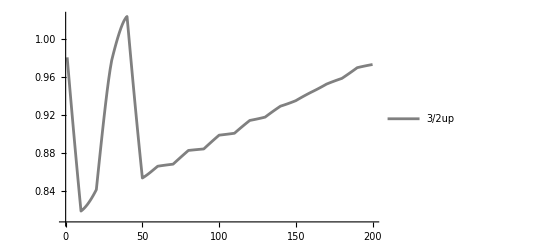

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

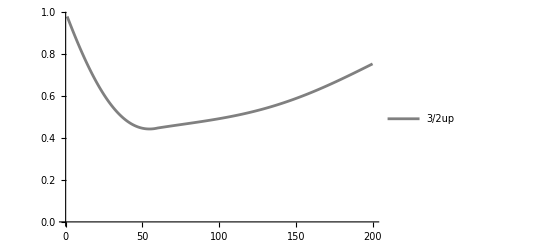

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[ξtopF[MatrixExp[-I*Ix3half2*Pi/2].DMevolve[[1,1]].MatrixExp[+I*Ix3half2*Pi/2]]]
```

Flatten::normal: Flatten[0.332823+1.38778×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.726683-6.43068×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.597188+5.53063×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.672397

```mathematica
DMevolve[[1,1]]
```

{{0.0549372-1.10954×10^-16 ⅈ,-0.0789447-0.0259826 ⅈ,-0.0628249+0.135289 ⅈ,-0.0162147+0.0431125 ⅈ},{-0.0789447+0.0259826 ⅈ,0.173517-9.37621×10^-16 ⅈ,0.102717-0.262559 ⅈ,0.0381837-0.103942 ⅈ},{-0.0628249-0.135289 ⅈ,0.102717+0.262559 ⅈ,0.655331+2.30254×10^-15 ⅈ,0.242912-0.0552429 ⅈ},{-0.0162147-0.0431125 ⅈ,0.0381837+0.103942 ⅈ,0.242912+0.0552429 ⅈ,0.116214-1.21011×10^-15 ⅈ}}

```mathematica
MatrixExp[-I*Ix3half2*Pi/2].DMevolve[[1,1]].MatrixExp[+I*Ix3half2*Pi/2]
```

{{0.585751+1.51268×10^-15 ⅈ,0.076817-0.106961 ⅈ,0.210952-0.280544 ⅈ,0.00198419-0.216759 ⅈ},{0.076817+0.106961 ⅈ,0.0943153+2.46331×10^-16 ⅈ,0.0845181-0.00649014 ⅈ,0.0615183-0.041313 ⅈ},{0.210952+0.280544 ⅈ,0.0845181+0.00649014 ⅈ,0.21992-1.7486×10^-15 ⅈ,0.108164-0.0777004 ⅈ},{0.00198419+0.216759 ⅈ,0.0615183+0.041313 ⅈ,0.108164+0.0777004 ⅈ,0.100013+2.08167×10^-17 ⅈ}}

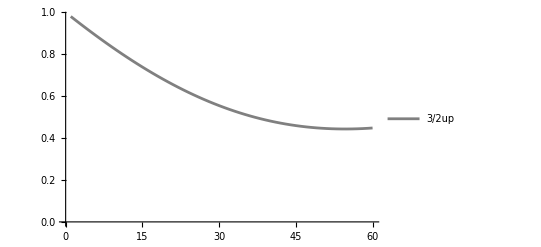

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

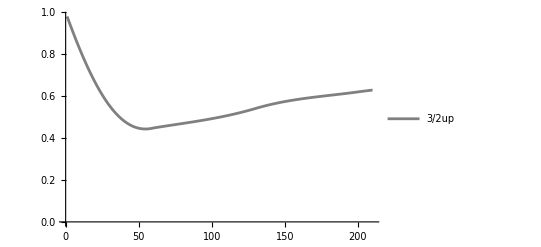

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

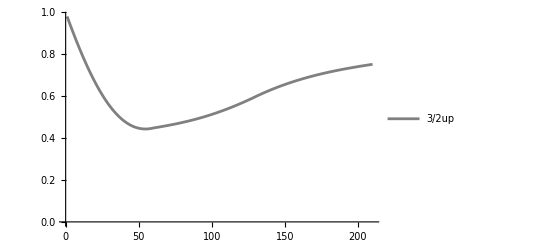

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

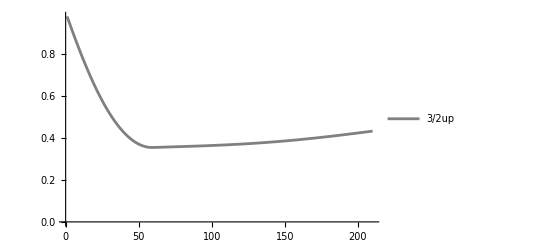

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980159,0.960493,0.941014,0.921732,0.902659,0.883805,0.865179,0.846792,0.828652,0.810769,0.793152,0.775808,0.758746,0.741974,0.7255,0.709329,0.69347,0.677928,0.66271,0.647821,0.633268,0.619055,0.605188,0.59167,0.578506,0.565701,0.553257,0.541177,0.529466,0.518126,0.507158,0.496566,0.486351,0.476515,0.467058,0.457983,0.44929,0.44098,0.433053,0.425509,0.418349,0.411573,0.405181,0.399172,0.393546,0.388304,0.383444,0.378967,0.374873,0.371161,0.367831,0.364883,0.362318,0.360136,0.358338,0.356923,0.355894,0.355251,0.354995,0.355127,0.355349,0.355569,0.355788,0.356006,0.356224,0.35644,0.356657,0.356873,0.357089,0.357305,0.357521,0.357737,0.357954,0.358171,0.35839,0.358609,0.358829,0.35905,0.359273,0.359497,0.359723,0.35995,0.36018,0.360411,0.360645,0.360881,0.36112,0.361361,0.361605,0.361852,0.362102,0.362356,0.362612,0.362872,0.363136,0.363403,0.363674,0.36395,0.364229,0.364512,0.3648,0.365092,0.365389,0.365691,0.365997,0.366309,0.366625,0.366946,0.367273,0.367605,0.367943,0.368286,0.368634,0.368989,0.369349,0.369715,0.370088,0.370466,0.37085,0.371241,0.371638,0.372042,0.372451,0.372868,0.373291,0.373721,0.374157,0.3746,0.37505,0.375507,0.375971,0.376442,0.37692,0.377405,0.377897,0.378396,0.378902,0.379415,0.379936,0.380464,0.380999,0.381541,0.382091,0.382648,0.383212,0.383783,0.384362,0.384948,0.385541,0.386141,0.386749,0.387364,0.387985,0.388615,0.389251,0.389894,0.390545,0.391202,0.391866,0.392538,0.393216,0.393901,0.394593,0.395291,0.395997,0.396708,0.397427,0.398152,0.398883,0.39962,0.400364,0.401114,0.40187,0.402633,0.403401,0.404175,0.404954,0.405739,0.40653,0.407327,0.408128,0.408935,0.409747,0.410564,0.411386,0.412213,0.413045,0.413881,0.414721,0.415566,0.416415,0.417269,0.418126,0.418987,0.419852,0.42072,0.421592,0.422467,0.423346,0.424227,0.425111,0.425999,0.426888,0.427781,0.428675,0.429572,0.430471,0.431372,0.432275,0.43318}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980744,0.961714,0.942919,0.924372,0.906081,0.888057,0.870309,0.852846,0.835678,0.818812,0.802256,0.78602,0.770109,0.754531,0.739293,0.724402,0.709863,0.695682,0.681865,0.668417,0.655343,0.642647,0.630332,0.618403,0.606864,0.595716,0.584963,0.574607,0.56465,0.555092,0.545937,0.537183,0.528832,0.520884,0.513338,0.506194,0.49945,0.493106,0.487159,0.481608,0.476449,0.471682,0.467301,0.463304,0.459688,0.456449,0.453583,0.451085,0.448952,0.447179,0.445761,0.444694,0.443973,0.443595,0.443554,0.443845,0.444466,0.445412,0.446679,0.448265,0.449416,0.450581,0.45176,0.452954,0.454164,0.455391,0.456636,0.4579,0.459184,0.460489,0.461816,0.463166,0.464539,0.465936,0.467359,0.468808,0.470283,0.471787,0.473318,0.474879,0.476469,0.47809,0.479742,0.481426,0.483142,0.484891,0.486673,0.48849,0.490341,0.492227,0.494148,0.496105,0.498098,0.500128,0.502194,0.504298,0.506439,0.508618,0.510835,0.513089,0.515382,0.517713,0.520083,0.522491,0.524937,0.527422,0.529945,0.532507,0.535106,0.537744,0.54042,0.543134,0.545886,0.548675,0.551501,0.554363,0.557263,0.560198,0.563169,0.566176,0.569218,0.572294,0.575404,0.578548,0.581725,0.584935,0.588177,0.59145,0.594753,0.598087,0.601412,0.604688,0.607915,0.611095,0.614227,0.617313,0.620353,0.623346,0.626295,0.629199,0.632058,0.634874,0.637647,0.640377,0.643065,0.645711,0.648316,0.650881,0.653406,0.655891,0.658337,0.660745,0.663115,0.665447,0.667743,0.670002,0.672225,0.674414,0.676567,0.678686,0.680772,0.682824,0.684844,0.686831,0.688787,0.690712,0.692606,0.69447,0.696305,0.698111,0.699888,0.701637,0.703359,0.705053,0.706722,0.708364,0.709981,0.711573,0.71314,0.714684,0.716204,0.717701,0.719176,0.720629,0.722061,0.723471,0.724861,0.726232,0.727583,0.728915,0.730228,0.731524,0.732802,0.734063,0.735308,0.736537,0.737751,0.73895,0.740134,0.741304,0.742461,0.743605,0.744736,0.745856,0.746964,0.748061,0.749148,0.750225,0.751292,0.75235}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980744,0.961714,0.942919,0.924372,0.906081,0.888057,0.870309,0.852846,0.835678,0.818812,0.802256,0.78602,0.770109,0.754531,0.739293,0.724402,0.709863,0.695682,0.681865,0.668417,0.655343,0.642647,0.630332,0.618403,0.606864,0.595716,0.584963,0.574607,0.56465,0.555092,0.545937,0.537183,0.528832,0.520884,0.513338,0.506194,0.49945,0.493106,0.487159,0.481608,0.476449,0.471682,0.467301,0.463304,0.459688,0.456449,0.453583,0.451085,0.448952,0.447179,0.445761,0.444694,0.443973,0.443595,0.443554,0.443845,0.444466,0.445412,0.446679,0.448265,0.449404,0.450532,0.45165,0.452758,0.453857,0.454948,0.456032,0.457109,0.45818,0.459246,0.460308,0.461367,0.462423,0.463477,0.46453,0.465583,0.466637,0.467692,0.468749,0.469808,0.470872,0.471939,0.473012,0.474091,0.475176,0.476269,0.47737,0.478479,0.479598,0.480728,0.481868,0.48302,0.484185,0.485363,0.486554,0.48776,0.488982,0.490219,0.491472,0.492743,0.494032,0.495339,0.496665,0.498011,0.499377,0.500764,0.502172,0.503603,0.505056,0.506532,0.508032,0.509556,0.511105,0.51268,0.51428,0.515906,0.517559,0.519239,0.520947,0.522682,0.524446,0.526239,0.52806,0.529911,0.531792,0.533704,0.535645,0.537617,0.53962,0.541655,0.543682,0.545663,0.547601,0.549494,0.551345,0.553153,0.55492,0.556646,0.558332,0.55998,0.561588,0.563159,0.564694,0.566193,0.567656,0.569085,0.570481,0.571844,0.573176,0.574477,0.575748,0.576989,0.578203,0.579389,0.580548,0.581682,0.582792,0.583877,0.58494,0.585981,0.587001,0.588001,0.588981,0.589944,0.590889,0.591818,0.592732,0.593631,0.594516,0.59539,0.596251,0.597102,0.597944,0.598777,0.599602,0.600421,0.601234,0.602042,0.602846,0.603648,0.604447,0.605246,0.606045,0.606845,0.607647,0.608452,0.609261,0.610075,0.610895,0.611722,0.612556,0.613399,0.614251,0.615114,0.615989,0.616875,0.617775,0.618689,0.619618,0.620562,0.621507,0.622437,0.623352,0.624254,0.625142,0.626018,0.626883,0.627737,0.628581,0.629415}

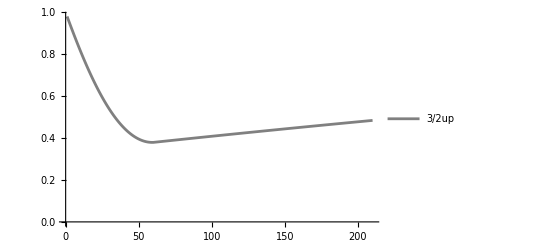

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

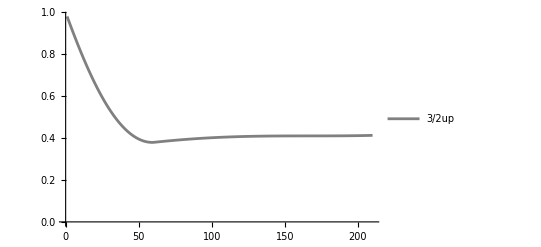

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

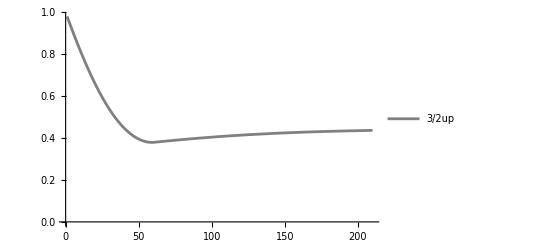

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

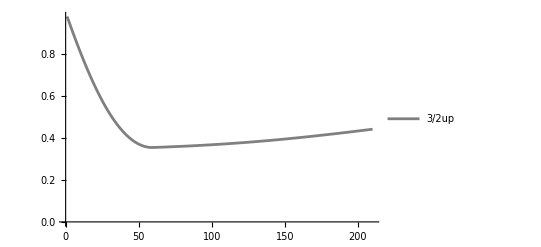

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

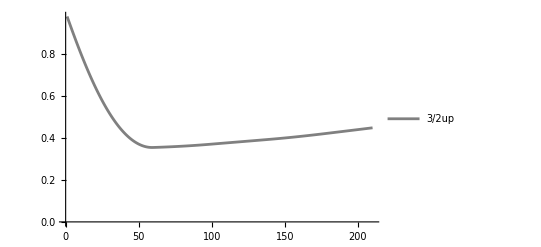

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox/1]
```

{{{1.48493,1.46974,1.45442,1.439,1.42347,1.40786,1.39216,1.3764,1.36058,1.34471,1.32881,1.3129,1.29698,1.28106,1.26517,1.24932,1.23352,1.2178,1.20215,1.18662,1.1712,1.15592,1.14079,1.12585,1.11109,1.09655,1.08224,1.06819,1.05441,1.04092,1.02774,1.0149,1.00242,0.990314,0.978606,0.967316,0.956467,0.946078,0.93617,0.926762,0.917876,0.909529,0.901742,0.894531,0.887914,0.881908,0.876528,0.871789,0.867705,0.864287,0.861546,0.859492,0.858133,0.857475,0.857521,0.858276,0.859738,0.861907,0.864779,0.868347,0.872604,0.877538,0.883136,0.889382,0.896257,0.90374,0.911808,0.920434,0.929588,0.93924,0.949353,0.959893,0.970819,0.98209,0.993662,1.00549,1.01753,1.02972,1.04203,1.05439,1.06676,1.07907,1.09129,1.10335,1.1152,1.12679,1.13807,1.14899,1.15949,1.16954,1.17908,1.18809,1.19651,1.20433,1.2115,1.218,1.22382,1.22894,1.23335,1.23705,1.24004,1.24235,1.24398,1.24497,1.24536,1.24518,1.24449,1.24335,1.24183,1.24,1.23794,1.23575,1.23351,1.23131,1.22925,1.22743,1.22594,1.22488,1.22433,1.22437,1.22508,1.22652,1.22877,1.23186,1.23584,1.24073,1.24657,1.25337,1.26112,1.26982,1.27946,1.29001,1.30145,1.31373,1.3268,1.34061,1.35508,1.37012,1.38561,1.40136,1.4171,1.43231,1.44593,1.45586,1.4588,1.45319,1.44149,1.42669,1.41044,1.39352,1.37632,1.35903,1.34177,1.3246,1.30758,1.29074,1.27409,1.25765,1.24145,1.22548,1.20977,1.19431,1.17912,1.16421,1.14957,1.13522,1.12115,1.10738,1.09391,1.08075,1.06789,1.05534,1.04311,1.03119,1.0196,1.00833,0.997381,0.986767,0.976484,0.966535,0.956922,0.947647,0.938712,0.930119,0.921869,0.913964,0.906405,0.899193,0.89233,0.885816,0.879654,0.873843,0.868385,0.863281,0.858531,0.854136,0.850098,0.846416,0.843092,0.840127,0.837521,0.835275,0.833389,0.831865,0.830704,0.829906,0.829473,0.829405,0.829704,0.83037,0.831405,0.83281,0.834587,0.836737,0.839261,0.842162,0.84544,0.849099,0.853139,0.857563,0.862373,0.867572,0.873161,0.879143,0.885521,0.892296,0.899473,0.907053,0.915039,0.923434,0.932241,0.941462,0.9511,0.961158,0.971638,0.982541,0.993871,1.00563,1.01781,1.03043,1.04347,1.05694,1.07084,1.08517,1.09991,1.11508,1.13065,1.14662,1.16298,1.17971,1.19681,1.21424,1.232,1.25004,1.26834,1.28686,1.30556,1.32438,1.34328,1.36218,1.38102,1.39972,1.41819,1.43634,1.45407,1.47128,1.48787,1.50373,1.51876,1.53286,1.54596,1.55797,1.56884,1.57853,1.58702,1.5943,1.60038,1.60529,1.60907,1.61178,1.61346,1.6142,1.61405,1.6131,1.61141,1.60906,1.60612,1.60266,1.59875,1.59444,1.58981,1.58491,1.5798,1.57453,1.56915,1.56372,1.55827,1.55286,1.54753,1.54231,1.53725,1.53239,1.52775,1.52337,1.51929,1.51552,1.51211,1.50908,1.50645,1.50424,1.50247,1.50116,1.50034,1.50001,1.50018,1.50087,1.50209,1.50384,1.50613,1.50896,1.51233,1.51624,1.52069,1.52567,1.53118,1.53722,1.54377,1.55082,1.55836,1.56637,1.57485,1.58378,1.59314,1.60291,1.61307,1.62361,1.6345,1.64572,1.65724,1.66905,1.68111,1.69339,1.70586,1.71849,1.73125,1.74408,1.75695,1.76979,1.78255,1.79514,1.80748,1.81944,1.83089,1.84164,1.85144,1.85998,1.86683,1.87146,1.8732,1.87129,1.86502,1.85388,1.83781,1.81722,1.79288,1.76567,1.73643,1.70584,1.67443,1.64261,1.61066,1.57881,1.5472,1.51595,1.48516,1.45489,1.42518,1.39608,1.3676,1.33978,1.31262,1.28614,1.26035,1.23526,1.21086,1.18716,1.16417,1.14188,1.12028,1.09939,1.0792,1.0597,1.0409,1.02279,1.00536,0.988612,0.972544,0.957148,0.942421,0.928355,0.914946,0.902187,0.890072,0.878593,0.867742,0.857513,0.847896,0.838883,0.830464,0.822628,0.815366,0.808666,0.802517,0.796905,0.791817,0.787241,0.78316,0.77956,0.776424,0.773736,0.771478,0.769632,0.768177,0.767095,0.766365,0.765964,0.765871,0.766063,0.766516,0.767206,0.768107,0.769196,0.770445,0.771829,0.773322,0.774896,0.776526,0.778185,0.779846,0.781483,0.783071,0.784585,0.786,0.787293,0.788442,0.789425,0.790222,0.790814,0.791185,0.791319,0.791201,0.790821,0.790167,0.789232,0.788008,0.786492,0.784682,0.782575,0.780175,0.777483,0.774506,0.771248,0.76772,0.76393,0.75989,0.755612,0.751109,0.746398,0.741493,0.736412,0.731171,0.72579,0.720286,0.714678,0.708987,0.703232,0.697432,0.691609,0.685781,0.67997,0.674195,0.668475,0.662831,0.657282,0.651847,0.646546,0.641396,0.636415,0.631623,0.627037,0.622673,0.618549,0.614682,0.611088,0.607782,0.604781,0.6021,0.599754,0.597758,0.596126}}}

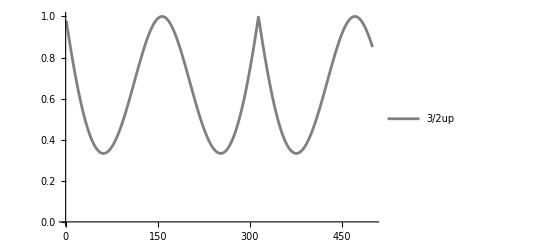

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

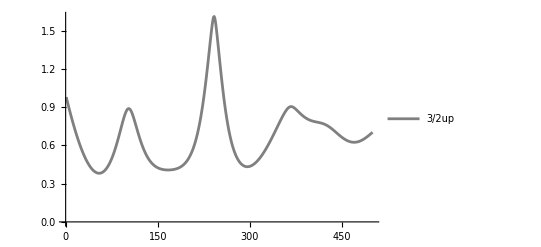

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

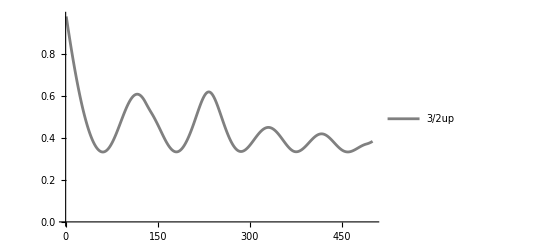

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

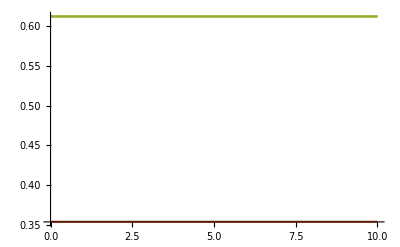

```mathematica
Plot[{Norm[ⅇ^((3 ⅈ t1)/4)/(2 √2)],Norm[-1/2 ⅈ √(3/2) ⅇ^((3 ⅈ t1)/4)],Norm[-1/2 √(3/2) ⅇ^((3 ⅈ t1)/4)],Norm[(ⅈ ⅇ^((3 ⅈ t1)/4))/(2 √2)]},{t1,0,10}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980101,0.960409,0.940929,0.921668,0.902633,0.883829,0.865263,0.84694,0.828866,0.811048,0.793489,0.776197,0.759176,0.742432,0.725969,0.709793,0.69391,0.678322,0.663036,0.648056,0.633363,0.618949,0.604834,0.591034,0.577563,0.564435,0.551659,0.539246,0.527204,0.51554,0.504224,0.493227,0.482555,0.472215,0.462213,0.452554,0.443245,0.434289,0.425692,0.417458,0.40959,0.402093,0.39497,0.388225,0.38186,0.375879,0.370284,0.365077,0.360262,0.355839,0.351811,0.34818,0.344945,0.342109,0.339672,0.337635,0.335997,0.334758,0.333919,0.333479,0.333437,0.333796,0.334557,0.335721,0.337287,0.339253,0.341615,0.344367,0.347504,0.351016,0.354894,0.359129,0.363709,0.36862,0.37385,0.379383,0.385203,0.391293,0.397637,0.404215,0.411007,0.417991,0.425147,0.432452,0.439885,0.447423,0.455043,0.462721,0.470434,0.478158,0.485871,0.493549,0.50117,0.508708,0.51614,0.52344,0.530585,0.537551,0.544315,0.550853,0.557143,0.563161,0.568887,0.5743,0.579381,0.584113,0.588478,0.592461,0.596047,0.599224,0.60198,0.604304,0.606188,0.607624,0.608608,0.609134,0.609202,0.60881,0.607959,0.606654,0.604899,0.6027,0.600065,0.597003,0.593526,0.589646,0.585377,0.580734,0.575735,0.570396,0.564922,0.559507,0.554155,0.548868,0.54365,0.538506,0.533439,0.528453,0.523553,0.518743,0.513892,0.508875,0.503705,0.498393,0.492953,0.4874,0.481746,0.476009,0.470202,0.464342,0.458411,0.452393,0.446312,0.440188,0.434044,0.427903,0.421787,0.415718,0.409718,0.403809,0.398014,0.392355,0.386853,0.381527,0.376398,0.371484,0.366804,0.362377,0.358218,0.354344,0.350769,0.347508,0.344572,0.341971,0.339718,0.337822,0.336292,0.335138,0.334367,0.333987,0.334004,0.334419,0.335227,0.336424,0.338006,0.339967,0.342302,0.345005,0.348069,0.35149,0.355258,0.359366,0.363807,0.368571,0.373649,0.379032,0.384708,0.390666,0.396895,0.403381,0.410116,0.417092,0.424295,0.431714,0.439332,0.447135,0.455107,0.463231,0.471487,0.479857,0.488314,0.496825,0.505361,0.513891,0.522382,0.530798,0.539101,0.547252,0.555209,0.562927,0.570359,0.577453,0.584163,0.590439,0.596232,0.601496,0.606184,0.610254,0.613666,0.616387,0.61839,0.619653,0.620162,0.619913,0.618907,0.617157,0.614679,0.611501,0.607653,0.603174,0.598105,0.59249,0.586377,0.579814,0.57285,0.565533,0.557911,0.55003,0.541936,0.533671,0.525275,0.516788,0.508245,0.499681,0.491128,0.482616,0.474174,0.465826,0.457598,0.449513,0.441591,0.433852,0.426314,0.418994,0.411909,0.405073,0.398499,0.3922,0.386188,0.380474,0.375068,0.36998,0.365217,0.360788,0.356701,0.352962,0.349577,0.346553,0.343894,0.341605,0.339698,0.338179,0.337041,0.336277,0.335878,0.335834,0.336136,0.336771,0.337728,0.338993,0.340553,0.342394,0.344499,0.346854,0.349442,0.352246,0.35525,0.358435,0.361783,0.365277,0.368898,0.372627,0.376445,0.380333,0.384273,0.388245,0.392231,0.396213,0.400171,0.404088,0.407946,0.411728,0.415417,0.418996,0.42245,0.425763,0.428922,0.431912,0.43472,0.437334,0.439742,0.441935,0.443903,0.445636,0.447128,0.448373,0.449365,0.4501,0.450575,0.450787,0.450736,0.450423,0.449849,0.449015,0.447927,0.446587,0.445003,0.44318,0.441127,0.438852,0.436365,0.433676,0.430797,0.427741,0.42452,0.421149,0.417642,0.414013,0.41028,0.406459,0.402566,0.398619,0.394635,0.390632,0.386629,0.382644,0.378696,0.374803,0.370984,0.367258,0.363643,0.360158,0.356822,0.353651,0.350665,0.34788,0.345313,0.342982,0.340901,0.339088,0.33757,0.336364,0.335462,0.334858,0.334544,0.334512,0.334754,0.33526,0.336022,0.33703,0.338272,0.339736,0.341411,0.343285,0.345347,0.347584,0.349983,0.35253,0.355211,0.358012,0.360919,0.363918,0.366992,0.370125,0.373301,0.376501,0.37971,0.382909,0.386081,0.389208,0.392272,0.395254,0.398138,0.400906,0.403542,0.40603,0.408355,0.410502,0.412458,0.414211,0.41575,0.417066,0.418151,0.418998,0.4196,0.419954,0.420058,0.41991,0.419513,0.418868,0.41798,0.416854,0.415499,0.413922,0.412135,0.410148,0.407975,0.405628,0.403123,0.400475,0.3977,0.394814,0.391834,0.388778,0.385662,0.382506,0.379326,0.37614,0.372966,0.369821,0.366721,0.36368,0.360713,0.357835,0.355059,0.352399,0.349869,0.347481,0.345247,0.343181,0.341307,0.339643,0.338185,0.336934,0.335887,0.335042,0.334399,0.333956,0.333712,0.333669,0.333824,0.334171,0.334697,0.335389,0.336236,0.337225,0.338344,0.339581,0.340924,0.342361,0.343879,0.345463,0.347099,0.348775,0.350477,0.352193,0.353911,0.355618,0.357303,0.358956,0.360565,0.362121,0.363613,0.365033,0.366371,0.367621,0.368774,0.369824,0.370765,0.371592,0.372407,0.373319,0.374329,0.37544,0.376655,0.377978,0.379413,0.380962,0.38263,0.384422}

```mathematica
ComplexExpand[ⅇ^((3 ⅈ t1)/4)/(2 √2)]
```

Cos[(3 t1)/4]/(2 √2)+(ⅈ Sin[(3 t1)/4])/(2 √2)

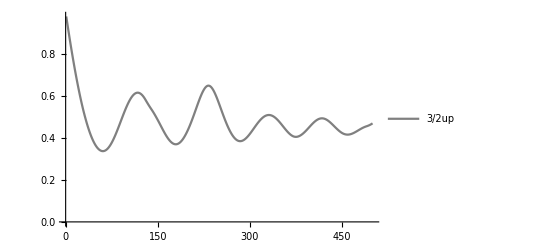

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

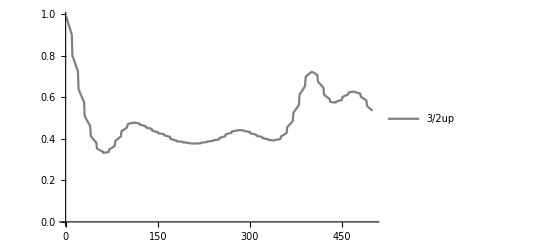

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

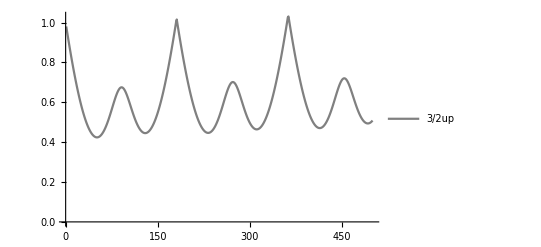

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

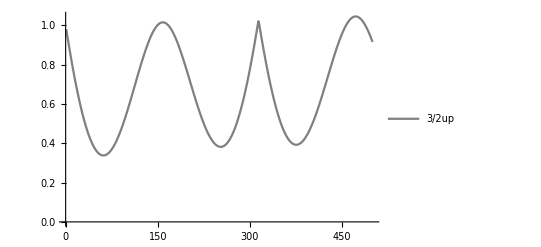

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

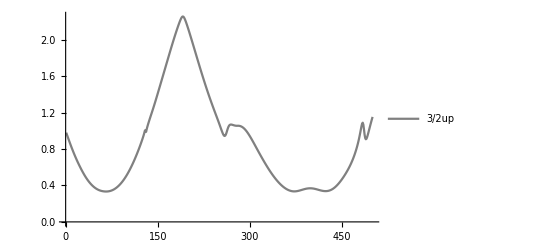

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

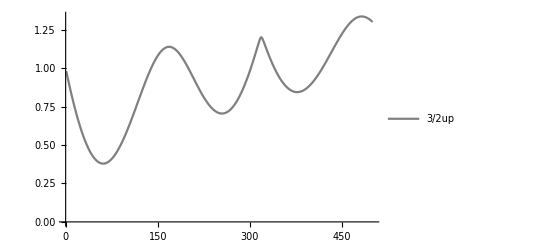

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980101,0.960409,0.940929,0.921668,0.902633,0.883829,0.865263,0.84694,0.828866,0.811048,0.793489,0.776197,0.759176,0.742431,0.725969,0.709793,0.69391,0.678322,0.663036,0.648056,0.633363,0.618949,0.604833,0.591033,0.577563,0.564435,0.551661,0.53925,0.527209,0.515547,0.504233,0.493237,0.482566,0.472227,0.462225,0.452567,0.443258,0.434302,0.425705,0.417471,0.409604,0.40211,0.394992,0.388254,0.381899,0.375929,0.370347,0.365154,0.360353,0.355944,0.351927,0.348303,0.345075,0.342247,0.339819,0.337792,0.336164,0.334931,0.33409,0.333634,0.333557,0.333851,0.334507,0.335515,0.336863,0.33854,0.340532,0.342827,0.34541,0.348264,0.351375,0.354724,0.358295,0.362071,0.366032,0.370161,0.374439,0.378846,0.383363,0.38797,0.392648,0.397376,0.402135,0.406905,0.411665,0.416396,0.421079,0.425693,0.430221,0.434643,0.438943,0.443101,0.447102,0.450928,0.454565,0.457998,0.461212,0.464195,0.466934,0.469419,0.471639,0.473585,0.475249,0.476625,0.477707,0.47849,0.478972,0.47915,0.479023,0.478593,0.477965,0.477249,0.476448,0.475564,0.474603,0.473569,0.472468,0.471306,0.470089,0.468825,0.467519,0.466178,0.46481,0.463424,0.46203,0.460638,0.459258,0.457901,0.456579,0.455301,0.454038,0.452745,0.451414,0.45004,0.448617,0.447138,0.4456,0.443997,0.442327,0.440587,0.438842,0.437166,0.435568,0.434054,0.432634,0.431317,0.430111,0.429025,0.428069,0.427253,0.426491,0.42569,0.424844,0.423947,0.422995,0.421983,0.42091,0.41977,0.418563,0.417286,0.415939,0.414522,0.413034,0.411476,0.409849,0.408154,0.406394,0.404572,0.40269,0.400753,0.398859,0.397105,0.395494,0.39403,0.392715,0.391554,0.39055,0.389708,0.389032,0.388528,0.388104,0.387665,0.38721,0.386741,0.386257,0.385759,0.385249,0.384729,0.384202,0.38367,0.383141,0.382618,0.382104,0.381601,0.381111,0.380637,0.380182,0.379749,0.379343,0.378969,0.37863,0.378331,0.378073,0.377858,0.377689,0.377568,0.377498,0.377483,0.377526,0.377631,0.377803,0.378037,0.378329,0.378673,0.379063,0.379495,0.379964,0.380465,0.380995,0.381549,0.382126,0.382724,0.383335,0.383953,0.384572,0.385186,0.385789,0.386379,0.386949,0.387497,0.38803,0.388562,0.389096,0.389638,0.390192,0.390763,0.391358,0.391983,0.392645,0.393349,0.394103,0.394912,0.395783,0.396725,0.397746,0.398854,0.400058,0.401368,0.402793,0.404341,0.405977,0.407652,0.409356,0.411082,0.412821,0.414565,0.416308,0.418042,0.41976,0.421456,0.423127,0.424768,0.42637,0.427924,0.429422,0.430858,0.432226,0.433519,0.434732,0.435861,0.436903,0.437857,0.438718,0.439483,0.440147,0.440709,0.441168,0.441521,0.44177,0.441913,0.441952,0.441889,0.441725,0.441462,0.441105,0.440655,0.440117,0.439494,0.438793,0.438016,0.437172,0.436265,0.435299,0.434277,0.433202,0.432078,0.43091,0.429703,0.42846,0.427187,0.425919,0.424684,0.423476,0.422291,0.421123,0.419968,0.418822,0.417682,0.416543,0.415403,0.414256,0.413097,0.411928,0.410752,0.40957,0.408388,0.407208,0.406037,0.404881,0.403745,0.402637,0.401559,0.400515,0.39951,0.398548,0.397635,0.396778,0.395983,0.395259,0.394613,0.394053,0.393583,0.393213,0.392951,0.392807,0.39279,0.39291,0.393177,0.3936,0.394191,0.394954,0.395894,0.39702,0.398341,0.399866,0.401603,0.403562,0.40575,0.408174,0.410844,0.4138,0.417077,0.420669,0.42457,0.428775,0.433277,0.438071,0.443148,0.448504,0.45413,0.46001,0.466127,0.472472,0.479034,0.485804,0.492768,0.499917,0.507237,0.514715,0.522336,0.530126,0.538115,0.546295,0.554656,0.563189,0.571884,0.580728,0.58971,0.598816,0.608032,0.617302,0.626553,0.635747,0.644843,0.653794,0.662551,0.671062,0.679269,0.687114,0.694533,0.701369,0.707461,0.712745,0.717167,0.72068,0.723253,0.724866,0.725518,0.725225,0.724018,0.721995,0.719261,0.715867,0.711876,0.707351,0.702361,0.696974,0.691259,0.685284,0.679112,0.672771,0.666288,0.659728,0.65315,0.646607,0.640152,0.63383,0.627683,0.621751,0.61607,0.610712,0.60573,0.601129,0.596913,0.593082,0.589638,0.58658,0.583906,0.581613,0.579696,0.57815,0.576969,0.576142,0.575658,0.575506,0.575672,0.576141,0.576897,0.577921,0.579196,0.580701,0.582418,0.584323,0.586395,0.588611,0.590946,0.593378,0.595881,0.598432,0.601005,0.603577,0.606121,0.608616,0.611038,0.613367,0.615584,0.617669,0.619606,0.621381,0.622981,0.624382,0.625563,0.626512,0.627221,0.627683,0.627892,0.627844,0.627538,0.62697,0.626143,0.625058,0.623717,0.622122,0.620278,0.618188,0.615857,0.613291,0.610495,0.607474,0.604236,0.600785,0.597128,0.593267,0.589207,0.584954,0.58051,0.575883,0.571077,0.566099,0.560954,0.555762,0.550634,0.545564,0.540548,0.535585,0.530671,0.525808,0.520996,0.516238,0.511536}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980201,0.96061,0.941232,0.922074,0.903142,0.884441,0.865979,0.847759,0.829789,0.812074,0.794619,0.77743,0.760512,0.743869,0.727508,0.711433,0.695649,0.680161,0.664972,0.650088,0.63549,0.621172,0.607151,0.593446,0.58007,0.567037,0.554356,0.542037,0.530089,0.518519,0.507294,0.496386,0.4858,0.475543,0.465621,0.456039,0.446803,0.437918,0.429388,0.421218,0.413411,0.405974,0.39891,0.392222,0.385912,0.379984,0.374439,0.36928,0.364508,0.360125,0.35613,0.352526,0.349317,0.346507,0.344095,0.342083,0.340468,0.339248,0.338418,0.337972,0.337904,0.338207,0.338871,0.339886,0.341241,0.342925,0.344925,0.347228,0.349818,0.352682,0.355802,0.359163,0.362747,0.366538,0.370516,0.374664,0.378964,0.383396,0.387942,0.392582,0.397296,0.402066,0.406871,0.411691,0.416508,0.421302,0.426053,0.430744,0.435354,0.439867,0.444264,0.448528,0.452643,0.456593,0.460362,0.463936,0.467301,0.470445,0.473355,0.476021,0.478433,0.480582,0.482459,0.484059,0.485376,0.486406,0.487144,0.487591,0.487743,0.487603,0.487273,0.48686,0.486365,0.485791,0.485144,0.484428,0.483647,0.482809,0.481918,0.480982,0.480006,0.478996,0.47796,0.476907,0.475847,0.474787,0.47374,0.472714,0.47172,0.47077,0.469835,0.468874,0.467881,0.466848,0.465771,0.464643,0.46346,0.462217,0.46091,0.459536,0.458159,0.456847,0.455609,0.454451,0.453383,0.452411,0.451545,0.450793,0.450164,0.449667,0.449223,0.448742,0.448218,0.447647,0.447024,0.446344,0.445604,0.4448,0.44393,0.442992,0.441985,0.440909,0.439763,0.438547,0.437263,0.43591,0.434492,0.433011,0.431469,0.42987,0.42831,0.426883,0.42559,0.424436,0.423421,0.422551,0.421829,0.421258,0.420842,0.420587,0.420406,0.420207,0.419991,0.419757,0.419506,0.419238,0.418954,0.418658,0.41835,0.418034,0.417716,0.4174,0.417089,0.416783,0.416486,0.416199,0.415927,0.415671,0.415438,0.41523,0.415052,0.414908,0.414801,0.41473,0.4147,0.414713,0.414772,0.41488,0.415041,0.41526,0.41554,0.41588,0.416275,0.416719,0.417208,0.417738,0.418304,0.418902,0.419529,0.420182,0.42086,0.421561,0.422277,0.423003,0.423734,0.424464,0.425189,0.425904,0.426605,0.42729,0.427966,0.428646,0.429335,0.430036,0.430754,0.431496,0.432267,0.433072,0.433919,0.434814,0.435763,0.436771,0.437845,0.438992,0.440222,0.441542,0.44296,0.444485,0.446125,0.44789,0.449741,0.451632,0.453552,0.455493,0.457447,0.459407,0.461365,0.463314,0.465248,0.467159,0.469046,0.470899,0.472712,0.474476,0.476184,0.477828,0.479402,0.480902,0.482321,0.483655,0.484903,0.486061,0.487126,0.488093,0.488961,0.489726,0.490388,0.490946,0.491399,0.491748,0.491995,0.49214,0.492187,0.492136,0.491993,0.49176,0.491441,0.49104,0.490563,0.490014,0.489399,0.488724,0.487991,0.487205,0.486368,0.485484,0.484558,0.483594,0.482596,0.481569,0.480547,0.479557,0.478593,0.477651,0.476724,0.47581,0.474902,0.473997,0.473092,0.472183,0.471264,0.470328,0.469379,0.468417,0.467444,0.466464,0.465481,0.464499,0.463524,0.462562,0.461619,0.460699,0.459805,0.458941,0.458113,0.457326,0.456586,0.455901,0.455279,0.454726,0.454252,0.453861,0.453562,0.453365,0.453279,0.453313,0.453477,0.453781,0.454236,0.454851,0.455632,0.456585,0.457718,0.459041,0.460562,0.462289,0.464232,0.466397,0.468794,0.471428,0.474341,0.477567,0.481099,0.484932,0.489061,0.493478,0.498179,0.503157,0.508405,0.513915,0.519673,0.525662,0.531872,0.538293,0.544916,0.551728,0.558718,0.565874,0.573182,0.580628,0.588236,0.596034,0.604013,0.612166,0.620482,0.62895,0.637561,0.646301,0.655157,0.664116,0.673121,0.682105,0.691029,0.699852,0.708531,0.717018,0.725262,0.733209,0.740803,0.747985,0.754605,0.760512,0.765647,0.769958,0.773404,0.775955,0.777596,0.778324,0.778155,0.777117,0.775305,0.772817,0.769702,0.766017,0.761822,0.75718,0.752157,0.746815,0.741217,0.735423,0.729456,0.723339,0.717132,0.710889,0.704662,0.698498,0.692443,0.686537,0.680816,0.675317,0.670113,0.665261,0.660767,0.656633,0.652863,0.649457,0.646417,0.643741,0.641427,0.639472,0.637873,0.636623,0.635717,0.635143,0.634892,0.634952,0.635311,0.635953,0.636864,0.638027,0.639424,0.641037,0.642847,0.644833,0.646974,0.649248,0.651634,0.654107,0.656646,0.659227,0.661826,0.66442,0.666986,0.669503,0.671949,0.674306,0.676554,0.678677,0.680659,0.682486,0.684137,0.685591,0.686836,0.687862,0.688662,0.689229,0.689558,0.689646,0.68949,0.689091,0.688449,0.687567,0.686445,0.685087,0.683496,0.681677,0.679635,0.677373,0.674899,0.672217,0.669335,0.666257,0.662986,0.659528,0.655886,0.652065,0.648071,0.643908,0.639582,0.6351,0.630571,0.6261,0.621681,0.61731,0.612985,0.608704,0.604468,0.600276,0.596131,0.592036}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.98108,0.962373,0.943885,0.925621,0.907586,0.889784,0.872221,0.854902,0.837831,0.821013,0.804452,0.788153,0.77212,0.756358,0.74087,0.72566,0.710732,0.696091,0.681739,0.667681,0.653901,0.640398,0.62719,0.614293,0.601722,0.589488,0.577602,0.566073,0.554909,0.544115,0.533654,0.523486,0.513619,0.504057,0.494806,0.485871,0.477257,0.468967,0.461006,0.453377,0.446084,0.43913,0.432517,0.426249,0.420327,0.414754,0.409532,0.404661,0.400144,0.39598,0.392181,0.388758,0.385717,0.38306,0.380791,0.378908,0.377411,0.376298,0.375564,0.375206,0.375218,0.375592,0.376322,0.377398,0.37881,0.380549,0.382603,0.38496,0.387608,0.390533,0.393721,0.397157,0.400826,0.404713,0.408803,0.413078,0.417524,0.422124,0.426861,0.431718,0.436678,0.441725,0.446841,0.452009,0.457213,0.462436,0.467661,0.472872,0.478053,0.483189,0.488263,0.493263,0.498172,0.502978,0.507668,0.512228,0.516647,0.520915,0.52502,0.528953,0.532706,0.53627,0.53964,0.542808,0.54577,0.548521,0.551059,0.553381,0.555486,0.557374,0.559125,0.560817,0.562453,0.564034,0.565564,0.567044,0.568479,0.569871,0.571226,0.572548,0.57384,0.575105,0.576349,0.577579,0.578801,0.58002,0.581245,0.582482,0.583738,0.585021,0.586325,0.587631,0.588934,0.590226,0.5915,0.592751,0.593973,0.595161,0.596309,0.597414,0.598516,0.599662,0.600854,0.602099,0.6034,0.604763,0.606192,0.607693,0.609271,0.610933,0.612631,0.614311,0.615967,0.617592,0.61918,0.620727,0.622226,0.623674,0.625067,0.6264,0.627671,0.628879,0.630021,0.631095,0.6321,0.633036,0.633901,0.634698,0.635425,0.636086,0.636752,0.637498,0.638322,0.639224,0.640204,0.641263,0.642402,0.643622,0.644923,0.646309,0.647722,0.649102,0.650448,0.651759,0.653033,0.65427,0.65547,0.656634,0.657763,0.658858,0.659924,0.660966,0.661985,0.662982,0.663958,0.664915,0.665856,0.666785,0.667703,0.668614,0.669525,0.670442,0.671366,0.672301,0.67325,0.674215,0.675201,0.676212,0.67725,0.678322,0.679439,0.680613,0.68184,0.68312,0.684452,0.685835,0.687269,0.688751,0.690283,0.691864,0.693495,0.695178,0.696908,0.698683,0.700499,0.702355,0.704248,0.706175,0.708134,0.710123,0.712149,0.714221,0.716342,0.718516,0.720746,0.723036,0.725389,0.727811,0.730303,0.732871,0.735518,0.738246,0.74106,0.743964,0.746961,0.750056,0.753253,0.756556,0.759968,0.763495,0.767095,0.770715,0.774349,0.777987,0.781623,0.785248,0.788856,0.79244,0.795993,0.79951,0.802978,0.806387,0.809729,0.812997,0.816185,0.819288,0.822299,0.825215,0.828032,0.830746,0.833353,0.835849,0.83823,0.840496,0.842646,0.844678,0.846594,0.848393,0.85008,0.851654,0.853121,0.854483,0.855745,0.856913,0.857991,0.858986,0.859904,0.860754,0.861541,0.862274,0.862959,0.863601,0.864206,0.864782,0.865333,0.865867,0.866389,0.866905,0.867422,0.867943,0.868494,0.869093,0.869736,0.870417,0.87113,0.87187,0.872629,0.873399,0.874172,0.874941,0.875692,0.876416,0.877104,0.87775,0.878349,0.878894,0.879381,0.879807,0.880169,0.880465,0.880698,0.880867,0.880974,0.88102,0.881008,0.880944,0.880833,0.880686,0.88051,0.880318,0.88012,0.879928,0.879756,0.879617,0.879523,0.87949,0.879531,0.879659,0.879888,0.880231,0.880699,0.881301,0.882049,0.882952,0.88402,0.885261,0.886683,0.888293,0.890097,0.892101,0.894345,0.896864,0.899655,0.902711,0.906029,0.909603,0.913427,0.917497,0.921806,0.926347,0.931111,0.936086,0.941262,0.946631,0.952183,0.957908,0.963796,0.969834,0.976011,0.982313,0.988746,0.995317,1.00202,1.00885,1.01579,1.02285,1.03,1.03724,1.04457,1.05196,1.0594,1.06684,1.07425,1.08161,1.08889,1.09604,1.10305,1.10987,1.11646,1.12278,1.12874,1.13424,1.13923,1.14368,1.14756,1.15084,1.1535,1.15554,1.15696,1.15776,1.15799,1.15772,1.15698,1.15579,1.15419,1.15222,1.1499,1.14729,1.14442,1.14133,1.13801,1.13447,1.13074,1.12685,1.12285,1.11874,1.11458,1.11038,1.10617,1.10198,1.09789,1.09396,1.0902,1.08663,1.08323,1.08003,1.07701,1.07418,1.07155,1.06912,1.06689,1.06486,1.06304,1.06143,1.06002,1.05881,1.05781,1.057,1.0564,1.05598,1.05576,1.05572,1.05586,1.05617,1.05665,1.05729,1.05808,1.05902,1.0601,1.0613,1.06262,1.06405,1.06558,1.0672,1.06889,1.07064,1.07245,1.0743,1.07617,1.07806,1.07996,1.08186,1.08373,1.08557,1.08737,1.08913,1.09081,1.09243,1.09397,1.09543,1.0968,1.09806,1.09923,1.1003,1.10125,1.1021,1.10283,1.10345,1.10396,1.10435,1.10463,1.10481,1.10487,1.10483,1.10468,1.10442,1.10407,1.10361,1.10305,1.1024,1.1017,1.10103,1.10036,1.0997,1.09906,1.09842,1.0978,1.09719,1.0966,1.09602}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Length[IniStateBox]
```

1

```mathematica
Print[Chop[SqueezeListBox[[1,1,1]]/(3/2)]]
```

{0.980201,0.96061,0.941232,0.922074,0.903143,0.884443,0.865981,0.847763,0.829794,0.81208,0.794628,0.777441,0.760525,0.743886,0.727529,0.711458,0.695679,0.680196,0.665014,0.650136,0.635569,0.621314,0.607378,0.593763,0.580474,0.567514,0.554887,0.542595,0.530642,0.519032,0.507767,0.49685,0.486283,0.47607,0.466211,0.45671,0.447568,0.438788,0.43037,0.422317,0.414629,0.407309,0.400356,0.393772,0.387557,0.381712,0.376237,0.371133,0.366399,0.362035,0.35804,0.354415,0.351159,0.34827,0.345747,0.34359,0.341797,0.340366,0.339296,0.338584,0.338228,0.338227,0.338577,0.339276,0.340322,0.34171,0.343439,0.345503,0.347901,0.350628,0.35368,0.357054,0.360744,0.364746,0.369057,0.37367,0.378581,0.383786,0.389277,0.395051,0.4011,0.407421,0.414005,0.420847,0.427941,0.435281,0.442858,0.450667,0.4587,0.466951,0.475411,0.484073,0.492929,0.501971,0.511192,0.520583,0.530135,0.53984,0.54969,0.559674,0.569785,0.580013,0.590349,0.600782,0.611305,0.621905,0.632575,0.643303,0.654079,0.664893,0.675735,0.686594,0.697459,0.70832,0.719164,0.729983,0.740763,0.751495,0.762166,0.772766,0.783282,0.793704,0.80402,0.814219,0.824289,0.834218,0.843994,0.853608,0.863046,0.872297,0.881351,0.890196,0.89882,0.907214,0.915365,0.923264,0.930901,0.938263,0.945343,0.95213,0.958615,0.964789,0.970643,0.976169,0.981358,0.986204,0.9907,0.994838,0.998613,1.00202,1.00505,1.0077,1.00998,1.01186,1.01336,1.01447,1.01518,1.0155,1.01543,1.01497,1.01411,1.01287,1.01124,1.00922,1.00682,1.00404,1.00089,0.997376,0.993497,0.989263,0.984679,0.979755,0.974496,0.968911,0.963009,0.956799,0.95029,0.943491,0.936413,0.929065,0.921458,0.913603,0.90551,0.897191,0.888657,0.879918,0.870987,0.861875,0.852594,0.843154,0.833569,0.823849,0.814007,0.804054,0.794002,0.783862,0.773647,0.763367,0.753034,0.742659,0.732255,0.721832,0.7114,0.700972,0.690558,0.680169,0.669815,0.659507,0.649256,0.639071,0.628962,0.61894,0.609015,0.599195,0.58949,0.57991,0.570463,0.561159,0.552006,0.543013,0.534189,0.525541,0.517078,0.508808,0.500738,0.492876,0.485229,0.477805,0.47061,0.463651,0.456936,0.45047,0.44426,0.438312,0.432631,0.427224,0.422096,0.417253,0.412699,0.40844,0.404481,0.400826,0.39748,0.394446,0.39173,0.389334,0.387263,0.385521,0.38411,0.383034,0.382295,0.381897,0.381843,0.382134,0.382773,0.383762,0.385103,0.386798,0.388848,0.391255,0.394019,0.397143,0.400626,0.404469,0.408673,0.413238,0.418165,0.423453,0.429102,0.435111,0.441481,0.44821,0.455298,0.462743,0.470544,0.478701,0.487211,0.496072,0.505283,0.514843,0.524747,0.534995,0.545584,0.556512,0.567774,0.579369,0.591294,0.603544,0.616118,0.629011,0.642219,0.655739,0.669568,0.6837,0.698132,0.712859,0.727877,0.743182,0.758768,0.774631,0.790766,0.807168,0.823831,0.840751,0.857921,0.875336,0.89299,0.910876,0.928988,0.947318,0.965855,0.984578,1.00342,1.02141,1.01141,0.992817,0.974242,0.95584,0.937639,0.919653,0.901892,0.884361,0.867067,0.850016,0.833215,0.816668,0.80038,0.784357,0.768603,0.753124,0.737924,0.723008,0.70838,0.694045,0.680006,0.666269,0.652836,0.639711,0.626899,0.614402,0.602225,0.59037,0.57884,0.567639,0.55677,0.546234,0.536035,0.526175,0.516656,0.507481,0.49865,0.490167,0.482032,0.474247,0.466814,0.459733,0.453006,0.446633,0.440616,0.434953,0.429647,0.424697,0.420103,0.415865,0.411982,0.408455,0.405282,0.402463,0.399996,0.397881,0.396116,0.3947,0.393631,0.392907,0.392526,0.392486,0.392785,0.393419,0.394387,0.395686,0.397312,0.399262,0.401533,0.404121,0.407023,0.410234,0.413751,0.417569,0.421684,0.426091,0.430786,0.435763,0.441017,0.446544,0.452337,0.458392,0.464701,0.47126,0.478063,0.485102,0.492371,0.499864,0.507575,0.515495,0.523618,0.531937,0.540444,0.549132,0.557993,0.567018,0.576201,0.585532,0.595003,0.604606,0.614332,0.624172,0.634117,0.644158,0.654286,0.664492,0.674765,0.685096,0.695475,0.705893,0.716339,0.726802,0.737274,0.747743,0.758199,0.768631,0.779028,0.78938,0.799676,0.809905,0.820055,0.830117,0.840078,0.849928,0.859655,0.869249,0.878698,0.887991,0.897117,0.906065,0.914824,0.923383,0.931732,0.93986,0.947757,0.955411,0.962814,0.969955,0.976824,0.983412,0.989711,0.99571,1.0014,1.00678,1.01183,1.01656,1.02094,1.02499,1.02868,1.03202,1.035,1.03761,1.03985,1.04173,1.04322,1.04435,1.04509,1.04546,1.04544,1.04505,1.04428,1.04313,1.0416,1.03971,1.03744,1.03481,1.03182,1.02848,1.02478,1.02074,1.01637,1.01166,1.00663,1.00128,0.995627,0.989674,0.983431,0.976907,0.970112,0.963055,0.955747,0.948198,0.940418,0.932418,0.924208,0.9158}

## sequence with decay, master equation backup 5/2

```mathematica
Clear["Global`*"];
(*定义 fidelity 函数*)Fidelity[rho_,sigma_]:=Module[{sqrtRho,inner},sqrtRho=MatrixPower[rho,1/2];
inner=sqrtRho.sigma.sqrtRho;
(Tr[MatrixPower[inner,1/2]])^2]

(*示例：两个 2x2 密度矩阵*)


dim=5/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
(*Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});*)
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;


IniPhi={{1},{0},{0},{0},{0},{0}};

StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi//FullSimplify
StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(χ*(3*Iz3half2.Iz3half2+η*(Iplus3half2.Iplus3half2+Iminus3half2.Iminus3half2)/2))*t].StateθϕInitial[θ,ϕ]

DensityMatrixEvo[t_,θ_,ϕ_]:=StateEvo[t,θ,ϕ].ConjugateTranspose[StateEvo[t,θ,ϕ]]


(*StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].StateθϕInitial[θ,ϕ]
StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t].StateθϕInitial[θ,ϕ]

StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(3Iz3half2.Iz3half2+η/2(Ix3half2.Ix3half2-Iy3half2.Iy3half2))*t].StateθϕInitial[θ,ϕ]
StateEvo2[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].css[θ,ϕ]*)
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
θ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
(*ϕ2[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*Print[N[xVal]];
Print[yVal//FullSimplify];*)
If[First[Flatten[N[xVal]]]==0&&First[Flatten[N[yVal]]]!=0,Pi/2,N[First[Flatten[ArcTan[yVal/xVal]]]]]
]*)
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]
]
ϕ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]]]
]
In1[state_]:=N[-Ix3half2*Sin[ϕ1DM[state]]+Iy3half2*Cos[ϕ1DM[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1DM[state]]Cos[ϕ1DM[state]]-Iy3half2*Cos[θ1DM[state]]Sin[ϕ1DM[state]]+Iz3half2*Sin[θ1DM[state]]]
(*In1[state_]:=N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]
In1n2plusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]*)
In1n2plusSqure[state_]:=Tr[(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=Tr[(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=Tr[(In1[state].In2[state]+In2[state].In1[state]).state]
ξSqure[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )/Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]
(*ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]*)

ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]

(*ξtopF[state_]:=N[First[Flatten[(3 (In1n2plusSqure[state]-Sqrt[(In1n2minusSqure[state])^2+(In1n2n2n1[state])^2]))/((Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2)]]]
ξbottomF[state_]:=N[First[Flatten[ Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]
*)



d=6;
L0=Table[0 ,{i,d*d},{j,d*d}];
Do[L0[[i,j]]=Subscript[L, (i-1)*d*d+j],{i,1,d*d},{j,1,d*d}];
L0List=Flatten[L0];
H0=Table[0 ,{i,d},{j,d}];
ρ0=Table[0 ,{i,d},{j,d}];
Do[H0[[i,j]]=Subscript[H, (i-1)*d+j];ρ0[[i,j]]=Subscript[ρ, (i-1)*d+j],{i,1,d},{j,1,d}](*Print[L0//MatrixForm]; Print[H0//MatrixForm; Print[ρ0//MatrixForm]*)

(*RHLIST=-I*(H0.ρ0-ρ0.H0)+gamma*(PauliMatrix[3].ρ0.PauliMatrix[3]-ρ0);

RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
*)
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.Iz3half2.ρ0.Iz3half2.Iz3half2-1/2(Iz3half2.Iz3half2.Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
(*RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γ, z](KroneckerProduct[Iz3half2,Identit yMatrix[2]].ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));*)
RHBlockList=Flatten[Transpose[RHLIST]];
ρBlockList=Flatten[Transpose[ρ0]]; (*Print[ρBlockList]; Print[RHBlockList//MatrixForm]*)
LHBlockList=L0.Transpose[ρBlockList];(*Print[LHBlockList//MatrixForm]; Print[LHBlockList-RHBlockList//MatrixForm//FullSimplify]*)
Solvelist=LHBlockList-RHBlockList; (*Print[Solvelist//FullSimplify//MatrixForm]; Print[Solvelist[[1]]//FullSimplify//MatrixForm]*)
L1=Table[0 ,{i,d*d},{j,d*d}];
Do[L1[[i,j]]=Coefficient[Solvelist[[i]],Subscript[ρ, j],1],{i,1,d*d},{j,1,d*d}];
Do[L1[[i]]=Sort[L1[[i]]],{i,1,d}] ;(*Print[L1//MatrixForm];*)
L1=Flatten[L1];(*Print[L1//MatrixForm];*)
Do[L1[[i]]=Solve[L1[[i]]==0,L0List],{i,1,d*d*d*d}];
L1resultList=Flatten[Sort[L1]];(*Print[L1resultList]*)
Do[L1resultList[[i]]=L1resultList[[i,2]],{i,1,d*d*d*d}];(*Print[L1resultList]*)
L1resultList=N[Partition[L1resultList,d*d]];

(*HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}});

HMATRIX=Iz3half2.Iz3half2;*)
(*HMATRIX=({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})HMATRIX=IdentityMatrix[6];*)
HMATRIX=({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});

Print[HMATRIX//MatrixForm];

Do[
Subscript[H, (i-1)*d+j]=HMATRIX[[i,j]];
,{i,1,d},{j,1,d}]
Ω=0;
β=1;
Subscript[γI, z]=0.01;
Subscript[γI, x]=0;
Subscript[γS, z]=0;
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

General::stop: 在本次计算中，Solve::svars 的进一步输出将被抑制.

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Ix3half2
```

{{0,(√5)/2,0,0,0,0},{(√5)/2,0,√2,0,0,0},{0,√2,0,3/2,0,0},{0,0,3/2,0,√2,0},{0,0,0,√2,0,(√5)/2},{0,0,0,0,(√5)/2,0}}

```mathematica
ξtopF[DMevolve[[m,k]]];
```

```mathematica
Ix3half2//MatrixForm
```

(0 | (√5)/2 | 0 | 0 | 0 | 0
(√5)/2 | 0 | √2 | 0 | 0 | 0
0 | √2 | 0 | 3/2 | 0 | 0
0 | 0 | 3/2 | 0 | √2 | 0
0 | 0 | 0 | √2 | 0 | (√5)/2
0 | 0 | 0 | 0 | (√5)/2 | 0)

```mathematica
Iy3half2//MatrixForm
```

(0 | -(ⅈ √5)/2 | 0 | 0 | 0 | 0
(ⅈ √5)/2 | 0 | -ⅈ √2 | 0 | 0 | 0
0 | ⅈ √2 | 0 | -(3 ⅈ)/2 | 0 | 0
0 | 0 | (3 ⅈ)/2 | 0 | -ⅈ √2 | 0
0 | 0 | 0 | ⅈ √2 | 0 | -(ⅈ √5)/2
0 | 0 | 0 | 0 | (ⅈ √5)/2 | 0)

```mathematica
Iz3half2//MatrixForm
```

(5/2 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | -3/2 | 0
0 | 0 | 0 | 0 | 0 | -5/2)

```mathematica
MatrixExp[I*Ix3half2*Pi/2].{{1/(√2)},{0},{0},{0},{0},{1/(√2)}}
```

```mathematica
StateθϕInitial[Pi/2,Pi/2]
```

{{1/(4 √2)},{1/4 ⅈ √(5/2)},{-(√5)/4},{-(ⅈ √5)/4},{(√(5/2))/4},{ⅈ/(4 √2)}}

```mathematica
(*UEvo=MatrixExp[-I*({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})*t1];
UEvo=MatrixExp[-I*Iz3half2.Iz3half2*t1];
*)
UEvo=MatrixExp[-I*({{0, (√5)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ11), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(ⅈ ϕ5), 0}})*t1];

(*IniState={{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}};
IniState=StateθϕInitial[Pi/2,Pi/2];
MatrixExp[I*Ix3half2*Pi/2].

{{1/(√2)},{0},{0},{0},{0},{1/(√2)}}
*)
IniState=StateθϕInitial[Pi/2,Pi/2];

EvoState=UEvo.IniState;

dt=0.01;
number1=10 ;
number=10;
totNumber=20;

CtTable=Table[0,{i,0,totNumber}];
(*aaa={{-1.2269057307077853,-1.530271689622663,4.403178377782569,-2.1619964633463926,3.019285024330924,0.18671168010212336,2.24547354378955,2.3388848317093425,2.6974809976000182,1.4377723136713092,0.5971588127479954,1.6631273953201644,1.2984892721243106,2.7426862671553067,1.9213539249618128,0.28355197915516506,2.697327892631874,2.4128954690633266,3.3887193065301515,1.4062078776692593},{0.38971079214838644,0.8485854886614761,0.8123951187874039,0.49267689130473835,0.7161633658278421,0.9908357390648255,1.9709238529011097,2.481869004133195,2.669114789122622,1.4778308380709557,1.4509089068416614,0.8499308790558611,1.7668802465691478,2.213534167514667,2.302893623582208,0.950179141614754,2.8302170880251287,1.9131315037676258,2.762117114238386,0.9995746838624946},{1.5521916924169323,1.5001241952759967,1.4437565558622376,1.5082963760931176,1.4790000666254395,4.046022129883772,2.4338181488669752,1.81487095939405,2.803404669588847,1.8058615427980191,2.8397084407896935,0.7573783856015055,1.7013951623819112,1.921142166425751,2.6694006734625395,0.96691784978275,3.21087919463566,2.721007402015986,3.128933508852332,0.531927349222495},{2.792174241535089,2.2738119577431037,2.147252024033043,2.1860623838295146,1.9421223753440708,2.709264035021671,2.58234308046476,2.078965074818801,2.8717725648335426,0.10627284893373101,2.8971231802638275,0.8227483577933628,2.0525532832817452,1.8854170693583594,2.722732623526076,1.1299076451112828,3.0856562669075664,2.7272761089709245,3.4538311579317655,-0.2699028491166735},{2.0687470187361665,1.7501021842101512,1.3582640614465173,2.2632451841765837,-1.0933677578165,4.04399853459381,4.10186595823439,-0.9620252987963807,3.7961632230498976,-0.39162765173692193,3.5324116623589763,-0.46662748134286147,4.701923117961375,-1.3880241425068913,3.3002603044162813,4.480461741824306,3.1448568966379744,3.3618694281822084,3.1293644301066728,0.11761243267943922}};

ϕ1Table=aaa[[1]];
ϕ2Table=aaa[[2]];
ϕ3Table=aaa[[3]];
ϕ4Table=aaa[[4]];
ϕ5Table=aaa[[5]];
*)
(*
{{3.7598902694445195,3.590977996574284,3.6593033003131428,3.601574441551117,3.176425192783814,3.124159192784357,0.8668561522001461,1.1289914586518943,0.7690378643693294,1.155205488420319,0.6993012350173551,1.358995094803202,2.2368354524205865,1.8330965924310973,2.191771312016466,3.0069178203569695,0.19490072121916358,3.081703205320813,1.4910988051563496,2.333564873847301},{3.2338669678576615,3.2645210129119997,-2.847289039532734,2.795965377961795,1.6200799948407374,1.9486547459750563,0.9977135721021035,1.6599043925282562,2.596796983170254,1.2990610714137318,0.2465193697652257,1.7523268549563022,2.288096462081925,1.6425328617532782,2.010883079241734,3.0715886923245126,0.08015035130703918,2.2268784119059397,0.8815712812255629,1.411485931550104},{1.560503927579032,1.5681129257466213,1.5721423882831909,2.0104474632953027,1.4489917019883487,1.6065196616493758,0.9363287842327614,1.4274583885523784,2.111371728710777,1.4222388036264504,-0.34684203636652144,1.5316112833987825,2.058913587696896,1.142876729105029,2.1347915914125313,3.393562895097861,0.08715394593607506,0.6004575302217319,0.18010309948507697,1.8495121975415776},{-0.11686145918881286,-0.16936101498732814,5.925812460892263,1.9079670308928742,0.13512292961329964,1.3889432546952403,0.9335010666040517,1.3125171768090906,2.380013834940242,0.6577750630229433,3.2536289165930565,1.0726074329754267,2.969277005205355,0.9844369561361441,3.0937785984014416,2.981520053434312,-0.3785333317879225,0.12754100725064887,0.4215290291591254,1.294397031314035},{0.3464574550566395,0.21987738530618595,0.468874662714021,0.19587600141707107,-0.03413648609501152,2.774212079360055,3.2054518843929953,-0.3961931986956304,2.763968388043665,-1.991665819948444,3.8302844976077486,4.149635120805216,3.6617898429347555,-1.1622690362456662,3.7760424129362464,3.490004836173542,0.7585010271839616,1.6214779052721147,-1.205421030531137,3.9878447324096253}};

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415};*)

(*
ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415};

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table=Table[2.581055163108225,{i,0,totNumber}];
ϕ2Table=Table[3.9125553774195057,{i,0,totNumber}];
ϕ3Table=Table[0.8791183546201431,{i,0,totNumber}];

2.581055163108225,3.9125553774195057,0.8791183546201431


ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
*)
(*IniStateBox={{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}};*)
ϕ1Table={3.2206143,3.2206143,3.2206143,3.2206143,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={2.9763257,2.9763257,2.9763257,2.9763257,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={0.1652670,0.1652670,0.1652670,0.1652670,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={−0.0790217,−0.0790217,−0.0790217,−0.0790217,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

IniStateBox={IniState};

fvaluebox={1};
SqueezeListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{i,number*totNumber}];
TargetStateBox={{{1},{0},{0},{0},{0},{0}},{{0},{1},{0},{0},{0},{0}},{{0},{0},{1},{0},{0},{0}},{{0},{0},{0},{1},{0},{0}},{{0},{0},{0},{0},{1},{0}},{{0},{0},{0},{0},{0},{1}}};
DM=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMList=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{l,totNumber}];
Do[
Do[
If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];
(*If[l==1,DM[[m,k]]={{0.004215797623784388,-0.0034188221049111216-0.005956190242023859 ⅈ,-0.036382916328975154-0.026818762192994876 ⅈ,-0.02681875968597505+0.03638288125562952 ⅈ,0.005956199927367338-0.003418822381578952 ⅈ,-5.084056467817924*^-10-0.004215796202740946 ⅈ},{-0.0034188221049110267+0.005956190242023716 ⅈ,0.011187573738863064,0.06739516305544396-0.029653936303286027 ⅈ,-0.029653888783817257-0.06739513107055603 ⅈ,-7.463494204932274*^-9+0.011187587646937159 ⅈ,0.005956188646630358+0.003418820234219863 ⅈ},{-0.036382916328974994+0.026818762192994446 ⅈ,0.06739516305544399+0.029653936303284802 ⅈ,0.4845969347863683,2.0148287264553505*^-7-0.48459661615016214 ⅈ,-0.029654018129121055+0.06739522705636092 ⅈ,0.0268187575406496+0.036382900830955196 ⅈ},{-0.02681875968597483-0.03638288125562879 ⅈ,-0.029653888783818257+0.06739513107055589 ⅈ,2.014828726420656*^-7+0.4845966161501628 ⅈ,0.4845962975142524,-0.06739519507146483-0.02965397060957274 ⅈ,-0.03638286575762162+0.026818755033626535 ⅈ},{0.005956199927367775+0.0034188223815789327 ⅈ,-7.463494234530993*^-9-0.011187587646937159 ⅈ,-0.029654018129121967-0.06739522705636086 ⅈ,-0.06739519507146488+0.029653970609571822 ⅈ,0.011187601555033521,0.0034188205108864893-0.005956198331970978 ⅈ},{-5.084056613338184*^-10+0.004215796202740908 ⅈ,0.005956188646630269-0.003418820234219837 ⅈ,0.026818757540649385-0.0363829008309546 ⅈ,-0.03638286575762136-0.026818755033626174 ⅈ,0.003418820510886431+0.005956198331971137 ⅈ,0.00421579478169795}},DM[[m,k]]=StateFinal;];
*)


(*If[l==1,DM[[m,k]]=IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]],DM[[m,k]]=StateFinal;];*)

DMList[[m,k]]=Flatten[Transpose[DM[[m,k]]]];
,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]

TargetStateDMBox=Table[0,{i,Length[TargetStateBox]}];
Do[
TargetStateDMBox[[i]]=TargetStateBox[[i]].ConjugateTranspose[TargetStateBox[[i]]];
,{i,1,Length[TargetStateDMBox]}]



FListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{j,1,Length[TargetStateBox]},{i,number}];

DMevolvemid=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMevolve=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
(*Print[FListBox];*)
Do[
Do[
ϕ11=ϕ1Table[[l]];
ϕ2=ϕ2Table[[l]];
ϕ3=ϕ3Table[[l]];
ϕ4=ϕ4Table[[l]];
ϕ5=ϕ5Table[[l]];
DMevolvemid[[m,k]]=N[MatrixExp[(L1resultList/. t->(i)*dt)*dt].DMList[[m,k]]];

DMevolve[[m,k]]=Transpose[Partition[DMevolvemid[[m,k]],d]];

SqueezeListBox[[m,k,i+(l-1)*number1]]=ξtopF[DMevolve[[m,k]]];
DMListBox[[m,k,l]]=DMevolve[[m,k]];
FListBox[[m,k,1,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[1]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[1]]]])^1;
FListBox[[m,k,2,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[2]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[2]]]])^1;
FListBox[[m,k,3,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[3]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[3]]]])^1;
FListBox[[m,k,4,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[4]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[4]]]])^1;
FListBox[[m,k,5,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[5]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[5]]]])^1;
FListBox[[m,k,6,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[6]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[6]]]])^1;
If[i==number1,StateFinal=DMevolve[[m,k]]];


DMList[[m,k]]=DMevolvemid[[m,k]];
(*If[Divisible[i,number1/printnumber],Print[i,"/",number1,"   m: ",m,"   k: ",k]];*)
,{i,1,number1}];

,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]
Print[l];
,{l,1,totNumber}]
```

Flatten::normal: Flatten[2.4995+0. ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+0. ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-5.55223×10^-18 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

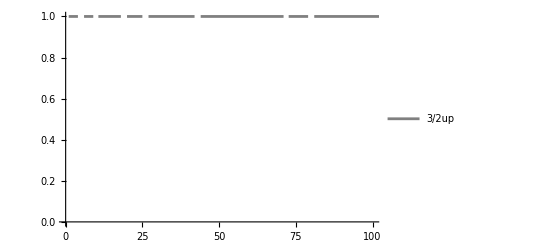

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray},PlotRange->{{0,100},{0,1}}]
```

```mathematica
Chop[DMListBox[[1,1,4]]]
```

{{0.0042158,-0.00341882-0.00595619 ⅈ,-0.0363829-0.0268188 ⅈ,-0.0268188+0.0363829 ⅈ,0.0059562-0.00341882 ⅈ,-5.08406×10^-10-0.0042158 ⅈ},{-0.00341882+0.00595619 ⅈ,0.0111876,0.0673952-0.0296539 ⅈ,-0.0296539-0.0673951 ⅈ,-7.46349×10^-9+0.0111876 ⅈ,0.00595619+0.00341882 ⅈ},{-0.0363829+0.0268188 ⅈ,0.0673952+0.0296539 ⅈ,0.484597,2.01483×10^-7-0.484597 ⅈ,-0.029654+0.0673952 ⅈ,0.0268188+0.0363829 ⅈ},{-0.0268188-0.0363829 ⅈ,-0.0296539+0.0673951 ⅈ,2.01483×10^-7+0.484597 ⅈ,0.484596,-0.0673952-0.029654 ⅈ,-0.0363829+0.0268188 ⅈ},{0.0059562+0.00341882 ⅈ,-7.46349×10^-9-0.0111876 ⅈ,-0.029654-0.0673952 ⅈ,-0.0673952+0.029654 ⅈ,0.0111876,0.00341882-0.0059562 ⅈ},{-5.08406×10^-10+0.0042158 ⅈ,0.00595619-0.00341882 ⅈ,0.0268188-0.0363829 ⅈ,-0.0363829-0.0268188 ⅈ,0.00341882+0.0059562 ⅈ,0.00421579}}

```mathematica
Chop[DMListBox[[1,1,1]]]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0.5,0.497506,0,0},{0,0,0.497506,0.5,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
ξtopF[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0.5000000000000011,0.49750623959634127,0,0},{0,0,0.49750623959634127,0.5000000000000011,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]
```

Flatten::normal: Flatten[0.+0. ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+0. ⅈ] 中的位置 1 处应该是非原子表达式.

General::munfl: ArcCos[1.+0. ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

Flatten::normal: Flatten[0.+0. ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

General::munfl: ArcCos[1.+0. ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

0.5+0. ⅈ

```mathematica
ξtopF[{{0.004215797623784388,-0.0034188221049111216-0.005956190242023859 ⅈ,-0.036382916328975154-0.026818762192994876 ⅈ,-0.02681875968597505+0.03638288125562952 ⅈ,0.005956199927367338-0.003418822381578952 ⅈ,-5.084056467817924*^-10-0.004215796202740946 ⅈ},{-0.0034188221049110267+0.005956190242023716 ⅈ,0.011187573738863064,0.06739516305544396-0.029653936303286027 ⅈ,-0.029653888783817257-0.06739513107055603 ⅈ,-7.463494204932274*^-9+0.011187587646937159 ⅈ,0.005956188646630358+0.003418820234219863 ⅈ},{-0.036382916328974994+0.026818762192994446 ⅈ,0.06739516305544399+0.029653936303284802 ⅈ,0.4845969347863683,2.0148287264553505*^-7-0.48459661615016214 ⅈ,-0.029654018129121055+0.06739522705636092 ⅈ,0.0268187575406496+0.036382900830955196 ⅈ},{-0.02681875968597483-0.03638288125562879 ⅈ,-0.029653888783818257+0.06739513107055589 ⅈ,2.014828726420656*^-7+0.4845966161501628 ⅈ,0.4845962975142524,-0.06739519507146483-0.02965397060957274 ⅈ,-0.03638286575762162+0.026818755033626535 ⅈ},{0.005956199927367775+0.0034188223815789327 ⅈ,-7.463494234530993*^-9-0.011187587646937159 ⅈ,-0.029654018129121967-0.06739522705636086 ⅈ,-0.06739519507146488+0.029653970609571822 ⅈ,0.011187601555033521,0.0034188205108864893-0.005956198331970978 ⅈ},{-5.084056613338184*^-10+0.004215796202740908 ⅈ,0.005956188646630269-0.003418820234219837 ⅈ,0.026818757540649385-0.0363829008309546 ⅈ,-0.03638286575762136-0.026818755033626174 ⅈ,0.003418820510886431+0.005956198331971137 ⅈ,0.00421579478169795}}]
```

Flatten::normal: Flatten[1.64817+1.47451×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+1.54159×10^-24 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+1.22144×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.618586+4.18749×10^-16 ⅈ

```mathematica
0.6185863554387714/2.5
```

0.247435

```mathematica
SqDm={{0.004215797623784388,-0.0034188221049111216-0.005956190242023859 ⅈ,-0.036382916328975154-0.026818762192994876 ⅈ,-0.02681875968597505+0.03638288125562952 ⅈ,0.005956199927367338-0.003418822381578952 ⅈ,-5.084056467817924*^-10-0.004215796202740946 ⅈ},{-0.0034188221049110267+0.005956190242023716 ⅈ,0.011187573738863064,0.06739516305544396-0.029653936303286027 ⅈ,-0.029653888783817257-0.06739513107055603 ⅈ,-7.463494204932274*^-9+0.011187587646937159 ⅈ,0.005956188646630358+0.003418820234219863 ⅈ},{-0.036382916328974994+0.026818762192994446 ⅈ,0.06739516305544399+0.029653936303284802 ⅈ,0.4845969347863683,2.0148287264553505*^-7-0.48459661615016214 ⅈ,-0.029654018129121055+0.06739522705636092 ⅈ,0.0268187575406496+0.036382900830955196 ⅈ},{-0.02681875968597483-0.03638288125562879 ⅈ,-0.029653888783818257+0.06739513107055589 ⅈ,2.014828726420656*^-7+0.4845966161501628 ⅈ,0.4845962975142524,-0.06739519507146483-0.02965397060957274 ⅈ,-0.03638286575762162+0.026818755033626535 ⅈ},{0.005956199927367775+0.0034188223815789327 ⅈ,-7.463494234530993*^-9-0.011187587646937159 ⅈ,-0.029654018129121967-0.06739522705636086 ⅈ,-0.06739519507146488+0.029653970609571822 ⅈ,0.011187601555033521,0.0034188205108864893-0.005956198331970978 ⅈ},{-5.084056613338184*^-10+0.004215796202740908 ⅈ,0.005956188646630269-0.003418820234219837 ⅈ,0.026818757540649385-0.0363829008309546 ⅈ,-0.03638286575762136-0.026818755033626174 ⅈ,0.003418820510886431+0.005956198331971137 ⅈ,0.00421579478169795}};
```

```mathematica
Fidelitylist=Table[0,{m,21}];
Fidelitylist[[1]]=1;
Do[
Fidelitylist[[i]]=Fidelity[N[(IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]).ConjugateTranspose[IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]]],DMListBox[[1,1,i-1]]];
(*
Fidelitylist[[i]]=Fidelity[N[(SqDm.ConjugateTranspose[SqDm]).ConjugateTranspose[SqDm.ConjugateTranspose[SqDm]]],DMListBox[[1,1,i-1]]]

Fidelitylist[[i]]=Fidelity[N[(IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]).ConjugateTranspose[IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]]],DMListBox[[1,1,i-1]]];*)
,{i,2,21}]
```

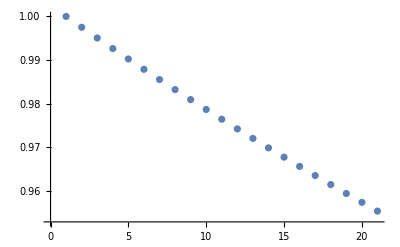

```mathematica
ListPlot[Fidelitylist]
```

```mathematica
Chop[Fidelitylist]
```

{1,0.997515,0.995058,0.99263,0.99023,0.987857,0.985512,0.983193,0.980901,0.978634,0.976392,0.974176,0.971984,0.969816,0.967673,0.965552,0.963455,0.96138,0.959328,0.957297,0.955289}

```mathematica
Pihalf2Pihalf2Iz={1,0.9877148603051069,0.9758444136631702,0.9643672563714281,0.9532634052827575,0.942514186373658,0.9321021331390759,0.9220108938715247,0.9122251469779927,0.9027305235740106,0.8935135366709379,0.8845615163411799,0.875862550307439,0.8674054294570771,0.8591795978318922,0.8511751066877152,0.8433825722578232,0.8357931368895851,0.8283984332556614,0.8211905513696246,0.814162008161577};
Cat5half2N5half2Iz={1,0.9412484512922992,0.8894003915357044,0.8436446393954883,0.8032653298563206,0.7676307142594996,0.7361832763705131,0.7084310098392611,0.6839397205857289,0.6623262336791839,0.6432523984301051,0.6264197979023844,0.6115650800742275,0.5984558376021095,0.5868869717252376,0.5766774834224802,0.5676676416183235,0.5597164841333784,0.5526996122809513,0.5465072446053525,0.5410424993119713};
Cat3half2N3half2Iz={1,0.977998740916552,0.9569655926356172,0.9368579558440209,0.9176351057056407,0.8992581093796942,0.8816897471684335,0.8648944371345363,0.8488381630355247,0.8334884054292471,0.8188140758108978,0.8047854536481672,0.7913741261870081,0.7785529309061014,0.766295900503464,0.7545782103037911,0.7433761279800033,0.7326669654871751,0.7224290331114902,0.7126415955411582,0.7032848298703216};
Cat1half2N1half2Iz={1,0.9975062395963427,0.9950249168745872,0.9925559698015352,0.9900993366533827,0.987654956014173,0.9852227667742621,0.9828027081287921,0.9803947195761719,0.9779987409165608,0.9756147122503699,0.9732425739767553,0.9708822667921398,0.9685337316887183,0.9661969099529912,0.9638717431642956,0.961558173193338,0.95925614220075,0.956965592635636,0.9546864672341395,0.9524187090180047};
Sq5half2Iz={1,0.9965679222977029,0.9931776920138743,0.9898281553865244,0.9865182084904898,0.9832467944526416,0.9800129008625449,0.9768155573618891,0.9736538333975879,0.970526836124948,0.967433708448616,0.9643736271901772,0.9613458013723255,0.9583494706104868,0.9553839036035979,0.9524483967165067,0.9495422726471592,0.9466648791723116,0.9438155879660886,0.9409937934861952,0.9381989119230306};
```

```mathematica
Pihalf2Pihalf2IzIz={1,0.9975146080557411,0.9950581172055272,0.9926300610664396,0.9902299813309469,0.9878574276244717,0.9855119573655352,0.9831931356283548,0.9809005350078921,0.9786337354872938,0.9763923243076864,0.9741758958402785,0.9719840514607353,0.9698163994257788,0.9676725547519811,0.9655521390967201,0.9634547806412008,0.9613801139756264,0.9593277799863359,0.9572974257449831,0.955288704399671};
Cat5half2N5half2IzIz={1,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004};
Sq5half2IzIz={1,0.9996187822594594,0.9992429626458732,0.9988724478414017,0.9985071461855407,0.9981469676455752,0.9977918237875713,0.9974416277478749,0.9970962942051296,0.9967557393527915,0.9964198808721244,0.9960886379056906,0.9957619310313064,0.9954396822364531,0.995121814893179,0.9948082537333982,0.9944989248246742,0.9941937555464067,0.9938926745664634,0.9935956118182118,0.9933024984779696};
```

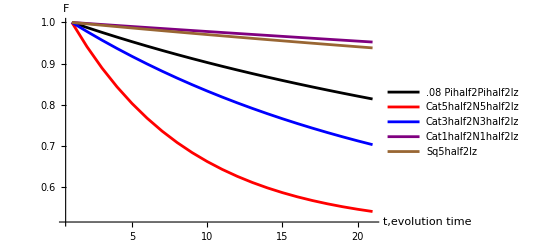

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2Iz,Cat5half2N5half2Iz,Cat3half2N3half2Iz,Cat1half2N1half2Iz,Sq5half2Iz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2Iz","Cat5half2N5half2Iz","Cat3half2N3half2Iz","Cat1half2N1half2Iz","Sq5half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

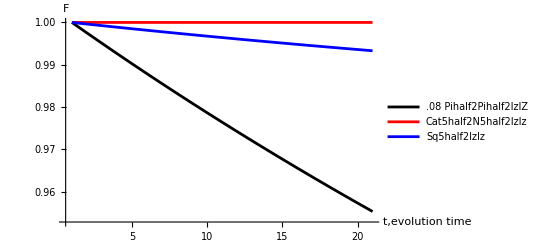

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2IzIz,Cat5half2N5half2IzIz,Sq5half2IzIz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2IzIZ","Cat5half2N5half2IzIz","Sq5half2IzIz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2IzIz,Cat3half2N3half2IzIz,Sq3half2IzIz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2IzIZ","Cat3half2N3half2IzIz","Sq3half2IzIz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

-Graphics-

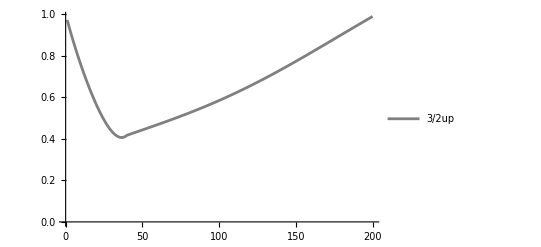

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

{0.972275,0.945352,0.919185,0.89373,0.868951,0.844814,0.821289,0.798352,0.775982,0.754159,0.732872,0.712107,0.69186,0.672125,0.652901,0.634192,0.616004,0.598346,0.581232,0.564677,0.548703,0.533333,0.518596,0.504524,0.491155,0.478529,0.466695,0.455703,0.445611,0.436484,0.42839,0.421406,0.415618,0.411116,0.408,0.40638,0.406373,0.408109,0.411725,0.417371,0.419912,0.422453,0.424993,0.427533,0.430075,0.432618,0.435162,0.437709,0.440259,0.442812,0.445369,0.447931,0.450497,0.453068,0.455646,0.458229,0.460819,0.463417,0.466022,0.468635,0.471257,0.473888,0.476528,0.479178,0.481839,0.484511,0.487193,0.489888,0.492595,0.495314,0.498046,0.500792,0.503551,0.506325,0.509113,0.511916,0.514734,0.517568,0.520417,0.523283,0.526166,0.529066,0.531983,0.534918,0.53787,0.540841,0.54383,0.546838,0.549864,0.55291,0.555976,0.559061,0.562166,0.565291,0.568436,0.571602,0.574788,0.577995,0.581223,0.584472,0.587742,0.591033,0.594346,0.59768,0.601035,0.604412,0.607811,0.611231,0.614673,0.618136,0.621621,0.625127,0.628655,0.632205,0.635776,0.639368,0.642982,0.646617,0.650272,0.653949,0.657647,0.661365,0.665104,0.668863,0.672642,0.676441,0.680261,0.684099,0.687957,0.691834,0.69573,0.699644,0.703577,0.707528,0.711497,0.715483,0.719486,0.723506,0.727543,0.731596,0.735664,0.739749,0.743848,0.747962,0.752091,0.756234,0.76039,0.76456,0.768742,0.772937,0.777145,0.781364,0.785594,0.789835,0.794086,0.798348,0.802619,0.806899,0.811188,0.815486,0.819791,0.824103,0.828423,0.832749,0.837081,0.841419,0.845761,0.850109,0.854461,0.858817,0.863176,0.867538,0.871902,0.876269,0.880637,0.885007,0.889377,0.893747,0.898117,0.902487,0.906856,0.911224,0.915589,0.919953,0.924313,0.928671,0.933025,0.937376,0.941722,0.946063,0.9504,0.954731,0.959057,0.963376,0.967689,0.971995,0.976293,0.980585,0.984868,0.989143}

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

{0.963213,0.927928,0.894108,0.861717,0.830721,0.801085,0.772775,0.74576,0.720006,0.695483,0.672162,0.650015,0.629014,0.609133,0.590348,0.572637,0.555977,0.540348,0.525733,0.512114,0.499476,0.487807,0.477095,0.46733,0.458505,0.450613,0.443653,0.437621,0.432519,0.42835,0.425119,0.422834,0.421505,0.421146,0.421771,0.423401,0.426055,0.429759,0.434541,0.440433,0.44747,0.455691,0.465139,0.475861,0.487911,0.501346,0.516227,0.532623,0.550607,0.570261,0.591671,0.614932,0.640146,0.667424,0.696885,0.72866,0.762888,0.799719,0.839318,0.881861,0.927537,0.976552,1.02913,1.0855,1.14594,1.21071,1.28012,1.35449,1.43417,1.51955,1.61103,1.70906,1.81411,1.9267,2.04739,2.17679,2.31555,2.46437,2.62403,2.79536,2.97926,3.17671,3.38878,3.61662,3.86148,4.12475,4.40792,4.71263,5.04066,5.39398,5.77474,6.18532,6.62835,7.1067,7.62359,8.18259,8.78767,9.44326,10.1543,10.9265,11.766,12.6799,13.6763,14.7642,15.9541,17.2578,18.6888,20.2627,21.9973,23.9133,26.0345,28.3886,31.0078,33.9298,37.1988,40.8666,44.9946,49.6555,54.9358,60.9389,67.7893,75.637,84.6642,95.0934,107.198,121.314,137.863,157.369,180.495,208.086,241.224,281.312,330.185,390.27,464.816,558.226,676.551,828.237,1025.27,1284.98,1632.96,2107.85,2769.6,3713.94,5099.09,7197.05,10497.4,15931.3,25390.9,43050.7+2.57206×10^-7 ⅈ,79131.6+9.03761×10^-7 ⅈ,162340.+3.78538×10^-6 ⅈ,390141.+0.0000215458 ⅈ,1.20149×10^6+0.000204343 ⅈ,5.77878×10^6+0.00473867 ⅈ,7.958×10^7+0.905244 ⅈ,2.59903×10^12+9.73691×10^8 ⅈ,1.5083×10^8+3.29923 ⅈ,7.96335×10^6+0.00921862 ⅈ,1.49019×10^6+0.000322046 ⅈ,459302.+0.0000300083 ⅈ,185306.+5.14661×10^-6 ⅈ,88514.7+1.16341×10^-6 ⅈ,47476.9+3.37838×10^-7 ⅈ,27711.8+1.151×10^-7 ⅈ,17251.2,11298.,7708.73,5440.65,3950.42,2938.54,2231.84,1726.12,1356.44,1081.09,872.564,712.265,587.381,488.9,410.379,347.14,295.736,253.596,218.778,189.799,165.517,145.042,127.674,112.861,100.16,89.2181,79.7471,71.5138,64.3267,58.0282,52.488,47.5974,43.2657,39.4166,35.986}

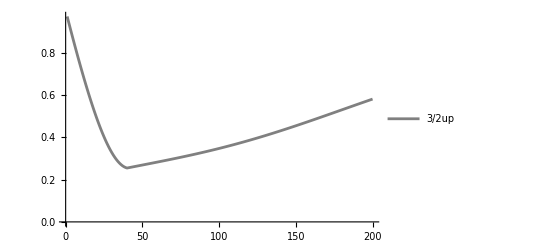

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
StateθϕInitial[Pi/2,Pi/2]
```

{{1/(4 √2)},{1/4 ⅈ √(5/2)},{-(√5)/4},{-(ⅈ √5)/4},{(√(5/2))/4},{ⅈ/(4 √2)}}

```mathematica
{MatrixExp[I*Ix3half2*Pi/2].{{1/(√2)},{0},{0},{0},{0},{1/(√2)}}}
```

{{{1/8+ⅈ/8},{(1/8+ⅈ/8) √5},{(-1/4-ⅈ/4) √(5/2)},{(-1/4-ⅈ/4) √(5/2)},{(1/8+ⅈ/8) √5},{1/8+ⅈ/8}}}

```mathematica
Length[DMListBox[[1,1]]]//MatrixForm
```

20

```mathematica
DMListBox[[1,1]]
```

{{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.441248+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.441248+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.3894+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.3894+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.343645+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.343645+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.303265+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.303265+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.267631+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.267631+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.236183+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.236183+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.208431+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.208431+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.18394+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.18394+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.162326+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.162326+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.143252+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.143252+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.12642+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.12642+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.111565+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.111565+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0984558+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0984558+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.086887+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.086887+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0766775+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0766775+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0676676+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0676676+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0597165+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0597165+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0526996+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0526996+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0465072+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0465072+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0410425+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0410425+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.5+0. ⅈ}}}

```mathematica
N[IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]]
```

{{0.03125,0.-0.0698771 ⅈ,-0.0988212,0.+0.0988212 ⅈ,0.0698771,0.-0.03125 ⅈ},{0.+0.0698771 ⅈ,0.15625,0.-0.220971 ⅈ,-0.220971,0.+0.15625 ⅈ,0.0698771},{-0.0988212,0.+0.220971 ⅈ,0.3125,0.-0.3125 ⅈ,-0.220971,0.+0.0988212 ⅈ},{0.-0.0988212 ⅈ,-0.220971,0.+0.3125 ⅈ,0.3125,0.-0.220971 ⅈ,-0.0988212},{0.0698771,0.-0.15625 ⅈ,-0.220971,0.+0.220971 ⅈ,0.15625,0.-0.0698771 ⅈ},{0.+0.03125 ⅈ,0.0698771,0.-0.0988212 ⅈ,-0.0988212,0.+0.0698771 ⅈ,0.03125}}

```mathematica
ξtopF[Chop[DMListBox[[1,1,4]]]]/2.5
```

Flatten::normal: Flatten[1.5397-3.05311×10^-16 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-3.34058×10^-23 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+1.80717×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

```mathematica
DMListBox[[1,1,4]]
```

{{0.0606461-7.1991×10^-17 ⅈ,0.122096-0.030661 ⅈ,0.0527781-0.0895098 ⅈ,-0.0895097-0.0527781 ⅈ,0.0306611+0.122096 ⅈ,-5.5335×10^-11-0.0606461 ⅈ},{0.122096+0.030661 ⅈ,0.261313+3.21791×10^-16 ⅈ,0.15151-0.153523 ⅈ,-0.153523-0.15151 ⅈ,4.5362×10^-8+0.261313 ⅈ,0.030661-0.122096 ⅈ},{0.0527781+0.0895098 ⅈ,0.15151+0.153523 ⅈ,0.178041-1.30972×10^-16 ⅈ,1.32887×10^-7-0.178041 ⅈ,-0.153523+0.15151 ⅈ,0.0895098-0.0527781 ⅈ},{-0.0895097+0.0527781 ⅈ,-0.153523+0.15151 ⅈ,1.32887×10^-7+0.178041 ⅈ,0.178041+5.55112×10^-17 ⅈ,-0.15151-0.153523 ⅈ,0.0527781+0.0895097 ⅈ},{0.0306611-0.122096 ⅈ,4.5362×10^-8-0.261313 ⅈ,-0.153523-0.15151 ⅈ,-0.15151+0.153523 ⅈ,0.261313-2.28116×10^-16 ⅈ,-0.122096-0.0306611 ⅈ},{-5.53353×10^-11+0.0606461 ⅈ,0.030661+0.122096 ⅈ,0.0895098+0.0527781 ⅈ,0.0527781-0.0895097 ⅈ,-0.122096+0.0306611 ⅈ,0.0606461+5.83301×10^-17 ⅈ}}

```mathematica
Fidelitylist=Table[0,{m,20}];
Do[
Fidelitylist[[i]]=Fidelity[N[({{0.06064613060530813-7.19910242530375*^-17 ⅈ,0.12209626438566488-0.030661048673710993 ⅈ,0.05277806578919029-0.08950977453873414 ⅈ,-0.08950968037760113-0.05277810030433395 ⅈ,0.030661064682025653+0.12209623840886856 ⅈ,-5.533503397246037*^-11-0.06064612703807027 ⅈ},{0.12209626438566476+0.03066104867371091 ⅈ,0.261312593640043+3.217912047936977*^-16 ⅈ,0.15150955446878536-0.15352303865369588 ⅈ,-0.15352283163318256-0.15150957635131984 ⅈ,4.5362024627890185*^-8+0.2613125494354407 ⅈ,0.030661046758808156-0.12209625723187398 ⅈ},{0.05277806578919005+0.08950977453873363 ⅈ,0.15150955446878497+0.15352303865369488 ⅈ,0.17804143246491294-1.3097162243624894*^-16 ⅈ,1.32887047519549*^-7-0.17804132352639723 ⅈ,-0.15352298638218315+0.15150955548938982 ⅈ,0.08950976922556535-0.052778062766428525 ⅈ},{-0.0895096803776005+0.05277810030433431 ⅈ,-0.1535228316331819+0.15150957635131987 ⅈ,1.3288704766873521*^-7+0.17804132352639712 ⅈ,0.1780412145880518+5.551115123125783*^-17 ⅈ,-0.15150957737188403-0.1535227793617031 ⅈ,0.05277809728156973+0.08950967506443834 ⅈ},{0.03066106468202596-0.12209623840886927 ⅈ,4.53620245459245*^-8-0.26131254943544285 ⅈ,-0.15352298638218356-0.15150955548939016 ⅈ,-0.15150957737188372+0.15352277936170242 ⅈ,0.26131250523085653-2.2811613709095013*^-16 ⅈ,-0.12209623125507962-0.030661062767121734 ⅈ},{-5.533525449918225*^-11+0.060646127038070506 ⅈ,0.03066104675880777+0.1220962572318738 ⅈ,0.08950976922556515+0.05277806276642822 ⅈ,0.05277809728156978-0.08950967506443769 ⅈ,-0.1220962312550793+0.030661062767121612 ⅈ,0.06064612347083336+5.833007687972014*^-17 ⅈ}}).ConjugateTranspose[{{0.06064613060530813-7.19910242530375*^-17 ⅈ,0.12209626438566488-0.030661048673710993 ⅈ,0.05277806578919029-0.08950977453873414 ⅈ,-0.08950968037760113-0.05277810030433395 ⅈ,0.030661064682025653+0.12209623840886856 ⅈ,-5.533503397246037*^-11-0.06064612703807027 ⅈ},{0.12209626438566476+0.03066104867371091 ⅈ,0.261312593640043+3.217912047936977*^-16 ⅈ,0.15150955446878536-0.15352303865369588 ⅈ,-0.15352283163318256-0.15150957635131984 ⅈ,4.5362024627890185*^-8+0.2613125494354407 ⅈ,0.030661046758808156-0.12209625723187398 ⅈ},{0.05277806578919005+0.08950977453873363 ⅈ,0.15150955446878497+0.15352303865369488 ⅈ,0.17804143246491294-1.3097162243624894*^-16 ⅈ,1.32887047519549*^-7-0.17804132352639723 ⅈ,-0.15352298638218315+0.15150955548938982 ⅈ,0.08950976922556535-0.052778062766428525 ⅈ},{-0.0895096803776005+0.05277810030433431 ⅈ,-0.1535228316331819+0.15150957635131987 ⅈ,1.3288704766873521*^-7+0.17804132352639712 ⅈ,0.1780412145880518+5.551115123125783*^-17 ⅈ,-0.15150957737188403-0.1535227793617031 ⅈ,0.05277809728156973+0.08950967506443834 ⅈ},{0.03066106468202596-0.12209623840886927 ⅈ,4.53620245459245*^-8-0.26131254943544285 ⅈ,-0.15352298638218356-0.15150955548939016 ⅈ,-0.15150957737188372+0.15352277936170242 ⅈ,0.26131250523085653-2.2811613709095013*^-16 ⅈ,-0.12209623125507962-0.030661062767121734 ⅈ},{-5.533525449918225*^-11+0.060646127038070506 ⅈ,0.03066104675880777+0.1220962572318738 ⅈ,0.08950976922556515+0.05277806276642822 ⅈ,0.05277809728156978-0.08950967506443769 ⅈ,-0.1220962312550793+0.030661062767121612 ⅈ,0.06064612347083336+5.833007687972014*^-17 ⅈ}}]],DMListBox[[1,1,i]]];
,{i,1,20}]
```

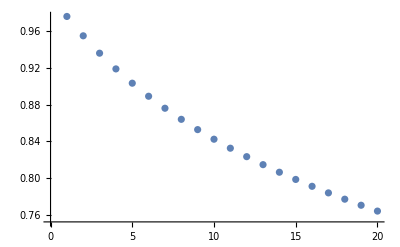

```mathematica
ListPlot[Fidelitylist]
```

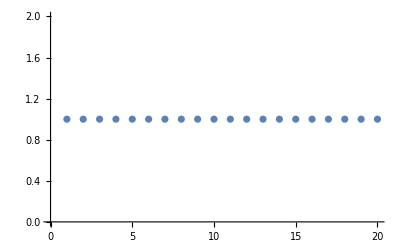

```mathematica
ListPlot[Fidelitylist]
```

```mathematica
ListPlot[Fidelitylist]
```

-Graphics-

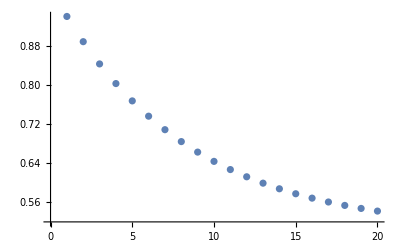

```mathematica
ListPlot[Fidelitylist]
```

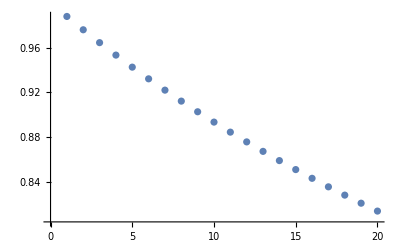

```mathematica
ListPlot[Fidelitylist]
```

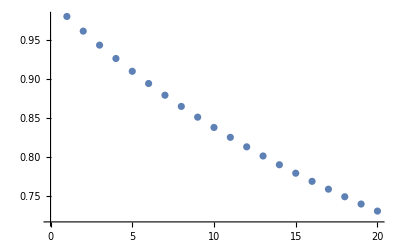

```mathematica
ListPlot[Fidelitylist]
```

```mathematica
DMListBox[[1,1]]
```

{{{0.03125+0. ⅈ,0.-0.0645047 ⅈ,-0.0825424+0. ⅈ,0.+0.0825424 ⅈ,0.0645047+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0645047 ⅈ,0.15625+0. ⅈ,0.-0.216595 ⅈ,-0.216595+0. ⅈ,0.+0.15625 ⅈ,0.0645047+0. ⅈ},{-0.0825424+0. ⅈ,0.+0.216595 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.216595+0. ⅈ,0.+0.0825424 ⅈ},{0.-0.0825424 ⅈ,-0.216595+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.216595 ⅈ,-0.0825424+0. ⅈ},{0.0645047+0. ⅈ,0.-0.15625 ⅈ,-0.216595+0. ⅈ,0.+0.216595 ⅈ,0.15625+0. ⅈ,0.-0.0645047 ⅈ},{0.+0.03125 ⅈ,0.0645047+0. ⅈ,0.-0.0825424 ⅈ,-0.0825424+0. ⅈ,0.+0.0645047 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0595454 ⅈ,-0.0689452+0. ⅈ,0.+0.0689452 ⅈ,0.0595454+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0595454 ⅈ,0.15625+0. ⅈ,0.-0.212306 ⅈ,-0.212306+0. ⅈ,0.+0.15625 ⅈ,0.0595454+0. ⅈ},{-0.0689452+0. ⅈ,0.+0.212306 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.212306+0. ⅈ,0.+0.0689452 ⅈ},{0.-0.0689452 ⅈ,-0.212306+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.212306 ⅈ,-0.0689452+0. ⅈ},{0.0595454+0. ⅈ,0.-0.15625 ⅈ,-0.212306+0. ⅈ,0.+0.212306 ⅈ,0.15625+0. ⅈ,0.-0.0595454 ⅈ},{0.+0.03125 ⅈ,0.0595454+0. ⅈ,0.-0.0689452 ⅈ,-0.0689452+0. ⅈ,0.+0.0595454 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0549673 ⅈ,-0.0575879+0. ⅈ,0.+0.0575879 ⅈ,0.0549673+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0549673 ⅈ,0.15625+0. ⅈ,0.-0.208103 ⅈ,-0.208103+0. ⅈ,0.+0.15625 ⅈ,0.0549673+0. ⅈ},{-0.0575879+0. ⅈ,0.+0.208103 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.208103+0. ⅈ,0.+0.0575879 ⅈ},{0.-0.0575879 ⅈ,-0.208103+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.208103 ⅈ,-0.0575879+0. ⅈ},{0.0549673+0. ⅈ,0.-0.15625 ⅈ,-0.208103+0. ⅈ,0.+0.208103 ⅈ,0.15625+0. ⅈ,0.-0.0549673 ⅈ},{0.+0.03125 ⅈ,0.0549673+0. ⅈ,0.-0.0575879 ⅈ,-0.0575879+0. ⅈ,0.+0.0549673 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0507412 ⅈ,-0.0481014+0. ⅈ,0.+0.0481014 ⅈ,0.0507412+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0507412 ⅈ,0.15625+0. ⅈ,0.-0.203982 ⅈ,-0.203982+0. ⅈ,0.+0.15625 ⅈ,0.0507412+0. ⅈ},{-0.0481014+0. ⅈ,0.+0.203982 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.203982+0. ⅈ,0.+0.0481014 ⅈ},{0.-0.0481014 ⅈ,-0.203982+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.203982 ⅈ,-0.0481014+0. ⅈ},{0.0507412+0. ⅈ,0.-0.15625 ⅈ,-0.203982+0. ⅈ,0.+0.203982 ⅈ,0.15625+0. ⅈ,0.-0.0507412 ⅈ},{0.+0.03125 ⅈ,0.0507412+0. ⅈ,0.-0.0481014 ⅈ,-0.0481014+0. ⅈ,0.+0.0507412 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.04684 ⅈ,-0.0401777+0. ⅈ,0.+0.0401777 ⅈ,0.04684+0. ⅈ,0.-0.03125 ⅈ},{0.+0.04684 ⅈ,0.15625+0. ⅈ,0.-0.199943 ⅈ,-0.199943+0. ⅈ,0.+0.15625 ⅈ,0.04684+0. ⅈ},{-0.0401777+0. ⅈ,0.+0.199943 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.199943+0. ⅈ,0.+0.0401777 ⅈ},{0.-0.0401777 ⅈ,-0.199943+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.199943 ⅈ,-0.0401777+0. ⅈ},{0.04684+0. ⅈ,0.-0.15625 ⅈ,-0.199943+0. ⅈ,0.+0.199943 ⅈ,0.15625+0. ⅈ,0.-0.04684 ⅈ},{0.+0.03125 ⅈ,0.04684+0. ⅈ,0.-0.0401777 ⅈ,-0.0401777+0. ⅈ,0.+0.04684 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0432388 ⅈ,-0.0335592+0. ⅈ,0.+0.0335592 ⅈ,0.0432388+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0432388 ⅈ,0.15625+0. ⅈ,0.-0.195984 ⅈ,-0.195984+0. ⅈ,0.+0.15625 ⅈ,0.0432388+0. ⅈ},{-0.0335592+0. ⅈ,0.+0.195984 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.195984+0. ⅈ,0.+0.0335592 ⅈ},{0.-0.0335592 ⅈ,-0.195984+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.195984 ⅈ,-0.0335592+0. ⅈ},{0.0432388+0. ⅈ,0.-0.15625 ⅈ,-0.195984+0. ⅈ,0.+0.195984 ⅈ,0.15625+0. ⅈ,0.-0.0432388 ⅈ},{0.+0.03125 ⅈ,0.0432388+0. ⅈ,0.-0.0335592 ⅈ,-0.0335592+0. ⅈ,0.+0.0432388 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0399144 ⅈ,-0.028031+0. ⅈ,0.+0.028031 ⅈ,0.0399144+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0399144 ⅈ,0.15625+0. ⅈ,0.-0.192103 ⅈ,-0.192103+0. ⅈ,0.+0.15625 ⅈ,0.0399144+0. ⅈ},{-0.028031+0. ⅈ,0.+0.192103 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.192103+0. ⅈ,0.+0.028031 ⅈ},{0.-0.028031 ⅈ,-0.192103+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.192103 ⅈ,-0.028031+0. ⅈ},{0.0399144+0. ⅈ,0.-0.15625 ⅈ,-0.192103+0. ⅈ,0.+0.192103 ⅈ,0.15625+0. ⅈ,0.-0.0399144 ⅈ},{0.+0.03125 ⅈ,0.0399144+0. ⅈ,0.-0.028031 ⅈ,-0.028031+0. ⅈ,0.+0.0399144 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0368457 ⅈ,-0.0234135+0. ⅈ,0.+0.0234135 ⅈ,0.0368457+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0368457 ⅈ,0.15625+0. ⅈ,0.-0.188299 ⅈ,-0.188299+0. ⅈ,0.+0.15625 ⅈ,0.0368457+0. ⅈ},{-0.0234135+0. ⅈ,0.+0.188299 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.188299+0. ⅈ,0.+0.0234135 ⅈ},{0.-0.0234135 ⅈ,-0.188299+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.188299 ⅈ,-0.0234135+0. ⅈ},{0.0368457+0. ⅈ,0.-0.15625 ⅈ,-0.188299+0. ⅈ,0.+0.188299 ⅈ,0.15625+0. ⅈ,0.-0.0368457 ⅈ},{0.+0.03125 ⅈ,0.0368457+0. ⅈ,0.-0.0234135 ⅈ,-0.0234135+0. ⅈ,0.+0.0368457 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0340128 ⅈ,-0.0195566+0. ⅈ,0.+0.0195566 ⅈ,0.0340128+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0340128 ⅈ,0.15625+0. ⅈ,0.-0.18457 ⅈ,-0.18457+0. ⅈ,0.+0.15625 ⅈ,0.0340128+0. ⅈ},{-0.0195566+0. ⅈ,0.+0.18457 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.18457+0. ⅈ,0.+0.0195566 ⅈ},{0.-0.0195566 ⅈ,-0.18457+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.18457 ⅈ,-0.0195566+0. ⅈ},{0.0340128+0. ⅈ,0.-0.15625 ⅈ,-0.18457+0. ⅈ,0.+0.18457 ⅈ,0.15625+0. ⅈ,0.-0.0340128 ⅈ},{0.+0.03125 ⅈ,0.0340128+0. ⅈ,0.-0.0195566 ⅈ,-0.0195566+0. ⅈ,0.+0.0340128 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0313978 ⅈ,-0.016335+0. ⅈ,0.+0.016335 ⅈ,0.0313978+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0313978 ⅈ,0.15625+0. ⅈ,0.-0.180916 ⅈ,-0.180916+0. ⅈ,0.+0.15625 ⅈ,0.0313978+0. ⅈ},{-0.016335+0. ⅈ,0.+0.180916 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.180916+0. ⅈ,0.+0.016335 ⅈ},{0.-0.016335 ⅈ,-0.180916+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.180916 ⅈ,-0.016335+0. ⅈ},{0.0313978+0. ⅈ,0.-0.15625 ⅈ,-0.180916+0. ⅈ,0.+0.180916 ⅈ,0.15625+0. ⅈ,0.-0.0313978 ⅈ},{0.+0.03125 ⅈ,0.0313978+0. ⅈ,0.-0.016335 ⅈ,-0.016335+0. ⅈ,0.+0.0313978 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0289838 ⅈ,-0.0136442+0. ⅈ,0.+0.0136442 ⅈ,0.0289838+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0289838 ⅈ,0.15625+0. ⅈ,0.-0.177333 ⅈ,-0.177333+0. ⅈ,0.+0.15625 ⅈ,0.0289838+0. ⅈ},{-0.0136442+0. ⅈ,0.+0.177333 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.177333+0. ⅈ,0.+0.0136442 ⅈ},{0.-0.0136442 ⅈ,-0.177333+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.177333 ⅈ,-0.0136442+0. ⅈ},{0.0289838+0. ⅈ,0.-0.15625 ⅈ,-0.177333+0. ⅈ,0.+0.177333 ⅈ,0.15625+0. ⅈ,0.-0.0289838 ⅈ},{0.+0.03125 ⅈ,0.0289838+0. ⅈ,0.-0.0136442 ⅈ,-0.0136442+0. ⅈ,0.+0.0289838 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0267555 ⅈ,-0.0113966+0. ⅈ,0.+0.0113966 ⅈ,0.0267555+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0267555 ⅈ,0.15625+0. ⅈ,0.-0.173822 ⅈ,-0.173822+0. ⅈ,0.+0.15625 ⅈ,0.0267555+0. ⅈ},{-0.0113966+0. ⅈ,0.+0.173822 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.173822+0. ⅈ,0.+0.0113966 ⅈ},{0.-0.0113966 ⅈ,-0.173822+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.173822 ⅈ,-0.0113966+0. ⅈ},{0.0267555+0. ⅈ,0.-0.15625 ⅈ,-0.173822+0. ⅈ,0.+0.173822 ⅈ,0.15625+0. ⅈ,0.-0.0267555 ⅈ},{0.+0.03125 ⅈ,0.0267555+0. ⅈ,0.-0.0113966 ⅈ,-0.0113966+0. ⅈ,0.+0.0267555 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0246984 ⅈ,-0.00951921+0. ⅈ,0.+0.00951921 ⅈ,0.0246984+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0246984 ⅈ,0.15625+0. ⅈ,0.-0.17038 ⅈ,-0.17038+0. ⅈ,0.+0.15625 ⅈ,0.0246984+0. ⅈ},{-0.00951921+0. ⅈ,0.+0.17038 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.17038+0. ⅈ,0.+0.00951921 ⅈ},{0.-0.00951921 ⅈ,-0.17038+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.17038 ⅈ,-0.00951921+0. ⅈ},{0.0246984+0. ⅈ,0.-0.15625 ⅈ,-0.17038+0. ⅈ,0.+0.17038 ⅈ,0.15625+0. ⅈ,0.-0.0246984 ⅈ},{0.+0.03125 ⅈ,0.0246984+0. ⅈ,0.-0.00951921 ⅈ,-0.00951921+0. ⅈ,0.+0.0246984 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0227995 ⅈ,-0.00795111+0. ⅈ,0.+0.00795111 ⅈ,0.0227995+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0227995 ⅈ,0.15625+0. ⅈ,0.-0.167006 ⅈ,-0.167006+0. ⅈ,0.+0.15625 ⅈ,0.0227995+0. ⅈ},{-0.00795111+0. ⅈ,0.+0.167006 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.167006+0. ⅈ,0.+0.00795111 ⅈ},{0.-0.00795111 ⅈ,-0.167006+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.167006 ⅈ,-0.00795111+0. ⅈ},{0.0227995+0. ⅈ,0.-0.15625 ⅈ,-0.167006+0. ⅈ,0.+0.167006 ⅈ,0.15625+0. ⅈ,0.-0.0227995 ⅈ},{0.+0.03125 ⅈ,0.0227995+0. ⅈ,0.-0.00795111 ⅈ,-0.00795111+0. ⅈ,0.+0.0227995 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0210466 ⅈ,-0.00664133+0. ⅈ,0.+0.00664133 ⅈ,0.0210466+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0210466 ⅈ,0.15625+0. ⅈ,0.-0.163699 ⅈ,-0.163699+0. ⅈ,0.+0.15625 ⅈ,0.0210466+0. ⅈ},{-0.00664133+0. ⅈ,0.+0.163699 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.163699+0. ⅈ,0.+0.00664133 ⅈ},{0.-0.00664133 ⅈ,-0.163699+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.163699 ⅈ,-0.00664133+0. ⅈ},{0.0210466+0. ⅈ,0.-0.15625 ⅈ,-0.163699+0. ⅈ,0.+0.163699 ⅈ,0.15625+0. ⅈ,0.-0.0210466 ⅈ},{0.+0.03125 ⅈ,0.0210466+0. ⅈ,0.-0.00664133 ⅈ,-0.00664133+0. ⅈ,0.+0.0210466 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0194284 ⅈ,-0.0055473+0. ⅈ,0.+0.0055473 ⅈ,0.0194284+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0194284 ⅈ,0.15625+0. ⅈ,0.-0.160458 ⅈ,-0.160458+0. ⅈ,0.+0.15625 ⅈ,0.0194284+0. ⅈ},{-0.0055473+0. ⅈ,0.+0.160458 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.160458+0. ⅈ,0.+0.0055473 ⅈ},{0.-0.0055473 ⅈ,-0.160458+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.160458 ⅈ,-0.0055473+0. ⅈ},{0.0194284+0. ⅈ,0.-0.15625 ⅈ,-0.160458+0. ⅈ,0.+0.160458 ⅈ,0.15625+0. ⅈ,0.-0.0194284 ⅈ},{0.+0.03125 ⅈ,0.0194284+0. ⅈ,0.-0.0055473 ⅈ,-0.0055473+0. ⅈ,0.+0.0194284 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0179347 ⅈ,-0.0046335+0. ⅈ,0.+0.0046335 ⅈ,0.0179347+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0179347 ⅈ,0.15625+0. ⅈ,0.-0.157281 ⅈ,-0.157281+0. ⅈ,0.+0.15625 ⅈ,0.0179347+0. ⅈ},{-0.0046335+0. ⅈ,0.+0.157281 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.157281+0. ⅈ,0.+0.0046335 ⅈ},{0.-0.0046335 ⅈ,-0.157281+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.157281 ⅈ,-0.0046335+0. ⅈ},{0.0179347+0. ⅈ,0.-0.15625 ⅈ,-0.157281+0. ⅈ,0.+0.157281 ⅈ,0.15625+0. ⅈ,0.-0.0179347 ⅈ},{0.+0.03125 ⅈ,0.0179347+0. ⅈ,0.-0.0046335 ⅈ,-0.0046335+0. ⅈ,0.+0.0179347 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0165558 ⅈ,-0.00387022+0. ⅈ,0.+0.00387022 ⅈ,0.0165558+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0165558 ⅈ,0.15625+0. ⅈ,0.-0.154166 ⅈ,-0.154166+0. ⅈ,0.+0.15625 ⅈ,0.0165558+0. ⅈ},{-0.00387022+0. ⅈ,0.+0.154166 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.154166+0. ⅈ,0.+0.00387022 ⅈ},{0.-0.00387022 ⅈ,-0.154166+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.154166 ⅈ,-0.00387022+0. ⅈ},{0.0165558+0. ⅈ,0.-0.15625 ⅈ,-0.154166+0. ⅈ,0.+0.154166 ⅈ,0.15625+0. ⅈ,0.-0.0165558 ⅈ},{0.+0.03125 ⅈ,0.0165558+0. ⅈ,0.-0.00387022 ⅈ,-0.00387022+0. ⅈ,0.+0.0165558 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.015283 ⅈ,-0.00323268+0. ⅈ,0.+0.00323268 ⅈ,0.015283+0. ⅈ,0.-0.03125 ⅈ},{0.+0.015283 ⅈ,0.15625+0. ⅈ,0.-0.151113 ⅈ,-0.151113+0. ⅈ,0.+0.15625 ⅈ,0.015283+0. ⅈ},{-0.00323268+0. ⅈ,0.+0.151113 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.151113+0. ⅈ,0.+0.00323268 ⅈ},{0.-0.00323268 ⅈ,-0.151113+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.151113 ⅈ,-0.00323268+0. ⅈ},{0.015283+0. ⅈ,0.-0.15625 ⅈ,-0.151113+0. ⅈ,0.+0.151113 ⅈ,0.15625+0. ⅈ,0.-0.015283 ⅈ},{0.+0.03125 ⅈ,0.015283+0. ⅈ,0.-0.00323268 ⅈ,-0.00323268+0. ⅈ,0.+0.015283 ⅈ,0.03125+0. ⅈ}},{{0.03125+0. ⅈ,0.-0.0141079 ⅈ,-0.00270016+0. ⅈ,0.+0.00270016 ⅈ,0.0141079+0. ⅈ,0.-0.03125 ⅈ},{0.+0.0141079 ⅈ,0.15625+0. ⅈ,0.-0.148121 ⅈ,-0.148121+0. ⅈ,0.+0.15625 ⅈ,0.0141079+0. ⅈ},{-0.00270016+0. ⅈ,0.+0.148121 ⅈ,0.3125+0. ⅈ,0.-0.3125 ⅈ,-0.148121+0. ⅈ,0.+0.00270016 ⅈ},{0.-0.00270016 ⅈ,-0.148121+0. ⅈ,0.+0.3125 ⅈ,0.3125+0. ⅈ,0.-0.148121 ⅈ,-0.00270016+0. ⅈ},{0.0141079+0. ⅈ,0.-0.15625 ⅈ,-0.148121+0. ⅈ,0.+0.148121 ⅈ,0.15625+0. ⅈ,0.-0.0141079 ⅈ},{0.+0.03125 ⅈ,0.0141079+0. ⅈ,0.-0.00270016 ⅈ,-0.00270016+0. ⅈ,0.+0.0141079 ⅈ,0.03125+0. ⅈ}}}

(((0.03125+0. ⅈ
0.-0.0645047 ⅈ
-0.0825424+0. ⅈ
0.+0.0825424 ⅈ
0.0645047+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0645047 ⅈ
0.15625+0. ⅈ
0.-0.216595 ⅈ
-0.216595+0. ⅈ
0.+0.15625 ⅈ
0.0645047+0. ⅈ) | (-0.0825424+0. ⅈ
0.+0.216595 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.216595+0. ⅈ
0.+0.0825424 ⅈ) | (0.-0.0825424 ⅈ
-0.216595+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.216595 ⅈ
-0.0825424+0. ⅈ) | (0.0645047+0. ⅈ
0.-0.15625 ⅈ
-0.216595+0. ⅈ
0.+0.216595 ⅈ
0.15625+0. ⅈ
0.-0.0645047 ⅈ) | (0.+0.03125 ⅈ
0.0645047+0. ⅈ
0.-0.0825424 ⅈ
-0.0825424+0. ⅈ
0.+0.0645047 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0595454 ⅈ
-0.0689452+0. ⅈ
0.+0.0689452 ⅈ
0.0595454+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0595454 ⅈ
0.15625+0. ⅈ
0.-0.212306 ⅈ
-0.212306+0. ⅈ
0.+0.15625 ⅈ
0.0595454+0. ⅈ) | (-0.0689452+0. ⅈ
0.+0.212306 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.212306+0. ⅈ
0.+0.0689452 ⅈ) | (0.-0.0689452 ⅈ
-0.212306+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.212306 ⅈ
-0.0689452+0. ⅈ) | (0.0595454+0. ⅈ
0.-0.15625 ⅈ
-0.212306+0. ⅈ
0.+0.212306 ⅈ
0.15625+0. ⅈ
0.-0.0595454 ⅈ) | (0.+0.03125 ⅈ
0.0595454+0. ⅈ
0.-0.0689452 ⅈ
-0.0689452+0. ⅈ
0.+0.0595454 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0549673 ⅈ
-0.0575879+0. ⅈ
0.+0.0575879 ⅈ
0.0549673+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0549673 ⅈ
0.15625+0. ⅈ
0.-0.208103 ⅈ
-0.208103+0. ⅈ
0.+0.15625 ⅈ
0.0549673+0. ⅈ) | (-0.0575879+0. ⅈ
0.+0.208103 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.208103+0. ⅈ
0.+0.0575879 ⅈ) | (0.-0.0575879 ⅈ
-0.208103+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.208103 ⅈ
-0.0575879+0. ⅈ) | (0.0549673+0. ⅈ
0.-0.15625 ⅈ
-0.208103+0. ⅈ
0.+0.208103 ⅈ
0.15625+0. ⅈ
0.-0.0549673 ⅈ) | (0.+0.03125 ⅈ
0.0549673+0. ⅈ
0.-0.0575879 ⅈ
-0.0575879+0. ⅈ
0.+0.0549673 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0507412 ⅈ
-0.0481014+0. ⅈ
0.+0.0481014 ⅈ
0.0507412+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0507412 ⅈ
0.15625+0. ⅈ
0.-0.203982 ⅈ
-0.203982+0. ⅈ
0.+0.15625 ⅈ
0.0507412+0. ⅈ) | (-0.0481014+0. ⅈ
0.+0.203982 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.203982+0. ⅈ
0.+0.0481014 ⅈ) | (0.-0.0481014 ⅈ
-0.203982+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.203982 ⅈ
-0.0481014+0. ⅈ) | (0.0507412+0. ⅈ
0.-0.15625 ⅈ
-0.203982+0. ⅈ
0.+0.203982 ⅈ
0.15625+0. ⅈ
0.-0.0507412 ⅈ) | (0.+0.03125 ⅈ
0.0507412+0. ⅈ
0.-0.0481014 ⅈ
-0.0481014+0. ⅈ
0.+0.0507412 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.04684 ⅈ
-0.0401777+0. ⅈ
0.+0.0401777 ⅈ
0.04684+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.04684 ⅈ
0.15625+0. ⅈ
0.-0.199943 ⅈ
-0.199943+0. ⅈ
0.+0.15625 ⅈ
0.04684+0. ⅈ) | (-0.0401777+0. ⅈ
0.+0.199943 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.199943+0. ⅈ
0.+0.0401777 ⅈ) | (0.-0.0401777 ⅈ
-0.199943+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.199943 ⅈ
-0.0401777+0. ⅈ) | (0.04684+0. ⅈ
0.-0.15625 ⅈ
-0.199943+0. ⅈ
0.+0.199943 ⅈ
0.15625+0. ⅈ
0.-0.04684 ⅈ) | (0.+0.03125 ⅈ
0.04684+0. ⅈ
0.-0.0401777 ⅈ
-0.0401777+0. ⅈ
0.+0.04684 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0432388 ⅈ
-0.0335592+0. ⅈ
0.+0.0335592 ⅈ
0.0432388+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0432388 ⅈ
0.15625+0. ⅈ
0.-0.195984 ⅈ
-0.195984+0. ⅈ
0.+0.15625 ⅈ
0.0432388+0. ⅈ) | (-0.0335592+0. ⅈ
0.+0.195984 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.195984+0. ⅈ
0.+0.0335592 ⅈ) | (0.-0.0335592 ⅈ
-0.195984+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.195984 ⅈ
-0.0335592+0. ⅈ) | (0.0432388+0. ⅈ
0.-0.15625 ⅈ
-0.195984+0. ⅈ
0.+0.195984 ⅈ
0.15625+0. ⅈ
0.-0.0432388 ⅈ) | (0.+0.03125 ⅈ
0.0432388+0. ⅈ
0.-0.0335592 ⅈ
-0.0335592+0. ⅈ
0.+0.0432388 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0399144 ⅈ
-0.028031+0. ⅈ
0.+0.028031 ⅈ
0.0399144+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0399144 ⅈ
0.15625+0. ⅈ
0.-0.192103 ⅈ
-0.192103+0. ⅈ
0.+0.15625 ⅈ
0.0399144+0. ⅈ) | (-0.028031+0. ⅈ
0.+0.192103 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.192103+0. ⅈ
0.+0.028031 ⅈ) | (0.-0.028031 ⅈ
-0.192103+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.192103 ⅈ
-0.028031+0. ⅈ) | (0.0399144+0. ⅈ
0.-0.15625 ⅈ
-0.192103+0. ⅈ
0.+0.192103 ⅈ
0.15625+0. ⅈ
0.-0.0399144 ⅈ) | (0.+0.03125 ⅈ
0.0399144+0. ⅈ
0.-0.028031 ⅈ
-0.028031+0. ⅈ
0.+0.0399144 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0368457 ⅈ
-0.0234135+0. ⅈ
0.+0.0234135 ⅈ
0.0368457+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0368457 ⅈ
0.15625+0. ⅈ
0.-0.188299 ⅈ
-0.188299+0. ⅈ
0.+0.15625 ⅈ
0.0368457+0. ⅈ) | (-0.0234135+0. ⅈ
0.+0.188299 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.188299+0. ⅈ
0.+0.0234135 ⅈ) | (0.-0.0234135 ⅈ
-0.188299+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.188299 ⅈ
-0.0234135+0. ⅈ) | (0.0368457+0. ⅈ
0.-0.15625 ⅈ
-0.188299+0. ⅈ
0.+0.188299 ⅈ
0.15625+0. ⅈ
0.-0.0368457 ⅈ) | (0.+0.03125 ⅈ
0.0368457+0. ⅈ
0.-0.0234135 ⅈ
-0.0234135+0. ⅈ
0.+0.0368457 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0340128 ⅈ
-0.0195566+0. ⅈ
0.+0.0195566 ⅈ
0.0340128+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0340128 ⅈ
0.15625+0. ⅈ
0.-0.18457 ⅈ
-0.18457+0. ⅈ
0.+0.15625 ⅈ
0.0340128+0. ⅈ) | (-0.0195566+0. ⅈ
0.+0.18457 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.18457+0. ⅈ
0.+0.0195566 ⅈ) | (0.-0.0195566 ⅈ
-0.18457+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.18457 ⅈ
-0.0195566+0. ⅈ) | (0.0340128+0. ⅈ
0.-0.15625 ⅈ
-0.18457+0. ⅈ
0.+0.18457 ⅈ
0.15625+0. ⅈ
0.-0.0340128 ⅈ) | (0.+0.03125 ⅈ
0.0340128+0. ⅈ
0.-0.0195566 ⅈ
-0.0195566+0. ⅈ
0.+0.0340128 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0313978 ⅈ
-0.016335+0. ⅈ
0.+0.016335 ⅈ
0.0313978+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0313978 ⅈ
0.15625+0. ⅈ
0.-0.180916 ⅈ
-0.180916+0. ⅈ
0.+0.15625 ⅈ
0.0313978+0. ⅈ) | (-0.016335+0. ⅈ
0.+0.180916 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.180916+0. ⅈ
0.+0.016335 ⅈ) | (0.-0.016335 ⅈ
-0.180916+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.180916 ⅈ
-0.016335+0. ⅈ) | (0.0313978+0. ⅈ
0.-0.15625 ⅈ
-0.180916+0. ⅈ
0.+0.180916 ⅈ
0.15625+0. ⅈ
0.-0.0313978 ⅈ) | (0.+0.03125 ⅈ
0.0313978+0. ⅈ
0.-0.016335 ⅈ
-0.016335+0. ⅈ
0.+0.0313978 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0289838 ⅈ
-0.0136442+0. ⅈ
0.+0.0136442 ⅈ
0.0289838+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0289838 ⅈ
0.15625+0. ⅈ
0.-0.177333 ⅈ
-0.177333+0. ⅈ
0.+0.15625 ⅈ
0.0289838+0. ⅈ) | (-0.0136442+0. ⅈ
0.+0.177333 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.177333+0. ⅈ
0.+0.0136442 ⅈ) | (0.-0.0136442 ⅈ
-0.177333+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.177333 ⅈ
-0.0136442+0. ⅈ) | (0.0289838+0. ⅈ
0.-0.15625 ⅈ
-0.177333+0. ⅈ
0.+0.177333 ⅈ
0.15625+0. ⅈ
0.-0.0289838 ⅈ) | (0.+0.03125 ⅈ
0.0289838+0. ⅈ
0.-0.0136442 ⅈ
-0.0136442+0. ⅈ
0.+0.0289838 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0267555 ⅈ
-0.0113966+0. ⅈ
0.+0.0113966 ⅈ
0.0267555+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0267555 ⅈ
0.15625+0. ⅈ
0.-0.173822 ⅈ
-0.173822+0. ⅈ
0.+0.15625 ⅈ
0.0267555+0. ⅈ) | (-0.0113966+0. ⅈ
0.+0.173822 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.173822+0. ⅈ
0.+0.0113966 ⅈ) | (0.-0.0113966 ⅈ
-0.173822+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.173822 ⅈ
-0.0113966+0. ⅈ) | (0.0267555+0. ⅈ
0.-0.15625 ⅈ
-0.173822+0. ⅈ
0.+0.173822 ⅈ
0.15625+0. ⅈ
0.-0.0267555 ⅈ) | (0.+0.03125 ⅈ
0.0267555+0. ⅈ
0.-0.0113966 ⅈ
-0.0113966+0. ⅈ
0.+0.0267555 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0246984 ⅈ
-0.00951921+0. ⅈ
0.+0.00951921 ⅈ
0.0246984+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0246984 ⅈ
0.15625+0. ⅈ
0.-0.17038 ⅈ
-0.17038+0. ⅈ
0.+0.15625 ⅈ
0.0246984+0. ⅈ) | (-0.00951921+0. ⅈ
0.+0.17038 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.17038+0. ⅈ
0.+0.00951921 ⅈ) | (0.-0.00951921 ⅈ
-0.17038+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.17038 ⅈ
-0.00951921+0. ⅈ) | (0.0246984+0. ⅈ
0.-0.15625 ⅈ
-0.17038+0. ⅈ
0.+0.17038 ⅈ
0.15625+0. ⅈ
0.-0.0246984 ⅈ) | (0.+0.03125 ⅈ
0.0246984+0. ⅈ
0.-0.00951921 ⅈ
-0.00951921+0. ⅈ
0.+0.0246984 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0227995 ⅈ
-0.00795111+0. ⅈ
0.+0.00795111 ⅈ
0.0227995+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0227995 ⅈ
0.15625+0. ⅈ
0.-0.167006 ⅈ
-0.167006+0. ⅈ
0.+0.15625 ⅈ
0.0227995+0. ⅈ) | (-0.00795111+0. ⅈ
0.+0.167006 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.167006+0. ⅈ
0.+0.00795111 ⅈ) | (0.-0.00795111 ⅈ
-0.167006+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.167006 ⅈ
-0.00795111+0. ⅈ) | (0.0227995+0. ⅈ
0.-0.15625 ⅈ
-0.167006+0. ⅈ
0.+0.167006 ⅈ
0.15625+0. ⅈ
0.-0.0227995 ⅈ) | (0.+0.03125 ⅈ
0.0227995+0. ⅈ
0.-0.00795111 ⅈ
-0.00795111+0. ⅈ
0.+0.0227995 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0210466 ⅈ
-0.00664133+0. ⅈ
0.+0.00664133 ⅈ
0.0210466+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0210466 ⅈ
0.15625+0. ⅈ
0.-0.163699 ⅈ
-0.163699+0. ⅈ
0.+0.15625 ⅈ
0.0210466+0. ⅈ) | (-0.00664133+0. ⅈ
0.+0.163699 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.163699+0. ⅈ
0.+0.00664133 ⅈ) | (0.-0.00664133 ⅈ
-0.163699+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.163699 ⅈ
-0.00664133+0. ⅈ) | (0.0210466+0. ⅈ
0.-0.15625 ⅈ
-0.163699+0. ⅈ
0.+0.163699 ⅈ
0.15625+0. ⅈ
0.-0.0210466 ⅈ) | (0.+0.03125 ⅈ
0.0210466+0. ⅈ
0.-0.00664133 ⅈ
-0.00664133+0. ⅈ
0.+0.0210466 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0194284 ⅈ
-0.0055473+0. ⅈ
0.+0.0055473 ⅈ
0.0194284+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0194284 ⅈ
0.15625+0. ⅈ
0.-0.160458 ⅈ
-0.160458+0. ⅈ
0.+0.15625 ⅈ
0.0194284+0. ⅈ) | (-0.0055473+0. ⅈ
0.+0.160458 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.160458+0. ⅈ
0.+0.0055473 ⅈ) | (0.-0.0055473 ⅈ
-0.160458+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.160458 ⅈ
-0.0055473+0. ⅈ) | (0.0194284+0. ⅈ
0.-0.15625 ⅈ
-0.160458+0. ⅈ
0.+0.160458 ⅈ
0.15625+0. ⅈ
0.-0.0194284 ⅈ) | (0.+0.03125 ⅈ
0.0194284+0. ⅈ
0.-0.0055473 ⅈ
-0.0055473+0. ⅈ
0.+0.0194284 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0179347 ⅈ
-0.0046335+0. ⅈ
0.+0.0046335 ⅈ
0.0179347+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0179347 ⅈ
0.15625+0. ⅈ
0.-0.157281 ⅈ
-0.157281+0. ⅈ
0.+0.15625 ⅈ
0.0179347+0. ⅈ) | (-0.0046335+0. ⅈ
0.+0.157281 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.157281+0. ⅈ
0.+0.0046335 ⅈ) | (0.-0.0046335 ⅈ
-0.157281+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.157281 ⅈ
-0.0046335+0. ⅈ) | (0.0179347+0. ⅈ
0.-0.15625 ⅈ
-0.157281+0. ⅈ
0.+0.157281 ⅈ
0.15625+0. ⅈ
0.-0.0179347 ⅈ) | (0.+0.03125 ⅈ
0.0179347+0. ⅈ
0.-0.0046335 ⅈ
-0.0046335+0. ⅈ
0.+0.0179347 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0165558 ⅈ
-0.00387022+0. ⅈ
0.+0.00387022 ⅈ
0.0165558+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0165558 ⅈ
0.15625+0. ⅈ
0.-0.154166 ⅈ
-0.154166+0. ⅈ
0.+0.15625 ⅈ
0.0165558+0. ⅈ) | (-0.00387022+0. ⅈ
0.+0.154166 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.154166+0. ⅈ
0.+0.00387022 ⅈ) | (0.-0.00387022 ⅈ
-0.154166+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.154166 ⅈ
-0.00387022+0. ⅈ) | (0.0165558+0. ⅈ
0.-0.15625 ⅈ
-0.154166+0. ⅈ
0.+0.154166 ⅈ
0.15625+0. ⅈ
0.-0.0165558 ⅈ) | (0.+0.03125 ⅈ
0.0165558+0. ⅈ
0.-0.00387022 ⅈ
-0.00387022+0. ⅈ
0.+0.0165558 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.015283 ⅈ
-0.00323268+0. ⅈ
0.+0.00323268 ⅈ
0.015283+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.015283 ⅈ
0.15625+0. ⅈ
0.-0.151113 ⅈ
-0.151113+0. ⅈ
0.+0.15625 ⅈ
0.015283+0. ⅈ) | (-0.00323268+0. ⅈ
0.+0.151113 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.151113+0. ⅈ
0.+0.00323268 ⅈ) | (0.-0.00323268 ⅈ
-0.151113+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.151113 ⅈ
-0.00323268+0. ⅈ) | (0.015283+0. ⅈ
0.-0.15625 ⅈ
-0.151113+0. ⅈ
0.+0.151113 ⅈ
0.15625+0. ⅈ
0.-0.015283 ⅈ) | (0.+0.03125 ⅈ
0.015283+0. ⅈ
0.-0.00323268 ⅈ
-0.00323268+0. ⅈ
0.+0.015283 ⅈ
0.03125+0. ⅈ)
(0.03125+0. ⅈ
0.-0.0141079 ⅈ
-0.00270016+0. ⅈ
0.+0.00270016 ⅈ
0.0141079+0. ⅈ
0.-0.03125 ⅈ) | (0.+0.0141079 ⅈ
0.15625+0. ⅈ
0.-0.148121 ⅈ
-0.148121+0. ⅈ
0.+0.15625 ⅈ
0.0141079+0. ⅈ) | (-0.00270016+0. ⅈ
0.+0.148121 ⅈ
0.3125+0. ⅈ
0.-0.3125 ⅈ
-0.148121+0. ⅈ
0.+0.00270016 ⅈ) | (0.-0.00270016 ⅈ
-0.148121+0. ⅈ
0.+0.3125 ⅈ
0.3125+0. ⅈ
0.-0.148121 ⅈ
-0.00270016+0. ⅈ) | (0.0141079+0. ⅈ
0.-0.15625 ⅈ
-0.148121+0. ⅈ
0.+0.148121 ⅈ
0.15625+0. ⅈ
0.-0.0141079 ⅈ) | (0.+0.03125 ⅈ
0.0141079+0. ⅈ
0.-0.00270016 ⅈ
-0.00270016+0. ⅈ
0.+0.0141079 ⅈ
0.03125+0. ⅈ)))

```mathematica
DMevolve
```

{{{{0.462818-4.37747×10^-18 ⅈ,-0.00981972+0.0183609 ⅈ,0.0378759+0.074916 ⅈ,-0.00165997+0.0132727 ⅈ,-0.11665+0.0496433 ⅈ,-0.000642993+0.00334284 ⅈ},{-0.00981972-0.0183609 ⅈ,0.144509-4.13623×10^-16 ⅈ,-0.0518019+0.0281795 ⅈ,-0.0411155-0.00963084 ⅈ,-0.0283305-0.0432412 ⅈ,0.0418232-0.00504355 ⅈ},{0.0378759-0.074916 ⅈ,-0.0518019-0.0281795 ⅈ,0.174595-1.64365×10^-16 ⅈ,0.0289736+0.0168493 ⅈ,-0.00121254+0.111005 ⅈ,-0.0211918-0.00977454 ⅈ},{-0.00165997-0.0132727 ⅈ,-0.0411155+0.00963084 ⅈ,0.0289736-0.0168493 ⅈ,0.0343273-4.15249×10^-17 ⅈ,0.0170417+0.0258775 ⅈ,-0.01737+0.00312683 ⅈ},{-0.11665-0.0496433 ⅈ,-0.0283305+0.0432412 ⅈ,-0.00121254-0.111005 ⅈ,0.0170417-0.0258775 ⅈ,0.140973+6.89742×10^-16 ⅈ,-0.0133408+0.0167151 ⅈ},{-0.000642993-0.00334284 ⅈ,0.0418232+0.00504355 ⅈ,-0.0211918+0.00977454 ⅈ,-0.01737-0.00312683 ⅈ,-0.0133408-0.0167151 ⅈ,0.0427778-2.56414×10^-16 ⅈ}}}}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

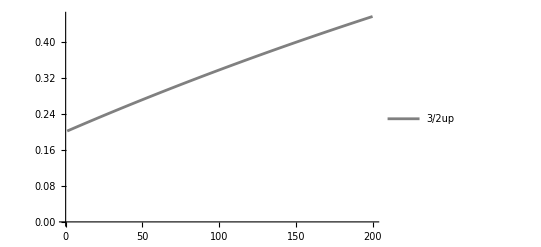

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

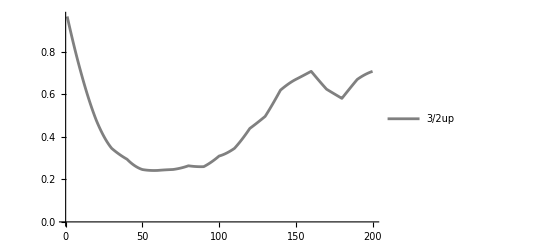

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.970012,0.940413,0.911204,0.882386,0.853967,0.825953,0.798356,0.771188,0.744464,0.7182,0.692415,0.667128,0.642361,0.618137,0.594479,0.571412,0.548961,0.527153,0.506014,0.485571,0.465852,0.446885,0.428697,0.411316,0.394769,0.379084,0.364288,0.350406,0.337465,0.32549,0.314506,0.304537,0.295604,0.28773,0.280937,0.275243,0.270667,0.267228,0.26494,0.263819,0.263879,0.265131,0.267586,0.271254,0.276142,0.282256,0.289602,0.298181,0.307996,0.319047,0.331331,0.344845,0.359584,0.375541,0.392708,0.411075,0.430631,0.451361,0.473252,0.496286,0.520446,0.545712,0.572063,0.599476,0.627927,0.657391,0.687841,0.719248,0.751584,0.784816,0.818913,0.853841,0.889566,0.926053,0.963264,1.00116,1.03971,1.07886,1.11859,1.15884,1.19958,1.24076,1.28234,1.32427,1.36652,1.40904,1.45178,1.4947,1.53775,1.58089,1.62407,1.66724,1.71036,1.75339,1.79627,1.83897,1.88143,1.92361,1.96547,2.00696,2.04803,2.08864,2.12874,2.16829,2.20724,2.24553,2.28311,2.31993,2.35591,2.39096,2.42496,2.45772,2.48891,2.51787,2.54301,2.55986,2.55719,2.52715,2.48116,2.4295,2.37595,2.32193,2.26806,2.21467,2.16198,2.11014,2.05927,2.00946,1.9608,1.91336,1.86721,1.82242,1.77905,1.73715,1.69677,1.65797,1.62079,1.58527,1.55146,1.51938,1.48907,1.46056,1.43388,1.40905,1.38609,1.36503,1.34587,1.32863,1.31331,1.29993,1.28848,1.27897,1.27139,1.26574,1.262,1.26018,1.26024,1.26218,1.26598,1.27161,1.27904,1.28826,1.29923,1.31191,1.32628,1.34229,1.3599,1.37908,1.39978,1.42196,1.44555,1.47052,1.49682,1.52438,1.55315,1.58307,1.61409,1.64613,1.67913,1.71303,1.74773,1.78318,1.81926,1.85587,1.89287,1.93008,1.96719,2.00371,2.03856,2.06925,2.09008,2.09442,2.0848,2.06845,2.04931,2.02901,2.00824,1.98735,1.96653,1.94589}

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.969193,0.938692,0.908504,0.87864,0.849109,0.819925,0.791105,0.762665,0.734626,0.707009,0.679836,0.653131,0.62692,0.601229,0.576086,0.551519,0.527556,0.504228,0.481565,0.459597,0.438356,0.417872,0.398176,0.379299,0.361272,0.344126,0.327891,0.312597,0.298273,0.284948,0.27265,0.261406,0.251243,0.242186,0.234259,0.227486,0.22189,0.217491,0.21431,0.212364,0.212688,0.213012,0.213337,0.213661,0.213985,0.214309,0.214634,0.214959,0.215284,0.215609,0.215934,0.21626,0.216586,0.216912,0.217239,0.217566,0.217893,0.218222,0.21855,0.218879,0.219209,0.219539,0.21987,0.220202,0.220534,0.220867,0.221201,0.221536,0.221871,0.222207,0.222544,0.222882,0.223221,0.223561,0.223902,0.224244,0.224587,0.22493,0.225275,0.225621,0.225968,0.226317,0.226666,0.227017,0.227368,0.227721,0.228076,0.228431,0.228788,0.229146,0.229505,0.229866,0.230228,0.230592,0.230956,0.231323,0.23169,0.232059,0.23243,0.232802,0.233175,0.23355,0.233926,0.234304,0.234683,0.235064,0.235446,0.23583,0.236216,0.236602,0.236991,0.237381,0.237772,0.238165,0.23856,0.238956,0.239354,0.239753,0.240154,0.240557,0.240961,0.241366,0.241773,0.242182,0.242592,0.243004,0.243417,0.243832,0.244248,0.244666,0.245085,0.245506,0.245928,0.246352,0.246777,0.247204,0.247632,0.248061,0.248492,0.248924,0.249358,0.249793,0.25023,0.250668,0.251107,0.251547,0.251989,0.252432,0.252876,0.253322,0.253768,0.254216,0.254665,0.255116,0.255567,0.25602,0.256473,0.256928,0.257383,0.25784,0.258298,0.258756,0.259216,0.259676,0.260138,0.2606,0.261063,0.261527,0.261992,0.262457,0.262923,0.26339,0.263858,0.264326,0.264794,0.265264,0.265734,0.266204,0.266675,0.267146,0.267618,0.26809,0.268563,0.269036,0.269509,0.269982,0.270456,0.27093,0.271404,0.271878,0.272352,0.272827,0.273301,0.273776,0.27425,0.274724,0.275199,0.275673,0.276147,0.276621}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.969064,0.938427,0.908095,0.878078,0.848389,0.819042,0.790052,0.761439,0.733223,0.705425,0.678068,0.651177,0.624778,0.598898,0.573564,0.548806,0.524653,0.501135,0.478283,0.456128,0.4347,0.414032,0.394155,0.3751,0.356899,0.339583,0.323181,0.307726,0.293245,0.279769,0.267326,0.255944,0.245649,0.236467,0.228423,0.221542,0.215845,0.211355,0.208092,0.206074,0.20532,0.205845,0.207664,0.210791,0.215238,0.221014,0.228128,0.236586,0.246395,0.257558,0.270075,0.283948,0.299174,0.31575,0.333671,0.352929,0.373515,0.395419,0.418627,0.443126,0.468899,0.495929,0.524195,0.553676,0.584348,0.616187,0.649165,0.683255,0.718427,0.754648,0.791885,0.830104,0.869269,0.909341,0.950282,0.992051,1.03461,1.0779,1.1219,1.16655,1.2118,1.25762,1.30394,1.35072,1.39792,1.44547,1.49332,1.54142,1.58972,1.63816,1.68669,1.73524,1.78376,1.83219,1.88046,1.92852,1.97629,2.0237,2.07068,2.11714,2.16298,2.20807,2.25225,2.29529,2.33681,2.37616,2.41203,2.44145,2.45735,2.44733,2.40744,2.34941,2.28329,2.2136,2.14228,2.07026,1.99809,1.92611,1.85456,1.78364,1.71351,1.64431,1.57617,1.50922,1.44356,1.37931,1.31657,1.25543,1.19599,1.13835,1.08258,1.02878,0.977012,0.927367,0.879913,0.83472,0.791854,0.751374,0.713341,0.677807,0.644823,0.614434,0.586682,0.561606,0.539239,0.51961,0.502744,0.488662,0.477381,0.468913,0.463265,0.460442,0.460441,0.463259,0.468885,0.477305,0.488501,0.502451,0.519128,0.5385,0.560532,0.585185,0.612414,0.642173,0.674409,0.709067,0.746085,0.785401,0.826944,0.870644,0.916422,0.964196,1.01388,1.06538,1.1186,1.17342,1.22973,1.28739,1.34624,1.40608,1.46664,1.52755,1.58818,1.6474,1.70289,1.7495,1.7775,1.77946,1.76146,1.73339,1.70073,1.66592,1.6301,1.59386,1.55753,1.52135,1.48545,1.44994,1.4149,1.3804}

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.968789,0.93788,0.907281,0.877,0.847052,0.817449,0.78821,0.759353,0.730898,0.702867,0.675283,0.648172,0.62156,0.595473,0.569941,0.544992,0.520656,0.496963,0.473944,0.451631,0.430055,0.409248,0.389241,0.370066,0.351756,0.33434,0.317851,0.302318,0.287771,0.274241,0.261755,0.250341,0.240027,0.230839,0.222801,0.215938,0.210273,0.205827,0.202621,0.200673,0.200003,0.200624,0.202554,0.205804,0.210388,0.216314,0.223591,0.232226,0.242224,0.253589,0.266322,0.280423,0.29589,0.312718,0.330904,0.350439,0.371313,0.393517,0.417036,0.441856,0.46796,0.495331,0.523948,0.553788,0.584828,0.617043,0.650405,0.684886,0.720454,0.757078,0.794723,0.833355,0.872936,0.913429,0.954792,0.996985,1.03997,1.08369,1.12811,1.17319,1.21886,1.2651,1.31184,1.35903,1.40663,1.45458,1.50282,1.55131,1.59998,1.64878,1.69766,1.74654,1.79538,1.8441,1.89265,1.94095,1.98894,2.03654,2.08366,2.1302,2.17605,2.22106,2.26502,2.30763,2.3484,2.38643,2.41989,2.44473,2.45238,2.43234,2.38626,2.32551,2.25791,2.1871,2.11475,2.04173,1.96856,1.89557,1.82301,1.75109,1.67997,1.6098,1.54072,1.47284,1.40629,1.34118,1.27762,1.2157,1.15552,1.09719,1.04078,0.986387,0.934093,0.883976,0.836111,0.79057,0.74742,0.706727,0.668549,0.632943,0.59996,0.569648,0.542051,0.517207,0.495152,0.475917,0.459527,0.446004,0.435365,0.427624,0.422787,0.42086,0.42184,0.425724,0.4325,0.442154,0.454667,0.470016,0.488173,0.509105,0.532774,0.55914,0.588157,0.619774,0.653936,0.690583,0.729653,0.771076,0.814778,0.860682,0.908702,0.958748,1.01072,1.06452,1.12003,1.17711,1.23562,1.29539,1.35618,1.41772,1.4796,1.5412,1.60146,1.65847,1.70853,1.74506,1.76069,1.7549,1.73462,1.70647,1.67424,1.63987,1.6044,1.5684,1.53222,1.49611,1.46023,1.42469,1.3896,1.35501}

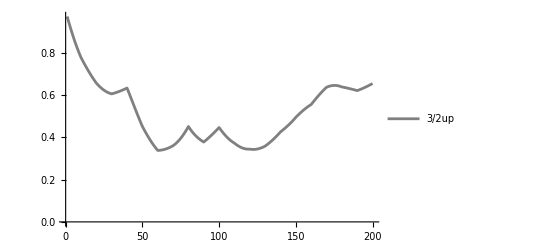

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.969064,0.938427,0.908095,0.878078,0.848389,0.819042,0.790052,0.761439,0.733223,0.705425,0.678068,0.651177,0.624778,0.598898,0.573564,0.548806,0.524653,0.501135,0.478283,0.456128,0.4347,0.414032,0.394155,0.3751,0.356899,0.339583,0.323181,0.307726,0.293245,0.279769,0.267326,0.255944,0.245649,0.236467,0.228423,0.221542,0.215845,0.211355,0.208092,0.206074,0.206221,0.206369,0.206516,0.206663,0.206811,0.206958,0.207106,0.207254,0.207402,0.207551,0.2077,0.207849,0.207998,0.208148,0.208299,0.20845,0.208601,0.208753,0.208905,0.209058,0.209212,0.209366,0.209521,0.209677,0.209833,0.20999,0.210148,0.210307,0.210467,0.210627,0.210789,0.210951,0.211115,0.211279,0.211444,0.211611,0.211778,0.211947,0.212117,0.212288,0.21246,0.212633,0.212807,0.212983,0.21316,0.213338,0.213517,0.213698,0.21388,0.214064,0.214248,0.214434,0.214622,0.214811,0.215002,0.215193,0.215387,0.215582,0.215778,0.215976,0.216175,0.216376,0.216578,0.216782,0.216988,0.217195,0.217403,0.217614,0.217826,0.218039,0.218254,0.218471,0.218689,0.218909,0.21913,0.219353,0.219578,0.219804,0.220032,0.220262,0.220493,0.220725,0.22096,0.221196,0.221433,0.221673,0.221913,0.222156,0.2224,0.222645,0.222892,0.223141,0.223391,0.223643,0.223896,0.224151,0.224408,0.224665,0.224925,0.225185,0.225448,0.225711,0.225977,0.226243,0.226511,0.22678,0.227051,0.227323,0.227596,0.227871,0.228147,0.228424,0.228702,0.228982,0.229263,0.229545,0.229828,0.230112,0.230398,0.230684,0.230972,0.23126,0.23155,0.23184,0.232132,0.232424,0.232718,0.233012,0.233307,0.233603,0.233899,0.234197,0.234495,0.234794,0.235093,0.235394,0.235694,0.235996,0.236298,0.2366,0.236903,0.237207,0.23751,0.237815,0.238119,0.238424,0.238729,0.239035,0.239341,0.239647,0.239953,0.240259,0.240565,0.240872,0.241178,0.241485,0.241791,0.242098,0.242404,0.24271}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/2.5,10^-7]
```

{0.968789,0.93788,0.907281,0.877,0.847052,0.817449,0.78821,0.759353,0.730898,0.702867,0.675283,0.648172,0.62156,0.595473,0.569941,0.544992,0.520656,0.496963,0.473944,0.451631,0.430055,0.409248,0.389241,0.370066,0.351756,0.33434,0.317851,0.302318,0.287771,0.274241,0.261755,0.250341,0.240027,0.230839,0.222801,0.215938,0.210273,0.205827,0.202621,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673,0.200673}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/2.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

```mathematica
AA={2.4287192832945568,2.3581008749698764,2.2881565208455106,2.2189044486696132,2.1503689685480976,2.082580073696849,2.0155730445395568,1.9493880584698569,1.8840698070105006,1.8196671216210984,1.7562326090162166,1.6938222965444023,1.6324952879342922,1.572313429525314,1.5133409869583099,1.455644332197005,1.3992916406778202,1.3443525983364497,1.2908981182303505,1.239000066461855,1.1887309971041526,1.140163895838374,1.093371932022574,1.0484282189303529,1.005405581916821,0.964376334291317,0.9254120606988856,0.8885834078352559,0.853959882342294,0.8216096557524861,0.7915993763713298,0.7639939880056059,0.7388565554632023,0.7162480967661904,0.6962274220335374,0.6788509790028026,0.6641727051716955,0.6522438865503566,0.6431130230238034,0.636825700331177,0.640382404544062,0.6439345186207062,0.6474828675578723,0.6510282764590389,0.6545715701933017,0.6581135730499184,0.6616551083885862,0.6651969982856727,0.668740063176573,0.6722851214943772,0.6758329893050816,0.679384479939539,0.6829404036223603,0.686501567098043,0.6900687732545188,0.6936428207444094,0.6972245036042475,0.7008146108718916,0.7044139262024736,0.70802322748311,0.7116432864467082,0.7152748682851375,0.7189187312620824,0.7225756263259133,0.726246296722842,0.7299314776107475,0.7336318956739514,0.7373482687393209,0.7410813053940037,0.7448317046051627,0.7486001553420492,0.7523873362007674,0.7561939150320875,0.7600205485726561,0.7638678820799689,0.7677365489714649,0.7716271704680939,0.775540355242724,0.7794766990737592,0.7834367845042962,0.7874211805072027,0.7914304421564755,0.7954651103051988,0.7995257112704892,0.8036127565257543,0.8077267424005927,0.8118681497887055,0.8160374438641158,0.8202350738060447,0.824461472532735,0.8287170564445612,0.8330022251767097,0.8373173613617322,0.8416628304022469,0.8460389802540664,0.8504461412200346,0.8548846257548108,0.8593547282808234,0.863856725015697,0.8683908738112809,0.8729574140045773,0.8775565662806941,0.8821885325480441,0.8868534958259535,0.8915516201448415,0.896283050459084,0.9010479125727326,0.9058463130781638,0.9106783393077817,0.9155440592988411,0.9204435217714737,0.9253767561199497,0.9303437724172321,0.9353445614328302,0.9403790946639656,0.9454473243800368,0.9505491836803461,0.9556845865650776,0.9608534280194148,0.9660555841107845,0.971290912099088,0.9765592505598457,0.9818604195201068,0.9871942206070305,0.9925604372089256,0.9979588346486481,1.003389160369125,1.0088511441308574,1.014344498221131,1.019868917674783,1.025424080506237,1.0310096479525925,1.036625264727478,1.0422705592854205,1.0479451440964493,1.0536486159305953,1.0593805561520666,1.0651405310226814,1.0709280920143027,1.0767427761299535,1.0825841062331913,1.0884515913854687,1.0943447271911055,1.1002629961494632,1.1062058680140283,1.1121728001579516,1.118163237945736,1.1241766151106165,1.1302123541372961,1.1362698666496485,1.142348553802941,1.1484478066802328,1.1545670066925542,1.1607055259824133,1.1668627278303014,1.1730379670637636,1.179230590468633,1.1854399372020645,1.1916653392069403,1.1979061216272937,1.204161603224338,1.21043109679275,1.2167139095767734,1.223009343685856,1.2293166965093696,1.2356352611301014,1.2419643267361615,1.2483031790309362,1.2546511006407557,1.261007371519959,1.2673712693530081,1.2737420699533524,1.280119047658728,1.28650147572259,1.2928886267014024,1.2992797728375054,1.305674186437248,1.3120711402441922,1.318469907807108,1.3248697638424995,1.3312699845914726,1.337669848170704,1.3440686349173077,1.350465627727409,1.3568601123882464,1.3632513779036155,1.3696387168124935,1.3760214255007162,1.3823988045055535,1.3887701588130286,1.3951347981479354,1.4014920372563768,1.4078411961807569,1.414181600527166,1.420512581725109,1.426833477279307,1.4331436310139694,1.4394423933089535,1.4457291213282195,1.4520031792403154};
```

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

```mathematica
BB={2.4287192832945568,2.3581008749698764,2.2881565208455106,2.2189044486696132,2.1503689685480976,2.082580073696849,2.0155730445395568,1.9493880584698569,1.8840698070105006,1.8196671216210984,1.7562326090162166,1.6938222965444023,1.6324952879342922,1.572313429525314,1.5133409869583099,1.455644332197005,1.3992916406778202,1.3443525983364497,1.2908981182303505,1.239000066461855,1.1887309971041526,1.140163895838374,1.093371932022574,1.0484282189303529,1.005405581916821,0.964376334291317,0.9254120606988856,0.8885834078352559,0.853959882342294,0.8216096557524861,0.7915993763713298,0.7639939880056059,0.7388565554632023,0.7162480967661904,0.6962274220335374,0.6788509790028026,0.6641727051716955,0.6522438865503566,0.6431130230238034,0.636825700331177,0.6334244686742978,0.6329487279726664,0.6354346197855536,0.6409149259241174,0.6494189737779488,0.660972548380709,0.6755978112391459,0.6933132259483052,0.7141334906138654,0.7380694770995087,0.7651281771139766,0.795312655148364,0.8286220082696163,0.8650513327711389,0.9045916976759374,0.9472301250817292,0.9929495773312293,1.0417289509841554,1.093543077560561,1.1483627310180307,1.2061546419177143,1.2668815182266844,1.330502072696314,1.3969710567482965,1.4662393007920809,1.5382537608890647,1.6129575716708233,1.6902901054100727,1.770187037134737,1.8525804156668313,1.9373987404592814,2.0245670440949155,2.1140069803030785,2.2056369173400387,2.299372036570074,2.3951244360743402,2.4928032391044406,2.592314707186685,2.693562357671369,2.7964470855083556,2.900867289015674,3.006718999391043,3.113896013696168,3.2222900310195985,3.331790791493799,3.442286217803831,3.5536625587752386,3.665804534562629,3.778595482870771,3.891917505516456,4.005651614465715,4.119677876232679,4.233875553164934,4.348123239604197,4.462298990100252,4.5762804356034135,4.689944881580276,4.803169378786143,4.9158307520715345,5.027805563379966,5.138969968643915,5.2491993977074625,5.3583679268056645,5.46634709033735,5.573003608391755,5.678194861991566,5.781759250548555,5.88349348862491,5.983090897404586,6.079933457034303,6.1720933278698835,6.246887330671213,6.199099298884955,6.050356465329387,5.890838984208667,5.729825047466961,5.569023533701191,5.4090964435896165,5.25043809636735,5.09334771434622,4.938082400548058,4.784876999047431,4.633952590012424,4.4855204552402945,4.339784027754484,4.1969398651617595,4.057178118277411,3.920682725334875,3.78763145141625,3.6581958385663893,3.5325411040542347,3.410826009083515,3.293202711705074,3.179816612686393,3.0708062000791045,2.9663028963527522,2.866430910768722,2.771307098887021,2.681040830575148,2.595733867529265,2.515480251065588,2.4403662007583704,2.370470024366902,2.3058620393923666,2.246604506526483,2.192751575190619,2.1443492413121676,2.101435317441084,2.0640394152715777,2.0321829406003435,2.0058791007223755,1.9851329242375244,1.9699412932149025,1.9602929876377502,1.9561687420277947,1.9575413141256495,1.964375565481769,1.976628553791016,1.994249636782711,2.0171805874569024,2.045355720436391,2.0787020291824074,2.117139333799434,2.1605804391310572,2.208931302823095,2.2620912130017024,2.3199529751813146,2.3824031079777823,2.4493220471532546,2.520584357455883,2.59605895163262,2.6756093158754344,2.759093740792159,2.8463655567433026,2.937273372006131,3.031661311632754,3.1293692539113227,3.230233059749473,3.3340847875702053,3.440752881451494,3.5500623112233747,3.661834625682815,3.7758878439602044,3.8920360306286472,4.010088210842057,4.1298457833186,4.251096096833461,4.373594548863538,4.497003369532637,4.6205900296838465,4.739814251489037,4.757303104596868,4.678887342353419,4.596575209508372,4.514391926679284,4.432942114161442,4.352456567183306,4.273078665433483,4.194903870055487,4.118035183941553};
```

```mathematica
ListPlot[{AA,BB}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
|
```

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
N[Pi/2*13/50]
```

0.408407

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]3
```

-Graphics-

```mathematica
SqueezeListBox[[1,1]]/(5/2)
```

{0.976014+6.6408×10^-17 ⅈ,0.953378+5.74927×10^-17 ⅈ,0.932106+7.67646×10^-17 ⅈ,0.912216+6.04711×10^-17 ⅈ,0.89372+9.26067×10^-18 ⅈ,0.876633+6.46977×10^-17 ⅈ,0.860965+1.4481×10^-16 ⅈ,0.846728+1.12318×10^-16 ⅈ,0.833932+2.81371×10^-16 ⅈ,0.822586+1.67019×10^-16 ⅈ,0.812698+1.87067×10^-16 ⅈ,0.804276+2.74108×10^-16 ⅈ,0.797328+2.74898×10^-16 ⅈ,0.791859+3.24054×10^-16 ⅈ,0.787875+3.93217×10^-16 ⅈ,0.785383+4.58838×10^-16 ⅈ,0.784387+4.90523×10^-16 ⅈ,0.784892+5.73411×10^-16 ⅈ,0.786903+6.14428×10^-16 ⅈ,0.790422+6.04623×10^-16 ⅈ,0.795455+7.41013×10^-16 ⅈ,0.802003+6.26854×10^-16 ⅈ,0.810068+7.45452×10^-16 ⅈ,0.819653+8.32548×10^-16 ⅈ,0.830757+9.62432×10^-16 ⅈ,0.843381+9.59856×10^-16 ⅈ,0.857522+1.21177×10^-15 ⅈ,0.873176+1.30123×10^-15 ⅈ,0.890337+1.3707×10^-15 ⅈ,0.908998+1.57812×10^-15 ⅈ,0.929147+1.67422×10^-15 ⅈ,0.950769+1.65172×10^-15 ⅈ,0.973846+1.64764×10^-15 ⅈ,0.998354+1.57643×10^-15 ⅈ,1.02426+1.75542×10^-15 ⅈ,1.05154+1.79767×10^-15 ⅈ,1.08013+2.02692×10^-15 ⅈ,1.11+1.82424×10^-15 ⅈ,1.14107+2.17884×10^-15 ⅈ,1.17329+2.04641×10^-15 ⅈ,1.20655+2.03465×10^-15 ⅈ,1.24078+2.14318×10^-15 ⅈ,1.27585+2.04486×10^-15 ⅈ,1.31164+2.06529×10^-15 ⅈ,1.34801+2.08692×10^-15 ⅈ,1.38481+2.1305×10^-15 ⅈ,1.42187+2.02553×10^-15 ⅈ,1.45899+1.83634×10^-15 ⅈ,1.49598+1.77207×10^-15 ⅈ,1.53262+1.39914×10^-15 ⅈ,1.5687+1.12957×10^-15 ⅈ,1.60398+1.25386×10^-15 ⅈ,1.63822+8.47125×10^-16 ⅈ,1.67121+5.87678×10^-16 ⅈ,1.70272+2.41706×10^-16 ⅈ,1.73255+4.1279×10^-17 ⅈ,1.76051-3.23895×10^-16 ⅈ,1.78643-6.96384×10^-16 ⅈ,1.81019-8.85433×10^-16 ⅈ,1.83167-1.32049×10^-15 ⅈ,1.83167-1.28116×10^-15 ⅈ,1.83167-1.3017×10^-15 ⅈ,1.83167-1.18585×10^-15 ⅈ,1.83167-1.17436×10^-15 ⅈ,1.83167-1.22287×10^-15 ⅈ,1.83167-1.27653×10^-15 ⅈ,1.83167-1.19273×10^-15 ⅈ,1.83167-1.16959×10^-15 ⅈ,1.83167-1.00612×10^-15 ⅈ,1.83167-9.30148×10^-16 ⅈ,1.83167-1.18781×10^-15 ⅈ,1.83167-1.10111×10^-15 ⅈ,1.83167-1.0192×10^-15 ⅈ,1.83167-1.23568×10^-15 ⅈ,1.83167-1.26892×10^-15 ⅈ,1.83167-1.03131×10^-15 ⅈ,1.83167-9.50258×10^-16 ⅈ,1.83167-1.01591×10^-15 ⅈ,1.83167-1.15969×10^-15 ⅈ,1.83167-1.26636×10^-15 ⅈ,1.83167-1.41372×10^-15 ⅈ,1.83167-1.14622×10^-15 ⅈ,1.83167-1.39899×10^-15 ⅈ,1.83167-1.57753×10^-15 ⅈ,1.83167-1.53634×10^-15 ⅈ,1.83167-1.60315×10^-15 ⅈ,1.83167-1.6392×10^-15 ⅈ,1.83167-1.9774×10^-15 ⅈ,1.83167-1.97691×10^-15 ⅈ,1.83167-1.79393×10^-15 ⅈ,1.83167-1.88054×10^-15 ⅈ,1.83167-2.20952×10^-15 ⅈ,1.83167-2.031×10^-15 ⅈ,1.83167-2.00824×10^-15 ⅈ,1.83167-2.13016×10^-15 ⅈ,1.83167-2.21925×10^-15 ⅈ,1.83167-2.35642×10^-15 ⅈ,1.83167-2.61372×10^-15 ⅈ,1.83167-2.69159×10^-15 ⅈ,1.83167-2.64962×10^-15 ⅈ,1.83167-2.423×10^-15 ⅈ,1.83167-2.54177×10^-15 ⅈ,1.83167-2.60698×10^-15 ⅈ,1.83167-2.76218×10^-15 ⅈ,1.83167-2.77992×10^-15 ⅈ,1.83167-2.94337×10^-15 ⅈ,1.83167-3.06464×10^-15 ⅈ,1.83167-3.03636×10^-15 ⅈ,1.83167-3.15584×10^-15 ⅈ,1.83167-3.31574×10^-15 ⅈ,1.83167-3.6617×10^-15 ⅈ,1.83167-3.57923×10^-15 ⅈ,1.83167-3.75698×10^-15 ⅈ,1.83167-4.00977×10^-15 ⅈ,1.83167-4.03563×10^-15 ⅈ,1.83167-4.53874×10^-15 ⅈ,1.83167-4.4935×10^-15 ⅈ,1.83167-4.68806×10^-15 ⅈ,1.83167-4.90298×10^-15 ⅈ,1.83167-5.1006×10^-15 ⅈ,1.83167-5.03143×10^-15 ⅈ,1.83167-5.10102×10^-15 ⅈ,1.83167-5.28939×10^-15 ⅈ,1.83167-5.27306×10^-15 ⅈ,1.83167-5.37143×10^-15 ⅈ,1.83167-5.42726×10^-15 ⅈ,1.83167-5.61434×10^-15 ⅈ,1.83167-5.798×10^-15 ⅈ,1.83167-6.24527×10^-15 ⅈ,1.83167-6.27067×10^-15 ⅈ,1.83167-6.22421×10^-15 ⅈ,1.83167-6.51098×10^-15 ⅈ,1.83167-6.55191×10^-15 ⅈ,1.83167-6.65774×10^-15 ⅈ,1.83167-6.9997×10^-15 ⅈ,1.83167-6.97755×10^-15 ⅈ,1.83167-7.21093×10^-15 ⅈ,1.83167-7.76268×10^-15 ⅈ,1.83167-7.3907×10^-15 ⅈ,1.83167-7.93361×10^-15 ⅈ,1.83167-8.05509×10^-15 ⅈ,1.83167-8.11722×10^-15 ⅈ,1.83167-8.19745×10^-15 ⅈ,1.83167-8.47406×10^-15 ⅈ,1.83167-8.45528×10^-15 ⅈ,1.83167-8.86478×10^-15 ⅈ,1.83167-8.96222×10^-15 ⅈ,1.83167-8.93941×10^-15 ⅈ,1.83167-8.82417×10^-15 ⅈ,1.83167-8.93676×10^-15 ⅈ,1.83167-9.1069×10^-15 ⅈ,1.83167-9.40445×10^-15 ⅈ,1.83167-9.76712×10^-15 ⅈ,1.83167-9.50348×10^-15 ⅈ,1.83167-9.78269×10^-15 ⅈ,1.83167-9.87656×10^-15 ⅈ,1.83167-1.00179×10^-14 ⅈ,1.83167-9.94995×10^-15 ⅈ,1.83167-9.99003×10^-15 ⅈ,1.83167-1.00684×10^-14 ⅈ,1.83167-1.04733×10^-14 ⅈ,1.83167-1.04396×10^-14 ⅈ,1.83167-1.03055×10^-14 ⅈ,1.83167-1.04758×10^-14 ⅈ,1.83167-1.06441×10^-14 ⅈ,1.83167-1.08323×10^-14 ⅈ,1.83167-1.10282×10^-14 ⅈ,1.83167-1.09485×10^-14 ⅈ,1.83167-1.09446×10^-14 ⅈ,1.83167-1.09556×10^-14 ⅈ,1.83167-1.1081×10^-14 ⅈ,1.83167-1.12445×10^-14 ⅈ,1.83167-1.13592×10^-14 ⅈ,1.83167-1.12584×10^-14 ⅈ,1.83167-1.1277×10^-14 ⅈ,1.83167-1.12831×10^-14 ⅈ,1.83167-1.13032×10^-14 ⅈ,1.83167-1.12249×10^-14 ⅈ,1.83167-1.1428×10^-14 ⅈ,1.83167-1.12341×10^-14 ⅈ,1.83167-1.12063×10^-14 ⅈ,1.83167-1.11228×10^-14 ⅈ,1.83167-1.1247×10^-14 ⅈ,1.83167-1.13297×10^-14 ⅈ,1.83167-1.12951×10^-14 ⅈ,1.83167-1.13955×10^-14 ⅈ,1.83167-1.12266×10^-14 ⅈ,1.83167-1.11213×10^-14 ⅈ,1.83167-1.13533×10^-14 ⅈ,1.83167-1.11414×10^-14 ⅈ,1.83167-1.11042×10^-14 ⅈ,1.83167-1.11202×10^-14 ⅈ,1.83167-1.11559×10^-14 ⅈ,1.83167-1.10388×10^-14 ⅈ,1.83167-1.09195×10^-14 ⅈ,1.83167-1.09737×10^-14 ⅈ,1.83167-1.09048×10^-14 ⅈ,1.83167-1.07782×10^-14 ⅈ,1.83167-1.11436×10^-14 ⅈ,1.83167-1.10965×10^-14 ⅈ}

```mathematica
SqueezeListBox[[1,1]]/(5/2)
```

{0.978348+0.00370753 ⅈ,0.957928+0.00757618 ⅈ,0.938764+0.0116115 ⅈ,0.920887+0.0158203 ⅈ,0.904326+0.0202105 ⅈ,0.889116+0.0247914 ⅈ,0.875296+0.0295733 ⅈ,0.862904+0.0345679 ⅈ,0.851983+0.039788 ⅈ,0.842576+0.0452477 ⅈ,0.834731+0.0509625 ⅈ,0.828495+0.0569487 ⅈ,0.823916+0.0632243 ⅈ,0.821044+0.0698079 ⅈ,0.819929+0.0767198 ⅈ,0.820621+0.0839809 ⅈ,0.823169+0.0916133 ⅈ,0.827623+0.0996401 ⅈ,0.834028+0.108085 ⅈ,0.84243+0.116972 ⅈ,0.852869+0.126327 ⅈ,0.865384+0.136174 ⅈ,0.880008+0.146539 ⅈ,0.896767+0.157447 ⅈ,0.915684+0.16892 ⅈ,0.936772+0.180984 ⅈ,0.960034+0.193659 ⅈ,0.985464+0.206964 ⅈ,1.01305+0.220916 ⅈ,1.04275+0.235528 ⅈ,1.07452+0.250808 ⅈ,1.10831+0.266759 ⅈ,1.14404+0.283376 ⅈ,1.1816+0.300647 ⅈ,1.22088+0.318547 ⅈ,1.26173+0.337042 ⅈ,1.30401+0.356081 ⅈ,1.34753+0.375598 ⅈ,1.3921+0.395508 ⅈ,1.43749+0.41571 ⅈ,1.48348+0.43608 ⅈ,1.52983+0.456478 ⅈ,1.5763+0.476747 ⅈ,1.62263+0.496714 ⅈ,1.66858+0.516198 ⅈ,1.71389+0.535004 ⅈ,1.75832+0.552934 ⅈ,1.80162+0.569788 ⅈ,1.84357+0.58536 ⅈ,1.88393+0.59945 ⅈ,1.92252+0.611857 ⅈ,1.95913+0.622384 ⅈ,1.99359+0.63084 ⅈ,2.02575+0.637035 ⅈ,2.05549+0.640787 ⅈ,2.0827+0.641914 ⅈ,2.10724-0.242782 ⅈ,2.11468-0.233234 ⅈ,2.12161-0.221635 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.07326-0.805222 ⅈ}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[ξtopF[MatrixExp[-I*Ix3half2*Pi/2].DMevolve[[1,1]].MatrixExp[+I*Ix3half2*Pi/2]]]
```

Flatten::normal: Flatten[0.332823+1.38778×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.726683-6.43068×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.597188+5.53063×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.672397

```mathematica
DMevolve[[1,1]]
```

{{0.0549372-1.10954×10^-16 ⅈ,-0.0789447-0.0259826 ⅈ,-0.0628249+0.135289 ⅈ,-0.0162147+0.0431125 ⅈ},{-0.0789447+0.0259826 ⅈ,0.173517-9.37621×10^-16 ⅈ,0.102717-0.262559 ⅈ,0.0381837-0.103942 ⅈ},{-0.0628249-0.135289 ⅈ,0.102717+0.262559 ⅈ,0.655331+2.30254×10^-15 ⅈ,0.242912-0.0552429 ⅈ},{-0.0162147-0.0431125 ⅈ,0.0381837+0.103942 ⅈ,0.242912+0.0552429 ⅈ,0.116214-1.21011×10^-15 ⅈ}}

```mathematica
MatrixExp[-I*Ix3half2*Pi/2].DMevolve[[1,1]].MatrixExp[+I*Ix3half2*Pi/2]
```

{{0.585751+1.51268×10^-15 ⅈ,0.076817-0.106961 ⅈ,0.210952-0.280544 ⅈ,0.00198419-0.216759 ⅈ},{0.076817+0.106961 ⅈ,0.0943153+2.46331×10^-16 ⅈ,0.0845181-0.00649014 ⅈ,0.0615183-0.041313 ⅈ},{0.210952+0.280544 ⅈ,0.0845181+0.00649014 ⅈ,0.21992-1.7486×10^-15 ⅈ,0.108164-0.0777004 ⅈ},{0.00198419+0.216759 ⅈ,0.0615183+0.041313 ⅈ,0.108164+0.0777004 ⅈ,0.100013+2.08167×10^-17 ⅈ}}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980159,0.960493,0.941014,0.921732,0.902659,0.883805,0.865179,0.846792,0.828652,0.810769,0.793152,0.775808,0.758746,0.741974,0.7255,0.709329,0.69347,0.677928,0.66271,0.647821,0.633268,0.619055,0.605188,0.59167,0.578506,0.565701,0.553257,0.541177,0.529466,0.518126,0.507158,0.496566,0.486351,0.476515,0.467058,0.457983,0.44929,0.44098,0.433053,0.425509,0.418349,0.411573,0.405181,0.399172,0.393546,0.388304,0.383444,0.378967,0.374873,0.371161,0.367831,0.364883,0.362318,0.360136,0.358338,0.356923,0.355894,0.355251,0.354995,0.355127,0.355349,0.355569,0.355788,0.356006,0.356224,0.35644,0.356657,0.356873,0.357089,0.357305,0.357521,0.357737,0.357954,0.358171,0.35839,0.358609,0.358829,0.35905,0.359273,0.359497,0.359723,0.35995,0.36018,0.360411,0.360645,0.360881,0.36112,0.361361,0.361605,0.361852,0.362102,0.362356,0.362612,0.362872,0.363136,0.363403,0.363674,0.36395,0.364229,0.364512,0.3648,0.365092,0.365389,0.365691,0.365997,0.366309,0.366625,0.366946,0.367273,0.367605,0.367943,0.368286,0.368634,0.368989,0.369349,0.369715,0.370088,0.370466,0.37085,0.371241,0.371638,0.372042,0.372451,0.372868,0.373291,0.373721,0.374157,0.3746,0.37505,0.375507,0.375971,0.376442,0.37692,0.377405,0.377897,0.378396,0.378902,0.379415,0.379936,0.380464,0.380999,0.381541,0.382091,0.382648,0.383212,0.383783,0.384362,0.384948,0.385541,0.386141,0.386749,0.387364,0.387985,0.388615,0.389251,0.389894,0.390545,0.391202,0.391866,0.392538,0.393216,0.393901,0.394593,0.395291,0.395997,0.396708,0.397427,0.398152,0.398883,0.39962,0.400364,0.401114,0.40187,0.402633,0.403401,0.404175,0.404954,0.405739,0.40653,0.407327,0.408128,0.408935,0.409747,0.410564,0.411386,0.412213,0.413045,0.413881,0.414721,0.415566,0.416415,0.417269,0.418126,0.418987,0.419852,0.42072,0.421592,0.422467,0.423346,0.424227,0.425111,0.425999,0.426888,0.427781,0.428675,0.429572,0.430471,0.431372,0.432275,0.43318}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980744,0.961714,0.942919,0.924372,0.906081,0.888057,0.870309,0.852846,0.835678,0.818812,0.802256,0.78602,0.770109,0.754531,0.739293,0.724402,0.709863,0.695682,0.681865,0.668417,0.655343,0.642647,0.630332,0.618403,0.606864,0.595716,0.584963,0.574607,0.56465,0.555092,0.545937,0.537183,0.528832,0.520884,0.513338,0.506194,0.49945,0.493106,0.487159,0.481608,0.476449,0.471682,0.467301,0.463304,0.459688,0.456449,0.453583,0.451085,0.448952,0.447179,0.445761,0.444694,0.443973,0.443595,0.443554,0.443845,0.444466,0.445412,0.446679,0.448265,0.449416,0.450581,0.45176,0.452954,0.454164,0.455391,0.456636,0.4579,0.459184,0.460489,0.461816,0.463166,0.464539,0.465936,0.467359,0.468808,0.470283,0.471787,0.473318,0.474879,0.476469,0.47809,0.479742,0.481426,0.483142,0.484891,0.486673,0.48849,0.490341,0.492227,0.494148,0.496105,0.498098,0.500128,0.502194,0.504298,0.506439,0.508618,0.510835,0.513089,0.515382,0.517713,0.520083,0.522491,0.524937,0.527422,0.529945,0.532507,0.535106,0.537744,0.54042,0.543134,0.545886,0.548675,0.551501,0.554363,0.557263,0.560198,0.563169,0.566176,0.569218,0.572294,0.575404,0.578548,0.581725,0.584935,0.588177,0.59145,0.594753,0.598087,0.601412,0.604688,0.607915,0.611095,0.614227,0.617313,0.620353,0.623346,0.626295,0.629199,0.632058,0.634874,0.637647,0.640377,0.643065,0.645711,0.648316,0.650881,0.653406,0.655891,0.658337,0.660745,0.663115,0.665447,0.667743,0.670002,0.672225,0.674414,0.676567,0.678686,0.680772,0.682824,0.684844,0.686831,0.688787,0.690712,0.692606,0.69447,0.696305,0.698111,0.699888,0.701637,0.703359,0.705053,0.706722,0.708364,0.709981,0.711573,0.71314,0.714684,0.716204,0.717701,0.719176,0.720629,0.722061,0.723471,0.724861,0.726232,0.727583,0.728915,0.730228,0.731524,0.732802,0.734063,0.735308,0.736537,0.737751,0.73895,0.740134,0.741304,0.742461,0.743605,0.744736,0.745856,0.746964,0.748061,0.749148,0.750225,0.751292,0.75235}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980744,0.961714,0.942919,0.924372,0.906081,0.888057,0.870309,0.852846,0.835678,0.818812,0.802256,0.78602,0.770109,0.754531,0.739293,0.724402,0.709863,0.695682,0.681865,0.668417,0.655343,0.642647,0.630332,0.618403,0.606864,0.595716,0.584963,0.574607,0.56465,0.555092,0.545937,0.537183,0.528832,0.520884,0.513338,0.506194,0.49945,0.493106,0.487159,0.481608,0.476449,0.471682,0.467301,0.463304,0.459688,0.456449,0.453583,0.451085,0.448952,0.447179,0.445761,0.444694,0.443973,0.443595,0.443554,0.443845,0.444466,0.445412,0.446679,0.448265,0.449404,0.450532,0.45165,0.452758,0.453857,0.454948,0.456032,0.457109,0.45818,0.459246,0.460308,0.461367,0.462423,0.463477,0.46453,0.465583,0.466637,0.467692,0.468749,0.469808,0.470872,0.471939,0.473012,0.474091,0.475176,0.476269,0.47737,0.478479,0.479598,0.480728,0.481868,0.48302,0.484185,0.485363,0.486554,0.48776,0.488982,0.490219,0.491472,0.492743,0.494032,0.495339,0.496665,0.498011,0.499377,0.500764,0.502172,0.503603,0.505056,0.506532,0.508032,0.509556,0.511105,0.51268,0.51428,0.515906,0.517559,0.519239,0.520947,0.522682,0.524446,0.526239,0.52806,0.529911,0.531792,0.533704,0.535645,0.537617,0.53962,0.541655,0.543682,0.545663,0.547601,0.549494,0.551345,0.553153,0.55492,0.556646,0.558332,0.55998,0.561588,0.563159,0.564694,0.566193,0.567656,0.569085,0.570481,0.571844,0.573176,0.574477,0.575748,0.576989,0.578203,0.579389,0.580548,0.581682,0.582792,0.583877,0.58494,0.585981,0.587001,0.588001,0.588981,0.589944,0.590889,0.591818,0.592732,0.593631,0.594516,0.59539,0.596251,0.597102,0.597944,0.598777,0.599602,0.600421,0.601234,0.602042,0.602846,0.603648,0.604447,0.605246,0.606045,0.606845,0.607647,0.608452,0.609261,0.610075,0.610895,0.611722,0.612556,0.613399,0.614251,0.615114,0.615989,0.616875,0.617775,0.618689,0.619618,0.620562,0.621507,0.622437,0.623352,0.624254,0.625142,0.626018,0.626883,0.627737,0.628581,0.629415}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox/1]
```

{{{1.48493,1.46974,1.45442,1.439,1.42347,1.40786,1.39216,1.3764,1.36058,1.34471,1.32881,1.3129,1.29698,1.28106,1.26517,1.24932,1.23352,1.2178,1.20215,1.18662,1.1712,1.15592,1.14079,1.12585,1.11109,1.09655,1.08224,1.06819,1.05441,1.04092,1.02774,1.0149,1.00242,0.990314,0.978606,0.967316,0.956467,0.946078,0.93617,0.926762,0.917876,0.909529,0.901742,0.894531,0.887914,0.881908,0.876528,0.871789,0.867705,0.864287,0.861546,0.859492,0.858133,0.857475,0.857521,0.858276,0.859738,0.861907,0.864779,0.868347,0.872604,0.877538,0.883136,0.889382,0.896257,0.90374,0.911808,0.920434,0.929588,0.93924,0.949353,0.959893,0.970819,0.98209,0.993662,1.00549,1.01753,1.02972,1.04203,1.05439,1.06676,1.07907,1.09129,1.10335,1.1152,1.12679,1.13807,1.14899,1.15949,1.16954,1.17908,1.18809,1.19651,1.20433,1.2115,1.218,1.22382,1.22894,1.23335,1.23705,1.24004,1.24235,1.24398,1.24497,1.24536,1.24518,1.24449,1.24335,1.24183,1.24,1.23794,1.23575,1.23351,1.23131,1.22925,1.22743,1.22594,1.22488,1.22433,1.22437,1.22508,1.22652,1.22877,1.23186,1.23584,1.24073,1.24657,1.25337,1.26112,1.26982,1.27946,1.29001,1.30145,1.31373,1.3268,1.34061,1.35508,1.37012,1.38561,1.40136,1.4171,1.43231,1.44593,1.45586,1.4588,1.45319,1.44149,1.42669,1.41044,1.39352,1.37632,1.35903,1.34177,1.3246,1.30758,1.29074,1.27409,1.25765,1.24145,1.22548,1.20977,1.19431,1.17912,1.16421,1.14957,1.13522,1.12115,1.10738,1.09391,1.08075,1.06789,1.05534,1.04311,1.03119,1.0196,1.00833,0.997381,0.986767,0.976484,0.966535,0.956922,0.947647,0.938712,0.930119,0.921869,0.913964,0.906405,0.899193,0.89233,0.885816,0.879654,0.873843,0.868385,0.863281,0.858531,0.854136,0.850098,0.846416,0.843092,0.840127,0.837521,0.835275,0.833389,0.831865,0.830704,0.829906,0.829473,0.829405,0.829704,0.83037,0.831405,0.83281,0.834587,0.836737,0.839261,0.842162,0.84544,0.849099,0.853139,0.857563,0.862373,0.867572,0.873161,0.879143,0.885521,0.892296,0.899473,0.907053,0.915039,0.923434,0.932241,0.941462,0.9511,0.961158,0.971638,0.982541,0.993871,1.00563,1.01781,1.03043,1.04347,1.05694,1.07084,1.08517,1.09991,1.11508,1.13065,1.14662,1.16298,1.17971,1.19681,1.21424,1.232,1.25004,1.26834,1.28686,1.30556,1.32438,1.34328,1.36218,1.38102,1.39972,1.41819,1.43634,1.45407,1.47128,1.48787,1.50373,1.51876,1.53286,1.54596,1.55797,1.56884,1.57853,1.58702,1.5943,1.60038,1.60529,1.60907,1.61178,1.61346,1.6142,1.61405,1.6131,1.61141,1.60906,1.60612,1.60266,1.59875,1.59444,1.58981,1.58491,1.5798,1.57453,1.56915,1.56372,1.55827,1.55286,1.54753,1.54231,1.53725,1.53239,1.52775,1.52337,1.51929,1.51552,1.51211,1.50908,1.50645,1.50424,1.50247,1.50116,1.50034,1.50001,1.50018,1.50087,1.50209,1.50384,1.50613,1.50896,1.51233,1.51624,1.52069,1.52567,1.53118,1.53722,1.54377,1.55082,1.55836,1.56637,1.57485,1.58378,1.59314,1.60291,1.61307,1.62361,1.6345,1.64572,1.65724,1.66905,1.68111,1.69339,1.70586,1.71849,1.73125,1.74408,1.75695,1.76979,1.78255,1.79514,1.80748,1.81944,1.83089,1.84164,1.85144,1.85998,1.86683,1.87146,1.8732,1.87129,1.86502,1.85388,1.83781,1.81722,1.79288,1.76567,1.73643,1.70584,1.67443,1.64261,1.61066,1.57881,1.5472,1.51595,1.48516,1.45489,1.42518,1.39608,1.3676,1.33978,1.31262,1.28614,1.26035,1.23526,1.21086,1.18716,1.16417,1.14188,1.12028,1.09939,1.0792,1.0597,1.0409,1.02279,1.00536,0.988612,0.972544,0.957148,0.942421,0.928355,0.914946,0.902187,0.890072,0.878593,0.867742,0.857513,0.847896,0.838883,0.830464,0.822628,0.815366,0.808666,0.802517,0.796905,0.791817,0.787241,0.78316,0.77956,0.776424,0.773736,0.771478,0.769632,0.768177,0.767095,0.766365,0.765964,0.765871,0.766063,0.766516,0.767206,0.768107,0.769196,0.770445,0.771829,0.773322,0.774896,0.776526,0.778185,0.779846,0.781483,0.783071,0.784585,0.786,0.787293,0.788442,0.789425,0.790222,0.790814,0.791185,0.791319,0.791201,0.790821,0.790167,0.789232,0.788008,0.786492,0.784682,0.782575,0.780175,0.777483,0.774506,0.771248,0.76772,0.76393,0.75989,0.755612,0.751109,0.746398,0.741493,0.736412,0.731171,0.72579,0.720286,0.714678,0.708987,0.703232,0.697432,0.691609,0.685781,0.67997,0.674195,0.668475,0.662831,0.657282,0.651847,0.646546,0.641396,0.636415,0.631623,0.627037,0.622673,0.618549,0.614682,0.611088,0.607782,0.604781,0.6021,0.599754,0.597758,0.596126}}}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Plot[{Norm[ⅇ^((3 ⅈ t1)/4)/(2 √2)],Norm[-1/2 ⅈ √(3/2) ⅇ^((3 ⅈ t1)/4)],Norm[-1/2 √(3/2) ⅇ^((3 ⅈ t1)/4)],Norm[(ⅈ ⅇ^((3 ⅈ t1)/4))/(2 √2)]},{t1,0,10}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980101,0.960409,0.940929,0.921668,0.902633,0.883829,0.865263,0.84694,0.828866,0.811048,0.793489,0.776197,0.759176,0.742432,0.725969,0.709793,0.69391,0.678322,0.663036,0.648056,0.633363,0.618949,0.604834,0.591034,0.577563,0.564435,0.551659,0.539246,0.527204,0.51554,0.504224,0.493227,0.482555,0.472215,0.462213,0.452554,0.443245,0.434289,0.425692,0.417458,0.40959,0.402093,0.39497,0.388225,0.38186,0.375879,0.370284,0.365077,0.360262,0.355839,0.351811,0.34818,0.344945,0.342109,0.339672,0.337635,0.335997,0.334758,0.333919,0.333479,0.333437,0.333796,0.334557,0.335721,0.337287,0.339253,0.341615,0.344367,0.347504,0.351016,0.354894,0.359129,0.363709,0.36862,0.37385,0.379383,0.385203,0.391293,0.397637,0.404215,0.411007,0.417991,0.425147,0.432452,0.439885,0.447423,0.455043,0.462721,0.470434,0.478158,0.485871,0.493549,0.50117,0.508708,0.51614,0.52344,0.530585,0.537551,0.544315,0.550853,0.557143,0.563161,0.568887,0.5743,0.579381,0.584113,0.588478,0.592461,0.596047,0.599224,0.60198,0.604304,0.606188,0.607624,0.608608,0.609134,0.609202,0.60881,0.607959,0.606654,0.604899,0.6027,0.600065,0.597003,0.593526,0.589646,0.585377,0.580734,0.575735,0.570396,0.564922,0.559507,0.554155,0.548868,0.54365,0.538506,0.533439,0.528453,0.523553,0.518743,0.513892,0.508875,0.503705,0.498393,0.492953,0.4874,0.481746,0.476009,0.470202,0.464342,0.458411,0.452393,0.446312,0.440188,0.434044,0.427903,0.421787,0.415718,0.409718,0.403809,0.398014,0.392355,0.386853,0.381527,0.376398,0.371484,0.366804,0.362377,0.358218,0.354344,0.350769,0.347508,0.344572,0.341971,0.339718,0.337822,0.336292,0.335138,0.334367,0.333987,0.334004,0.334419,0.335227,0.336424,0.338006,0.339967,0.342302,0.345005,0.348069,0.35149,0.355258,0.359366,0.363807,0.368571,0.373649,0.379032,0.384708,0.390666,0.396895,0.403381,0.410116,0.417092,0.424295,0.431714,0.439332,0.447135,0.455107,0.463231,0.471487,0.479857,0.488314,0.496825,0.505361,0.513891,0.522382,0.530798,0.539101,0.547252,0.555209,0.562927,0.570359,0.577453,0.584163,0.590439,0.596232,0.601496,0.606184,0.610254,0.613666,0.616387,0.61839,0.619653,0.620162,0.619913,0.618907,0.617157,0.614679,0.611501,0.607653,0.603174,0.598105,0.59249,0.586377,0.579814,0.57285,0.565533,0.557911,0.55003,0.541936,0.533671,0.525275,0.516788,0.508245,0.499681,0.491128,0.482616,0.474174,0.465826,0.457598,0.449513,0.441591,0.433852,0.426314,0.418994,0.411909,0.405073,0.398499,0.3922,0.386188,0.380474,0.375068,0.36998,0.365217,0.360788,0.356701,0.352962,0.349577,0.346553,0.343894,0.341605,0.339698,0.338179,0.337041,0.336277,0.335878,0.335834,0.336136,0.336771,0.337728,0.338993,0.340553,0.342394,0.344499,0.346854,0.349442,0.352246,0.35525,0.358435,0.361783,0.365277,0.368898,0.372627,0.376445,0.380333,0.384273,0.388245,0.392231,0.396213,0.400171,0.404088,0.407946,0.411728,0.415417,0.418996,0.42245,0.425763,0.428922,0.431912,0.43472,0.437334,0.439742,0.441935,0.443903,0.445636,0.447128,0.448373,0.449365,0.4501,0.450575,0.450787,0.450736,0.450423,0.449849,0.449015,0.447927,0.446587,0.445003,0.44318,0.441127,0.438852,0.436365,0.433676,0.430797,0.427741,0.42452,0.421149,0.417642,0.414013,0.41028,0.406459,0.402566,0.398619,0.394635,0.390632,0.386629,0.382644,0.378696,0.374803,0.370984,0.367258,0.363643,0.360158,0.356822,0.353651,0.350665,0.34788,0.345313,0.342982,0.340901,0.339088,0.33757,0.336364,0.335462,0.334858,0.334544,0.334512,0.334754,0.33526,0.336022,0.33703,0.338272,0.339736,0.341411,0.343285,0.345347,0.347584,0.349983,0.35253,0.355211,0.358012,0.360919,0.363918,0.366992,0.370125,0.373301,0.376501,0.37971,0.382909,0.386081,0.389208,0.392272,0.395254,0.398138,0.400906,0.403542,0.40603,0.408355,0.410502,0.412458,0.414211,0.41575,0.417066,0.418151,0.418998,0.4196,0.419954,0.420058,0.41991,0.419513,0.418868,0.41798,0.416854,0.415499,0.413922,0.412135,0.410148,0.407975,0.405628,0.403123,0.400475,0.3977,0.394814,0.391834,0.388778,0.385662,0.382506,0.379326,0.37614,0.372966,0.369821,0.366721,0.36368,0.360713,0.357835,0.355059,0.352399,0.349869,0.347481,0.345247,0.343181,0.341307,0.339643,0.338185,0.336934,0.335887,0.335042,0.334399,0.333956,0.333712,0.333669,0.333824,0.334171,0.334697,0.335389,0.336236,0.337225,0.338344,0.339581,0.340924,0.342361,0.343879,0.345463,0.347099,0.348775,0.350477,0.352193,0.353911,0.355618,0.357303,0.358956,0.360565,0.362121,0.363613,0.365033,0.366371,0.367621,0.368774,0.369824,0.370765,0.371592,0.372407,0.373319,0.374329,0.37544,0.376655,0.377978,0.379413,0.380962,0.38263,0.384422}

```mathematica
ComplexExpand[ⅇ^((3 ⅈ t1)/4)/(2 √2)]
```

Cos[(3 t1)/4]/(2 √2)+(ⅈ Sin[(3 t1)/4])/(2 √2)

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980101,0.960409,0.940929,0.921668,0.902633,0.883829,0.865263,0.84694,0.828866,0.811048,0.793489,0.776197,0.759176,0.742431,0.725969,0.709793,0.69391,0.678322,0.663036,0.648056,0.633363,0.618949,0.604833,0.591033,0.577563,0.564435,0.551661,0.53925,0.527209,0.515547,0.504233,0.493237,0.482566,0.472227,0.462225,0.452567,0.443258,0.434302,0.425705,0.417471,0.409604,0.40211,0.394992,0.388254,0.381899,0.375929,0.370347,0.365154,0.360353,0.355944,0.351927,0.348303,0.345075,0.342247,0.339819,0.337792,0.336164,0.334931,0.33409,0.333634,0.333557,0.333851,0.334507,0.335515,0.336863,0.33854,0.340532,0.342827,0.34541,0.348264,0.351375,0.354724,0.358295,0.362071,0.366032,0.370161,0.374439,0.378846,0.383363,0.38797,0.392648,0.397376,0.402135,0.406905,0.411665,0.416396,0.421079,0.425693,0.430221,0.434643,0.438943,0.443101,0.447102,0.450928,0.454565,0.457998,0.461212,0.464195,0.466934,0.469419,0.471639,0.473585,0.475249,0.476625,0.477707,0.47849,0.478972,0.47915,0.479023,0.478593,0.477965,0.477249,0.476448,0.475564,0.474603,0.473569,0.472468,0.471306,0.470089,0.468825,0.467519,0.466178,0.46481,0.463424,0.46203,0.460638,0.459258,0.457901,0.456579,0.455301,0.454038,0.452745,0.451414,0.45004,0.448617,0.447138,0.4456,0.443997,0.442327,0.440587,0.438842,0.437166,0.435568,0.434054,0.432634,0.431317,0.430111,0.429025,0.428069,0.427253,0.426491,0.42569,0.424844,0.423947,0.422995,0.421983,0.42091,0.41977,0.418563,0.417286,0.415939,0.414522,0.413034,0.411476,0.409849,0.408154,0.406394,0.404572,0.40269,0.400753,0.398859,0.397105,0.395494,0.39403,0.392715,0.391554,0.39055,0.389708,0.389032,0.388528,0.388104,0.387665,0.38721,0.386741,0.386257,0.385759,0.385249,0.384729,0.384202,0.38367,0.383141,0.382618,0.382104,0.381601,0.381111,0.380637,0.380182,0.379749,0.379343,0.378969,0.37863,0.378331,0.378073,0.377858,0.377689,0.377568,0.377498,0.377483,0.377526,0.377631,0.377803,0.378037,0.378329,0.378673,0.379063,0.379495,0.379964,0.380465,0.380995,0.381549,0.382126,0.382724,0.383335,0.383953,0.384572,0.385186,0.385789,0.386379,0.386949,0.387497,0.38803,0.388562,0.389096,0.389638,0.390192,0.390763,0.391358,0.391983,0.392645,0.393349,0.394103,0.394912,0.395783,0.396725,0.397746,0.398854,0.400058,0.401368,0.402793,0.404341,0.405977,0.407652,0.409356,0.411082,0.412821,0.414565,0.416308,0.418042,0.41976,0.421456,0.423127,0.424768,0.42637,0.427924,0.429422,0.430858,0.432226,0.433519,0.434732,0.435861,0.436903,0.437857,0.438718,0.439483,0.440147,0.440709,0.441168,0.441521,0.44177,0.441913,0.441952,0.441889,0.441725,0.441462,0.441105,0.440655,0.440117,0.439494,0.438793,0.438016,0.437172,0.436265,0.435299,0.434277,0.433202,0.432078,0.43091,0.429703,0.42846,0.427187,0.425919,0.424684,0.423476,0.422291,0.421123,0.419968,0.418822,0.417682,0.416543,0.415403,0.414256,0.413097,0.411928,0.410752,0.40957,0.408388,0.407208,0.406037,0.404881,0.403745,0.402637,0.401559,0.400515,0.39951,0.398548,0.397635,0.396778,0.395983,0.395259,0.394613,0.394053,0.393583,0.393213,0.392951,0.392807,0.39279,0.39291,0.393177,0.3936,0.394191,0.394954,0.395894,0.39702,0.398341,0.399866,0.401603,0.403562,0.40575,0.408174,0.410844,0.4138,0.417077,0.420669,0.42457,0.428775,0.433277,0.438071,0.443148,0.448504,0.45413,0.46001,0.466127,0.472472,0.479034,0.485804,0.492768,0.499917,0.507237,0.514715,0.522336,0.530126,0.538115,0.546295,0.554656,0.563189,0.571884,0.580728,0.58971,0.598816,0.608032,0.617302,0.626553,0.635747,0.644843,0.653794,0.662551,0.671062,0.679269,0.687114,0.694533,0.701369,0.707461,0.712745,0.717167,0.72068,0.723253,0.724866,0.725518,0.725225,0.724018,0.721995,0.719261,0.715867,0.711876,0.707351,0.702361,0.696974,0.691259,0.685284,0.679112,0.672771,0.666288,0.659728,0.65315,0.646607,0.640152,0.63383,0.627683,0.621751,0.61607,0.610712,0.60573,0.601129,0.596913,0.593082,0.589638,0.58658,0.583906,0.581613,0.579696,0.57815,0.576969,0.576142,0.575658,0.575506,0.575672,0.576141,0.576897,0.577921,0.579196,0.580701,0.582418,0.584323,0.586395,0.588611,0.590946,0.593378,0.595881,0.598432,0.601005,0.603577,0.606121,0.608616,0.611038,0.613367,0.615584,0.617669,0.619606,0.621381,0.622981,0.624382,0.625563,0.626512,0.627221,0.627683,0.627892,0.627844,0.627538,0.62697,0.626143,0.625058,0.623717,0.622122,0.620278,0.618188,0.615857,0.613291,0.610495,0.607474,0.604236,0.600785,0.597128,0.593267,0.589207,0.584954,0.58051,0.575883,0.571077,0.566099,0.560954,0.555762,0.550634,0.545564,0.540548,0.535585,0.530671,0.525808,0.520996,0.516238,0.511536}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980201,0.96061,0.941232,0.922074,0.903142,0.884441,0.865979,0.847759,0.829789,0.812074,0.794619,0.77743,0.760512,0.743869,0.727508,0.711433,0.695649,0.680161,0.664972,0.650088,0.63549,0.621172,0.607151,0.593446,0.58007,0.567037,0.554356,0.542037,0.530089,0.518519,0.507294,0.496386,0.4858,0.475543,0.465621,0.456039,0.446803,0.437918,0.429388,0.421218,0.413411,0.405974,0.39891,0.392222,0.385912,0.379984,0.374439,0.36928,0.364508,0.360125,0.35613,0.352526,0.349317,0.346507,0.344095,0.342083,0.340468,0.339248,0.338418,0.337972,0.337904,0.338207,0.338871,0.339886,0.341241,0.342925,0.344925,0.347228,0.349818,0.352682,0.355802,0.359163,0.362747,0.366538,0.370516,0.374664,0.378964,0.383396,0.387942,0.392582,0.397296,0.402066,0.406871,0.411691,0.416508,0.421302,0.426053,0.430744,0.435354,0.439867,0.444264,0.448528,0.452643,0.456593,0.460362,0.463936,0.467301,0.470445,0.473355,0.476021,0.478433,0.480582,0.482459,0.484059,0.485376,0.486406,0.487144,0.487591,0.487743,0.487603,0.487273,0.48686,0.486365,0.485791,0.485144,0.484428,0.483647,0.482809,0.481918,0.480982,0.480006,0.478996,0.47796,0.476907,0.475847,0.474787,0.47374,0.472714,0.47172,0.47077,0.469835,0.468874,0.467881,0.466848,0.465771,0.464643,0.46346,0.462217,0.46091,0.459536,0.458159,0.456847,0.455609,0.454451,0.453383,0.452411,0.451545,0.450793,0.450164,0.449667,0.449223,0.448742,0.448218,0.447647,0.447024,0.446344,0.445604,0.4448,0.44393,0.442992,0.441985,0.440909,0.439763,0.438547,0.437263,0.43591,0.434492,0.433011,0.431469,0.42987,0.42831,0.426883,0.42559,0.424436,0.423421,0.422551,0.421829,0.421258,0.420842,0.420587,0.420406,0.420207,0.419991,0.419757,0.419506,0.419238,0.418954,0.418658,0.41835,0.418034,0.417716,0.4174,0.417089,0.416783,0.416486,0.416199,0.415927,0.415671,0.415438,0.41523,0.415052,0.414908,0.414801,0.41473,0.4147,0.414713,0.414772,0.41488,0.415041,0.41526,0.41554,0.41588,0.416275,0.416719,0.417208,0.417738,0.418304,0.418902,0.419529,0.420182,0.42086,0.421561,0.422277,0.423003,0.423734,0.424464,0.425189,0.425904,0.426605,0.42729,0.427966,0.428646,0.429335,0.430036,0.430754,0.431496,0.432267,0.433072,0.433919,0.434814,0.435763,0.436771,0.437845,0.438992,0.440222,0.441542,0.44296,0.444485,0.446125,0.44789,0.449741,0.451632,0.453552,0.455493,0.457447,0.459407,0.461365,0.463314,0.465248,0.467159,0.469046,0.470899,0.472712,0.474476,0.476184,0.477828,0.479402,0.480902,0.482321,0.483655,0.484903,0.486061,0.487126,0.488093,0.488961,0.489726,0.490388,0.490946,0.491399,0.491748,0.491995,0.49214,0.492187,0.492136,0.491993,0.49176,0.491441,0.49104,0.490563,0.490014,0.489399,0.488724,0.487991,0.487205,0.486368,0.485484,0.484558,0.483594,0.482596,0.481569,0.480547,0.479557,0.478593,0.477651,0.476724,0.47581,0.474902,0.473997,0.473092,0.472183,0.471264,0.470328,0.469379,0.468417,0.467444,0.466464,0.465481,0.464499,0.463524,0.462562,0.461619,0.460699,0.459805,0.458941,0.458113,0.457326,0.456586,0.455901,0.455279,0.454726,0.454252,0.453861,0.453562,0.453365,0.453279,0.453313,0.453477,0.453781,0.454236,0.454851,0.455632,0.456585,0.457718,0.459041,0.460562,0.462289,0.464232,0.466397,0.468794,0.471428,0.474341,0.477567,0.481099,0.484932,0.489061,0.493478,0.498179,0.503157,0.508405,0.513915,0.519673,0.525662,0.531872,0.538293,0.544916,0.551728,0.558718,0.565874,0.573182,0.580628,0.588236,0.596034,0.604013,0.612166,0.620482,0.62895,0.637561,0.646301,0.655157,0.664116,0.673121,0.682105,0.691029,0.699852,0.708531,0.717018,0.725262,0.733209,0.740803,0.747985,0.754605,0.760512,0.765647,0.769958,0.773404,0.775955,0.777596,0.778324,0.778155,0.777117,0.775305,0.772817,0.769702,0.766017,0.761822,0.75718,0.752157,0.746815,0.741217,0.735423,0.729456,0.723339,0.717132,0.710889,0.704662,0.698498,0.692443,0.686537,0.680816,0.675317,0.670113,0.665261,0.660767,0.656633,0.652863,0.649457,0.646417,0.643741,0.641427,0.639472,0.637873,0.636623,0.635717,0.635143,0.634892,0.634952,0.635311,0.635953,0.636864,0.638027,0.639424,0.641037,0.642847,0.644833,0.646974,0.649248,0.651634,0.654107,0.656646,0.659227,0.661826,0.66442,0.666986,0.669503,0.671949,0.674306,0.676554,0.678677,0.680659,0.682486,0.684137,0.685591,0.686836,0.687862,0.688662,0.689229,0.689558,0.689646,0.68949,0.689091,0.688449,0.687567,0.686445,0.685087,0.683496,0.681677,0.679635,0.677373,0.674899,0.672217,0.669335,0.666257,0.662986,0.659528,0.655886,0.652065,0.648071,0.643908,0.639582,0.6351,0.630571,0.6261,0.621681,0.61731,0.612985,0.608704,0.604468,0.600276,0.596131,0.592036}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.98108,0.962373,0.943885,0.925621,0.907586,0.889784,0.872221,0.854902,0.837831,0.821013,0.804452,0.788153,0.77212,0.756358,0.74087,0.72566,0.710732,0.696091,0.681739,0.667681,0.653901,0.640398,0.62719,0.614293,0.601722,0.589488,0.577602,0.566073,0.554909,0.544115,0.533654,0.523486,0.513619,0.504057,0.494806,0.485871,0.477257,0.468967,0.461006,0.453377,0.446084,0.43913,0.432517,0.426249,0.420327,0.414754,0.409532,0.404661,0.400144,0.39598,0.392181,0.388758,0.385717,0.38306,0.380791,0.378908,0.377411,0.376298,0.375564,0.375206,0.375218,0.375592,0.376322,0.377398,0.37881,0.380549,0.382603,0.38496,0.387608,0.390533,0.393721,0.397157,0.400826,0.404713,0.408803,0.413078,0.417524,0.422124,0.426861,0.431718,0.436678,0.441725,0.446841,0.452009,0.457213,0.462436,0.467661,0.472872,0.478053,0.483189,0.488263,0.493263,0.498172,0.502978,0.507668,0.512228,0.516647,0.520915,0.52502,0.528953,0.532706,0.53627,0.53964,0.542808,0.54577,0.548521,0.551059,0.553381,0.555486,0.557374,0.559125,0.560817,0.562453,0.564034,0.565564,0.567044,0.568479,0.569871,0.571226,0.572548,0.57384,0.575105,0.576349,0.577579,0.578801,0.58002,0.581245,0.582482,0.583738,0.585021,0.586325,0.587631,0.588934,0.590226,0.5915,0.592751,0.593973,0.595161,0.596309,0.597414,0.598516,0.599662,0.600854,0.602099,0.6034,0.604763,0.606192,0.607693,0.609271,0.610933,0.612631,0.614311,0.615967,0.617592,0.61918,0.620727,0.622226,0.623674,0.625067,0.6264,0.627671,0.628879,0.630021,0.631095,0.6321,0.633036,0.633901,0.634698,0.635425,0.636086,0.636752,0.637498,0.638322,0.639224,0.640204,0.641263,0.642402,0.643622,0.644923,0.646309,0.647722,0.649102,0.650448,0.651759,0.653033,0.65427,0.65547,0.656634,0.657763,0.658858,0.659924,0.660966,0.661985,0.662982,0.663958,0.664915,0.665856,0.666785,0.667703,0.668614,0.669525,0.670442,0.671366,0.672301,0.67325,0.674215,0.675201,0.676212,0.67725,0.678322,0.679439,0.680613,0.68184,0.68312,0.684452,0.685835,0.687269,0.688751,0.690283,0.691864,0.693495,0.695178,0.696908,0.698683,0.700499,0.702355,0.704248,0.706175,0.708134,0.710123,0.712149,0.714221,0.716342,0.718516,0.720746,0.723036,0.725389,0.727811,0.730303,0.732871,0.735518,0.738246,0.74106,0.743964,0.746961,0.750056,0.753253,0.756556,0.759968,0.763495,0.767095,0.770715,0.774349,0.777987,0.781623,0.785248,0.788856,0.79244,0.795993,0.79951,0.802978,0.806387,0.809729,0.812997,0.816185,0.819288,0.822299,0.825215,0.828032,0.830746,0.833353,0.835849,0.83823,0.840496,0.842646,0.844678,0.846594,0.848393,0.85008,0.851654,0.853121,0.854483,0.855745,0.856913,0.857991,0.858986,0.859904,0.860754,0.861541,0.862274,0.862959,0.863601,0.864206,0.864782,0.865333,0.865867,0.866389,0.866905,0.867422,0.867943,0.868494,0.869093,0.869736,0.870417,0.87113,0.87187,0.872629,0.873399,0.874172,0.874941,0.875692,0.876416,0.877104,0.87775,0.878349,0.878894,0.879381,0.879807,0.880169,0.880465,0.880698,0.880867,0.880974,0.88102,0.881008,0.880944,0.880833,0.880686,0.88051,0.880318,0.88012,0.879928,0.879756,0.879617,0.879523,0.87949,0.879531,0.879659,0.879888,0.880231,0.880699,0.881301,0.882049,0.882952,0.88402,0.885261,0.886683,0.888293,0.890097,0.892101,0.894345,0.896864,0.899655,0.902711,0.906029,0.909603,0.913427,0.917497,0.921806,0.926347,0.931111,0.936086,0.941262,0.946631,0.952183,0.957908,0.963796,0.969834,0.976011,0.982313,0.988746,0.995317,1.00202,1.00885,1.01579,1.02285,1.03,1.03724,1.04457,1.05196,1.0594,1.06684,1.07425,1.08161,1.08889,1.09604,1.10305,1.10987,1.11646,1.12278,1.12874,1.13424,1.13923,1.14368,1.14756,1.15084,1.1535,1.15554,1.15696,1.15776,1.15799,1.15772,1.15698,1.15579,1.15419,1.15222,1.1499,1.14729,1.14442,1.14133,1.13801,1.13447,1.13074,1.12685,1.12285,1.11874,1.11458,1.11038,1.10617,1.10198,1.09789,1.09396,1.0902,1.08663,1.08323,1.08003,1.07701,1.07418,1.07155,1.06912,1.06689,1.06486,1.06304,1.06143,1.06002,1.05881,1.05781,1.057,1.0564,1.05598,1.05576,1.05572,1.05586,1.05617,1.05665,1.05729,1.05808,1.05902,1.0601,1.0613,1.06262,1.06405,1.06558,1.0672,1.06889,1.07064,1.07245,1.0743,1.07617,1.07806,1.07996,1.08186,1.08373,1.08557,1.08737,1.08913,1.09081,1.09243,1.09397,1.09543,1.0968,1.09806,1.09923,1.1003,1.10125,1.1021,1.10283,1.10345,1.10396,1.10435,1.10463,1.10481,1.10487,1.10483,1.10468,1.10442,1.10407,1.10361,1.10305,1.1024,1.1017,1.10103,1.10036,1.0997,1.09906,1.09842,1.0978,1.09719,1.0966,1.09602}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Length[IniStateBox]
```

1

```mathematica
Print[Chop[SqueezeListBox[[1,1,1]]/(3/2)]]
```

{0.980201,0.96061,0.941232,0.922074,0.903143,0.884443,0.865981,0.847763,0.829794,0.81208,0.794628,0.777441,0.760525,0.743886,0.727529,0.711458,0.695679,0.680196,0.665014,0.650136,0.635569,0.621314,0.607378,0.593763,0.580474,0.567514,0.554887,0.542595,0.530642,0.519032,0.507767,0.49685,0.486283,0.47607,0.466211,0.45671,0.447568,0.438788,0.43037,0.422317,0.414629,0.407309,0.400356,0.393772,0.387557,0.381712,0.376237,0.371133,0.366399,0.362035,0.35804,0.354415,0.351159,0.34827,0.345747,0.34359,0.341797,0.340366,0.339296,0.338584,0.338228,0.338227,0.338577,0.339276,0.340322,0.34171,0.343439,0.345503,0.347901,0.350628,0.35368,0.357054,0.360744,0.364746,0.369057,0.37367,0.378581,0.383786,0.389277,0.395051,0.4011,0.407421,0.414005,0.420847,0.427941,0.435281,0.442858,0.450667,0.4587,0.466951,0.475411,0.484073,0.492929,0.501971,0.511192,0.520583,0.530135,0.53984,0.54969,0.559674,0.569785,0.580013,0.590349,0.600782,0.611305,0.621905,0.632575,0.643303,0.654079,0.664893,0.675735,0.686594,0.697459,0.70832,0.719164,0.729983,0.740763,0.751495,0.762166,0.772766,0.783282,0.793704,0.80402,0.814219,0.824289,0.834218,0.843994,0.853608,0.863046,0.872297,0.881351,0.890196,0.89882,0.907214,0.915365,0.923264,0.930901,0.938263,0.945343,0.95213,0.958615,0.964789,0.970643,0.976169,0.981358,0.986204,0.9907,0.994838,0.998613,1.00202,1.00505,1.0077,1.00998,1.01186,1.01336,1.01447,1.01518,1.0155,1.01543,1.01497,1.01411,1.01287,1.01124,1.00922,1.00682,1.00404,1.00089,0.997376,0.993497,0.989263,0.984679,0.979755,0.974496,0.968911,0.963009,0.956799,0.95029,0.943491,0.936413,0.929065,0.921458,0.913603,0.90551,0.897191,0.888657,0.879918,0.870987,0.861875,0.852594,0.843154,0.833569,0.823849,0.814007,0.804054,0.794002,0.783862,0.773647,0.763367,0.753034,0.742659,0.732255,0.721832,0.7114,0.700972,0.690558,0.680169,0.669815,0.659507,0.649256,0.639071,0.628962,0.61894,0.609015,0.599195,0.58949,0.57991,0.570463,0.561159,0.552006,0.543013,0.534189,0.525541,0.517078,0.508808,0.500738,0.492876,0.485229,0.477805,0.47061,0.463651,0.456936,0.45047,0.44426,0.438312,0.432631,0.427224,0.422096,0.417253,0.412699,0.40844,0.404481,0.400826,0.39748,0.394446,0.39173,0.389334,0.387263,0.385521,0.38411,0.383034,0.382295,0.381897,0.381843,0.382134,0.382773,0.383762,0.385103,0.386798,0.388848,0.391255,0.394019,0.397143,0.400626,0.404469,0.408673,0.413238,0.418165,0.423453,0.429102,0.435111,0.441481,0.44821,0.455298,0.462743,0.470544,0.478701,0.487211,0.496072,0.505283,0.514843,0.524747,0.534995,0.545584,0.556512,0.567774,0.579369,0.591294,0.603544,0.616118,0.629011,0.642219,0.655739,0.669568,0.6837,0.698132,0.712859,0.727877,0.743182,0.758768,0.774631,0.790766,0.807168,0.823831,0.840751,0.857921,0.875336,0.89299,0.910876,0.928988,0.947318,0.965855,0.984578,1.00342,1.02141,1.01141,0.992817,0.974242,0.95584,0.937639,0.919653,0.901892,0.884361,0.867067,0.850016,0.833215,0.816668,0.80038,0.784357,0.768603,0.753124,0.737924,0.723008,0.70838,0.694045,0.680006,0.666269,0.652836,0.639711,0.626899,0.614402,0.602225,0.59037,0.57884,0.567639,0.55677,0.546234,0.536035,0.526175,0.516656,0.507481,0.49865,0.490167,0.482032,0.474247,0.466814,0.459733,0.453006,0.446633,0.440616,0.434953,0.429647,0.424697,0.420103,0.415865,0.411982,0.408455,0.405282,0.402463,0.399996,0.397881,0.396116,0.3947,0.393631,0.392907,0.392526,0.392486,0.392785,0.393419,0.394387,0.395686,0.397312,0.399262,0.401533,0.404121,0.407023,0.410234,0.413751,0.417569,0.421684,0.426091,0.430786,0.435763,0.441017,0.446544,0.452337,0.458392,0.464701,0.47126,0.478063,0.485102,0.492371,0.499864,0.507575,0.515495,0.523618,0.531937,0.540444,0.549132,0.557993,0.567018,0.576201,0.585532,0.595003,0.604606,0.614332,0.624172,0.634117,0.644158,0.654286,0.664492,0.674765,0.685096,0.695475,0.705893,0.716339,0.726802,0.737274,0.747743,0.758199,0.768631,0.779028,0.78938,0.799676,0.809905,0.820055,0.830117,0.840078,0.849928,0.859655,0.869249,0.878698,0.887991,0.897117,0.906065,0.914824,0.923383,0.931732,0.93986,0.947757,0.955411,0.962814,0.969955,0.976824,0.983412,0.989711,0.99571,1.0014,1.00678,1.01183,1.01656,1.02094,1.02499,1.02868,1.03202,1.035,1.03761,1.03985,1.04173,1.04322,1.04435,1.04509,1.04546,1.04544,1.04505,1.04428,1.04313,1.0416,1.03971,1.03744,1.03481,1.03182,1.02848,1.02478,1.02074,1.01637,1.01166,1.00663,1.00128,0.995627,0.989674,0.983431,0.976907,0.970112,0.963055,0.955747,0.948198,0.940418,0.932418,0.924208,0.9158}

## sequence with decay, master equation backup 7/2

```mathematica
Clear["Global`*"];
(*定义 fidelity 函数*)Fidelity[rho_,sigma_]:=Module[{sqrtRho,inner},sqrtRho=MatrixPower[rho,1/2];
inner=sqrtRho.sigma.sqrtRho;
(Tr[MatrixPower[inner,1/2]])^2]
dim=7/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
(*Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_]:=({{0, (√5)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0}, {(√5)/2 ⅇ^(ⅈ ϕ1), 0, √2 ⅇ^(-ⅈ ϕ2), 0, 0, 0}, {0, √2 ⅇ^(ⅈ ϕ2), 0, 3/2 ⅇ^(-ⅈ ϕ3), 0, 0}, {0, 0, 3/2 ⅇ^(ⅈ ϕ3), 0, √2 ⅇ^(-ⅈ ϕ4), 0}, {0, 0, 0, √2 ⅇ^(ⅈ ϕ4), 0, (√5)/2 ⅇ^(-ⅈ ϕ5)}, {0, 0, 0, 0, (√5)/2 ⅇ^(-ⅈ ϕ5), 0}});*)
Iplus3half2=Ix3half2+I*Iy3half2;
Iminus3half2=Ix3half2-I*Iy3half2;


IniPhi={{1},{0},{0},{0},{0},{0},{0},{0}};

StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi//FullSimplify
StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(χ*(3*Iz3half2.Iz3half2+η*(Iplus3half2.Iplus3half2+Iminus3half2.Iminus3half2)/2))*t].StateθϕInitial[θ,ϕ]

DensityMatrixEvo[t_,θ_,ϕ_]:=StateEvo[t,θ,ϕ].ConjugateTranspose[StateEvo[t,θ,ϕ]]


(*StateEvo[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].StateθϕInitial[θ,ϕ]
StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(Ix3half2.Ix3half2-Iy3half2.Iy3half2)*t].StateθϕInitial[θ,ϕ]

StateEvo3[t_,θ_,ϕ_]:=MatrixExp[-I*(3Iz3half2.Iz3half2+η/2(Ix3half2.Ix3half2-Iy3half2.Iy3half2))*t].StateθϕInitial[θ,ϕ]
StateEvo2[t_,θ_,ϕ_]:=MatrixExp[-I*(Iz3half2.Iz3half2)*t].css[θ,ϕ]*)
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
θ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]
]
(*ϕ2[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*Print[N[xVal]];
Print[yVal//FullSimplify];*)
If[First[Flatten[N[xVal]]]==0&&First[Flatten[N[yVal]]]!=0,Pi/2,N[First[Flatten[ArcTan[yVal/xVal]]]]]
]*)
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]
]
ϕ1DM[DM1_]:=Module[{DM=DM1},
xVal=Tr[Ix3half2.DM];
yVal=Tr[Iy3half2.DM];
zVal=Tr[Iz3half2.DM];
(*If[θ1[st]==0,0,If[Abs[θ1[st]-Pi]<10^-7,Pi,If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi,N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]-Pi]]]*)
If[Re[Chop[N[First[Flatten[yVal]]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]],N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1DM[DM]])]]]]]
]
In1[state_]:=N[-Ix3half2*Sin[ϕ1DM[state]]+Iy3half2*Cos[ϕ1DM[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1DM[state]]Cos[ϕ1DM[state]]-Iy3half2*Cos[θ1DM[state]]Sin[ϕ1DM[state]]+Iz3half2*Sin[θ1DM[state]]]
(*In1[state_]:=N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]
In2[state_]:=N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]
In1n2plusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]*)
In1n2plusSqure[state_]:=Tr[(In1[state].In1[state]+In2[state].In2[state]).state]
In1n2minusSqure[state_]:=Tr[(In1[state].In1[state]-In2[state].In2[state]).state]
In1n2n2n1[state_]:=Tr[(In1[state].In2[state]+In2[state].In1[state]).state]
ξSqure[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )/Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]
ξtopF[state_]:=N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]]
ξbottomF[state_]:=N[First[Flatten[ Sqrt[(Tr[Ix3half2.state])^2+(Tr[Iy3half2.state])^2+(Tr[Iz3half2.state])^2]]]]




d=8;
L0=Table[0 ,{i,d*d},{j,d*d}];
Do[L0[[i,j]]=Subscript[L, (i-1)*d*d+j],{i,1,d*d},{j,1,d*d}];
L0List=Flatten[L0];
H0=Table[0 ,{i,d},{j,d}];
ρ0=Table[0 ,{i,d},{j,d}];
Do[H0[[i,j]]=Subscript[H, (i-1)*d+j];ρ0[[i,j]]=Subscript[ρ, (i-1)*d+j],{i,1,d},{j,1,d}](*Print[L0//MatrixForm]; Print[H0//MatrixForm; Print[ρ0//MatrixForm]*)

(*RHLIST=-I*(H0.ρ0-ρ0.H0)+gamma*(PauliMatrix[3].ρ0.PauliMatrix[3]-ρ0);*)
RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γI, z](Iz3half2.ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2))+Subscript[γI, x](Ix3half2.ρ0.Ix3half2-1/2(Ix3half2.Ix3half2.ρ0+ρ0.Ix3half2.Ix3half2));
(*RHLIST=-I*(H0.ρ0-ρ0.H0)+Subscript[γ, z](KroneckerProduct[Iz3half2,Identit yMatrix[2]].ρ0.Iz3half2-1/2(Iz3half2.Iz3half2.ρ0+ρ0.Iz3half2.Iz3half2));*)
RHBlockList=Flatten[Transpose[RHLIST]];
ρBlockList=Flatten[Transpose[ρ0]]; (*Print[ρBlockList]; Print[RHBlockList//MatrixForm]*)
LHBlockList=L0.Transpose[ρBlockList];(*Print[LHBlockList//MatrixForm]; Print[LHBlockList-RHBlockList//MatrixForm//FullSimplify]*)
Solvelist=LHBlockList-RHBlockList; (*Print[Solvelist//FullSimplify//MatrixForm]; Print[Solvelist[[1]]//FullSimplify//MatrixForm]*)
L1=Table[0 ,{i,d*d},{j,d*d}];
Do[L1[[i,j]]=Coefficient[Solvelist[[i]],Subscript[ρ, j],1],{i,1,d*d},{j,1,d*d}];
Do[L1[[i]]=Sort[L1[[i]]],{i,1,d}] ;(*Print[L1//MatrixForm];*)
L1=Flatten[L1];(*Print[L1//MatrixForm];*)
Do[L1[[i]]=Solve[L1[[i]]==0,L0List],{i,1,d*d*d*d}];
L1resultList=Flatten[Sort[L1]];(*Print[L1resultList]*)
Do[L1resultList[[i]]=L1resultList[[i,2]],{i,1,d*d*d*d}];(*Print[L1resultList]*)
L1resultList=N[Partition[L1resultList,d*d]];

(*HMATRIX=({{0, (√7)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ11), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}});

({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})

Iz3half2.Iz3half2
*)
HMATRIX=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});

Print[HMATRIX//MatrixForm];

Do[
Subscript[H, (i-1)*d+j]=HMATRIX[[i,j]];
,{i,1,d},{j,1,d}]
Ω=0;
β=1;
Subscript[γI, z]=0.1;
Subscript[γI, x]=0;
Subscript[γS, z]=0;
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

General::stop: 在本次计算中，Solve::svars 的进一步输出将被抑制.

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ξtopF[DMevolve[[m,k]]];
```

```mathematica
Ix3half2//MatrixForm
```

(0 | (√7)/2 | 0 | 0 | 0 | 0 | 0 | 0
(√7)/2 | 0 | √3 | 0 | 0 | 0 | 0 | 0
0 | √3 | 0 | (√15)/2 | 0 | 0 | 0 | 0
0 | 0 | (√15)/2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | (√15)/2 | 0 | 0
0 | 0 | 0 | 0 | (√15)/2 | 0 | √3 | 0
0 | 0 | 0 | 0 | 0 | √3 | 0 | (√7)/2
0 | 0 | 0 | 0 | 0 | 0 | (√7)/2 | 0)

```mathematica
Iy3half2//MatrixForm
```

(0 | -(ⅈ √7)/2 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ √7)/2 | 0 | -ⅈ √3 | 0 | 0 | 0 | 0 | 0
0 | ⅈ √3 | 0 | -(ⅈ √15)/2 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ √15)/2 | 0 | -2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ | 0 | -(ⅈ √15)/2 | 0 | 0
0 | 0 | 0 | 0 | (ⅈ √15)/2 | 0 | -ⅈ √3 | 0
0 | 0 | 0 | 0 | 0 | ⅈ √3 | 0 | -(ⅈ √7)/2
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ √7)/2 | 0)

```mathematica
Iz3half2//MatrixForm
```

(7/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -7/2)

```mathematica
Chop[]
```

Flatten::normal: Flatten[-0.0926635-0.295155 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[3.14159-7.45058×10^-9 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.556194+19.0615 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

```mathematica
AA=MatrixExp[-I*Iz3half2.Iz3half2*0.3].StateθϕInitial[Pi/2,Pi/2]
```

```mathematica
ξtopF[AA.ConjugateTranspose[AA]]/3.5
```

Flatten::normal: Flatten[2.66076-2.08167×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-2.04028×10^-35 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-9.77947×10^-19 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.238101+1.8577×10^-17 ⅈ

```mathematica
AA.ConjugateTranspose[AA]
```

{{0.0078125+0. ⅈ,-0.0201294+0.00469625 ⅈ,0.0354431+0.00505229 ⅈ,-0.020453-0.0414476 ⅈ,-0.0414476+0.020453 ⅈ,-0.00505229+0.0354431 ⅈ,0.00469625+0.0201294 ⅈ,0.+0.0078125 ⅈ},{-0.0201294-0.00469625 ⅈ,0.0546875+0. ⅈ,-0.0882842-0.0343231 ⅈ,0.0277834+0.119087 ⅈ,0.119087-0.0277834 ⅈ,0.0343231-0.0882842 ⅈ,0.-0.0546875 ⅈ,0.00469625-0.0201294 ⅈ},{0.0354431-0.00505229 ⅈ,-0.0882842+0.0343231 ⅈ,0.164062+0. ⅈ,-0.119593-0.174809 ⅈ,-0.174809+0.119593 ⅈ,0.+0.164062 ⅈ,0.0343231+0.0882842 ⅈ,0.00505229+0.0354431 ⅈ},{-0.020453+0.0414476 ⅈ,0.0277834-0.119087 ⅈ,-0.119593+0.174809 ⅈ,0.273438+0. ⅈ,0.-0.273438 ⅈ,-0.174809-0.119593 ⅈ,-0.119087-0.0277834 ⅈ,-0.0414476-0.020453 ⅈ},{-0.0414476-0.020453 ⅈ,0.119087+0.0277834 ⅈ,-0.174809-0.119593 ⅈ,0.+0.273438 ⅈ,0.273438+0. ⅈ,0.119593-0.174809 ⅈ,0.0277834-0.119087 ⅈ,0.020453-0.0414476 ⅈ},{-0.00505229-0.0354431 ⅈ,0.0343231+0.0882842 ⅈ,0.-0.164062 ⅈ,-0.174809+0.119593 ⅈ,0.119593+0.174809 ⅈ,0.164062+0. ⅈ,0.0882842-0.0343231 ⅈ,0.0354431-0.00505229 ⅈ},{0.00469625-0.0201294 ⅈ,0.+0.0546875 ⅈ,0.0343231-0.0882842 ⅈ,-0.119087+0.0277834 ⅈ,0.0277834+0.119087 ⅈ,0.0882842+0.0343231 ⅈ,0.0546875+0. ⅈ,0.0201294+0.00469625 ⅈ},{0.-0.0078125 ⅈ,0.00469625+0.0201294 ⅈ,0.00505229-0.0354431 ⅈ,-0.0414476+0.020453 ⅈ,0.020453+0.0414476 ⅈ,0.0354431+0.00505229 ⅈ,0.0201294-0.00469625 ⅈ,0.0078125+0. ⅈ}}

```mathematica
(*UEvo=MatrixExp[-I*({{0, (√7)/2 ⅇ^(-ⅈ ϕ11), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ11), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}})*t1];*)
UEvo=MatrixExp[-I*Iz3half2.Iz3half2*t1];
(*IniState={{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{-ⅈ/(2 √2)}};
IniState={{1/(√2)},{0},{0},{0},{0},{0},{0},{1/(√2)}};
StateθϕInitial[Pi/2,Pi/2]
*)
IniState=StateθϕInitial[Pi/2,Pi/2];

EvoState=UEvo.IniState;

dt=0.01;
number1=10 ;
number=10;
totNumber=20;

CtTable=Table[0,{i,0,totNumber}];
ϕ1Table={2.4203997026247714,2.4203997026247714,2.4203997026247714,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={2.2925095951175445,2.2925095951175445,2.2925095951175445,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={-0.8163466127901495,-0.8163466127901495,-0.8163466127901495,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={4.712388955323667,4.712388955323667,4.712388955323667,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={3.957939255340201,3.957939255340201,3.957939255340201,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ6Table={0.8490830853206672,0.8490830853206672,0.8490830853206672,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ7Table={0.721193068660797,0.721193068660797,0.721193068660797,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
(*
{2.4203997026247714,2.2925095951175445,-0.8163466127901495,4.712388955323667,3.957939255340201,0.8490830853206672,0.721193068660797}


ϕ1Table={3.3335151935299914,3.3335151935299914,3.3335151935299914,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={3.202398702882147,3.202398702882147,3.202398702882147,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={2.9302344266406433,2.9302344266406433,2.9302344266406433,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={1.5708122225280245,1.5708122225280245,1.5708122225280245,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={0.21133213315945287,0.21133213315945287,0.21133213315945287,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ6Table={-0.060818085295537117,-0.060818085295537117,-0.060818085295537117,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ7Table={-0.1919344025587204,-0.1919344025587204,-0.1919344025587204,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};

ϕ1Table={2.443830774388557,2.443830774388557,2.443830774388557,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ2Table={2.316783229103837,2.316783229103837,2.316783229103837,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ3Table={-0.8080200072794748,-0.8080200072794748,-0.8080200072794748,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ4Table={-1.570795375807605,-1.570795375807605,-1.570795375807605,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ5Table={-2.333571364652085,-2.333571364652085,-2.333571364652085,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ6Table={0.8248085823864257,0.8248085823864257,0.8248085823864257,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};
ϕ7Table={0.6977612325725193,0.6977612325725193,0.6977612325725193,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2};

{2.443830774388557,2.316783229103837,-0.8080200072794748,-1.570795375807605,-2.333571364652085,0.8248085823864257,0.6977612325725193}*)
(*

ϕ1Table={4.3333171943862245,4.3333171943862245,4.3333171943862245,4.3333171943862245,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ2Table={0.6607689151230036,0.6607689151230036,0.6607689151230036,0.6607689151230036,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ3Table={1.5707955430407479,1.5707955430407479,1.5707955430407479,1.5707955430407479,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ4Table={2.480823902321262,2.480823902321262,2.480823902321262,2.480823902321262,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
ϕ5Table={5.091460726242415,5.091460726242415,5.091460726242415,5.091460726242415,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};


ϕ1Table=Table[2.581055163108225,{i,0,totNumber}];
ϕ2Table=Table[3.9125553774195057,{i,0,totNumber}];
ϕ3Table=Table[0.8791183546201431,{i,0,totNumber}];

2.581055163108225,3.9125553774195057,0.8791183546201431*)
(*IniStateBox={{{1/(2 √2)},{-1/2 ⅈ √(3/2)},{-(√(3/2))/2},{ⅈ/(2 √2)}}};*)
IniStateBox={IniState};

fvaluebox={1};
SqueezeListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{i,number*totNumber}];
TargetStateBox={{{1},{0},{0},{0},{0},{0},{0},{0}},{{0},{1},{0},{0},{0},{0},{0},{0}},{{0},{0},{1},{0},{0},{0},{0},{0}},{{0},{0},{0},{1},{0},{0},{0},{0}},{{0},{0},{0},{0},{1},{0},{0},{0}},{{0},{0},{0},{0},{0},{1},{0},{0}}};
DM=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMList=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{l,totNumber}];
Do[
Do[
If[l==1,DM[[m,k]]={{0.007812499999999998+0. ⅈ,-0.02012936442322758+0.004696251874303561 ⅈ,0.03544309025867072+0.005052289992243126 ⅈ,-0.02045301756394497-0.04144761200936621 ⅈ,-0.04144761200936621+0.02045301756394497 ⅈ,-0.005052289992243126+0.03544309025867072 ⅈ,0.004696251874303561+0.02012936442322758 ⅈ,0.+0.007812499999999998 ⅈ},{-0.02012936442322758-0.004696251874303561 ⅈ,0.054687499999999986+0. ⅈ,-0.08828416688083629-0.03432308038196226 ⅈ,0.027783400769911024+0.11908692591090134 ⅈ,0.11908692591090134-0.027783400769911024 ⅈ,0.03432308038196226-0.08828416688083629 ⅈ,0.-0.054687499999999986 ⅈ,0.004696251874303561-0.02012936442322758 ⅈ},{0.03544309025867072-0.005052289992243126 ⅈ,-0.08828416688083629+0.03432308038196226 ⅈ,0.16406249999999994+0. ⅈ,-0.11959340837611215-0.17480920032061945 ⅈ,-0.17480920032061945+0.11959340837611215 ⅈ,0.+0.16406249999999994 ⅈ,0.03432308038196226+0.08828416688083629 ⅈ,0.005052289992243126+0.03544309025867072 ⅈ},{-0.02045301756394497+0.04144761200936621 ⅈ,0.027783400769911024-0.11908692591090134 ⅈ,-0.11959340837611215+0.17480920032061945 ⅈ,0.2734375+0. ⅈ,0.-0.2734375 ⅈ,-0.17480920032061945-0.11959340837611215 ⅈ,-0.11908692591090134-0.027783400769911024 ⅈ,-0.04144761200936621-0.02045301756394497 ⅈ},{-0.04144761200936621-0.02045301756394497 ⅈ,0.11908692591090134+0.027783400769911024 ⅈ,-0.17480920032061945-0.11959340837611215 ⅈ,0.+0.2734375 ⅈ,0.2734375+0. ⅈ,0.11959340837611215-0.17480920032061945 ⅈ,0.027783400769911024-0.11908692591090134 ⅈ,0.02045301756394497-0.04144761200936621 ⅈ},{-0.005052289992243126-0.03544309025867072 ⅈ,0.03432308038196226+0.08828416688083629 ⅈ,0.-0.16406249999999994 ⅈ,-0.17480920032061945+0.11959340837611215 ⅈ,0.11959340837611215+0.17480920032061945 ⅈ,0.16406249999999994+0. ⅈ,0.08828416688083629-0.03432308038196226 ⅈ,0.03544309025867072-0.005052289992243126 ⅈ},{0.004696251874303561-0.02012936442322758 ⅈ,0.+0.054687499999999986 ⅈ,0.03432308038196226-0.08828416688083629 ⅈ,-0.11908692591090134+0.027783400769911024 ⅈ,0.027783400769911024+0.11908692591090134 ⅈ,0.08828416688083629+0.03432308038196226 ⅈ,0.054687499999999986+0. ⅈ,0.02012936442322758+0.004696251874303561 ⅈ},{0.-0.007812499999999998 ⅈ,0.004696251874303561+0.02012936442322758 ⅈ,0.005052289992243126-0.03544309025867072 ⅈ,-0.04144761200936621+0.02045301756394497 ⅈ,0.02045301756394497+0.04144761200936621 ⅈ,0.03544309025867072+0.005052289992243126 ⅈ,0.02012936442322758-0.004696251874303561 ⅈ,0.007812499999999998+0. ⅈ}},DM[[m,k]]=StateFinal;];

(*
If[l==1,DM[[m,k]]={{0.00022517613626195452,0.0006696394867291027-0.0037483341563906017 ⅈ,-0.002440151252150343+0.00705882371388301 ⅈ,0.005555871291482863-0.003374892688835374 ⅈ,-0.0033748926212467923-0.005555871419726166 ⅈ,-0.0070588237265736264-0.0024401512643741426 ⅈ,-0.0037483342568051-0.0006696395140155156 ⅈ,0.+0.0002251762441540136 ⅈ},{0.0006696394867290855+0.0037483341563907054 ⅈ,0.06438704487444197,-0.12475945332873914-0.0196274581751301 ⅈ,0.07270155981640487+0.08244790514062443 ⅈ,0.08244790747638994-0.07270155907269071 ⅈ,0.019627458340870055-0.1247594535763408 ⅈ,1.5559848375035212*^-10-0.06438704662710847 ⅈ,-0.0037483361687629044+0.0006696385964104535 ⅈ},{-0.0024401512521502982-0.007058823713883101 ⅈ,-0.12475945332873961+0.01962745817513061 ⅈ,0.24772309927262337,-0.1660031096233571-0.13759303235855433 ⅈ,-0.1375930371111583+0.1660031088943241 ⅈ,-2.4566751107360507*^-10+0.24772309980291188 ⅈ,0.019627458407910275+0.124759456772223 ⅈ,0.0070588278845535-0.0024401501404683395 ⅈ},{0.005555871291482732+0.0033748926888351864 ⅈ,0.07270155981640541-0.08244790514062421 ⅈ,-0.16600310962335715+0.1375930323585545 ⅈ,0.18766467517461768,3.5897212945223966*^-9-0.1876646773258231 ⅈ,-0.13759303248846683-0.16600311011516272 ⅈ,-0.0824479072092302-0.07270156199464421 ⅈ,-0.0033748961011288987+0.005555872863046054 ⅈ},{-0.003374892621246947+0.005555871419726 ⅈ,0.08244790747639051+0.07270155907269123 ⅈ,-0.13759303711115975-0.1660031088943249 ⅈ,3.5897211401320073*^-9+0.18766467732582293 ⅈ,0.1876646794770304,0.16600310938613028-0.13759303724107094 ⅈ,0.0727015612509295-0.08244790954499645 ⅈ,-0.005555872991289462-0.0033748960335405575 ⅈ},{-0.007058823726573592+0.0024401512643739314 ⅈ,0.01962745834087055+0.12475945357634159 ⅈ,-2.456673540811305*^-10-0.24772309980291268 ⅈ,-0.1375930324884684+0.16600311011516428 ⅈ,0.16600310938613114+0.1375930372410718 ⅈ,0.24772310033320213,0.12475945701982503-0.019627458573649857 ⅈ,-0.002440150152691888-0.007058827897243911 ⅈ},{-0.0037483342568051304+0.0006696395140154461 ⅈ,1.5559877735230043*^-10+0.06438704662710869 ⅈ,0.019627458407909998-0.12475945677222297 ⅈ,-0.08244790720923077+0.07270156199464448 ⅈ,0.07270156125092976+0.08244790954499658 ⅈ,0.12475945701982485+0.019627458573649573 ⅈ,0.06438704837977559,-0.0006696386236967273-0.0037483362691774096 ⅈ},{0.-0.000225176244154007 ⅈ,-0.003748336168762891-0.0006696385964104144 ⅈ,0.007058827884553389+0.0024401501404682055 ⅈ,-0.0033748961011289013-0.005555872863045959 ⅈ,-0.005555872991289372+0.003374896033540585 ⅈ,-0.0024401501526918265+0.007058827897243882 ⅈ,-0.0006696386236966888+0.003748336269177339 ⅈ,0.00022517635204613628}},DM[[m,k]]=StateFinal;];
If[l==1,DM[[m,k]]={{0.0001978354719214711,0.0011061737307086305-0.0033216543182372515 ⅈ,-0.0031680081325020635+0.006312092126111811 ⅈ,0.0055412837252484465-0.0024570344240355973 ⅈ,-0.0024570361422998474-0.005541282192355517 ⅈ,-0.006312090197046639-0.003168004421230437 ⅈ,-0.0033216520134918747-0.0011061730327371492 ⅈ,6.47329975772315*^-10+0.00019783530742693953 ⅈ},{0.0011061737307086147+0.0033216543182373517 ⅈ,0.06195556142348237,-0.12369346712691418-0.017897485033546604 ⅈ,0.0722370025816256+0.07929984409197376 ⅈ,0.07929980874725451-0.07223702286026203 ⅈ,0.01789743350749787-0.12369341398680303 ⅈ,1.167783384315585*^-9-0.06195551882422047 ⅈ,-0.003321647936907301+0.0011061836796164267 ⅈ},{-0.0031680081325020704-0.0063120921261118675 ⅈ,-0.12369346712691459+0.017897485033547215 ⅈ,0.25212254431258346,-0.167128064681716-0.13745355203188006 ⅈ,-0.13745347560859555+0.16712809495750053 ⅈ,8.752017061682688*^-8+0.2521224233343999 ⅈ,0.017897470396171143+0.12369338241538955 ⅈ,0.006312076511867781-0.003168026151952234 ⅈ},{0.005541283725248429+0.0024570344240354425 ⅈ,0.07223700258162594-0.07929984409197306 ⅈ,-0.1671280646817161+0.13745355203187956 ⅈ,0.1857242441294013,-6.716571003713423*^-8-0.18572422253387894 ⅈ,-0.1374535440920723-0.16712793677245516 ⅈ,-0.07929978820559325-0.07223695440777506 ⅈ,-0.002457014249656302+0.00554128715739877 ⅈ},{-0.0024570361422996704+0.005541282192355429 ⅈ,0.07929980874725427+0.0722370228602625 ⅈ,-0.13745347560859728-0.1671280949575015 ⅈ,-6.716571021581075*^-8+0.18572422253387869 ⅈ,0.18572420093838052,0.1671279670482535-0.13745346766883643 ⅈ,0.07223697468639638-0.07929975286089888 ⅈ,-0.0055412856245127765-0.002457015967924255 ⅈ},{-0.006312090197046589+0.003168004421230419 ⅈ,0.017897433507497697+0.12369341398680332 ⅈ,8.752017051751396*^-8-0.25212242333440094 ⅈ,-0.1374535440920739+0.16712793677245666 ⅈ,0.16712796704825425+0.1374534676688365 ⅈ,0.2521223023563054,0.12369332927531425-0.017897418870158395 ⅈ,-0.003168022440677148-0.00631207458281615 ⅈ},{-0.003321652013491922+0.001106173032737141 ⅈ,1.1677833949407662*^-9+0.06195551882422046 ⅈ,0.0178974703961708-0.12369338241538996 ⅈ,-0.07929978820559425+0.07223695440777494 ⅈ,0.07223697468639688+0.07929975286089852 ⅈ,0.12369332927531408+0.01789741887015817 ⅈ,0.061955476224987614,-0.001106182981637949-0.003321645632166186 ⅈ},{6.473299781202904*^-10-0.00019783530742693666 ⅈ,-0.0033216479369073274-0.0011061836796163811 ⅈ,0.006312076511867649+0.003168026151952051 ⅈ,-0.002457014249656473-0.005541287157398659 ⅈ,-0.005541285624512576+0.0024570159679242636 ⅈ,-0.0031680224406771384+0.0063120745828161165 ⅈ,-0.001106182981637931+0.0033216456321661187 ⅈ,0.00019783514293462775}},DM[[m,k]]=StateFinal;];
*)

(*If[l==1,DM[[m,k]]=N[IniStateBox[[m]].ConjugateTranspose[IniStateBox[[m]]]],DM[[m,k]]=StateFinal;];*)

DMList[[m,k]]=Flatten[Transpose[DM[[m,k]]]];
,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]

TargetStateDMBox=Table[0,{i,Length[TargetStateBox]}];
Do[
TargetStateDMBox[[i]]=TargetStateBox[[i]].ConjugateTranspose[TargetStateBox[[i]]];
,{i,1,Length[TargetStateDMBox]}]


FListBox=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]},{j,1,Length[TargetStateBox]},{i,number}];

DMevolvemid=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
DMevolve=Table[0,{m,Length[IniStateBox]},{k,Length[fvaluebox]}];
(*Print[FListBox];*)
Do[
Do[
ϕ11=ϕ1Table[[l]];
ϕ2=ϕ2Table[[l]];
ϕ3=ϕ3Table[[l]];
ϕ4=ϕ4Table[[l]];
ϕ5=ϕ5Table[[l]];
ϕ6=ϕ6Table[[l]];
ϕ7=ϕ7Table[[l]];
DMevolvemid[[m,k]]=N[MatrixExp[(L1resultList/. t->(i)*dt)*dt].DMList[[m,k]]];

DMevolve[[m,k]]=Transpose[Partition[DMevolvemid[[m,k]],d]];

SqueezeListBox[[m,k,i+(l-1)*number1]]=ξtopF[DMevolve[[m,k]]];
DMListBox[[m,k,l]]=DMevolve[[m,k]];
FListBox[[m,k,1,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[1]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[1]]]])^1;
FListBox[[m,k,2,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[2]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[2]]]])^1;
FListBox[[m,k,3,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[3]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[3]]]])^1;
FListBox[[m,k,4,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[4]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[4]]]])^1;
FListBox[[m,k,5,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[5]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[5]]]])^1;
FListBox[[m,k,6,i]]=(Tr[MatrixFunction[Sqrt,MatrixFunction[Sqrt,TargetStateDMBox[[6]]]].DMevolve[[m,k]].MatrixFunction[Sqrt,TargetStateDMBox[[6]]]])^1;
If[i==number1,StateFinal=DMevolve[[m,k]]];


DMList[[m,k]]=DMevolvemid[[m,k]];
(*If[Divisible[i,number1/printnumber],Print[i,"/",number1,"   m: ",m,"   k: ",k]];*)
,{i,1,number1}];

,{m,1,Length[IniStateBox]},{k,1,Length[fvaluebox]}]
Print[l];
,{l,1,totNumber}]
```

Flatten::normal: Flatten[2.65943+1.04083×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+8.16928×10^-35 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+9.13207×10^-18 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

```mathematica
StateθϕInitial[Pi/2,Pi/2]
```

{{1/(8 √2)},{1/8 ⅈ √(7/2)},{-(√(21/2))/8},{-1/8 ⅈ √(35/2)},{(√(35/2))/8},{1/8 ⅈ √(21/2)},{-(√(7/2))/8},{-ⅈ/(8 √2)}}

```mathematica
SqueezeListBox[[1,1]]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

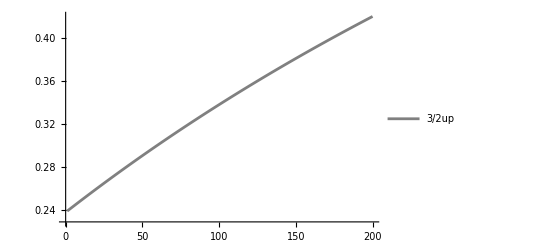

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/3.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

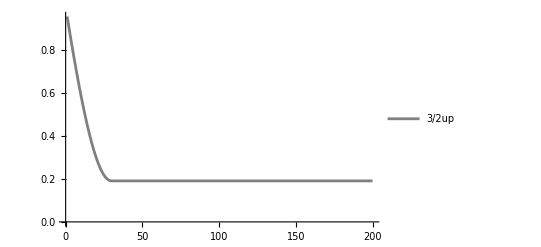

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/3.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

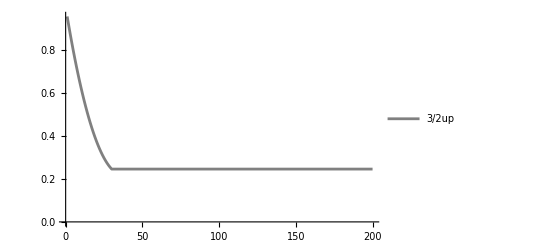

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/3.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
SqueezeListBox[[1,1]]/3.5
```

{1.+9.54009×10^-47 ⅈ,1.+5.249×10^-47 ⅈ,1.+4.53545×10^-47 ⅈ,1.+4.65275×10^-47 ⅈ,1.+1.48575×10^-47 ⅈ,1.-1.95494×10^-47 ⅈ,1.+1.87674×10^-47 ⅈ,1.-1.64215×10^-47 ⅈ,1.-6.0994×10^-47 ⅈ,1.+6.84228×10^-48 ⅈ,1.+7.81975×10^-48 ⅈ,1.+9.3837×10^-48 ⅈ,1.+8.89496×10^-48 ⅈ,1.-1.60305×10^-47 ⅈ,1.+1.13386×10^-47 ⅈ,1.-8.60172×10^-48 ⅈ,1.+3.1279×10^-48 ⅈ,1.+3.66551×10^-48 ⅈ,1.+1.56395×10^-48 ⅈ,1.+3.1279×10^-48 ⅈ,1.-1.01657×10^-47 ⅈ,1.+3.90987×10^-48 ⅈ,1.-7.81975×10^-48 ⅈ,1.-4.69185×10^-48 ⅈ,1.-7.23326×10^-48 ⅈ,1.+8.26733×10^-48 ⅈ,1.-3.32339×10^-48 ⅈ,1.-7.03777×10^-48 ⅈ,1.-4.69185×10^-48 ⅈ,1.-4.49635×10^-48 ⅈ,1.+3.07902×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.+2.54142×10^-48 ⅈ,1.-3.1279×10^-48 ⅈ,1.-4.69185×10^-48 ⅈ,1.-2.05268×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.+6.2558×10^-48 ⅈ,1.-2.73691×10^-48 ⅈ,1.-8.99271×10^-48 ⅈ,1.+4.69185×10^-48 ⅈ,1.+2.73691×10^-48 ⅈ,1.-4.69185×10^-48 ⅈ,1.-2.73691×10^-48 ⅈ,1.-2.34592×10^-48 ⅈ,1.-1.95494×10^-48 ⅈ,1.+3.32339×10^-48 ⅈ,1.-2.73691×10^-48 ⅈ,1.+2.63916×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.+3.1279×10^-48 ⅈ,1.-4.30086×10^-48 ⅈ,1.-7.81975×10^-49 ⅈ,1.-3.51889×10^-48 ⅈ,1.-1.17296×10^-48 ⅈ,1.-2.34592×10^-48 ⅈ,1.+9.77468×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.+2.73691×10^-48 ⅈ,1.-1.6617×10^-48 ⅈ,1.-3.1279×10^-48 ⅈ,1.-3.51889×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.+1.56395×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.-6.2558×10^-48 ⅈ,1.-1.95494×10^-48 ⅈ,1.+3.1279×10^-48 ⅈ,1.-2.35584×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.+2.34592×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.+5.86481×10^-49 ⅈ,1.-7.81975×10^-49 ⅈ,1.-9.77468×10^-49 ⅈ,1.+1.95494×10^-48 ⅈ,1.-7.81975×10^-49 ⅈ,1.-2.73691×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.-7.65848×10^-49 ⅈ,1.+1.56395×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.-1.17296×10^-48 ⅈ,1.-1.17296×10^-48 ⅈ,1.+1.56395×10^-48 ⅈ,1.+3.90987×10^-49 ⅈ,1.-7.81975×10^-49 ⅈ,1.-3.1279×10^-48 ⅈ,1.+0. ⅈ,1.-1.17296×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.-6.35354×10^-49 ⅈ,1.+7.81975×10^-49 ⅈ,1.+1.56395×10^-48 ⅈ,1.-1.17296×10^-48 ⅈ,1.+1.17296×10^-48 ⅈ,1.-1.02634×10^-48 ⅈ,1.-3.19738×10^-48 ⅈ,1.+8.79721×10^-49 ⅈ,1.+9.77468×10^-49 ⅈ,1.-2.34592×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.+1.56395×10^-48 ⅈ,1.-1.17296×10^-48 ⅈ,1.-2.34592×10^-48 ⅈ,1.+1.56395×10^-48 ⅈ,1.+0. ⅈ,1.-7.81975×10^-49 ⅈ,1.-9.28809×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.-1.36846×10^-48 ⅈ,1.+1.36846×10^-48 ⅈ,1.-1.07522×10^-48 ⅈ,1.-2.9324×10^-49 ⅈ,1.-1.07522×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.-2.73691×10^-48 ⅈ,1.+1.17296×10^-48 ⅈ,1.+1.22047×10^-48 ⅈ,1.+1.17296×10^-48 ⅈ,1.-7.81975×10^-49 ⅈ,1.+1.17296×10^-48 ⅈ,1.+3.90987×10^-49 ⅈ,1.+7.81975×10^-49 ⅈ,1.+3.90987×10^-49 ⅈ,1.+1.6617×10^-48 ⅈ,1.+1.07522×10^-48 ⅈ,1.+1.56395×10^-48 ⅈ,1.+3.90987×10^-49 ⅈ,1.-1.17296×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.-3.90987×10^-49 ⅈ,1.+3.90987×10^-49 ⅈ,1.-1.95494×10^-48 ⅈ,1.-1.30702×10^-48 ⅈ,1.+1.56395×10^-48 ⅈ,1.-7.81975×10^-49 ⅈ,1.+9.77468×10^-49 ⅈ,1.+7.81975×10^-49 ⅈ,1.+7.33101×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.+0. ⅈ,1.-7.81975×10^-49 ⅈ,1.+3.90987×10^-49 ⅈ,1.+0. ⅈ,1.-3.90987×10^-49 ⅈ,1.+7.81975×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.+3.1279×10^-48 ⅈ,1.-4.60219×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.-1.56395×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.-5.60897×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.-3.90987×10^-49 ⅈ,1.-7.81975×10^-49 ⅈ,1.+7.81975×10^-49 ⅈ,1.-2.9324×10^-49 ⅈ,1.-7.81975×10^-49 ⅈ,1.+1.95494×10^-49 ⅈ,1.+9.77468×10^-49 ⅈ,1.+6.84228×10^-49 ⅈ,1.-3.9565×10^-49 ⅈ,1.+4.66021×10^-49 ⅈ,1.-1.07522×10^-48 ⅈ,1.-5.86481×10^-49 ⅈ,1.-7.81975×10^-49 ⅈ,1.+3.90987×10^-49 ⅈ,1.-1.07522×10^-48 ⅈ,1.+7.81975×10^-49 ⅈ,1.-3.90987×10^-49 ⅈ,1.-3.90987×10^-49 ⅈ,1.-1.38565×10^-49 ⅈ,1.-7.81975×10^-49 ⅈ,1.-1.56395×10^-48 ⅈ,1.-7.81975×10^-49 ⅈ,1.+0. ⅈ,1.-7.81975×10^-49 ⅈ,1.-7.48361×10^-33 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-7.48361×10^-33 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ,1.-4.40213×10^-34 ⅈ}

```mathematica
Chop[DMListBox[[1,1,3]]]
```

{{0.000225176,0.000669639-0.00374833 ⅈ,-0.00244015+0.00705882 ⅈ,0.00555587-0.00337489 ⅈ,-0.00337489-0.00555587 ⅈ,-0.00705882-0.00244015 ⅈ,-0.00374833-0.00066964 ⅈ,0.+0.000225176 ⅈ},{0.000669639+0.00374833 ⅈ,0.064387,-0.124759-0.0196275 ⅈ,0.0727016+0.0824479 ⅈ,0.0824479-0.0727016 ⅈ,0.0196275-0.124759 ⅈ,1.55598×10^-10-0.064387 ⅈ,-0.00374834+0.000669639 ⅈ},{-0.00244015-0.00705882 ⅈ,-0.124759+0.0196275 ⅈ,0.247723,-0.166003-0.137593 ⅈ,-0.137593+0.166003 ⅈ,-2.45668×10^-10+0.247723 ⅈ,0.0196275+0.124759 ⅈ,0.00705883-0.00244015 ⅈ},{0.00555587+0.00337489 ⅈ,0.0727016-0.0824479 ⅈ,-0.166003+0.137593 ⅈ,0.187665,3.58972×10^-9-0.187665 ⅈ,-0.137593-0.166003 ⅈ,-0.0824479-0.0727016 ⅈ,-0.0033749+0.00555587 ⅈ},{-0.00337489+0.00555587 ⅈ,0.0824479+0.0727016 ⅈ,-0.137593-0.166003 ⅈ,3.58972×10^-9+0.187665 ⅈ,0.187665,0.166003-0.137593 ⅈ,0.0727016-0.0824479 ⅈ,-0.00555587-0.0033749 ⅈ},{-0.00705882+0.00244015 ⅈ,0.0196275+0.124759 ⅈ,-2.45667×10^-10-0.247723 ⅈ,-0.137593+0.166003 ⅈ,0.166003+0.137593 ⅈ,0.247723,0.124759-0.0196275 ⅈ,-0.00244015-0.00705883 ⅈ},{-0.00374833+0.00066964 ⅈ,1.55599×10^-10+0.064387 ⅈ,0.0196275-0.124759 ⅈ,-0.0824479+0.0727016 ⅈ,0.0727016+0.0824479 ⅈ,0.124759+0.0196275 ⅈ,0.064387,-0.000669639-0.00374834 ⅈ},{0.-0.000225176 ⅈ,-0.00374834-0.000669639 ⅈ,0.00705883+0.00244015 ⅈ,-0.0033749-0.00555587 ⅈ,-0.00555587+0.0033749 ⅈ,-0.00244015+0.00705883 ⅈ,-0.000669639+0.00374834 ⅈ,0.000225176}}

```mathematica
Chop[DMListBox[[1,1,3]]]
```

{{0.000197835,0.00110617-0.00332165 ⅈ,-0.00316801+0.00631209 ⅈ,0.00554128-0.00245703 ⅈ,-0.00245704-0.00554128 ⅈ,-0.00631209-0.003168 ⅈ,-0.00332165-0.00110617 ⅈ,6.4733×10^-10+0.000197835 ⅈ},{0.00110617+0.00332165 ⅈ,0.0619556,-0.123693-0.0178975 ⅈ,0.072237+0.0792998 ⅈ,0.0792998-0.072237 ⅈ,0.0178974-0.123693 ⅈ,1.16778×10^-9-0.0619555 ⅈ,-0.00332165+0.00110618 ⅈ},{-0.00316801-0.00631209 ⅈ,-0.123693+0.0178975 ⅈ,0.252123,-0.167128-0.137454 ⅈ,-0.137453+0.167128 ⅈ,8.75202×10^-8+0.252122 ⅈ,0.0178975+0.123693 ⅈ,0.00631208-0.00316803 ⅈ},{0.00554128+0.00245703 ⅈ,0.072237-0.0792998 ⅈ,-0.167128+0.137454 ⅈ,0.185724,-6.71657×10^-8-0.185724 ⅈ,-0.137454-0.167128 ⅈ,-0.0792998-0.072237 ⅈ,-0.00245701+0.00554129 ⅈ},{-0.00245704+0.00554128 ⅈ,0.0792998+0.072237 ⅈ,-0.137453-0.167128 ⅈ,-6.71657×10^-8+0.185724 ⅈ,0.185724,0.167128-0.137453 ⅈ,0.072237-0.0792998 ⅈ,-0.00554129-0.00245702 ⅈ},{-0.00631209+0.003168 ⅈ,0.0178974+0.123693 ⅈ,8.75202×10^-8-0.252122 ⅈ,-0.137454+0.167128 ⅈ,0.167128+0.137453 ⅈ,0.252122,0.123693-0.0178974 ⅈ,-0.00316802-0.00631207 ⅈ},{-0.00332165+0.00110617 ⅈ,1.16778×10^-9+0.0619555 ⅈ,0.0178975-0.123693 ⅈ,-0.0792998+0.072237 ⅈ,0.072237+0.0792998 ⅈ,0.123693+0.0178974 ⅈ,0.0619555,-0.00110618-0.00332165 ⅈ},{6.4733×10^-10-0.000197835 ⅈ,-0.00332165-0.00110618 ⅈ,0.00631208+0.00316803 ⅈ,-0.00245701-0.00554129 ⅈ,-0.00554129+0.00245702 ⅈ,-0.00316802+0.00631207 ⅈ,-0.00110618+0.00332165 ⅈ,0.000197835}}

```mathematica
Chop[DMListBox[[1,1,1]]]
```

{{0.00432215,0.00143966-0.0132496 ⅈ,-0.0300357+0.0102028 ⅈ,0.0166412+0.0261074 ⅈ,0.0261074-0.0166412 ⅈ,-0.0102028-0.0300357 ⅈ,-0.0132496-0.00143966 ⅈ,8.6846×10^-10+0.00432215 ⅈ},{0.00143966+0.0132496 ⅈ,0.0410964,-0.0412815-0.0886766 ⅈ,-0.0744896+0.0597098 ⅈ,0.0597099+0.0744896 ⅈ,0.0886765-0.0412816 ⅈ,-6.66641×10^-9-0.0410964 ⅈ,-0.0132496+0.00143966 ⅈ},{-0.0300357-0.0102028 ⅈ,-0.0412815+0.0886766 ⅈ,0.232811,-0.0540149-0.22071 ⅈ,-0.22071+0.054015 ⅈ,4.63175×10^-8+0.232811 ⅈ,0.0886765+0.0412815 ⅈ,0.0102028-0.0300357 ⅈ},{0.0166412-0.0261074 ⅈ,-0.0744896-0.0597098 ⅈ,-0.0540149+0.22071 ⅈ,0.22177,-3.85378×10^-8-0.22177 ⅈ,-0.22071-0.0540149 ⅈ,-0.0597098+0.0744896 ⅈ,0.0261074+0.0166412 ⅈ},{0.0261074+0.0166412 ⅈ,0.0597099-0.0744896 ⅈ,-0.22071-0.054015 ⅈ,-3.85378×10^-8+0.22177 ⅈ,0.22177,0.0540149-0.22071 ⅈ,-0.0744895-0.0597098 ⅈ,-0.0166412+0.0261074 ⅈ},{-0.0102028+0.0300357 ⅈ,0.0886765+0.0412816 ⅈ,4.63175×10^-8-0.232811 ⅈ,-0.22071+0.0540149 ⅈ,0.0540149+0.22071 ⅈ,0.232811,0.0412815-0.0886765 ⅈ,-0.0300357-0.0102028 ⅈ},{-0.0132496+0.00143966 ⅈ,-6.66641×10^-9+0.0410964 ⅈ,0.0886765-0.0412815 ⅈ,-0.0597098-0.0744896 ⅈ,-0.0744895+0.0597098 ⅈ,0.0412815+0.0886765 ⅈ,0.0410964,-0.00143966-0.0132496 ⅈ},{8.6846×10^-10-0.00432215 ⅈ,-0.0132496-0.00143966 ⅈ,0.0102028+0.0300357 ⅈ,0.0261074-0.0166412 ⅈ,-0.0166412-0.0261074 ⅈ,-0.0300357+0.0102028 ⅈ,-0.00143966+0.0132496 ⅈ,0.00432214}}

```mathematica
ξtopF[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0.5000000000000011,0.49750623959634127,0,0},{0,0,0.49750623959634127,0.5000000000000011,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]
```

Flatten::normal: Flatten[0.+0. ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+0. ⅈ] 中的位置 1 处应该是非原子表达式.

General::munfl: ArcCos[1.+0. ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

Flatten::normal: Flatten[0.+0. ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

General::munfl: ArcCos[1.+0. ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

0.5+0. ⅈ

```mathematica
1/3.5 ξtopF[{{0.0001978354719214711,0.0011061737307086305-0.0033216543182372515 ⅈ,-0.0031680081325020635+0.006312092126111811 ⅈ,0.0055412837252484465-0.0024570344240355973 ⅈ,-0.0024570361422998474-0.005541282192355517 ⅈ,-0.006312090197046639-0.003168004421230437 ⅈ,-0.0033216520134918747-0.0011061730327371492 ⅈ,6.47329975772315*^-10+0.00019783530742693953 ⅈ},{0.0011061737307086147+0.0033216543182373517 ⅈ,0.06195556142348237,-0.12369346712691418-0.017897485033546604 ⅈ,0.0722370025816256+0.07929984409197376 ⅈ,0.07929980874725451-0.07223702286026203 ⅈ,0.01789743350749787-0.12369341398680303 ⅈ,1.167783384315585*^-9-0.06195551882422047 ⅈ,-0.003321647936907301+0.0011061836796164267 ⅈ},{-0.0031680081325020704-0.0063120921261118675 ⅈ,-0.12369346712691459+0.017897485033547215 ⅈ,0.25212254431258346,-0.167128064681716-0.13745355203188006 ⅈ,-0.13745347560859555+0.16712809495750053 ⅈ,8.752017061682688*^-8+0.2521224233343999 ⅈ,0.017897470396171143+0.12369338241538955 ⅈ,0.006312076511867781-0.003168026151952234 ⅈ},{0.005541283725248429+0.0024570344240354425 ⅈ,0.07223700258162594-0.07929984409197306 ⅈ,-0.1671280646817161+0.13745355203187956 ⅈ,0.1857242441294013,-6.716571003713423*^-8-0.18572422253387894 ⅈ,-0.1374535440920723-0.16712793677245516 ⅈ,-0.07929978820559325-0.07223695440777506 ⅈ,-0.002457014249656302+0.00554128715739877 ⅈ},{-0.0024570361422996704+0.005541282192355429 ⅈ,0.07929980874725427+0.0722370228602625 ⅈ,-0.13745347560859728-0.1671280949575015 ⅈ,-6.716571021581075*^-8+0.18572422253387869 ⅈ,0.18572420093838052,0.1671279670482535-0.13745346766883643 ⅈ,0.07223697468639638-0.07929975286089888 ⅈ,-0.0055412856245127765-0.002457015967924255 ⅈ},{-0.006312090197046589+0.003168004421230419 ⅈ,0.017897433507497697+0.12369341398680332 ⅈ,8.752017051751396*^-8-0.25212242333440094 ⅈ,-0.1374535440920739+0.16712793677245666 ⅈ,0.16712796704825425+0.1374534676688365 ⅈ,0.2521223023563054,0.12369332927531425-0.017897418870158395 ⅈ,-0.003168022440677148-0.00631207458281615 ⅈ},{-0.003321652013491922+0.001106173032737141 ⅈ,1.1677833949407662*^-9+0.06195551882422046 ⅈ,0.0178974703961708-0.12369338241538996 ⅈ,-0.07929978820559425+0.07223695440777494 ⅈ,0.07223697468639688+0.07929975286089852 ⅈ,0.12369332927531408+0.01789741887015817 ⅈ,0.061955476224987614,-0.001106182981637949-0.003321645632166186 ⅈ},{6.473299781202904*^-10-0.00019783530742693666 ⅈ,-0.0033216479369073274-0.0011061836796163811 ⅈ,0.006312076511867649+0.003168026151952051 ⅈ,-0.002457014249656473-0.005541287157398659 ⅈ,-0.005541285624512576+0.0024570159679242636 ⅈ,-0.0031680224406771384+0.0063120745828161165 ⅈ,-0.001106182981637931+0.0033216456321661187 ⅈ,0.00019783514293462775}}]
```

Flatten::normal: Flatten[1.94918+2.94903×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+4.647×10^-24 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+3.01257×10^-16 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.19089+1.62889×10^-15 ⅈ

```mathematica
1/3.5 ξtopF[{{0.00022517613626195452,0.0006696394867291027-0.0037483341563906017 ⅈ,-0.002440151252150343+0.00705882371388301 ⅈ,0.005555871291482863-0.003374892688835374 ⅈ,-0.0033748926212467923-0.005555871419726166 ⅈ,-0.0070588237265736264-0.0024401512643741426 ⅈ,-0.0037483342568051-0.0006696395140155156 ⅈ,0.+0.0002251762441540136 ⅈ},{0.0006696394867290855+0.0037483341563907054 ⅈ,0.06438704487444197,-0.12475945332873914-0.0196274581751301 ⅈ,0.07270155981640487+0.08244790514062443 ⅈ,0.08244790747638994-0.07270155907269071 ⅈ,0.019627458340870055-0.1247594535763408 ⅈ,1.5559848375035212*^-10-0.06438704662710847 ⅈ,-0.0037483361687629044+0.0006696385964104535 ⅈ},{-0.0024401512521502982-0.007058823713883101 ⅈ,-0.12475945332873961+0.01962745817513061 ⅈ,0.24772309927262337,-0.1660031096233571-0.13759303235855433 ⅈ,-0.1375930371111583+0.1660031088943241 ⅈ,-2.4566751107360507*^-10+0.24772309980291188 ⅈ,0.019627458407910275+0.124759456772223 ⅈ,0.0070588278845535-0.0024401501404683395 ⅈ},{0.005555871291482732+0.0033748926888351864 ⅈ,0.07270155981640541-0.08244790514062421 ⅈ,-0.16600310962335715+0.1375930323585545 ⅈ,0.18766467517461768,3.5897212945223966*^-9-0.1876646773258231 ⅈ,-0.13759303248846683-0.16600311011516272 ⅈ,-0.0824479072092302-0.07270156199464421 ⅈ,-0.0033748961011288987+0.005555872863046054 ⅈ},{-0.003374892621246947+0.005555871419726 ⅈ,0.08244790747639051+0.07270155907269123 ⅈ,-0.13759303711115975-0.1660031088943249 ⅈ,3.5897211401320073*^-9+0.18766467732582293 ⅈ,0.1876646794770304,0.16600310938613028-0.13759303724107094 ⅈ,0.0727015612509295-0.08244790954499645 ⅈ,-0.005555872991289462-0.0033748960335405575 ⅈ},{-0.007058823726573592+0.0024401512643739314 ⅈ,0.01962745834087055+0.12475945357634159 ⅈ,-2.456673540811305*^-10-0.24772309980291268 ⅈ,-0.1375930324884684+0.16600311011516428 ⅈ,0.16600310938613114+0.1375930372410718 ⅈ,0.24772310033320213,0.12475945701982503-0.019627458573649857 ⅈ,-0.002440150152691888-0.007058827897243911 ⅈ},{-0.0037483342568051304+0.0006696395140154461 ⅈ,1.5559877735230043*^-10+0.06438704662710869 ⅈ,0.019627458407909998-0.12475945677222297 ⅈ,-0.08244790720923077+0.07270156199464448 ⅈ,0.07270156125092976+0.08244790954499658 ⅈ,0.12475945701982485+0.019627458573649573 ⅈ,0.06438704837977559,-0.0006696386236967273-0.0037483362691774096 ⅈ},{0.-0.000225176244154007 ⅈ,-0.003748336168762891-0.0006696385964104144 ⅈ,0.007058827884553389+0.0024401501404682055 ⅈ,-0.0033748961011289013-0.005555872863045959 ⅈ,-0.005555872991289372+0.003374896033540585 ⅈ,-0.0024401501526918265+0.007058827897243882 ⅈ,-0.0006696386236966888+0.003748336269177339 ⅈ,0.00022517635204613628}}]
```

Flatten::normal: Flatten[1.97227-8.34836×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708+2.846×10^-25 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[1.5708-1.11088×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.190515+1.52491×10^-15 ⅈ

0.19089+1.62889×10^-15 ⅈ

```mathematica
0.6185863554387714/2.5
```

0.247435

```mathematica
SqDm={{0.007812499999999998+0. ⅈ,-0.02012936442322758+0.004696251874303561 ⅈ,0.03544309025867072+0.005052289992243126 ⅈ,-0.02045301756394497-0.04144761200936621 ⅈ,-0.04144761200936621+0.02045301756394497 ⅈ,-0.005052289992243126+0.03544309025867072 ⅈ,0.004696251874303561+0.02012936442322758 ⅈ,0.+0.007812499999999998 ⅈ},{-0.02012936442322758-0.004696251874303561 ⅈ,0.054687499999999986+0. ⅈ,-0.08828416688083629-0.03432308038196226 ⅈ,0.027783400769911024+0.11908692591090134 ⅈ,0.11908692591090134-0.027783400769911024 ⅈ,0.03432308038196226-0.08828416688083629 ⅈ,0.-0.054687499999999986 ⅈ,0.004696251874303561-0.02012936442322758 ⅈ},{0.03544309025867072-0.005052289992243126 ⅈ,-0.08828416688083629+0.03432308038196226 ⅈ,0.16406249999999994+0. ⅈ,-0.11959340837611215-0.17480920032061945 ⅈ,-0.17480920032061945+0.11959340837611215 ⅈ,0.+0.16406249999999994 ⅈ,0.03432308038196226+0.08828416688083629 ⅈ,0.005052289992243126+0.03544309025867072 ⅈ},{-0.02045301756394497+0.04144761200936621 ⅈ,0.027783400769911024-0.11908692591090134 ⅈ,-0.11959340837611215+0.17480920032061945 ⅈ,0.2734375+0. ⅈ,0.-0.2734375 ⅈ,-0.17480920032061945-0.11959340837611215 ⅈ,-0.11908692591090134-0.027783400769911024 ⅈ,-0.04144761200936621-0.02045301756394497 ⅈ},{-0.04144761200936621-0.02045301756394497 ⅈ,0.11908692591090134+0.027783400769911024 ⅈ,-0.17480920032061945-0.11959340837611215 ⅈ,0.+0.2734375 ⅈ,0.2734375+0. ⅈ,0.11959340837611215-0.17480920032061945 ⅈ,0.027783400769911024-0.11908692591090134 ⅈ,0.02045301756394497-0.04144761200936621 ⅈ},{-0.005052289992243126-0.03544309025867072 ⅈ,0.03432308038196226+0.08828416688083629 ⅈ,0.-0.16406249999999994 ⅈ,-0.17480920032061945+0.11959340837611215 ⅈ,0.11959340837611215+0.17480920032061945 ⅈ,0.16406249999999994+0. ⅈ,0.08828416688083629-0.03432308038196226 ⅈ,0.03544309025867072-0.005052289992243126 ⅈ},{0.004696251874303561-0.02012936442322758 ⅈ,0.+0.054687499999999986 ⅈ,0.03432308038196226-0.08828416688083629 ⅈ,-0.11908692591090134+0.027783400769911024 ⅈ,0.027783400769911024+0.11908692591090134 ⅈ,0.08828416688083629+0.03432308038196226 ⅈ,0.054687499999999986+0. ⅈ,0.02012936442322758+0.004696251874303561 ⅈ},{0.-0.007812499999999998 ⅈ,0.004696251874303561+0.02012936442322758 ⅈ,0.005052289992243126-0.03544309025867072 ⅈ,-0.04144761200936621+0.02045301756394497 ⅈ,0.02045301756394497+0.04144761200936621 ⅈ,0.03544309025867072+0.005052289992243126 ⅈ,0.02012936442322758-0.004696251874303561 ⅈ,0.007812499999999998+0. ⅈ}};
```

```mathematica
Fidelitylist=Table[0,{m,21}];
Fidelitylist[[1]]=1;
Do[

Fidelitylist[[i]]=Fidelity[N[(SqDm.ConjugateTranspose[SqDm]).ConjugateTranspose[SqDm.ConjugateTranspose[SqDm]]],DMListBox[[1,1,i-1]]];
(*
Fidelitylist[[i]]=Fidelity[N[(SqDm.ConjugateTranspose[SqDm]).ConjugateTranspose[SqDm.ConjugateTranspose[SqDm]]],DMListBox[[1,1,i-1]]]

Fidelitylist[[i]]=Fidelity[N[(IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]).ConjugateTranspose[IniStateBox[[1]].ConjugateTranspose[IniStateBox[[1]]]]],DMListBox[[1,1,i-1]]];*)
,{i,2,21}]
```

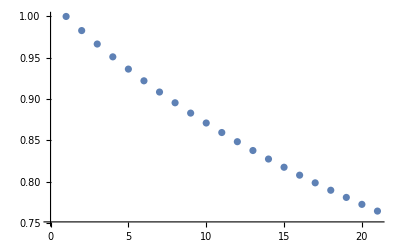

```mathematica
ListPlot[Fidelitylist]
```

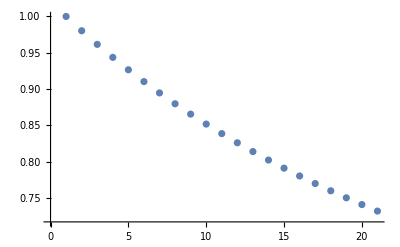

```mathematica
ListPlot[Fidelitylist]
```

```mathematica
ListPlot[Fidelitylist]
```

-Graphics-

```mathematica
Chop[Fidelitylist]
```

{1,0.982926,0.966662,0.951148,0.936331,0.922161,0.908595,0.895592,0.883116,0.871132,0.859611,0.848524,0.837845,0.82755,0.817617,0.808027,0.798759,0.789797,0.781125,0.772728,0.764592}

```mathematica
Pihalf2Pihalf2Iz={1,0.982926239503006,0.9666621740467047,0.9511483429264921,0.9363309820849515,0.922161368578633,0.9085952513606264,0.8955923557808474,0.8831159511990617,0.8711324727625847,0.8596111897809804,0.8485239142826363,0.8378447443026055,0.8275498372598636,0.8176172094619152,0.8080265583472355,0.7987591045593994,0.7897974513556052,0.7811254591989958,0.7727281336787017,0.7645915251523474};
Cat7half2N7half2Iz={1,0.8913522691209355,0.8063131970922118,0.7397527294874504,0.6876555494257043,0.6468788501617726,0.614962742593369,0.5899818603565644,0.5704292104605317,0.5551252626522529,0.5431467932496966,0.5337711908871252,0.526432864369189,0.5206891229005002,0.5161934703864693,0.5126747027613797,0.5099205473722032,0.5077648574500709,0.5060775891649778,0.5047569566210023,0.5037232915354848};

Sq7half2Iz={1,0.9804111751880963,0.9617376896653891,0.9439214644035482,0.92690883228287,0.9106501581287753,0.8950994946749524,0.8802142708038293,0.8659550088071666,0.8522850677576046,0.8391704103910926,0.8265793911747715,0.8144825634792373,0.8028525039913386,0.7916636526972477,0.7808921669379136,0.7705157881926331,0.760513720383657,0.7508665186169801,0.7415559873838357,0.7325650873450077};
```

```mathematica
Pihalf2Pihalf2IzIz={1,0.9948286816033871,0.9898093745774104,0.9849344222768587,0.9801966368448787,0.9755892685089699,0.9711059769397852,0.9667408045325022,0.9624881514800844,0.9583427525167904,0.954299655218512,0.9503541997543339,0.9465019999909272,0.9427389258580543,0.9390610868898316,0.93546481686211,0.9319466594518516,0.9285033548494068,0.9251318272592984,0.9218291732295468,0.9185926507536004};

Sq7half2IzIz={1,0.9965720662308973,0.9931852546547761,0.9898388311001384,0.9865320803407129,0.9832643053392913,0.9800348265329345,0.976842981157023,0.9736881226056382,0.9705696198260363,0.9674868567450946,0.9644392317257261,0.9614261570514083,0.9584470584371262,0.9555013745650617,0.9525885566435648,0.9497080679879629,0.9468593836218968,0.9440419898979561,0.9412553841364545,0.938499074281252};
```

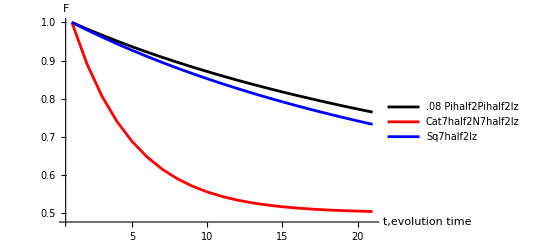

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2Iz,Cat7half2N7half2Iz,Sq7half2Iz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2Iz","Cat7half2N7half2Iz","Sq7half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

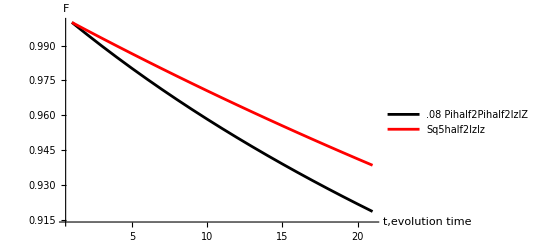

```mathematica
Plot3half2Fidelity=ListPlot[{Pihalf2Pihalf2IzIz,Sq7half2IzIz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2IzIZ","Sq5half2IzIz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Red,Blue,Purple,Brown,Cyan,Brown},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/3.5,10^-7]
```

{0.957944,0.916624,0.876038,0.836199,0.797128,0.758856,0.721422,0.68487,0.649252,0.614623,0.581043,0.548572,0.517275,0.487217,0.458465,0.431086,0.405145,0.380708,0.357838,0.336598,0.317049,0.299246,0.283246,0.269099,0.256852,0.246551,0.238234,0.231937,0.227691,0.225522,0.226557,0.227629,0.228736,0.22988,0.231061,0.232278,0.233534,0.234827,0.236157,0.237526,0.238934,0.24038,0.241864,0.243388,0.24495,0.246552,0.248193,0.249874,0.251594,0.253354,0.255153,0.256992,0.25887,0.260788,0.262746,0.264743,0.26678,0.268856,0.270971,0.273126,0.275319,0.277552,0.279823,0.282133,0.284481,0.286868,0.289292,0.291754,0.294254,0.29679,0.299364,0.301973,0.30462,0.307301,0.310019,0.312771,0.315559,0.31838,0.321236,0.324125,0.327047,0.330002,0.332988,0.336007,0.339056,0.342136,0.345246,0.348386,0.351554,0.354751,0.357976,0.361229,0.364507,0.367812,0.371143,0.374498,0.377878,0.381281,0.384707,0.388155,0.391624,0.395115,0.398626,0.402156,0.405706,0.409273,0.412858,0.416459,0.420076,0.423709,0.427356,0.431017,0.434691,0.438377,0.442074,0.445783,0.449501,0.453228,0.456964,0.460708,0.464459,0.468216,0.471978,0.475745,0.479515,0.483289,0.487065,0.490843,0.494621,0.498399,0.502177,0.505953,0.509727,0.513498,0.517265,0.521027,0.524784,0.528536,0.53228,0.536017,0.539745,0.543465,0.547175,0.550875,0.554563,0.55824,0.561904,0.565555,0.569192,0.572814,0.576422,0.580013,0.583588,0.587146,0.590685,0.594207,0.597709,0.601192,0.604654,0.608096,0.611516,0.614914,0.61829,0.621642,0.624971,0.628275,0.631555,0.63481,0.638038,0.641241,0.644417,0.647566,0.650687,0.65378,0.656845,0.65988,0.662887,0.665863,0.66881,0.671726,0.674611,0.677466,0.680288,0.683079,0.685838,0.688564,0.691258,0.693918,0.696545,0.699139,0.701699,0.704225,0.706717,0.709175,0.711598,0.713986,0.71634,0.718658,0.720941,0.723189}

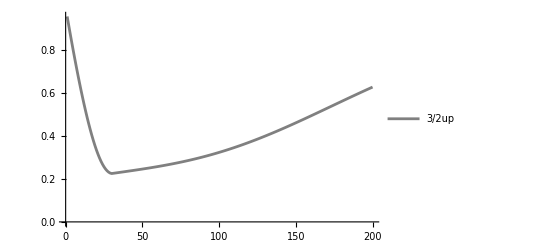

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/3.5,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
Chop[SqueezeListBox[[1,1]]/3.5,10^-7]
```

{0.961144,0.92319,0.886106,0.849877,0.814501,0.779984,0.746344,0.713608,0.681808,0.650982,0.621171,0.592424,0.564787,0.538311,0.513049,0.489052,0.466372,0.445061,0.425169,0.406745,0.389836,0.374486,0.360738,0.34863,0.338198,0.329476,0.322492,0.317271,0.313835,0.312201,0.316428,0.320647,0.324858,0.329062,0.333259,0.33745,0.341636,0.345817,0.349994,0.354167,0.358337,0.362504,0.366669,0.370833,0.374996,0.379158,0.383321,0.387484,0.391648,0.395814,0.399982,0.404153,0.408327,0.412505,0.416687,0.420874,0.425066,0.429263,0.433466,0.437676,0.441893,0.446118,0.45035,0.45459,0.45884,0.463098,0.467365,0.471643,0.47593,0.480228,0.484537,0.488858,0.493189,0.497533,0.501889,0.506257,0.510638,0.515032,0.51944,0.523861,0.528295,0.532744,0.537207,0.541684,0.546176,0.550683,0.555205,0.559742,0.564294,0.568861,0.573444,0.578042,0.582656,0.587286,0.591931,0.596593,0.60127,0.605963,0.610672,0.615397,0.620138,0.624895,0.629667,0.634456,0.63926,0.644079,0.648914,0.653765,0.658631,0.663512,0.668408,0.673319,0.678245,0.683185,0.68814,0.693109,0.698091,0.703088,0.708098,0.713121,0.718157,0.723207,0.728268,0.733342,0.738428,0.743525,0.748634,0.753753,0.758884,0.764024,0.769175,0.774336,0.779505,0.784684,0.789871,0.795066,0.80027,0.80548,0.810698,0.815922,0.821153,0.826389,0.831631,0.836878,0.842129,0.847384,0.852643,0.857906,0.863171,0.868438,0.873708,0.878979,0.884251,0.889523,0.894796,0.900069,0.90534,0.910611,0.91588,0.921146,0.92641,0.931671,0.936929,0.942182,0.947432,0.952676,0.957915,0.963149,0.968376,0.973596,0.97881,0.984016,0.989214,0.994403,0.999584,1.00476,1.00992,1.01507,1.02021,1.02534,1.03046,1.03557,1.04066,1.04575,1.05082,1.05587,1.06092,1.06595,1.07096,1.07596,1.08095,1.08592,1.09087,1.09581,1.10073,1.10563,1.11052,1.11539,1.12024,1.12508}

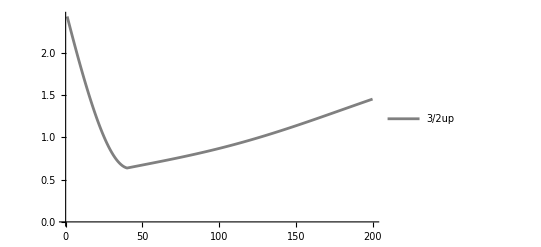

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

```mathematica
AA={2.4287192832945568,2.3581008749698764,2.2881565208455106,2.2189044486696132,2.1503689685480976,2.082580073696849,2.0155730445395568,1.9493880584698569,1.8840698070105006,1.8196671216210984,1.7562326090162166,1.6938222965444023,1.6324952879342922,1.572313429525314,1.5133409869583099,1.455644332197005,1.3992916406778202,1.3443525983364497,1.2908981182303505,1.239000066461855,1.1887309971041526,1.140163895838374,1.093371932022574,1.0484282189303529,1.005405581916821,0.964376334291317,0.9254120606988856,0.8885834078352559,0.853959882342294,0.8216096557524861,0.7915993763713298,0.7639939880056059,0.7388565554632023,0.7162480967661904,0.6962274220335374,0.6788509790028026,0.6641727051716955,0.6522438865503566,0.6431130230238034,0.636825700331177,0.640382404544062,0.6439345186207062,0.6474828675578723,0.6510282764590389,0.6545715701933017,0.6581135730499184,0.6616551083885862,0.6651969982856727,0.668740063176573,0.6722851214943772,0.6758329893050816,0.679384479939539,0.6829404036223603,0.686501567098043,0.6900687732545188,0.6936428207444094,0.6972245036042475,0.7008146108718916,0.7044139262024736,0.70802322748311,0.7116432864467082,0.7152748682851375,0.7189187312620824,0.7225756263259133,0.726246296722842,0.7299314776107475,0.7336318956739514,0.7373482687393209,0.7410813053940037,0.7448317046051627,0.7486001553420492,0.7523873362007674,0.7561939150320875,0.7600205485726561,0.7638678820799689,0.7677365489714649,0.7716271704680939,0.775540355242724,0.7794766990737592,0.7834367845042962,0.7874211805072027,0.7914304421564755,0.7954651103051988,0.7995257112704892,0.8036127565257543,0.8077267424005927,0.8118681497887055,0.8160374438641158,0.8202350738060447,0.824461472532735,0.8287170564445612,0.8330022251767097,0.8373173613617322,0.8416628304022469,0.8460389802540664,0.8504461412200346,0.8548846257548108,0.8593547282808234,0.863856725015697,0.8683908738112809,0.8729574140045773,0.8775565662806941,0.8821885325480441,0.8868534958259535,0.8915516201448415,0.896283050459084,0.9010479125727326,0.9058463130781638,0.9106783393077817,0.9155440592988411,0.9204435217714737,0.9253767561199497,0.9303437724172321,0.9353445614328302,0.9403790946639656,0.9454473243800368,0.9505491836803461,0.9556845865650776,0.9608534280194148,0.9660555841107845,0.971290912099088,0.9765592505598457,0.9818604195201068,0.9871942206070305,0.9925604372089256,0.9979588346486481,1.003389160369125,1.0088511441308574,1.014344498221131,1.019868917674783,1.025424080506237,1.0310096479525925,1.036625264727478,1.0422705592854205,1.0479451440964493,1.0536486159305953,1.0593805561520666,1.0651405310226814,1.0709280920143027,1.0767427761299535,1.0825841062331913,1.0884515913854687,1.0943447271911055,1.1002629961494632,1.1062058680140283,1.1121728001579516,1.118163237945736,1.1241766151106165,1.1302123541372961,1.1362698666496485,1.142348553802941,1.1484478066802328,1.1545670066925542,1.1607055259824133,1.1668627278303014,1.1730379670637636,1.179230590468633,1.1854399372020645,1.1916653392069403,1.1979061216272937,1.204161603224338,1.21043109679275,1.2167139095767734,1.223009343685856,1.2293166965093696,1.2356352611301014,1.2419643267361615,1.2483031790309362,1.2546511006407557,1.261007371519959,1.2673712693530081,1.2737420699533524,1.280119047658728,1.28650147572259,1.2928886267014024,1.2992797728375054,1.305674186437248,1.3120711402441922,1.318469907807108,1.3248697638424995,1.3312699845914726,1.337669848170704,1.3440686349173077,1.350465627727409,1.3568601123882464,1.3632513779036155,1.3696387168124935,1.3760214255007162,1.3823988045055535,1.3887701588130286,1.3951347981479354,1.4014920372563768,1.4078411961807569,1.414181600527166,1.420512581725109,1.426833477279307,1.4331436310139694,1.4394423933089535,1.4457291213282195,1.4520031792403154};
```

```mathematica
Chop[SqueezeListBox[[1,1]]/1,10^-7]
```

```mathematica
BB={2.4287192832945568,2.3581008749698764,2.2881565208455106,2.2189044486696132,2.1503689685480976,2.082580073696849,2.0155730445395568,1.9493880584698569,1.8840698070105006,1.8196671216210984,1.7562326090162166,1.6938222965444023,1.6324952879342922,1.572313429525314,1.5133409869583099,1.455644332197005,1.3992916406778202,1.3443525983364497,1.2908981182303505,1.239000066461855,1.1887309971041526,1.140163895838374,1.093371932022574,1.0484282189303529,1.005405581916821,0.964376334291317,0.9254120606988856,0.8885834078352559,0.853959882342294,0.8216096557524861,0.7915993763713298,0.7639939880056059,0.7388565554632023,0.7162480967661904,0.6962274220335374,0.6788509790028026,0.6641727051716955,0.6522438865503566,0.6431130230238034,0.636825700331177,0.6334244686742978,0.6329487279726664,0.6354346197855536,0.6409149259241174,0.6494189737779488,0.660972548380709,0.6755978112391459,0.6933132259483052,0.7141334906138654,0.7380694770995087,0.7651281771139766,0.795312655148364,0.8286220082696163,0.8650513327711389,0.9045916976759374,0.9472301250817292,0.9929495773312293,1.0417289509841554,1.093543077560561,1.1483627310180307,1.2061546419177143,1.2668815182266844,1.330502072696314,1.3969710567482965,1.4662393007920809,1.5382537608890647,1.6129575716708233,1.6902901054100727,1.770187037134737,1.8525804156668313,1.9373987404592814,2.0245670440949155,2.1140069803030785,2.2056369173400387,2.299372036570074,2.3951244360743402,2.4928032391044406,2.592314707186685,2.693562357671369,2.7964470855083556,2.900867289015674,3.006718999391043,3.113896013696168,3.2222900310195985,3.331790791493799,3.442286217803831,3.5536625587752386,3.665804534562629,3.778595482870771,3.891917505516456,4.005651614465715,4.119677876232679,4.233875553164934,4.348123239604197,4.462298990100252,4.5762804356034135,4.689944881580276,4.803169378786143,4.9158307520715345,5.027805563379966,5.138969968643915,5.2491993977074625,5.3583679268056645,5.46634709033735,5.573003608391755,5.678194861991566,5.781759250548555,5.88349348862491,5.983090897404586,6.079933457034303,6.1720933278698835,6.246887330671213,6.199099298884955,6.050356465329387,5.890838984208667,5.729825047466961,5.569023533701191,5.4090964435896165,5.25043809636735,5.09334771434622,4.938082400548058,4.784876999047431,4.633952590012424,4.4855204552402945,4.339784027754484,4.1969398651617595,4.057178118277411,3.920682725334875,3.78763145141625,3.6581958385663893,3.5325411040542347,3.410826009083515,3.293202711705074,3.179816612686393,3.0708062000791045,2.9663028963527522,2.866430910768722,2.771307098887021,2.681040830575148,2.595733867529265,2.515480251065588,2.4403662007583704,2.370470024366902,2.3058620393923666,2.246604506526483,2.192751575190619,2.1443492413121676,2.101435317441084,2.0640394152715777,2.0321829406003435,2.0058791007223755,1.9851329242375244,1.9699412932149025,1.9602929876377502,1.9561687420277947,1.9575413141256495,1.964375565481769,1.976628553791016,1.994249636782711,2.0171805874569024,2.045355720436391,2.0787020291824074,2.117139333799434,2.1605804391310572,2.208931302823095,2.2620912130017024,2.3199529751813146,2.3824031079777823,2.4493220471532546,2.520584357455883,2.59605895163262,2.6756093158754344,2.759093740792159,2.8463655567433026,2.937273372006131,3.031661311632754,3.1293692539113227,3.230233059749473,3.3340847875702053,3.440752881451494,3.5500623112233747,3.661834625682815,3.7758878439602044,3.8920360306286472,4.010088210842057,4.1298457833186,4.251096096833461,4.373594548863538,4.497003369532637,4.6205900296838465,4.739814251489037,4.757303104596868,4.678887342353419,4.596575209508372,4.514391926679284,4.432942114161442,4.352456567183306,4.273078665433483,4.194903870055487,4.118035183941553};
```

```mathematica
ListPlot[{AA,BB}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
|
```

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/1,10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
N[Pi/2*13/50]
```

0.408407

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(5/2),10^-7],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]3
```

-Graphics-

```mathematica
SqueezeListBox[[1,1]]/(5/2)
```

{0.976014+6.6408×10^-17 ⅈ,0.953378+5.74927×10^-17 ⅈ,0.932106+7.67646×10^-17 ⅈ,0.912216+6.04711×10^-17 ⅈ,0.89372+9.26067×10^-18 ⅈ,0.876633+6.46977×10^-17 ⅈ,0.860965+1.4481×10^-16 ⅈ,0.846728+1.12318×10^-16 ⅈ,0.833932+2.81371×10^-16 ⅈ,0.822586+1.67019×10^-16 ⅈ,0.812698+1.87067×10^-16 ⅈ,0.804276+2.74108×10^-16 ⅈ,0.797328+2.74898×10^-16 ⅈ,0.791859+3.24054×10^-16 ⅈ,0.787875+3.93217×10^-16 ⅈ,0.785383+4.58838×10^-16 ⅈ,0.784387+4.90523×10^-16 ⅈ,0.784892+5.73411×10^-16 ⅈ,0.786903+6.14428×10^-16 ⅈ,0.790422+6.04623×10^-16 ⅈ,0.795455+7.41013×10^-16 ⅈ,0.802003+6.26854×10^-16 ⅈ,0.810068+7.45452×10^-16 ⅈ,0.819653+8.32548×10^-16 ⅈ,0.830757+9.62432×10^-16 ⅈ,0.843381+9.59856×10^-16 ⅈ,0.857522+1.21177×10^-15 ⅈ,0.873176+1.30123×10^-15 ⅈ,0.890337+1.3707×10^-15 ⅈ,0.908998+1.57812×10^-15 ⅈ,0.929147+1.67422×10^-15 ⅈ,0.950769+1.65172×10^-15 ⅈ,0.973846+1.64764×10^-15 ⅈ,0.998354+1.57643×10^-15 ⅈ,1.02426+1.75542×10^-15 ⅈ,1.05154+1.79767×10^-15 ⅈ,1.08013+2.02692×10^-15 ⅈ,1.11+1.82424×10^-15 ⅈ,1.14107+2.17884×10^-15 ⅈ,1.17329+2.04641×10^-15 ⅈ,1.20655+2.03465×10^-15 ⅈ,1.24078+2.14318×10^-15 ⅈ,1.27585+2.04486×10^-15 ⅈ,1.31164+2.06529×10^-15 ⅈ,1.34801+2.08692×10^-15 ⅈ,1.38481+2.1305×10^-15 ⅈ,1.42187+2.02553×10^-15 ⅈ,1.45899+1.83634×10^-15 ⅈ,1.49598+1.77207×10^-15 ⅈ,1.53262+1.39914×10^-15 ⅈ,1.5687+1.12957×10^-15 ⅈ,1.60398+1.25386×10^-15 ⅈ,1.63822+8.47125×10^-16 ⅈ,1.67121+5.87678×10^-16 ⅈ,1.70272+2.41706×10^-16 ⅈ,1.73255+4.1279×10^-17 ⅈ,1.76051-3.23895×10^-16 ⅈ,1.78643-6.96384×10^-16 ⅈ,1.81019-8.85433×10^-16 ⅈ,1.83167-1.32049×10^-15 ⅈ,1.83167-1.28116×10^-15 ⅈ,1.83167-1.3017×10^-15 ⅈ,1.83167-1.18585×10^-15 ⅈ,1.83167-1.17436×10^-15 ⅈ,1.83167-1.22287×10^-15 ⅈ,1.83167-1.27653×10^-15 ⅈ,1.83167-1.19273×10^-15 ⅈ,1.83167-1.16959×10^-15 ⅈ,1.83167-1.00612×10^-15 ⅈ,1.83167-9.30148×10^-16 ⅈ,1.83167-1.18781×10^-15 ⅈ,1.83167-1.10111×10^-15 ⅈ,1.83167-1.0192×10^-15 ⅈ,1.83167-1.23568×10^-15 ⅈ,1.83167-1.26892×10^-15 ⅈ,1.83167-1.03131×10^-15 ⅈ,1.83167-9.50258×10^-16 ⅈ,1.83167-1.01591×10^-15 ⅈ,1.83167-1.15969×10^-15 ⅈ,1.83167-1.26636×10^-15 ⅈ,1.83167-1.41372×10^-15 ⅈ,1.83167-1.14622×10^-15 ⅈ,1.83167-1.39899×10^-15 ⅈ,1.83167-1.57753×10^-15 ⅈ,1.83167-1.53634×10^-15 ⅈ,1.83167-1.60315×10^-15 ⅈ,1.83167-1.6392×10^-15 ⅈ,1.83167-1.9774×10^-15 ⅈ,1.83167-1.97691×10^-15 ⅈ,1.83167-1.79393×10^-15 ⅈ,1.83167-1.88054×10^-15 ⅈ,1.83167-2.20952×10^-15 ⅈ,1.83167-2.031×10^-15 ⅈ,1.83167-2.00824×10^-15 ⅈ,1.83167-2.13016×10^-15 ⅈ,1.83167-2.21925×10^-15 ⅈ,1.83167-2.35642×10^-15 ⅈ,1.83167-2.61372×10^-15 ⅈ,1.83167-2.69159×10^-15 ⅈ,1.83167-2.64962×10^-15 ⅈ,1.83167-2.423×10^-15 ⅈ,1.83167-2.54177×10^-15 ⅈ,1.83167-2.60698×10^-15 ⅈ,1.83167-2.76218×10^-15 ⅈ,1.83167-2.77992×10^-15 ⅈ,1.83167-2.94337×10^-15 ⅈ,1.83167-3.06464×10^-15 ⅈ,1.83167-3.03636×10^-15 ⅈ,1.83167-3.15584×10^-15 ⅈ,1.83167-3.31574×10^-15 ⅈ,1.83167-3.6617×10^-15 ⅈ,1.83167-3.57923×10^-15 ⅈ,1.83167-3.75698×10^-15 ⅈ,1.83167-4.00977×10^-15 ⅈ,1.83167-4.03563×10^-15 ⅈ,1.83167-4.53874×10^-15 ⅈ,1.83167-4.4935×10^-15 ⅈ,1.83167-4.68806×10^-15 ⅈ,1.83167-4.90298×10^-15 ⅈ,1.83167-5.1006×10^-15 ⅈ,1.83167-5.03143×10^-15 ⅈ,1.83167-5.10102×10^-15 ⅈ,1.83167-5.28939×10^-15 ⅈ,1.83167-5.27306×10^-15 ⅈ,1.83167-5.37143×10^-15 ⅈ,1.83167-5.42726×10^-15 ⅈ,1.83167-5.61434×10^-15 ⅈ,1.83167-5.798×10^-15 ⅈ,1.83167-6.24527×10^-15 ⅈ,1.83167-6.27067×10^-15 ⅈ,1.83167-6.22421×10^-15 ⅈ,1.83167-6.51098×10^-15 ⅈ,1.83167-6.55191×10^-15 ⅈ,1.83167-6.65774×10^-15 ⅈ,1.83167-6.9997×10^-15 ⅈ,1.83167-6.97755×10^-15 ⅈ,1.83167-7.21093×10^-15 ⅈ,1.83167-7.76268×10^-15 ⅈ,1.83167-7.3907×10^-15 ⅈ,1.83167-7.93361×10^-15 ⅈ,1.83167-8.05509×10^-15 ⅈ,1.83167-8.11722×10^-15 ⅈ,1.83167-8.19745×10^-15 ⅈ,1.83167-8.47406×10^-15 ⅈ,1.83167-8.45528×10^-15 ⅈ,1.83167-8.86478×10^-15 ⅈ,1.83167-8.96222×10^-15 ⅈ,1.83167-8.93941×10^-15 ⅈ,1.83167-8.82417×10^-15 ⅈ,1.83167-8.93676×10^-15 ⅈ,1.83167-9.1069×10^-15 ⅈ,1.83167-9.40445×10^-15 ⅈ,1.83167-9.76712×10^-15 ⅈ,1.83167-9.50348×10^-15 ⅈ,1.83167-9.78269×10^-15 ⅈ,1.83167-9.87656×10^-15 ⅈ,1.83167-1.00179×10^-14 ⅈ,1.83167-9.94995×10^-15 ⅈ,1.83167-9.99003×10^-15 ⅈ,1.83167-1.00684×10^-14 ⅈ,1.83167-1.04733×10^-14 ⅈ,1.83167-1.04396×10^-14 ⅈ,1.83167-1.03055×10^-14 ⅈ,1.83167-1.04758×10^-14 ⅈ,1.83167-1.06441×10^-14 ⅈ,1.83167-1.08323×10^-14 ⅈ,1.83167-1.10282×10^-14 ⅈ,1.83167-1.09485×10^-14 ⅈ,1.83167-1.09446×10^-14 ⅈ,1.83167-1.09556×10^-14 ⅈ,1.83167-1.1081×10^-14 ⅈ,1.83167-1.12445×10^-14 ⅈ,1.83167-1.13592×10^-14 ⅈ,1.83167-1.12584×10^-14 ⅈ,1.83167-1.1277×10^-14 ⅈ,1.83167-1.12831×10^-14 ⅈ,1.83167-1.13032×10^-14 ⅈ,1.83167-1.12249×10^-14 ⅈ,1.83167-1.1428×10^-14 ⅈ,1.83167-1.12341×10^-14 ⅈ,1.83167-1.12063×10^-14 ⅈ,1.83167-1.11228×10^-14 ⅈ,1.83167-1.1247×10^-14 ⅈ,1.83167-1.13297×10^-14 ⅈ,1.83167-1.12951×10^-14 ⅈ,1.83167-1.13955×10^-14 ⅈ,1.83167-1.12266×10^-14 ⅈ,1.83167-1.11213×10^-14 ⅈ,1.83167-1.13533×10^-14 ⅈ,1.83167-1.11414×10^-14 ⅈ,1.83167-1.11042×10^-14 ⅈ,1.83167-1.11202×10^-14 ⅈ,1.83167-1.11559×10^-14 ⅈ,1.83167-1.10388×10^-14 ⅈ,1.83167-1.09195×10^-14 ⅈ,1.83167-1.09737×10^-14 ⅈ,1.83167-1.09048×10^-14 ⅈ,1.83167-1.07782×10^-14 ⅈ,1.83167-1.11436×10^-14 ⅈ,1.83167-1.10965×10^-14 ⅈ}

```mathematica
SqueezeListBox[[1,1]]/(5/2)
```

{0.978348+0.00370753 ⅈ,0.957928+0.00757618 ⅈ,0.938764+0.0116115 ⅈ,0.920887+0.0158203 ⅈ,0.904326+0.0202105 ⅈ,0.889116+0.0247914 ⅈ,0.875296+0.0295733 ⅈ,0.862904+0.0345679 ⅈ,0.851983+0.039788 ⅈ,0.842576+0.0452477 ⅈ,0.834731+0.0509625 ⅈ,0.828495+0.0569487 ⅈ,0.823916+0.0632243 ⅈ,0.821044+0.0698079 ⅈ,0.819929+0.0767198 ⅈ,0.820621+0.0839809 ⅈ,0.823169+0.0916133 ⅈ,0.827623+0.0996401 ⅈ,0.834028+0.108085 ⅈ,0.84243+0.116972 ⅈ,0.852869+0.126327 ⅈ,0.865384+0.136174 ⅈ,0.880008+0.146539 ⅈ,0.896767+0.157447 ⅈ,0.915684+0.16892 ⅈ,0.936772+0.180984 ⅈ,0.960034+0.193659 ⅈ,0.985464+0.206964 ⅈ,1.01305+0.220916 ⅈ,1.04275+0.235528 ⅈ,1.07452+0.250808 ⅈ,1.10831+0.266759 ⅈ,1.14404+0.283376 ⅈ,1.1816+0.300647 ⅈ,1.22088+0.318547 ⅈ,1.26173+0.337042 ⅈ,1.30401+0.356081 ⅈ,1.34753+0.375598 ⅈ,1.3921+0.395508 ⅈ,1.43749+0.41571 ⅈ,1.48348+0.43608 ⅈ,1.52983+0.456478 ⅈ,1.5763+0.476747 ⅈ,1.62263+0.496714 ⅈ,1.66858+0.516198 ⅈ,1.71389+0.535004 ⅈ,1.75832+0.552934 ⅈ,1.80162+0.569788 ⅈ,1.84357+0.58536 ⅈ,1.88393+0.59945 ⅈ,1.92252+0.611857 ⅈ,1.95913+0.622384 ⅈ,1.99359+0.63084 ⅈ,2.02575+0.637035 ⅈ,2.05549+0.640787 ⅈ,2.0827+0.641914 ⅈ,2.10724-0.242782 ⅈ,2.11468-0.233234 ⅈ,2.12161-0.221635 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.12809-0.207743 ⅈ,2.07326-0.805222 ⅈ}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[ξtopF[MatrixExp[-I*Ix3half2*Pi/2].DMevolve[[1,1]].MatrixExp[+I*Ix3half2*Pi/2]]]
```

Flatten::normal: Flatten[0.332823+1.38778×10^-17 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.726683-6.43068×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[0.597188+5.53063×10^-15 ⅈ] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

0.672397

```mathematica
DMevolve[[1,1]]
```

{{0.0549372-1.10954×10^-16 ⅈ,-0.0789447-0.0259826 ⅈ,-0.0628249+0.135289 ⅈ,-0.0162147+0.0431125 ⅈ},{-0.0789447+0.0259826 ⅈ,0.173517-9.37621×10^-16 ⅈ,0.102717-0.262559 ⅈ,0.0381837-0.103942 ⅈ},{-0.0628249-0.135289 ⅈ,0.102717+0.262559 ⅈ,0.655331+2.30254×10^-15 ⅈ,0.242912-0.0552429 ⅈ},{-0.0162147-0.0431125 ⅈ,0.0381837+0.103942 ⅈ,0.242912+0.0552429 ⅈ,0.116214-1.21011×10^-15 ⅈ}}

```mathematica
MatrixExp[-I*Ix3half2*Pi/2].DMevolve[[1,1]].MatrixExp[+I*Ix3half2*Pi/2]
```

{{0.585751+1.51268×10^-15 ⅈ,0.076817-0.106961 ⅈ,0.210952-0.280544 ⅈ,0.00198419-0.216759 ⅈ},{0.076817+0.106961 ⅈ,0.0943153+2.46331×10^-16 ⅈ,0.0845181-0.00649014 ⅈ,0.0615183-0.041313 ⅈ},{0.210952+0.280544 ⅈ,0.0845181+0.00649014 ⅈ,0.21992-1.7486×10^-15 ⅈ,0.108164-0.0777004 ⅈ},{0.00198419+0.216759 ⅈ,0.0615183+0.041313 ⅈ,0.108164+0.0777004 ⅈ,0.100013+2.08167×10^-17 ⅈ}}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980159,0.960493,0.941014,0.921732,0.902659,0.883805,0.865179,0.846792,0.828652,0.810769,0.793152,0.775808,0.758746,0.741974,0.7255,0.709329,0.69347,0.677928,0.66271,0.647821,0.633268,0.619055,0.605188,0.59167,0.578506,0.565701,0.553257,0.541177,0.529466,0.518126,0.507158,0.496566,0.486351,0.476515,0.467058,0.457983,0.44929,0.44098,0.433053,0.425509,0.418349,0.411573,0.405181,0.399172,0.393546,0.388304,0.383444,0.378967,0.374873,0.371161,0.367831,0.364883,0.362318,0.360136,0.358338,0.356923,0.355894,0.355251,0.354995,0.355127,0.355349,0.355569,0.355788,0.356006,0.356224,0.35644,0.356657,0.356873,0.357089,0.357305,0.357521,0.357737,0.357954,0.358171,0.35839,0.358609,0.358829,0.35905,0.359273,0.359497,0.359723,0.35995,0.36018,0.360411,0.360645,0.360881,0.36112,0.361361,0.361605,0.361852,0.362102,0.362356,0.362612,0.362872,0.363136,0.363403,0.363674,0.36395,0.364229,0.364512,0.3648,0.365092,0.365389,0.365691,0.365997,0.366309,0.366625,0.366946,0.367273,0.367605,0.367943,0.368286,0.368634,0.368989,0.369349,0.369715,0.370088,0.370466,0.37085,0.371241,0.371638,0.372042,0.372451,0.372868,0.373291,0.373721,0.374157,0.3746,0.37505,0.375507,0.375971,0.376442,0.37692,0.377405,0.377897,0.378396,0.378902,0.379415,0.379936,0.380464,0.380999,0.381541,0.382091,0.382648,0.383212,0.383783,0.384362,0.384948,0.385541,0.386141,0.386749,0.387364,0.387985,0.388615,0.389251,0.389894,0.390545,0.391202,0.391866,0.392538,0.393216,0.393901,0.394593,0.395291,0.395997,0.396708,0.397427,0.398152,0.398883,0.39962,0.400364,0.401114,0.40187,0.402633,0.403401,0.404175,0.404954,0.405739,0.40653,0.407327,0.408128,0.408935,0.409747,0.410564,0.411386,0.412213,0.413045,0.413881,0.414721,0.415566,0.416415,0.417269,0.418126,0.418987,0.419852,0.42072,0.421592,0.422467,0.423346,0.424227,0.425111,0.425999,0.426888,0.427781,0.428675,0.429572,0.430471,0.431372,0.432275,0.43318}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980744,0.961714,0.942919,0.924372,0.906081,0.888057,0.870309,0.852846,0.835678,0.818812,0.802256,0.78602,0.770109,0.754531,0.739293,0.724402,0.709863,0.695682,0.681865,0.668417,0.655343,0.642647,0.630332,0.618403,0.606864,0.595716,0.584963,0.574607,0.56465,0.555092,0.545937,0.537183,0.528832,0.520884,0.513338,0.506194,0.49945,0.493106,0.487159,0.481608,0.476449,0.471682,0.467301,0.463304,0.459688,0.456449,0.453583,0.451085,0.448952,0.447179,0.445761,0.444694,0.443973,0.443595,0.443554,0.443845,0.444466,0.445412,0.446679,0.448265,0.449416,0.450581,0.45176,0.452954,0.454164,0.455391,0.456636,0.4579,0.459184,0.460489,0.461816,0.463166,0.464539,0.465936,0.467359,0.468808,0.470283,0.471787,0.473318,0.474879,0.476469,0.47809,0.479742,0.481426,0.483142,0.484891,0.486673,0.48849,0.490341,0.492227,0.494148,0.496105,0.498098,0.500128,0.502194,0.504298,0.506439,0.508618,0.510835,0.513089,0.515382,0.517713,0.520083,0.522491,0.524937,0.527422,0.529945,0.532507,0.535106,0.537744,0.54042,0.543134,0.545886,0.548675,0.551501,0.554363,0.557263,0.560198,0.563169,0.566176,0.569218,0.572294,0.575404,0.578548,0.581725,0.584935,0.588177,0.59145,0.594753,0.598087,0.601412,0.604688,0.607915,0.611095,0.614227,0.617313,0.620353,0.623346,0.626295,0.629199,0.632058,0.634874,0.637647,0.640377,0.643065,0.645711,0.648316,0.650881,0.653406,0.655891,0.658337,0.660745,0.663115,0.665447,0.667743,0.670002,0.672225,0.674414,0.676567,0.678686,0.680772,0.682824,0.684844,0.686831,0.688787,0.690712,0.692606,0.69447,0.696305,0.698111,0.699888,0.701637,0.703359,0.705053,0.706722,0.708364,0.709981,0.711573,0.71314,0.714684,0.716204,0.717701,0.719176,0.720629,0.722061,0.723471,0.724861,0.726232,0.727583,0.728915,0.730228,0.731524,0.732802,0.734063,0.735308,0.736537,0.737751,0.73895,0.740134,0.741304,0.742461,0.743605,0.744736,0.745856,0.746964,0.748061,0.749148,0.750225,0.751292,0.75235}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980744,0.961714,0.942919,0.924372,0.906081,0.888057,0.870309,0.852846,0.835678,0.818812,0.802256,0.78602,0.770109,0.754531,0.739293,0.724402,0.709863,0.695682,0.681865,0.668417,0.655343,0.642647,0.630332,0.618403,0.606864,0.595716,0.584963,0.574607,0.56465,0.555092,0.545937,0.537183,0.528832,0.520884,0.513338,0.506194,0.49945,0.493106,0.487159,0.481608,0.476449,0.471682,0.467301,0.463304,0.459688,0.456449,0.453583,0.451085,0.448952,0.447179,0.445761,0.444694,0.443973,0.443595,0.443554,0.443845,0.444466,0.445412,0.446679,0.448265,0.449404,0.450532,0.45165,0.452758,0.453857,0.454948,0.456032,0.457109,0.45818,0.459246,0.460308,0.461367,0.462423,0.463477,0.46453,0.465583,0.466637,0.467692,0.468749,0.469808,0.470872,0.471939,0.473012,0.474091,0.475176,0.476269,0.47737,0.478479,0.479598,0.480728,0.481868,0.48302,0.484185,0.485363,0.486554,0.48776,0.488982,0.490219,0.491472,0.492743,0.494032,0.495339,0.496665,0.498011,0.499377,0.500764,0.502172,0.503603,0.505056,0.506532,0.508032,0.509556,0.511105,0.51268,0.51428,0.515906,0.517559,0.519239,0.520947,0.522682,0.524446,0.526239,0.52806,0.529911,0.531792,0.533704,0.535645,0.537617,0.53962,0.541655,0.543682,0.545663,0.547601,0.549494,0.551345,0.553153,0.55492,0.556646,0.558332,0.55998,0.561588,0.563159,0.564694,0.566193,0.567656,0.569085,0.570481,0.571844,0.573176,0.574477,0.575748,0.576989,0.578203,0.579389,0.580548,0.581682,0.582792,0.583877,0.58494,0.585981,0.587001,0.588001,0.588981,0.589944,0.590889,0.591818,0.592732,0.593631,0.594516,0.59539,0.596251,0.597102,0.597944,0.598777,0.599602,0.600421,0.601234,0.602042,0.602846,0.603648,0.604447,0.605246,0.606045,0.606845,0.607647,0.608452,0.609261,0.610075,0.610895,0.611722,0.612556,0.613399,0.614251,0.615114,0.615989,0.616875,0.617775,0.618689,0.619618,0.620562,0.621507,0.622437,0.623352,0.624254,0.625142,0.626018,0.626883,0.627737,0.628581,0.629415}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox/1]
```

{{{1.48493,1.46974,1.45442,1.439,1.42347,1.40786,1.39216,1.3764,1.36058,1.34471,1.32881,1.3129,1.29698,1.28106,1.26517,1.24932,1.23352,1.2178,1.20215,1.18662,1.1712,1.15592,1.14079,1.12585,1.11109,1.09655,1.08224,1.06819,1.05441,1.04092,1.02774,1.0149,1.00242,0.990314,0.978606,0.967316,0.956467,0.946078,0.93617,0.926762,0.917876,0.909529,0.901742,0.894531,0.887914,0.881908,0.876528,0.871789,0.867705,0.864287,0.861546,0.859492,0.858133,0.857475,0.857521,0.858276,0.859738,0.861907,0.864779,0.868347,0.872604,0.877538,0.883136,0.889382,0.896257,0.90374,0.911808,0.920434,0.929588,0.93924,0.949353,0.959893,0.970819,0.98209,0.993662,1.00549,1.01753,1.02972,1.04203,1.05439,1.06676,1.07907,1.09129,1.10335,1.1152,1.12679,1.13807,1.14899,1.15949,1.16954,1.17908,1.18809,1.19651,1.20433,1.2115,1.218,1.22382,1.22894,1.23335,1.23705,1.24004,1.24235,1.24398,1.24497,1.24536,1.24518,1.24449,1.24335,1.24183,1.24,1.23794,1.23575,1.23351,1.23131,1.22925,1.22743,1.22594,1.22488,1.22433,1.22437,1.22508,1.22652,1.22877,1.23186,1.23584,1.24073,1.24657,1.25337,1.26112,1.26982,1.27946,1.29001,1.30145,1.31373,1.3268,1.34061,1.35508,1.37012,1.38561,1.40136,1.4171,1.43231,1.44593,1.45586,1.4588,1.45319,1.44149,1.42669,1.41044,1.39352,1.37632,1.35903,1.34177,1.3246,1.30758,1.29074,1.27409,1.25765,1.24145,1.22548,1.20977,1.19431,1.17912,1.16421,1.14957,1.13522,1.12115,1.10738,1.09391,1.08075,1.06789,1.05534,1.04311,1.03119,1.0196,1.00833,0.997381,0.986767,0.976484,0.966535,0.956922,0.947647,0.938712,0.930119,0.921869,0.913964,0.906405,0.899193,0.89233,0.885816,0.879654,0.873843,0.868385,0.863281,0.858531,0.854136,0.850098,0.846416,0.843092,0.840127,0.837521,0.835275,0.833389,0.831865,0.830704,0.829906,0.829473,0.829405,0.829704,0.83037,0.831405,0.83281,0.834587,0.836737,0.839261,0.842162,0.84544,0.849099,0.853139,0.857563,0.862373,0.867572,0.873161,0.879143,0.885521,0.892296,0.899473,0.907053,0.915039,0.923434,0.932241,0.941462,0.9511,0.961158,0.971638,0.982541,0.993871,1.00563,1.01781,1.03043,1.04347,1.05694,1.07084,1.08517,1.09991,1.11508,1.13065,1.14662,1.16298,1.17971,1.19681,1.21424,1.232,1.25004,1.26834,1.28686,1.30556,1.32438,1.34328,1.36218,1.38102,1.39972,1.41819,1.43634,1.45407,1.47128,1.48787,1.50373,1.51876,1.53286,1.54596,1.55797,1.56884,1.57853,1.58702,1.5943,1.60038,1.60529,1.60907,1.61178,1.61346,1.6142,1.61405,1.6131,1.61141,1.60906,1.60612,1.60266,1.59875,1.59444,1.58981,1.58491,1.5798,1.57453,1.56915,1.56372,1.55827,1.55286,1.54753,1.54231,1.53725,1.53239,1.52775,1.52337,1.51929,1.51552,1.51211,1.50908,1.50645,1.50424,1.50247,1.50116,1.50034,1.50001,1.50018,1.50087,1.50209,1.50384,1.50613,1.50896,1.51233,1.51624,1.52069,1.52567,1.53118,1.53722,1.54377,1.55082,1.55836,1.56637,1.57485,1.58378,1.59314,1.60291,1.61307,1.62361,1.6345,1.64572,1.65724,1.66905,1.68111,1.69339,1.70586,1.71849,1.73125,1.74408,1.75695,1.76979,1.78255,1.79514,1.80748,1.81944,1.83089,1.84164,1.85144,1.85998,1.86683,1.87146,1.8732,1.87129,1.86502,1.85388,1.83781,1.81722,1.79288,1.76567,1.73643,1.70584,1.67443,1.64261,1.61066,1.57881,1.5472,1.51595,1.48516,1.45489,1.42518,1.39608,1.3676,1.33978,1.31262,1.28614,1.26035,1.23526,1.21086,1.18716,1.16417,1.14188,1.12028,1.09939,1.0792,1.0597,1.0409,1.02279,1.00536,0.988612,0.972544,0.957148,0.942421,0.928355,0.914946,0.902187,0.890072,0.878593,0.867742,0.857513,0.847896,0.838883,0.830464,0.822628,0.815366,0.808666,0.802517,0.796905,0.791817,0.787241,0.78316,0.77956,0.776424,0.773736,0.771478,0.769632,0.768177,0.767095,0.766365,0.765964,0.765871,0.766063,0.766516,0.767206,0.768107,0.769196,0.770445,0.771829,0.773322,0.774896,0.776526,0.778185,0.779846,0.781483,0.783071,0.784585,0.786,0.787293,0.788442,0.789425,0.790222,0.790814,0.791185,0.791319,0.791201,0.790821,0.790167,0.789232,0.788008,0.786492,0.784682,0.782575,0.780175,0.777483,0.774506,0.771248,0.76772,0.76393,0.75989,0.755612,0.751109,0.746398,0.741493,0.736412,0.731171,0.72579,0.720286,0.714678,0.708987,0.703232,0.697432,0.691609,0.685781,0.67997,0.674195,0.668475,0.662831,0.657282,0.651847,0.646546,0.641396,0.636415,0.631623,0.627037,0.622673,0.618549,0.614682,0.611088,0.607782,0.604781,0.6021,0.599754,0.597758,0.596126}}}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Plot[{Norm[ⅇ^((3 ⅈ t1)/4)/(2 √2)],Norm[-1/2 ⅈ √(3/2) ⅇ^((3 ⅈ t1)/4)],Norm[-1/2 √(3/2) ⅇ^((3 ⅈ t1)/4)],Norm[(ⅈ ⅇ^((3 ⅈ t1)/4))/(2 √2)]},{t1,0,10}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980101,0.960409,0.940929,0.921668,0.902633,0.883829,0.865263,0.84694,0.828866,0.811048,0.793489,0.776197,0.759176,0.742432,0.725969,0.709793,0.69391,0.678322,0.663036,0.648056,0.633363,0.618949,0.604834,0.591034,0.577563,0.564435,0.551659,0.539246,0.527204,0.51554,0.504224,0.493227,0.482555,0.472215,0.462213,0.452554,0.443245,0.434289,0.425692,0.417458,0.40959,0.402093,0.39497,0.388225,0.38186,0.375879,0.370284,0.365077,0.360262,0.355839,0.351811,0.34818,0.344945,0.342109,0.339672,0.337635,0.335997,0.334758,0.333919,0.333479,0.333437,0.333796,0.334557,0.335721,0.337287,0.339253,0.341615,0.344367,0.347504,0.351016,0.354894,0.359129,0.363709,0.36862,0.37385,0.379383,0.385203,0.391293,0.397637,0.404215,0.411007,0.417991,0.425147,0.432452,0.439885,0.447423,0.455043,0.462721,0.470434,0.478158,0.485871,0.493549,0.50117,0.508708,0.51614,0.52344,0.530585,0.537551,0.544315,0.550853,0.557143,0.563161,0.568887,0.5743,0.579381,0.584113,0.588478,0.592461,0.596047,0.599224,0.60198,0.604304,0.606188,0.607624,0.608608,0.609134,0.609202,0.60881,0.607959,0.606654,0.604899,0.6027,0.600065,0.597003,0.593526,0.589646,0.585377,0.580734,0.575735,0.570396,0.564922,0.559507,0.554155,0.548868,0.54365,0.538506,0.533439,0.528453,0.523553,0.518743,0.513892,0.508875,0.503705,0.498393,0.492953,0.4874,0.481746,0.476009,0.470202,0.464342,0.458411,0.452393,0.446312,0.440188,0.434044,0.427903,0.421787,0.415718,0.409718,0.403809,0.398014,0.392355,0.386853,0.381527,0.376398,0.371484,0.366804,0.362377,0.358218,0.354344,0.350769,0.347508,0.344572,0.341971,0.339718,0.337822,0.336292,0.335138,0.334367,0.333987,0.334004,0.334419,0.335227,0.336424,0.338006,0.339967,0.342302,0.345005,0.348069,0.35149,0.355258,0.359366,0.363807,0.368571,0.373649,0.379032,0.384708,0.390666,0.396895,0.403381,0.410116,0.417092,0.424295,0.431714,0.439332,0.447135,0.455107,0.463231,0.471487,0.479857,0.488314,0.496825,0.505361,0.513891,0.522382,0.530798,0.539101,0.547252,0.555209,0.562927,0.570359,0.577453,0.584163,0.590439,0.596232,0.601496,0.606184,0.610254,0.613666,0.616387,0.61839,0.619653,0.620162,0.619913,0.618907,0.617157,0.614679,0.611501,0.607653,0.603174,0.598105,0.59249,0.586377,0.579814,0.57285,0.565533,0.557911,0.55003,0.541936,0.533671,0.525275,0.516788,0.508245,0.499681,0.491128,0.482616,0.474174,0.465826,0.457598,0.449513,0.441591,0.433852,0.426314,0.418994,0.411909,0.405073,0.398499,0.3922,0.386188,0.380474,0.375068,0.36998,0.365217,0.360788,0.356701,0.352962,0.349577,0.346553,0.343894,0.341605,0.339698,0.338179,0.337041,0.336277,0.335878,0.335834,0.336136,0.336771,0.337728,0.338993,0.340553,0.342394,0.344499,0.346854,0.349442,0.352246,0.35525,0.358435,0.361783,0.365277,0.368898,0.372627,0.376445,0.380333,0.384273,0.388245,0.392231,0.396213,0.400171,0.404088,0.407946,0.411728,0.415417,0.418996,0.42245,0.425763,0.428922,0.431912,0.43472,0.437334,0.439742,0.441935,0.443903,0.445636,0.447128,0.448373,0.449365,0.4501,0.450575,0.450787,0.450736,0.450423,0.449849,0.449015,0.447927,0.446587,0.445003,0.44318,0.441127,0.438852,0.436365,0.433676,0.430797,0.427741,0.42452,0.421149,0.417642,0.414013,0.41028,0.406459,0.402566,0.398619,0.394635,0.390632,0.386629,0.382644,0.378696,0.374803,0.370984,0.367258,0.363643,0.360158,0.356822,0.353651,0.350665,0.34788,0.345313,0.342982,0.340901,0.339088,0.33757,0.336364,0.335462,0.334858,0.334544,0.334512,0.334754,0.33526,0.336022,0.33703,0.338272,0.339736,0.341411,0.343285,0.345347,0.347584,0.349983,0.35253,0.355211,0.358012,0.360919,0.363918,0.366992,0.370125,0.373301,0.376501,0.37971,0.382909,0.386081,0.389208,0.392272,0.395254,0.398138,0.400906,0.403542,0.40603,0.408355,0.410502,0.412458,0.414211,0.41575,0.417066,0.418151,0.418998,0.4196,0.419954,0.420058,0.41991,0.419513,0.418868,0.41798,0.416854,0.415499,0.413922,0.412135,0.410148,0.407975,0.405628,0.403123,0.400475,0.3977,0.394814,0.391834,0.388778,0.385662,0.382506,0.379326,0.37614,0.372966,0.369821,0.366721,0.36368,0.360713,0.357835,0.355059,0.352399,0.349869,0.347481,0.345247,0.343181,0.341307,0.339643,0.338185,0.336934,0.335887,0.335042,0.334399,0.333956,0.333712,0.333669,0.333824,0.334171,0.334697,0.335389,0.336236,0.337225,0.338344,0.339581,0.340924,0.342361,0.343879,0.345463,0.347099,0.348775,0.350477,0.352193,0.353911,0.355618,0.357303,0.358956,0.360565,0.362121,0.363613,0.365033,0.366371,0.367621,0.368774,0.369824,0.370765,0.371592,0.372407,0.373319,0.374329,0.37544,0.376655,0.377978,0.379413,0.380962,0.38263,0.384422}

```mathematica
ComplexExpand[ⅇ^((3 ⅈ t1)/4)/(2 √2)]
```

Cos[(3 t1)/4]/(2 √2)+(ⅈ Sin[(3 t1)/4])/(2 √2)

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980101,0.960409,0.940929,0.921668,0.902633,0.883829,0.865263,0.84694,0.828866,0.811048,0.793489,0.776197,0.759176,0.742431,0.725969,0.709793,0.69391,0.678322,0.663036,0.648056,0.633363,0.618949,0.604833,0.591033,0.577563,0.564435,0.551661,0.53925,0.527209,0.515547,0.504233,0.493237,0.482566,0.472227,0.462225,0.452567,0.443258,0.434302,0.425705,0.417471,0.409604,0.40211,0.394992,0.388254,0.381899,0.375929,0.370347,0.365154,0.360353,0.355944,0.351927,0.348303,0.345075,0.342247,0.339819,0.337792,0.336164,0.334931,0.33409,0.333634,0.333557,0.333851,0.334507,0.335515,0.336863,0.33854,0.340532,0.342827,0.34541,0.348264,0.351375,0.354724,0.358295,0.362071,0.366032,0.370161,0.374439,0.378846,0.383363,0.38797,0.392648,0.397376,0.402135,0.406905,0.411665,0.416396,0.421079,0.425693,0.430221,0.434643,0.438943,0.443101,0.447102,0.450928,0.454565,0.457998,0.461212,0.464195,0.466934,0.469419,0.471639,0.473585,0.475249,0.476625,0.477707,0.47849,0.478972,0.47915,0.479023,0.478593,0.477965,0.477249,0.476448,0.475564,0.474603,0.473569,0.472468,0.471306,0.470089,0.468825,0.467519,0.466178,0.46481,0.463424,0.46203,0.460638,0.459258,0.457901,0.456579,0.455301,0.454038,0.452745,0.451414,0.45004,0.448617,0.447138,0.4456,0.443997,0.442327,0.440587,0.438842,0.437166,0.435568,0.434054,0.432634,0.431317,0.430111,0.429025,0.428069,0.427253,0.426491,0.42569,0.424844,0.423947,0.422995,0.421983,0.42091,0.41977,0.418563,0.417286,0.415939,0.414522,0.413034,0.411476,0.409849,0.408154,0.406394,0.404572,0.40269,0.400753,0.398859,0.397105,0.395494,0.39403,0.392715,0.391554,0.39055,0.389708,0.389032,0.388528,0.388104,0.387665,0.38721,0.386741,0.386257,0.385759,0.385249,0.384729,0.384202,0.38367,0.383141,0.382618,0.382104,0.381601,0.381111,0.380637,0.380182,0.379749,0.379343,0.378969,0.37863,0.378331,0.378073,0.377858,0.377689,0.377568,0.377498,0.377483,0.377526,0.377631,0.377803,0.378037,0.378329,0.378673,0.379063,0.379495,0.379964,0.380465,0.380995,0.381549,0.382126,0.382724,0.383335,0.383953,0.384572,0.385186,0.385789,0.386379,0.386949,0.387497,0.38803,0.388562,0.389096,0.389638,0.390192,0.390763,0.391358,0.391983,0.392645,0.393349,0.394103,0.394912,0.395783,0.396725,0.397746,0.398854,0.400058,0.401368,0.402793,0.404341,0.405977,0.407652,0.409356,0.411082,0.412821,0.414565,0.416308,0.418042,0.41976,0.421456,0.423127,0.424768,0.42637,0.427924,0.429422,0.430858,0.432226,0.433519,0.434732,0.435861,0.436903,0.437857,0.438718,0.439483,0.440147,0.440709,0.441168,0.441521,0.44177,0.441913,0.441952,0.441889,0.441725,0.441462,0.441105,0.440655,0.440117,0.439494,0.438793,0.438016,0.437172,0.436265,0.435299,0.434277,0.433202,0.432078,0.43091,0.429703,0.42846,0.427187,0.425919,0.424684,0.423476,0.422291,0.421123,0.419968,0.418822,0.417682,0.416543,0.415403,0.414256,0.413097,0.411928,0.410752,0.40957,0.408388,0.407208,0.406037,0.404881,0.403745,0.402637,0.401559,0.400515,0.39951,0.398548,0.397635,0.396778,0.395983,0.395259,0.394613,0.394053,0.393583,0.393213,0.392951,0.392807,0.39279,0.39291,0.393177,0.3936,0.394191,0.394954,0.395894,0.39702,0.398341,0.399866,0.401603,0.403562,0.40575,0.408174,0.410844,0.4138,0.417077,0.420669,0.42457,0.428775,0.433277,0.438071,0.443148,0.448504,0.45413,0.46001,0.466127,0.472472,0.479034,0.485804,0.492768,0.499917,0.507237,0.514715,0.522336,0.530126,0.538115,0.546295,0.554656,0.563189,0.571884,0.580728,0.58971,0.598816,0.608032,0.617302,0.626553,0.635747,0.644843,0.653794,0.662551,0.671062,0.679269,0.687114,0.694533,0.701369,0.707461,0.712745,0.717167,0.72068,0.723253,0.724866,0.725518,0.725225,0.724018,0.721995,0.719261,0.715867,0.711876,0.707351,0.702361,0.696974,0.691259,0.685284,0.679112,0.672771,0.666288,0.659728,0.65315,0.646607,0.640152,0.63383,0.627683,0.621751,0.61607,0.610712,0.60573,0.601129,0.596913,0.593082,0.589638,0.58658,0.583906,0.581613,0.579696,0.57815,0.576969,0.576142,0.575658,0.575506,0.575672,0.576141,0.576897,0.577921,0.579196,0.580701,0.582418,0.584323,0.586395,0.588611,0.590946,0.593378,0.595881,0.598432,0.601005,0.603577,0.606121,0.608616,0.611038,0.613367,0.615584,0.617669,0.619606,0.621381,0.622981,0.624382,0.625563,0.626512,0.627221,0.627683,0.627892,0.627844,0.627538,0.62697,0.626143,0.625058,0.623717,0.622122,0.620278,0.618188,0.615857,0.613291,0.610495,0.607474,0.604236,0.600785,0.597128,0.593267,0.589207,0.584954,0.58051,0.575883,0.571077,0.566099,0.560954,0.555762,0.550634,0.545564,0.540548,0.535585,0.530671,0.525808,0.520996,0.516238,0.511536}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.980201,0.96061,0.941232,0.922074,0.903142,0.884441,0.865979,0.847759,0.829789,0.812074,0.794619,0.77743,0.760512,0.743869,0.727508,0.711433,0.695649,0.680161,0.664972,0.650088,0.63549,0.621172,0.607151,0.593446,0.58007,0.567037,0.554356,0.542037,0.530089,0.518519,0.507294,0.496386,0.4858,0.475543,0.465621,0.456039,0.446803,0.437918,0.429388,0.421218,0.413411,0.405974,0.39891,0.392222,0.385912,0.379984,0.374439,0.36928,0.364508,0.360125,0.35613,0.352526,0.349317,0.346507,0.344095,0.342083,0.340468,0.339248,0.338418,0.337972,0.337904,0.338207,0.338871,0.339886,0.341241,0.342925,0.344925,0.347228,0.349818,0.352682,0.355802,0.359163,0.362747,0.366538,0.370516,0.374664,0.378964,0.383396,0.387942,0.392582,0.397296,0.402066,0.406871,0.411691,0.416508,0.421302,0.426053,0.430744,0.435354,0.439867,0.444264,0.448528,0.452643,0.456593,0.460362,0.463936,0.467301,0.470445,0.473355,0.476021,0.478433,0.480582,0.482459,0.484059,0.485376,0.486406,0.487144,0.487591,0.487743,0.487603,0.487273,0.48686,0.486365,0.485791,0.485144,0.484428,0.483647,0.482809,0.481918,0.480982,0.480006,0.478996,0.47796,0.476907,0.475847,0.474787,0.47374,0.472714,0.47172,0.47077,0.469835,0.468874,0.467881,0.466848,0.465771,0.464643,0.46346,0.462217,0.46091,0.459536,0.458159,0.456847,0.455609,0.454451,0.453383,0.452411,0.451545,0.450793,0.450164,0.449667,0.449223,0.448742,0.448218,0.447647,0.447024,0.446344,0.445604,0.4448,0.44393,0.442992,0.441985,0.440909,0.439763,0.438547,0.437263,0.43591,0.434492,0.433011,0.431469,0.42987,0.42831,0.426883,0.42559,0.424436,0.423421,0.422551,0.421829,0.421258,0.420842,0.420587,0.420406,0.420207,0.419991,0.419757,0.419506,0.419238,0.418954,0.418658,0.41835,0.418034,0.417716,0.4174,0.417089,0.416783,0.416486,0.416199,0.415927,0.415671,0.415438,0.41523,0.415052,0.414908,0.414801,0.41473,0.4147,0.414713,0.414772,0.41488,0.415041,0.41526,0.41554,0.41588,0.416275,0.416719,0.417208,0.417738,0.418304,0.418902,0.419529,0.420182,0.42086,0.421561,0.422277,0.423003,0.423734,0.424464,0.425189,0.425904,0.426605,0.42729,0.427966,0.428646,0.429335,0.430036,0.430754,0.431496,0.432267,0.433072,0.433919,0.434814,0.435763,0.436771,0.437845,0.438992,0.440222,0.441542,0.44296,0.444485,0.446125,0.44789,0.449741,0.451632,0.453552,0.455493,0.457447,0.459407,0.461365,0.463314,0.465248,0.467159,0.469046,0.470899,0.472712,0.474476,0.476184,0.477828,0.479402,0.480902,0.482321,0.483655,0.484903,0.486061,0.487126,0.488093,0.488961,0.489726,0.490388,0.490946,0.491399,0.491748,0.491995,0.49214,0.492187,0.492136,0.491993,0.49176,0.491441,0.49104,0.490563,0.490014,0.489399,0.488724,0.487991,0.487205,0.486368,0.485484,0.484558,0.483594,0.482596,0.481569,0.480547,0.479557,0.478593,0.477651,0.476724,0.47581,0.474902,0.473997,0.473092,0.472183,0.471264,0.470328,0.469379,0.468417,0.467444,0.466464,0.465481,0.464499,0.463524,0.462562,0.461619,0.460699,0.459805,0.458941,0.458113,0.457326,0.456586,0.455901,0.455279,0.454726,0.454252,0.453861,0.453562,0.453365,0.453279,0.453313,0.453477,0.453781,0.454236,0.454851,0.455632,0.456585,0.457718,0.459041,0.460562,0.462289,0.464232,0.466397,0.468794,0.471428,0.474341,0.477567,0.481099,0.484932,0.489061,0.493478,0.498179,0.503157,0.508405,0.513915,0.519673,0.525662,0.531872,0.538293,0.544916,0.551728,0.558718,0.565874,0.573182,0.580628,0.588236,0.596034,0.604013,0.612166,0.620482,0.62895,0.637561,0.646301,0.655157,0.664116,0.673121,0.682105,0.691029,0.699852,0.708531,0.717018,0.725262,0.733209,0.740803,0.747985,0.754605,0.760512,0.765647,0.769958,0.773404,0.775955,0.777596,0.778324,0.778155,0.777117,0.775305,0.772817,0.769702,0.766017,0.761822,0.75718,0.752157,0.746815,0.741217,0.735423,0.729456,0.723339,0.717132,0.710889,0.704662,0.698498,0.692443,0.686537,0.680816,0.675317,0.670113,0.665261,0.660767,0.656633,0.652863,0.649457,0.646417,0.643741,0.641427,0.639472,0.637873,0.636623,0.635717,0.635143,0.634892,0.634952,0.635311,0.635953,0.636864,0.638027,0.639424,0.641037,0.642847,0.644833,0.646974,0.649248,0.651634,0.654107,0.656646,0.659227,0.661826,0.66442,0.666986,0.669503,0.671949,0.674306,0.676554,0.678677,0.680659,0.682486,0.684137,0.685591,0.686836,0.687862,0.688662,0.689229,0.689558,0.689646,0.68949,0.689091,0.688449,0.687567,0.686445,0.685087,0.683496,0.681677,0.679635,0.677373,0.674899,0.672217,0.669335,0.666257,0.662986,0.659528,0.655886,0.652065,0.648071,0.643908,0.639582,0.6351,0.630571,0.6261,0.621681,0.61731,0.612985,0.608704,0.604468,0.600276,0.596131,0.592036}

```mathematica
Chop[SqueezeListBox[[1,1]]/(3/2)]
```

{0.98108,0.962373,0.943885,0.925621,0.907586,0.889784,0.872221,0.854902,0.837831,0.821013,0.804452,0.788153,0.77212,0.756358,0.74087,0.72566,0.710732,0.696091,0.681739,0.667681,0.653901,0.640398,0.62719,0.614293,0.601722,0.589488,0.577602,0.566073,0.554909,0.544115,0.533654,0.523486,0.513619,0.504057,0.494806,0.485871,0.477257,0.468967,0.461006,0.453377,0.446084,0.43913,0.432517,0.426249,0.420327,0.414754,0.409532,0.404661,0.400144,0.39598,0.392181,0.388758,0.385717,0.38306,0.380791,0.378908,0.377411,0.376298,0.375564,0.375206,0.375218,0.375592,0.376322,0.377398,0.37881,0.380549,0.382603,0.38496,0.387608,0.390533,0.393721,0.397157,0.400826,0.404713,0.408803,0.413078,0.417524,0.422124,0.426861,0.431718,0.436678,0.441725,0.446841,0.452009,0.457213,0.462436,0.467661,0.472872,0.478053,0.483189,0.488263,0.493263,0.498172,0.502978,0.507668,0.512228,0.516647,0.520915,0.52502,0.528953,0.532706,0.53627,0.53964,0.542808,0.54577,0.548521,0.551059,0.553381,0.555486,0.557374,0.559125,0.560817,0.562453,0.564034,0.565564,0.567044,0.568479,0.569871,0.571226,0.572548,0.57384,0.575105,0.576349,0.577579,0.578801,0.58002,0.581245,0.582482,0.583738,0.585021,0.586325,0.587631,0.588934,0.590226,0.5915,0.592751,0.593973,0.595161,0.596309,0.597414,0.598516,0.599662,0.600854,0.602099,0.6034,0.604763,0.606192,0.607693,0.609271,0.610933,0.612631,0.614311,0.615967,0.617592,0.61918,0.620727,0.622226,0.623674,0.625067,0.6264,0.627671,0.628879,0.630021,0.631095,0.6321,0.633036,0.633901,0.634698,0.635425,0.636086,0.636752,0.637498,0.638322,0.639224,0.640204,0.641263,0.642402,0.643622,0.644923,0.646309,0.647722,0.649102,0.650448,0.651759,0.653033,0.65427,0.65547,0.656634,0.657763,0.658858,0.659924,0.660966,0.661985,0.662982,0.663958,0.664915,0.665856,0.666785,0.667703,0.668614,0.669525,0.670442,0.671366,0.672301,0.67325,0.674215,0.675201,0.676212,0.67725,0.678322,0.679439,0.680613,0.68184,0.68312,0.684452,0.685835,0.687269,0.688751,0.690283,0.691864,0.693495,0.695178,0.696908,0.698683,0.700499,0.702355,0.704248,0.706175,0.708134,0.710123,0.712149,0.714221,0.716342,0.718516,0.720746,0.723036,0.725389,0.727811,0.730303,0.732871,0.735518,0.738246,0.74106,0.743964,0.746961,0.750056,0.753253,0.756556,0.759968,0.763495,0.767095,0.770715,0.774349,0.777987,0.781623,0.785248,0.788856,0.79244,0.795993,0.79951,0.802978,0.806387,0.809729,0.812997,0.816185,0.819288,0.822299,0.825215,0.828032,0.830746,0.833353,0.835849,0.83823,0.840496,0.842646,0.844678,0.846594,0.848393,0.85008,0.851654,0.853121,0.854483,0.855745,0.856913,0.857991,0.858986,0.859904,0.860754,0.861541,0.862274,0.862959,0.863601,0.864206,0.864782,0.865333,0.865867,0.866389,0.866905,0.867422,0.867943,0.868494,0.869093,0.869736,0.870417,0.87113,0.87187,0.872629,0.873399,0.874172,0.874941,0.875692,0.876416,0.877104,0.87775,0.878349,0.878894,0.879381,0.879807,0.880169,0.880465,0.880698,0.880867,0.880974,0.88102,0.881008,0.880944,0.880833,0.880686,0.88051,0.880318,0.88012,0.879928,0.879756,0.879617,0.879523,0.87949,0.879531,0.879659,0.879888,0.880231,0.880699,0.881301,0.882049,0.882952,0.88402,0.885261,0.886683,0.888293,0.890097,0.892101,0.894345,0.896864,0.899655,0.902711,0.906029,0.909603,0.913427,0.917497,0.921806,0.926347,0.931111,0.936086,0.941262,0.946631,0.952183,0.957908,0.963796,0.969834,0.976011,0.982313,0.988746,0.995317,1.00202,1.00885,1.01579,1.02285,1.03,1.03724,1.04457,1.05196,1.0594,1.06684,1.07425,1.08161,1.08889,1.09604,1.10305,1.10987,1.11646,1.12278,1.12874,1.13424,1.13923,1.14368,1.14756,1.15084,1.1535,1.15554,1.15696,1.15776,1.15799,1.15772,1.15698,1.15579,1.15419,1.15222,1.1499,1.14729,1.14442,1.14133,1.13801,1.13447,1.13074,1.12685,1.12285,1.11874,1.11458,1.11038,1.10617,1.10198,1.09789,1.09396,1.0902,1.08663,1.08323,1.08003,1.07701,1.07418,1.07155,1.06912,1.06689,1.06486,1.06304,1.06143,1.06002,1.05881,1.05781,1.057,1.0564,1.05598,1.05576,1.05572,1.05586,1.05617,1.05665,1.05729,1.05808,1.05902,1.0601,1.0613,1.06262,1.06405,1.06558,1.0672,1.06889,1.07064,1.07245,1.0743,1.07617,1.07806,1.07996,1.08186,1.08373,1.08557,1.08737,1.08913,1.09081,1.09243,1.09397,1.09543,1.0968,1.09806,1.09923,1.1003,1.10125,1.1021,1.10283,1.10345,1.10396,1.10435,1.10463,1.10481,1.10487,1.10483,1.10468,1.10442,1.10407,1.10361,1.10305,1.1024,1.1017,1.10103,1.10036,1.0997,1.09906,1.09842,1.0978,1.09719,1.0966,1.09602}

```mathematica
ListPlot[Chop[SqueezeListBox[[1,1,1]]/(3/2)],PlotRange->All,Joined->True,PlotLegends->{"3/2up","1/2up","-1/2up","-3/2up","3/2dw","1/2dw","-1/2dw","-3/2dw"},PlotStyle->{Black,Blue,Red,Green,Cyan,Brown,Gray}]
```

-Graphics-

```mathematica
Length[IniStateBox]
```

1

```mathematica
Print[Chop[SqueezeListBox[[1,1,1]]/(3/2)]]
```

{0.980201,0.96061,0.941232,0.922074,0.903143,0.884443,0.865981,0.847763,0.829794,0.81208,0.794628,0.777441,0.760525,0.743886,0.727529,0.711458,0.695679,0.680196,0.665014,0.650136,0.635569,0.621314,0.607378,0.593763,0.580474,0.567514,0.554887,0.542595,0.530642,0.519032,0.507767,0.49685,0.486283,0.47607,0.466211,0.45671,0.447568,0.438788,0.43037,0.422317,0.414629,0.407309,0.400356,0.393772,0.387557,0.381712,0.376237,0.371133,0.366399,0.362035,0.35804,0.354415,0.351159,0.34827,0.345747,0.34359,0.341797,0.340366,0.339296,0.338584,0.338228,0.338227,0.338577,0.339276,0.340322,0.34171,0.343439,0.345503,0.347901,0.350628,0.35368,0.357054,0.360744,0.364746,0.369057,0.37367,0.378581,0.383786,0.389277,0.395051,0.4011,0.407421,0.414005,0.420847,0.427941,0.435281,0.442858,0.450667,0.4587,0.466951,0.475411,0.484073,0.492929,0.501971,0.511192,0.520583,0.530135,0.53984,0.54969,0.559674,0.569785,0.580013,0.590349,0.600782,0.611305,0.621905,0.632575,0.643303,0.654079,0.664893,0.675735,0.686594,0.697459,0.70832,0.719164,0.729983,0.740763,0.751495,0.762166,0.772766,0.783282,0.793704,0.80402,0.814219,0.824289,0.834218,0.843994,0.853608,0.863046,0.872297,0.881351,0.890196,0.89882,0.907214,0.915365,0.923264,0.930901,0.938263,0.945343,0.95213,0.958615,0.964789,0.970643,0.976169,0.981358,0.986204,0.9907,0.994838,0.998613,1.00202,1.00505,1.0077,1.00998,1.01186,1.01336,1.01447,1.01518,1.0155,1.01543,1.01497,1.01411,1.01287,1.01124,1.00922,1.00682,1.00404,1.00089,0.997376,0.993497,0.989263,0.984679,0.979755,0.974496,0.968911,0.963009,0.956799,0.95029,0.943491,0.936413,0.929065,0.921458,0.913603,0.90551,0.897191,0.888657,0.879918,0.870987,0.861875,0.852594,0.843154,0.833569,0.823849,0.814007,0.804054,0.794002,0.783862,0.773647,0.763367,0.753034,0.742659,0.732255,0.721832,0.7114,0.700972,0.690558,0.680169,0.669815,0.659507,0.649256,0.639071,0.628962,0.61894,0.609015,0.599195,0.58949,0.57991,0.570463,0.561159,0.552006,0.543013,0.534189,0.525541,0.517078,0.508808,0.500738,0.492876,0.485229,0.477805,0.47061,0.463651,0.456936,0.45047,0.44426,0.438312,0.432631,0.427224,0.422096,0.417253,0.412699,0.40844,0.404481,0.400826,0.39748,0.394446,0.39173,0.389334,0.387263,0.385521,0.38411,0.383034,0.382295,0.381897,0.381843,0.382134,0.382773,0.383762,0.385103,0.386798,0.388848,0.391255,0.394019,0.397143,0.400626,0.404469,0.408673,0.413238,0.418165,0.423453,0.429102,0.435111,0.441481,0.44821,0.455298,0.462743,0.470544,0.478701,0.487211,0.496072,0.505283,0.514843,0.524747,0.534995,0.545584,0.556512,0.567774,0.579369,0.591294,0.603544,0.616118,0.629011,0.642219,0.655739,0.669568,0.6837,0.698132,0.712859,0.727877,0.743182,0.758768,0.774631,0.790766,0.807168,0.823831,0.840751,0.857921,0.875336,0.89299,0.910876,0.928988,0.947318,0.965855,0.984578,1.00342,1.02141,1.01141,0.992817,0.974242,0.95584,0.937639,0.919653,0.901892,0.884361,0.867067,0.850016,0.833215,0.816668,0.80038,0.784357,0.768603,0.753124,0.737924,0.723008,0.70838,0.694045,0.680006,0.666269,0.652836,0.639711,0.626899,0.614402,0.602225,0.59037,0.57884,0.567639,0.55677,0.546234,0.536035,0.526175,0.516656,0.507481,0.49865,0.490167,0.482032,0.474247,0.466814,0.459733,0.453006,0.446633,0.440616,0.434953,0.429647,0.424697,0.420103,0.415865,0.411982,0.408455,0.405282,0.402463,0.399996,0.397881,0.396116,0.3947,0.393631,0.392907,0.392526,0.392486,0.392785,0.393419,0.394387,0.395686,0.397312,0.399262,0.401533,0.404121,0.407023,0.410234,0.413751,0.417569,0.421684,0.426091,0.430786,0.435763,0.441017,0.446544,0.452337,0.458392,0.464701,0.47126,0.478063,0.485102,0.492371,0.499864,0.507575,0.515495,0.523618,0.531937,0.540444,0.549132,0.557993,0.567018,0.576201,0.585532,0.595003,0.604606,0.614332,0.624172,0.634117,0.644158,0.654286,0.664492,0.674765,0.685096,0.695475,0.705893,0.716339,0.726802,0.737274,0.747743,0.758199,0.768631,0.779028,0.78938,0.799676,0.809905,0.820055,0.830117,0.840078,0.849928,0.859655,0.869249,0.878698,0.887991,0.897117,0.906065,0.914824,0.923383,0.931732,0.93986,0.947757,0.955411,0.962814,0.969955,0.976824,0.983412,0.989711,0.99571,1.0014,1.00678,1.01183,1.01656,1.02094,1.02499,1.02868,1.03202,1.035,1.03761,1.03985,1.04173,1.04322,1.04435,1.04509,1.04546,1.04544,1.04505,1.04428,1.04313,1.0416,1.03971,1.03744,1.03481,1.03182,1.02848,1.02478,1.02074,1.01637,1.01166,1.00663,1.00128,0.995627,0.989674,0.983431,0.976907,0.970112,0.963055,0.955747,0.948198,0.940418,0.932418,0.924208,0.9158}

## Plot all

```mathematica
Pihalf2Pihalf2Iz3half2={1,0.9925742721738721,0.9852942289507096,0.9781556939762356,0.9711546371666402,0.9642871689812548,0.9575495349333613,0.9509381103289231,0.9444493952235402,0.9380800095882115,0.9318266886750173,0.9256862785741761,0.9196557319542894,0.913732103977965,0.9079125483853355,0.9021943137383261,0.8965747398188104,0.8910512541741277,0.8856213688036826,0.8802826769806318,0.875032850202943};
Cat3half2N3half2Iz={1,0.97799874091655,0.9569655926356133,0.936857955844016,0.9176351057056352,0.8992581093796864,0.881689747168424,0.8648944371345257,0.8488381630355128,0.8334884054292341,0.8188140758108827,0.8047854536481513,0.7913741261869907,0.7785529309060828,0.7662959005034445,0.7545782103037698,0.7433761279799811,0.7326669654871517,0.722429033111466,0.7126415955411323,0.7032848298702947};
Sq3half2Iz={1,0.9969916585118825,0.9940063283198048,0.9910437221958953,0.9881035583716867,0.9851855604042249,0.9822894570461165,0.9794149821194551,0.9765618743933975,0.9737298774653406,0.9709187396455184,0.9681282138449652,0.9653580574666532,0.9626080322997649,0.959877904416969,0.9571674440745822,0.9544764256155703,0.9518046273752186,0.9491518315894719,0.9465178243057772,0.943902395296409};
Pihalf2Pihalf2IzIz3half2={1,0.9992507495002487,0.9985029960039951,0.9977567365202238,0.9970119680638944,0.9962686876559353,0.9955268923232186,0.9947865790985682,0.9940477450207251,0.9933103871343549,0.9925745024900249,0.9918400881441952,0.9911071411592068,0.9903756586032703,0.9896456375504566,0.9889170750806783,0.988189968279687,0.9874643142390513,0.9867401100561571,0.9860173528341853,0.9852960396821056};
Cat3half2N3half2IzIz={1,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004,1.0000000000000004};
Sq3half2IzIz={1,0.9998988152582413,0.9997978326837459,0.9996970518725711,0.9995964724215881,0.9994960939284849,0.9993959159917434,0.9992959382106518,0.9991961601853029,0.9990965815165805,0.9989972018061699,0.9988980206565556,0.9987990376710082,0.9987002524536001,0.9986016646091832,0.998503273743416,0.9984050794627265,0.9983070813743427,0.9982092790862687,0.9981116722072978,0.9980142603470028};

Pihalf2Pihalf2Iz5half2={1,0.9877148603051069,0.9758444136631702,0.9643672563714281,0.9532634052827575,0.942514186373658,0.9321021331390759,0.9220108938715247,0.9122251469779927,0.9027305235740106,0.8935135366709379,0.8845615163411799,0.875862550307439,0.8674054294570771,0.8591795978318922,0.8511751066877152,0.8433825722578232,0.8357931368895851,0.8283984332556614,0.8211905513696246,0.814162008161577};
Cat5half2N5half2Iz={1,0.9412484512922992,0.8894003915357044,0.8436446393954883,0.8032653298563206,0.7676307142594996,0.7361832763705131,0.7084310098392611,0.6839397205857289,0.6623262336791839,0.6432523984301051,0.6264197979023844,0.6115650800742275,0.5984558376021095,0.5868869717252376,0.5766774834224802,0.5676676416183235,0.5597164841333784,0.5526996122809513,0.5465072446053525,0.5410424993119713};
Sq5half2Iz={1,0.9965679222977029,0.9931776920138743,0.9898281553865244,0.9865182084904898,0.9832467944526416,0.9800129008625449,0.9768155573618891,0.9736538333975879,0.970526836124948,0.967433708448616,0.9643736271901772,0.9613458013723255,0.9583494706104868,0.9553839036035979,0.9524483967165067,0.9495422726471592,0.9466648791723116,0.9438155879660886,0.9409937934861952,0.9381989119230306};
Pihalf2Pihalf2IzIz5half2={1,0.9975146080557411,0.9950581172055272,0.9926300610664396,0.9902299813309469,0.9878574276244717,0.9855119573655352,0.9831931356283548,0.9809005350078921,0.9786337354872938,0.9763923243076864,0.9741758958402785,0.9719840514607353,0.9698163994257788,0.9676725547519811,0.9655521390967201,0.9634547806412008,0.9613801139756264,0.9593277799863359,0.9572974257449831,0.955288704399671};
Sq5half2IzIz={1,0.9996187822594594,0.9992429626458732,0.9988724478414017,0.9985071461855407,0.9981469676455752,0.9977918237875713,0.9974416277478749,0.9970962942051296,0.9967557393527915,0.9964198808721244,0.9960886379056906,0.9957619310313064,0.9954396822364531,0.995121814893179,0.9948082537333982,0.9944989248246742,0.9941937555464067,0.9938926745664634,0.9935956118182118,0.9933024984779696};
```

```mathematica
Pihalf2Pihalf2Iz7half2={1,0.982926239503006,0.9666621740467047,0.9511483429264921,0.9363309820849515,0.922161368578633,0.9085952513606264,0.8955923557808474,0.8831159511990617,0.8711324727625847,0.8596111897809804,0.8485239142826363,0.8378447443026055,0.8275498372598636,0.8176172094619152,0.8080265583472355,0.7987591045593994,0.7897974513556052,0.7811254591989958,0.7727281336787017,0.7645915251523474};
Cat7half2N7half2Iz={1,0.8913522691209355,0.8063131970922118,0.7397527294874504,0.6876555494257043,0.6468788501617726,0.614962742593369,0.5899818603565644,0.5704292104605317,0.5551252626522529,0.5431467932496966,0.5337711908871252,0.526432864369189,0.5206891229005002,0.5161934703864693,0.5126747027613797,0.5099205473722032,0.5077648574500709,0.5060775891649778,0.5047569566210023,0.5037232915354848};
Sq7half2Iz={1,0.9804111751880963,0.9617376896653891,0.9439214644035482,0.92690883228287,0.9106501581287753,0.8950994946749524,0.8802142708038293,0.8659550088071666,0.8522850677576046,0.8391704103910926,0.8265793911747715,0.8144825634792373,0.8028525039913386,0.7916636526972477,0.7808921669379136,0.7705157881926331,0.760513720383657,0.7508665186169801,0.7415559873838357,0.7325650873450077};
```

```mathematica
Pihalf2Pihalf2IzIz7half2={1,0.9948286816033871,0.9898093745774104,0.9849344222768587,0.9801966368448787,0.9755892685089699,0.9711059769397852,0.9667408045325022,0.9624881514800844,0.9583427525167904,0.954299655218512,0.9503541997543339,0.9465019999909272,0.9427389258580543,0.9390610868898316,0.93546481686211,0.9319466594518516,0.9285033548494068,0.9251318272592984,0.9218291732295468,0.9185926507536004};
Sq7half2IzIz={1,0.9965720662308973,0.9931852546547761,0.9898388311001384,0.9865320803407129,0.9832643053392913,0.9800348265329345,0.976842981157023,0.9736881226056382,0.9705696198260363,0.9674868567450946,0.9644392317257261,0.9614261570514083,0.9584470584371262,0.9555013745650617,0.9525885566435648,0.9497080679879629,0.9468593836218968,0.9440419898979561,0.9412553841364545,0.938499074281252};
CatAll={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1};
```

```mathematica
Linear1=ListPlot[{Cat3half2N3half2Iz,Cat5half2N5half2Iz,Cat7half2N7half2Iz,Sq3half2Iz,Sq5half2Iz,Sq7half2Iz},Joined->True,PlotRange->All,PlotLegends->{.08"Cat3half2N7half2Iz","Cat5alf2N5half2Iz","Cat7half2N3half2Iz","Sq3half2Iz","Sq5half2Iz","Sq7half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted},Red,{Red,Dashed},{Red,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

-Graphics-

```mathematica
Quad1=ListPlot[{CatAll,Sq3half2IzIz,Sq5half2IzIz,Sq7half2IzIz},Joined->True,PlotRange->All,PlotLegends->{.08"CatState","Sq3half2Iz","Sq5half2Iz","Sq7half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,Blue,{Blue,Dashed},{Blue,Dotted},{Blue,Dashed},{Blue,Dotted},Red,{Red,Dashed},{Red,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

-Graphics-

```mathematica
Export["E:\\desksave2\\Astro\\spin squeezing\\picture save\\Linear1.pdf",Linear1]
```

E:\desksave2\Astro\spin squeezing\picture save\Linear1.pdf

```mathematica
Export["E:\\desksave2\\Astro\\spin squeezing\\picture save\\Quad1.pdf",Quad1]
```

E:\desksave2\Astro\spin squeezing\picture save\Quad1.pdf

```mathematica
ListPlot[{Pihalf2Pihalf2Iz7half2,Pihalf2Pihalf2Iz5half2,Pihalf2Pihalf2Iz3half2,Cat7half2N7half2Iz,Cat5half2N5half2Iz,Cat3half2N3half2Iz,Sq7half2Iz,Sq5half2Iz,Sq3half2Iz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2Iz7half2","Pihalf2Pihalf2Iz5half2","Pihalf2Pihalf2Iz3half2","Cat7half2N7half2Iz","Cat5alf2N5half2Iz","Cat3half2N3half2Iz","Sq7half2Iz","Sq5half2Iz","Sq3half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted},Red,{Red,Dashed},{Red,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```

-Graphics-

```mathematica
ListPlot[{Pihalf2Pihalf2Iz7half2,Pihalf2Pihalf2Iz5half2,Pihalf2Pihalf2Iz3half2,Cat7half2N7half2Iz,Cat5half2N5half2Iz,Cat3half2N3half2Iz,Sq7half2Iz,Sq5half2Iz,Sq3half2Iz},Joined->True,PlotRange->All,PlotLegends->{.08"Pihalf2Pihalf2Iz7half2","Pihalf2Pihalf2Iz5half2","Pihalf2Pihalf2Iz3half2","Cat7half2N7half2Iz","Cat5alf2N5half2Iz","Cat3half2N3half2Iz","Sq7half2Iz","Sq5half2Iz","Sq3half2Iz"},AxesLabel->{"t,evolution time","F"},AxesLabel->{"t=\!\(\*FractionBox[\(Pi\), \(2\)]\)*\!\(\*FractionBox[\(x\), \(8`0\)]\)","\!\(\*SuperscriptBox[\(ξ\), \(2\)]\)"},PlotStyle->{Black,{Black,Dashed},{Black,Dotted},Blue,{Blue,Dashed},{Blue,Dotted},Red,{Red,Dashed},{Red,Dotted}},AxesStyle->Directive[Thick,Black],(*加粗坐标轴*)TicksStyle->Directive[Thick,Black]]
```